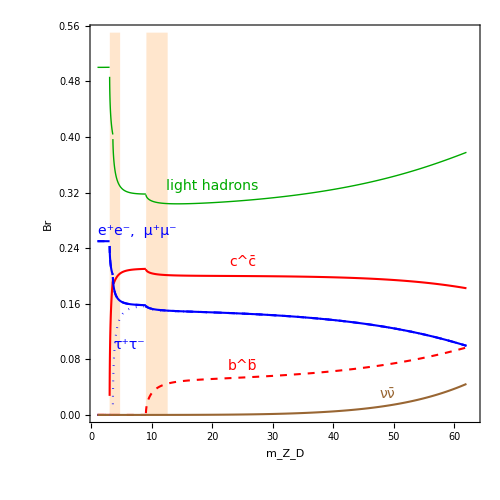

```mathematica
Zdcoupling[Y_,T3_]:=- (-mZ^2 (T3+Y) Cos[θw]+mZd^2 Y Sec[θw])/((mZ-mZd) (mZ+mZd))

ΓZdffList:=If[mZd > 2 mf, mult (gp^2 √(-4 mf^2 mZd^2+mZd^4) (mZd^2 (YL^2+YR^2)-mf^2 (YL^2-6 YL YR+YR^2)))/(24 mZd^3 π) , 0]//.{
YL->Zdcoupling[#[[2]],#[[4]]],
YR-> Zdcoupling[#[[3]],0], 
mult -> #[[5]], mf-> #[[6]],θw-> ArcSin[√0.23],mZ-> 90.2,   g->0.6535905161093165, gp -> 0.35721056657494327}&/@Zddecaymodes//N;



bottomoniumthreshold = 2*5.3;
charmoniumthreshold = 2*1.87;
hadronizationregionplot =ListPlot[{
{{1, 10^-6},{2*4.5,10^-6},{bottomoniumthreshold + 0.000001,10}, {63, 10}}
,
{{1, 10^-6},{bottomoniumthreshold+2,10^-6},{bottomoniumthreshold+2 + 0.000001,10}, {63, 10}}
,
{{1, 10^-6},{2*1.5,10^-6},{charmoniumthreshold + 0.000001,10}, {63, 10}}
,
{{1, 10^-6},{charmoniumthreshold+1,10^-6},{charmoniumthreshold+1 + 0.000001,10}, {63, 10}}
}
,Joined->True, Axes->False,  PlotRange->{{1,63},{10^-4,0.55}}, AspectRatio->1, Frame->True,FrameLabel-> {"m_a[GeV]","BR"}, PlotStyle->None, Filling->{1->{{2},Directive[Orange//Lighter//Lighter//Lighter//Lighter]}, 3->{{4},Directive[Orange//Lighter//Lighter//Lighter//Lighter]}} ];


Zddecaymodes={
{"bb", 1/6, -1/3,-1/2,  3, 4.5, Directive[Red,Dashed, Thickness->0.003]},
{"cc", 1/6, +2/3,+1/2,  3, 1.5, Directive[Red, Thickness->0.003]},
{"ee", -1/2, -1,-1/2, 1, 511/10^6,Directive[Blue,Thickness->0.003]},
{"μμ", -1/2, -1,-1/2, 1,  106/10^3, Directive[Dashed,Blue,Thickness->0.003]},
{"ττ", -1/2, -1, -1/2, 1,  1.77, Directive[Dotted,Blue,Thickness->0.003]},
{"νν", -1/2, 0          , 1/2, 3, 0, Directive[Brown,Thickness->0.003]},
{"ss", 1/6, -1/3, -1/2, 3, 0, ""},
{"dd", 1/6, -1/3,-1/2, 3, 0, ""},
{"uu", 1/6, +2/3, 1/2, 3, 0, ""}
};


Zddecaymodes2 = Append[Zddecaymodes[[1;;6]],{"jj", 0,0,0,0,0,Directive[Darker[Green],Thickness->0.002]}];

ΓZdffList2 = Append[ΓZdffList[[1;;6]], Total[ΓZdffList[[7;;9]]]];



brplot=Show[hadronizationregionplot,
Plot[Evaluate[ΓZdffList2/Total[ΓZdffList2]/.{mZd->mZdvalue}], 
{mZdvalue,1,62}
, 
PlotStyle-> Transpose[Zddecaymodes2][[7]]
,
PlotPoints->200
]
,
PlotLabel-> 
TableForm[
{Style[#[[1]], #[[7]]]&/@Zddecaymodes2}
]
, AxesOrigin->{0,0}, FrameLabel-> {"m_Z_D", "Br"}, ImageSize->500,AspectRatio->1
];



fontsize=14;
Show[
brplot
,
Graphics[{
Text[Style["e^+e^-,  μ^+μ^-",fontsize,Blue],{7.5,0.265},{0,0},{1,0}]
,
Text[Style["τ^+τ^-",fontsize,Blue],{6.3,0.1},{0,0},{1,0}]
,
Text[Style["c^c̄",fontsize,Red],{25,0.22},{0,0},{1,0}]
,
Text[Style["b^b̄",fontsize,Red],{25,0.07},{0,0},{1,0}]
,
Text[Style["light hadrons",fontsize,Darker[Green]],{20,0.33},{0,0},{1,0}]
,
Text[Style["νν̄",fontsize,Brown],{49,0.03},{0,0},{1,0}]

}]
,
PlotLabel->None
,
BaseStyle->{FontSize->17, FontFamily->"Times New Roman"}
]
```

```mathematica
RZDtable={{12.,3.9275878417522865},{12.2,3.928577620573107},{12.4,3.929524739685389},{12.6,3.9304379263436218},{12.8,3.931324849395786},{13.,3.932192258295099},{13.2,3.9331458929904013},{13.4,3.9340898327097853},{13.6,3.9350288348018965},{13.8,3.9359671150269455},{14.,3.936908414964139},{14.2,3.9379362075601367},{14.4,3.938972441588729},{14.6,3.940019824569227},{14.8,3.9410807767401796},{15.,3.9421574652940503},{15.2,3.943317544095638},{15.4,3.944496493552549},{15.6,3.945695928554457},{15.8,3.9469173074443753},{16.,3.9481619501115484},{16.2,3.9494858566356195},{16.4,3.950834946624451},{16.6,3.9522102396097365},{16.8,3.953612668367534},{17.,3.955043088818166},{17.2,3.956548659501225},{17.4,3.9580834921884396},{17.6,3.9596482787493277},{17.8,3.9612436628078287},{18.,3.962870245329715},{18.2,3.9645683132315472},{18.4,3.9662985075727892},{18.6,3.968061341258682},{18.8,3.969857300841433},{19.,3.971686849765401},{19.2,3.9735848265002285},{19.4,3.975517149641365},{19.6,3.977484238122968},{19.8,3.979486497327005},{20.,3.981524321021809},{20.200000000000003,3.9836281546410763},{20.4,3.985768237131582},{20.6,3.987944943399107},{20.8,3.990158642498727},{21.,3.9924096988279767},{21.200000000000003,3.9947249651388046},{21.4,3.997078258217687},{21.6,3.999469939158733},{21.8,4.001900367988442},{22.,4.004369904426167},{22.200000000000003,4.006902427288791},{22.4,4.009474747653499},{22.6,4.012087231721913},{22.8,4.01474024771606},{23.,4.0174341663847075},{23.200000000000003,4.0201903790693985},{23.4,4.022988227061384},{23.6,4.025828094045599},{23.8,4.028710367823186},{24.,4.031635440668145},{24.200000000000003,4.034622604620723},{24.4,4.037653358152133},{24.6,4.040728111007635},{24.8,4.043847278565442},{25.,4.047011282106038},{25.200000000000003,4.050237628247923},{25.4,4.053509669884841},{25.6,4.056827849220642},{25.8,4.06019261527807},{26.,4.063604424119011},{26.200000000000003,4.067079253805993},{26.4,4.070602063801018},{26.6,4.074173333964026},{26.8,4.077793551981852},{27.,4.081463213563363},{27.200000000000003,4.085196980746136},{27.4,4.088981215085183},{27.6,4.09281643869862},{27.8,4.096703182458238},{28.,4.1006419861749865},{28.2,4.10464637351608},{28.400000000000002,4.108703938295266},{28.6,4.1128152492817645},{28.8,4.116980884907346},{29.,4.121201433452617},{29.2,4.125489430155857},{29.400000000000002,4.129833559200792},{29.6,4.134234440447999},{29.8,4.1386927043549955},{30.,4.143208992170764},{30.2,4.147794978433883},{30.400000000000002,4.152440318575563},{30.6,4.157145688214967},{30.8,4.1619117745597585},{31.,4.16673927661453},{31.200000000000003,4.171639118014641},{31.400000000000002,4.176601825041845},{31.6,4.181628134103054},{31.8,4.186718794267257},{32.,4.191874567492457},{32.2,4.197105721744781},{32.400000000000006,4.202403569309219},{32.6,4.207768912881496},{32.8,4.213202568996203},{33.,4.2187053682763},{33.2,4.224287006376021},{33.400000000000006,4.229939509773809},{33.6,4.235663753524846},{33.8,4.2414606278226765},{34.,4.247331038275209},{34.2,4.253284181871029},{34.400000000000006,4.259312738512889},{34.6,4.265417662349161},{34.8,4.271599924108035},{35.,4.277860511404027},{35.2,4.284208188262004},{35.400000000000006,4.290636236687749},{35.6,4.297145697414714},{35.8,4.303737629359538},{36.,4.310413109963299},{36.2,4.317180529503941},{36.400000000000006,4.32403372894455},{36.6,4.330973843954401},{36.8,4.3380020301726905},{37.,4.345119463589031},{37.2,4.352334214686951},{37.400000000000006,4.359640647401328},{37.6,4.367040001656485},{37.8,4.37453353934021},{38.,4.382122544728486},{38.2,4.389814818234292},{38.400000000000006,4.397605217132449},{38.6,4.405495096011227},{38.8,4.413485833648727},{39.,4.4215788334874215},{39.2,4.42978167225711},{39.400000000000006,4.438089676659443},{39.6,4.446504327580471},{39.8,4.455027132584323},{40.,4.463659626443795},{40.2,4.4724092060376694},{40.400000000000006,4.481271648808484},{40.6,4.490248574950461},{40.8,4.49934163411863},{41.,4.508552506022471},{41.2,4.517888449663354},{41.400000000000006,4.527345679395836},{41.6,4.5369259692796415},{41.8,4.546631125949114},{42.,4.5564629892777715},{42.2,4.566428721137866},{42.400000000000006,4.576524963558872},{42.6,4.58675366076173},{42.8,4.597116793027996},{43.,4.60761637744409},{43.2,4.6182595188633275},{43.400000000000006,4.629043282171438},{43.6,4.639969799999603},{43.8,4.651041244943827},{44.,4.662259830398722},{44.2,4.67363264422634},{44.4,4.685157173677269},{44.6,4.696835760235947},{44.800000000000004,4.708670789725516},{45.,4.72066469324213},{45.2,4.732824582137702},{45.4,4.745148369847001},{45.6,4.757638629613413},{45.800000000000004,4.7702979839198765},{46.,4.7831291055359015},{46.2,4.796139170764156},{46.4,4.809326527405687},{46.6,4.822694006129783},{46.800000000000004,4.836244492336559},{47.,4.84998092733009},{47.2,4.863910595329085},{47.4,4.878032291161483},{47.6,4.892349131680499},{47.800000000000004,4.9068642946216166},{48.,4.921581019916573},{48.2,4.936506744698888},{48.4,4.951640728137144},{48.6,4.966986405478987},{48.800000000000004,4.982547279741957},{49.,4.998326923184221},{49.2,5.014332973423804},{49.4,5.030565176165216},{49.6,5.047027321105375},{49.800000000000004,5.063723273416636},{50.,5.080656975391291},{50.2,5.097836315819345},{50.400000000000006,5.115261554293654},{50.6,5.132936875278336},{50.800000000000004,5.150866547322899},{51.,5.1690549248981075},{51.2,5.187510202325249},{51.400000000000006,5.206233185908492},{51.6,5.22522849989887},{51.800000000000004,5.244500862236276},{52.,5.264055086594599},{52.2,5.283899731411053},{52.400000000000006,5.304036188332509},{52.6,5.324469571564748},{52.800000000000004,5.345205099687983},{53.,5.366248097928519},{53.2,5.387607552188522},{53.400000000000006,5.409285484239433},{53.6,5.431287553992024},{53.800000000000004,5.453619537582124},{54.,5.476287329884078},{54.2,5.499300412878852},{54.400000000000006,5.522661489711411},{54.6,5.546376827721981},{54.800000000000004,5.570452823561106},{55.,5.594896005956245},{55.2,5.619716427270439},{55.400000000000006,5.644917529985592},{55.6,5.67050625687387},{55.800000000000004,5.696489694382362},{56.,5.722875075657453},{56.2,5.749673103729387},{56.400000000000006,5.776888025209799},{56.6,5.804527532732138},{56.800000000000004,5.83259947825199},{57.,5.861111876322957},{57.2,5.890076166987364},{57.400000000000006,5.919497472500241},{57.6,5.949384316109743},{57.800000000000004,5.979745397254022},{58.,6.010589595065584},{58.2,6.041929178747952},{58.400000000000006,6.0737702239728275},{58.6,6.106122171188689},{58.800000000000004,6.138994654961492},{59.,6.172397507659523},{59.2,6.206343924843465},{59.400000000000006,6.240841018638624},{59.6,6.275899238036456},{59.800000000000004,6.311529244825741},{60.,6.347741917373607},{60.2,6.384551478344696},{60.400000000000006,6.421966162833917},{60.6,6.459997522546478},{60.800000000000004,6.498657340898211},{61.,6.537957636756114},{61.2,6.577913761623718},{61.400000000000006,6.618535160636305},{61.6,6.659834582055596},{61.800000000000004,6.7018250241800885},{62.,6.744519738834704},{62.2,6.787935305004452},{62.400000000000006,6.832082460946713},{62.6,6.8769752401007676},{62.800000000000004,6.9226279424374795},{63.,6.96905513738488},{63.2,7.0162747207499665},{63.400000000000006,7.064298796192027},{63.6,7.113142758407452},{63.800000000000004,7.162822281456594},{64.,7.2133533206707225},{64.2,7.2647551595589634},{64.4,7.317041318712509},{64.6,7.370228606960866},{64.80000000000001,7.4243341190342305},{65.,7.47937523580563},{65.2,7.53537266772052},{65.4,7.592341368862723},{65.6,7.650299576665857},{65.80000000000001,7.709265810992075},{66.,7.769258871807878},{66.2,7.830300885478586},{66.4,7.892408201223305},{66.6,7.955600439876398},{66.80000000000001,8.01989748607799},{67.,8.085319482147877},{67.2,8.151889883335231},{67.4,8.219626313225746},{67.6,8.288549641950592},{67.80000000000001,8.35868096268248},{68.,8.430041580046307},{68.2,8.502656080084598},{68.4,8.576543120368385},{68.6,8.651724557911376},{68.80000000000001,8.728222400546185},{69.,8.806058787685647},{69.2,8.885259080339944},{69.4,8.96584256075528},{69.6,9.047831630077043},{69.80000000000001,9.131248724458345},{70.,9.216116285370505},{70.2,9.302459874485248},{70.4,9.39029875668459},{70.6,9.479655187209218},{70.80000000000001,9.570551281570202},{71.,9.663008971938574},{71.2,9.757053151111053},{71.4,9.852702111817358},{71.6,9.949976942697804},{71.80000000000001,10.048898340345419},{72.,10.149486547674982},{72.2,10.25176453060136},{72.4,10.355748245919196},{72.6,10.461456165038518},{72.80000000000001,10.568906015962543},{73.,10.678114699124617},{73.2,10.789101499989881},{73.4,10.901878157727873},{73.6,11.016458535348535},{73.80000000000001,11.13285527943281},{74.,11.251079709042372},{74.2,11.37114506750384},{74.4,11.493056365147014},{74.6,11.616820214607618},{74.80000000000001,11.742441397163208},{75.,11.869922721451553},{75.2,11.999268318679203},{75.4,12.130473235590538},{75.6,12.26353345468048},{75.80000000000001,12.398442358745362},{76.,12.535190558975469},{76.2,12.673769240399379},{76.4,12.814159486941152},{76.60000000000001,12.956342508706532},{76.8,13.100296001715675},{77.,13.245993950299097},{77.2,13.393410034512469},{77.4,13.542506678719093},{77.60000000000001,13.693245512588598},{77.8,13.845583631834055},{78.,13.999473388523473},{78.2,14.154865880122502},{78.4,14.311699727423102},{78.60000000000001,14.469911802727648},{78.8,14.629433410287291},{79.,14.790190090429245},{79.2,14.952105220821597},{79.4,15.115088548903675},{79.60000000000001,15.279047229291866},{79.8,15.443881958938286},{80.,15.609486835877636}};


SaveRdataMod2={{0.36,0.12018},{0.37,0.14244},{0.38,0.1699},{0.39,0.15662},{0.4,0.17795},{0.41,0.21191},{0.42,0.21045},{0.43,0.26582},{0.438,0.31445},{0.44,0.27114},{0.45,0.31856},{0.46,0.29863},{0.47,0.36269},{0.48,0.41626},{0.483,0.42434},{0.5,0.47917},{0.51,0.53818},{0.52,0.53441},{0.53,0.6477},{0.54,0.71278},{0.55,0.76157},{0.56,0.82466},{0.58,0.9847},{0.59938,1.26713},{0.6,1.27602},{0.6024,1.4343},{0.6105,1.44391},{0.6125,1.46919},{0.62,1.56426},{0.6205,1.78021},{0.62951,1.8362},{0.63,1.83918},{0.6305,2.01462},{0.6375,1.87678},{0.64,1.82743},{0.64051,2.0713},{0.6426,2.22231},{0.65049,2.41066},{0.65952,2.66538},{0.66,2.68093},{0.6605,2.57812},{0.6626,2.77054},{0.6705,2.98936},{0.6776,3.3272},{0.68059,3.82901},{0.6875,4.09426},{0.6876,4.0981},{0.68956,4.12935},{0.69,4.1364},{0.69043,4.06039},{0.6976,4.57888},{0.7,4.736},{0.70052,4.76808},{0.7076,5.02195},{0.71047,5.57636},{0.7176,5.70707},{0.71951,6.16537},{0.72,6.28308},{0.72025,6.48024},{0.7276,6.61028},{0.73024,7.0504},{0.7375,7.51559},{0.7376,7.522},{0.74,9.23169},{0.7402,7.81113},{0.7476,8.18975},{0.7495,8.40992},{0.74979,8.44409},{0.75,8.46645},{0.7502,7.35286},{0.75028,8.81559},{0.7504,8.82912},{0.7576,8.7449},{0.7595,8.89862},{0.75979,8.92262},{0.76,9.01818},{0.76018,9.44356},{0.7604,9.27291},{0.7635,9.18243},{0.76379,9.17555},{0.764,9.19366},{0.76417,9.45586},{0.7644,9.4237},{0.765,9.44214},{0.7676,9.52205},{0.7695,9.72673},{0.76979,9.76121},{0.77,9.99286},{0.77011,10.4834},{0.7704,10.32274},{0.7732,10.85005},{0.7735,10.91999},{0.7736,10.94949},{0.77379,11.0909},{0.774,11.20199},{0.77438,11.12463},{0.7744,11.41367},{0.7756,12.35831},{0.7775,13.65382},{0.7776,13.72113},{0.77779,14.05203},{0.778,14.58469},{0.77811,15.04189},{0.77817,15.43237},{0.7782,15.02042},{0.7784,15.04593},{0.77871,15.29651},{0.77948,16.04105},{0.7796,16.15387},{0.77979,16.6373},{0.7799,17.0937},{0.78,17.36742},{0.78017,17.96852},{0.7804,18.168},{0.78059,18.39342},{0.78079,18.61971},{0.781,18.70267},{0.7814,19.00943},{0.7816,19.21468},{0.78163,19.26361},{0.78179,19.49558},{0.782,19.51737},{0.78213,19.2855},{0.78223,18.80432},{0.7824,19.24945},{0.78252,19.29009},{0.78279,19.37206},{0.7829,19.34747},{0.783,18.88315},{0.7832,17.51745},{0.7834,18.21596},{0.78351,18.16503},{0.7836,18.11474},{0.78379,17.95418},{0.784,17.37078},{0.78424,17.01961},{0.7844,17.06267},{0.785,15.57022},{0.7854,14.70865},{0.78551,14.47749},{0.7856,14.29268},{0.78579,14.06117},{0.786,13.23948},{0.78604,12.93056},{0.78618,13.5066},{0.7864,13.12601},{0.7876,12.58515},{0.7882,12.18298},{0.7892,11.50828},{0.7895,10.28934},{0.7896,9.8898},{0.78979,9.26884},{0.79,9.30908},{0.79009,9.5883},{0.7901,9.62226},{0.7904,9.55384},{0.7905,9.515},{0.7916,9.08784},{0.7932,7.58238},{0.79349,7.59868},{0.79379,7.62576},{0.794,7.73677},{0.79414,7.5686},{0.7944,7.65001},{0.7976,6.85693},{0.79949,6.78703},{0.79979,6.77794},{0.8,6.92387},{0.80002,6.92867},{0.8004,6.7746},{0.8076,5.87209},{0.80949,5.77621},{0.80979,5.762},{0.81,5.76471},{0.81014,5.66236},{0.8104,5.62342},{0.8125,5.44421},{0.8176,5.00889},{0.81949,4.98327},{0.82,4.97676},{0.82002,5.20454},{0.8276,4.36986},{0.82997,4.45226},{0.8375,3.8534},{0.8376,3.84545},{0.8391,3.64889},{0.83947,3.69744},{0.84,3.76713},{0.8432,3.47328},{0.8476,3.34969},{0.84924,3.1415},{0.8576,2.97234},{0.8596,3.19798},{0.8625,2.99413},{0.8676,2.63553},{0.8695,2.47022},{0.8776,2.27526},{0.87945,2.26273},{0.87984,2.26014},{0.88,2.25703},{0.8875,1.9867},{0.8876,1.9831},{0.88972,1.8971},{0.8932,1.98922},{0.8976,1.76211},{0.90004,1.76892},{0.9076,1.67315},{0.91,1.57469},{0.91002,1.57385},{0.915,1.50171},{0.9176,1.46471},{0.91943,1.41715},{0.91956,1.41376},{0.92,1.52625},{0.9276,1.32076},{0.93011,1.35979},{0.9376,1.1807},{0.93945,1.24033},{0.94,1.25809},{0.94219,1.25931},{0.9476,1.08959},{0.94945,1.15095},{0.95,1.1692},{0.95184,1.14956},{0.954,1.10041},{0.955,1.07844},{0.956,1.05733},{0.95745,1.12295},{0.9576,1.12975},{0.958,1.10597},{0.96,1.14217},{0.96152,1.16973},{0.963,0.98309},{0.9676,1.04334},{0.96946,1.03046},{0.97,1.0266},{0.971,1.03001},{0.9776,1.03905},{0.98,1.08035},{0.984,0.84472},{0.98402,0.90958},{0.9841,0.90913},{0.98421,0.90839},{0.985,0.84366},{0.98558,0.86662},{0.9875,0.94934},{0.9876,0.9537},{0.99,0.98578},{0.993,1.00152},{0.994,1.01414},{0.9976,1.17841},{1.,1.28743},{1.002,1.21652},{1.003,1.24341},{1.00371,1.3235},{1.00391,1.31582},{1.004,1.33791},{1.00425,1.39842},{1.00464,1.40464},{1.00496,1.41746},{1.005,1.41936},{1.0066,1.48588},{1.007,1.50828},{1.00862,2.18169},{1.01,2.38555},{1.01017,2.52534},{1.01027,2.56136},{1.0103,2.49776},{1.01034,2.41239},{1.0107,2.91542},{1.01076,2.99928},{1.01086,3.14299},{1.011,3.27799},{1.0113,3.49135},{1.01276,5.11864},{1.013,5.79143},{1.01388,6.81776},{1.015,9.43127},{1.01525,10.14716},{1.01543,10.67349},{1.01566,11.58305},{1.0157,11.74122},{1.01575,11.93964},{1.01599,13.82994},{1.01607,14.30754},{1.0162,15.08235},{1.01637,16.09538},{1.01654,17.66207},{1.01668,19.35854},{1.01673,19.68035},{1.01678,19.98223},{1.01685,20.41182},{1.01694,21.14228},{1.017,21.4738},{1.01709,22.36159},{1.0171,22.52055},{1.01716,23.47441},{1.01726,25.01183},{1.01759,29.1985},{1.01765,30.20412},{1.01766,30.35742},{1.01772,31.27712},{1.01782,32.61978},{1.01798,34.79933},{1.018,35.15911},{1.0181,36.76637},{1.01814,37.40925},{1.01821,39.17207},{1.01828,40.92831},{1.01832,42.04514},{1.01848,43.16968},{1.01862,44.20921},{1.01864,44.33669},{1.01868,44.59188},{1.01878,45.22235},{1.01881,44.94947},{1.01887,46.38056},{1.01896,47.7383},{1.019,48.77336},{1.01907,51.3376},{1.0191,51.21821},{1.01914,51.05903},{1.01921,49.97977},{1.01925,49.68513},{1.01944,48.22998},{1.01951,48.63771},{1.01962,47.52246},{1.01964,47.31957},{1.01968,46.7152},{1.01969,46.70317},{1.01979,46.60564},{1.02,44.92471},{1.02006,44.62208},{1.02013,44.24064},{1.02043,39.21917},{1.02058,38.70239},{1.0206,38.6374},{1.02065,35.69761},{1.02076,33.66329},{1.02086,32.10018},{1.02096,33.13547},{1.021,32.69651},{1.02102,32.36441},{1.02141,25.86468},{1.0215,25.07718},{1.02151,24.98968},{1.02154,24.73508},{1.02168,22.21144},{1.02182,21.03826},{1.02185,20.7867},{1.0219,20.32775},{1.022,19.40936},{1.02207,18.76611},{1.02223,17.16167},{1.02232,16.13137},{1.02246,15.51094},{1.02267,14.58192},{1.0227,14.45908},{1.02274,14.29547},{1.023,13.32596},{1.02325,12.42672},{1.02327,12.34922},{1.02397,10.75849},{1.02535,8.23463},{1.02752,4.62247},{1.0277,4.55876},{1.02774,4.57564},{1.0278,4.60097},{1.028,4.69479},{1.02812,4.38616},{1.02823,4.10348},{1.02841,4.02034},{1.0292,3.75596},{1.03358,2.40284},{1.0337,2.35371},{1.03372,2.3456},{1.03384,2.29695},{1.03386,2.3017},{1.034,2.33495},{1.03406,2.34904},{1.0375,1.96032},{1.03916,1.7731},{1.0393,1.75728},{1.03959,1.72503},{1.0396,1.72108},{1.03964,1.70536},{1.0398,1.69948},{1.04,1.6921},{1.044,1.53588},{1.046,1.45783},{1.047,1.39064},{1.0496,1.29671},{1.0497,1.28863},{1.04981,1.27975},{1.05,1.30425},{1.053,1.17347},{1.058,1.22046},{1.05952,1.10492},{1.05966,1.10033},{1.06,1.12298},{1.061,1.1077},{1.0625,1.09049},{1.065,1.07818},{1.067,1.06149},{1.068,1.0818},{1.07,1.12852},{1.076,1.17961},{1.077,1.14824},{1.08,1.08245},{1.083,1.01672},{1.086,0.95046},{1.087,0.94305},{1.0875,0.9522},{1.088,0.96085},{1.09,0.98455},{1.095,0.94136},{1.096,0.93272},{1.097,0.97193},{1.098,0.99142},{1.1,0.89996},{1.103,0.91403},{1.106,0.93303},{1.107,0.9354},{1.11,0.88637},{1.111,0.8501},{1.1125,0.83944},{1.117,0.83718},{1.12,0.87198},{1.123,0.85297},{1.127,0.82509},{1.129,0.84562},{1.13,0.9199},{1.137,0.88345},{1.1375,0.88965},{1.14,0.9107},{1.142,0.90503},{1.143,0.90165},{1.148,0.90821},{1.15,0.8955},{1.152,0.89129},{1.16,0.93641},{1.1625,0.88103},{1.163,0.87238},{1.164,0.85334},{1.167,0.85932},{1.17,0.95386},{1.171,0.97129},{1.177,0.94768},{1.18,0.93467},{1.183,0.92127},{1.186,0.90338},{1.187,0.90795},{1.1875,0.89966},{1.188,0.89125},{1.19,0.86452},{1.197,0.92673},{1.2,0.93851},{1.202,0.94528},{1.204,0.93461},{1.205,0.9448},{1.207,0.98233},{1.21,0.99026},{1.2114,0.96508},{1.2125,0.93527},{1.214,0.90476},{1.217,0.87894},{1.22,0.98171},{1.224,0.94818},{1.225,0.9398},{1.226,0.93694},{1.227,0.93369},{1.23,1.02086},{1.232,1.00232},{1.237,1.09029},{1.2375,1.09159},{1.24,1.05556},{1.246,0.99685},{1.247,1.00278},{1.25,1.05266},{1.251,1.05141},{1.252,1.05051},{1.257,1.06037},{1.26,1.04646},{1.2625,1.05306},{1.266,1.0414},{1.267,1.05268},{1.27,1.12779},{1.273,1.04058},{1.275,1.0342},{1.277,1.02775},{1.28,1.12876},{1.285,1.08273},{1.286,1.07368},{1.287,1.07765},{1.2875,1.08324},{1.29,1.12239},{1.292,1.05459},{1.296,1.12568},{1.297,1.14328},{1.3,1.20291},{1.304,1.18957},{1.305,1.18602},{1.307,1.18741},{1.31,1.18561},{1.3125,1.19436},{1.314,1.17984},{1.317,1.22812},{1.32,1.23694},{1.325,1.17594},{1.326,1.1641},{1.327,1.1521},{1.33,1.23575},{1.335,1.28161},{1.337,1.30105},{1.3375,1.29986},{1.34,1.35709},{1.345,1.2964},{1.346,1.2841},{1.347,1.31383},{1.35,1.44763},{1.353,1.50106},{1.354,1.49284},{1.357,1.46711},{1.36,1.44077},{1.362,1.35289},{1.3625,1.35851},{1.364,1.37302},{1.365,1.38328},{1.367,1.40549},{1.368,1.43772},{1.37,1.50612},{1.374,1.41415},{1.377,1.44487},{1.38,1.51386},{1.387,1.50176},{1.3875,1.50449},{1.39,1.52685},{1.393,1.55246},{1.395,1.65671},{1.397,1.58416},{1.3995,1.6733},{1.4,1.68689},{1.403,1.57211},{1.4125,1.51502},{1.42,1.52689},{1.425,1.47392},{1.4375,1.38995},{1.44,1.42411},{1.441,1.56764},{1.45,1.5529},{1.46,1.70191},{1.4625,1.73834},{1.475,1.96079},{1.48,2.04976},{1.4875,2.11148},{1.49,2.16579},{1.491,2.18723},{1.4995,2.23819},{1.5,2.24135},{1.505,2.20214},{1.5125,2.18275},{1.5245,2.21812},{1.525,2.21953},{1.53,2.22217},{1.5375,2.2266},{1.54,2.24055},{1.55,2.29639},{1.56,2.32374},{1.5625,2.25601},{1.57,2.26882},{1.5745,2.27521},{1.575,2.27596},{1.58,2.31392},{1.5875,2.34592},{1.5895,2.3833},{1.59,2.39244},{1.6,2.44139},{1.6065,2.40613},{1.61,2.39075},{1.612,2.38176},{1.6125,2.37789},{1.62,2.42668},{1.625,2.36983},{1.63,2.45154},{1.633,2.49905},{1.637,2.55787},{1.6375,2.56335},{1.64,2.78122},{1.65,2.96036},{1.653,2.90251},{1.66,2.76975},{1.662,2.61841},{1.6625,2.59046},{1.67,2.62887},{1.6745,2.65587},{1.675,2.65865},{1.68,2.67141},{1.6875,2.54909},{1.69,2.56388},{1.7,2.64809},{1.71,2.5863},{1.712,2.55792},{1.7125,2.5466},{1.72,2.59392},{1.725,2.52834},{1.73,2.49804},{1.7375,2.46475},{1.74,2.57472},{1.7485,2.58263},{1.7495,2.58367},{1.75,2.58423},{1.756,2.84643},{1.76,2.79019},{1.762,2.6436},{1.7625,2.58456},{1.769,2.21931},{1.77,2.29543},{1.775,2.70605},{1.78,2.68188},{1.7875,2.44231},{1.79,2.43623},{1.792,2.44169},{1.8,2.46278},{1.81,2.21746},{1.812,2.18439},{1.8125,2.17873},{1.82,2.35243},{1.825,2.25221},{1.83,2.41574},{1.835,2.58998},{1.8375,2.43693},{1.84,2.46016},{1.85,1.93152},{1.86,1.94406},{1.8625,1.8216},{1.87,1.88872},{1.875,1.93884},{1.8775,1.95634},{1.88,1.97338},{1.883,1.91272},{1.8875,1.83049},{1.89,1.85947},{1.9,1.99242},{1.91,1.8642},{1.9125,1.8569},{1.92,2.01938},{1.925,2.02798},{1.93,1.94881},{1.9375,1.85327},{1.94,2.0581},{1.945,1.93692},{1.95,2.18147},{1.955,1.75033},{1.96,2.34912},{1.9625,2.10179},{1.97,2.23392},{1.971,2.24961},{1.973,2.28662},{1.975,2.32459},{1.98,2.43799},{1.9875,2.21492},{1.99,2.29725},{2.,2.18},{2.2,2.38},{2.4,2.38},{2.5,2.39},{2.6,2.51},{2.7,2.3},{2.8,2.17},{2.9,2.22},{3.,2.21},{3.2,2.21},{3.4,2.38},{3.55,2.23},{3.598,2.46},{3.67,2.34626},{3.692,2.235915},{3.7,2.23},{3.704,2.2931},{3.71,2.35},{3.716,2.09195},{3.728,2.68534},{3.73,2.29},{3.74,2.80764},{3.746,2.61494},{3.75,2.9050000000000002},{3.752,3.51005},{3.758,3.7816},{3.76,2.77},{3.762,3.92},{3.764,3.676605},{3.766,4.4},{3.768,3.8},{3.77,4.014573333333333},{3.771,3.48993},{3.772,3.4759450000000003},{3.774,4.59},{3.776,3.2995349999999997},{3.78,3.755},{3.782,2.65517},{3.786,3.4},{3.788,2.47413},{3.79,2.9450000000000003},{3.794,2.40373},{3.8,2.887585},{3.81,2.615},{3.812,2.14224},{3.821,2.77},{3.824,2.5043},{3.83,2.68},{3.836,2.21264},{3.848,2.32327},{3.85,2.595},{3.86,2.33333},{3.865,3.21},{3.87,2.93},{3.872,2.4339},{3.878,2.49},{3.884,2.65},{3.886,3.39},{3.89,2.5949999999999998},{3.896,2.58},{3.902,2.78},{3.908,2.61},{3.914,3.23},{3.92,2.92},{3.926,2.71},{3.93,3.18},{3.932,3.07},{3.938,2.63},{3.94,2.94},{3.944,3.35},{3.95,3.04},{3.956,2.8},{3.96,2.79},{3.962,2.97},{3.968,3.15},{3.97,3.29},{3.974,3.4},{3.98,3.29},{3.986,3.75},{3.99,3.06},{3.992,3.43},{3.998,3.42},{4.,3.16},{4.004,3.38},{4.01,3.74},{4.016,3.84},{4.02,4.43},{4.022,4.72},{4.027,4.58},{4.028,4.68},{4.03,4.58},{4.033,4.32},{4.034,4.82},{4.04,4.470000000000001},{4.046,4.61},{4.05,4.23},{4.052,4.43},{4.058,4.29},{4.06,4.65},{4.064,4.01},{4.07,4.09},{4.076,4.06},{4.08,4.24},{4.082,3.92},{4.088,4.07},{4.09,4.06},{4.094,4.03},{4.1,4.055},{4.105,4.03},{4.109,4.06},{4.11,3.92},{4.113,4.19},{4.118,4.06},{4.12,4.11},{4.121,4.2},{4.125,4.21},{4.129,4.14},{4.13,3.99},{4.133,4.08},{4.136,4.02},{4.14,3.83},{4.141,4.09},{4.147,4.24},{4.15,4.21},{4.153,4.28},{4.159,4.11},{4.16,4.12},{4.165,4.},{4.17,4.12},{4.171,4.14},{4.177,4.06},{4.18,4.18},{4.182,4.38},{4.185,4.14},{4.19,3.94},{4.195,3.91},{4.2,3.87},{4.201,3.73},{4.208,3.71},{4.21,3.2},{4.212,3.69},{4.214,3.55},{4.22,3.465},{4.226,2.95},{4.23,3.21},{4.232,3.02},{4.238,3.06},{4.24,3.24},{4.244,3.02},{4.245,2.97},{4.25,2.91},{4.255,2.88},{4.256,3.02},{4.26,2.97},{4.262,3.09},{4.265,3.04},{4.268,2.91},{4.27,3.26},{4.274,2.92},{4.28,3.075},{4.292,2.98},{4.3,3.11},{4.304,3.34},{4.316,3.23},{4.32,2.96},{4.328,3.32},{4.34,3.35},{4.35,3.49},{4.352,3.44},{4.36,3.47},{4.364,3.65},{4.376,3.75},{4.38,3.5},{4.382,3.86},{4.388,3.82},{4.39,3.48},{4.394,3.99},{4.4,3.955},{4.406,3.79},{4.41,3.79},{4.412,3.94},{4.418,4.03},{4.42,3.68},{4.424,4.02},{4.43,4.055},{4.436,4.05},{4.44,3.85},{4.442,3.89},{4.448,3.92},{4.45,3.75},{4.46,3.755},{4.472,3.84},{4.48,3.54},{4.484,3.61},{4.496,3.72},{4.5,3.49},{4.52,3.25},{4.54,3.23},{4.56,3.62},{4.6,3.4450000000000003},{4.8,3.66},{5.,3.47},{5.2,3.44},{6.,3.44},{6.5,3.62},{7.,3.71},{7.3,3.57},{7.4,3.86},{7.44,3.37},{7.5,3.89},{7.6,3.57},{7.7,3.94},{7.8,3.59},{7.9,3.66},{8.,3.67},{8.1,3.73},{8.2,3.64},{8.3,3.4},{8.4,3.63},{8.5,3.54},{8.6,3.66},{8.7,3.44},{8.8,3.53},{8.9,3.71},{8.91,3.42},{9.,3.67},{9.1,3.63},{9.2,3.57},{9.28,3.31},{9.3,3.6},{9.36,3.46},{9.39,3.49},{9.4,3.41},{9.415,3.57},{9.45,3.8},{9.46,3.47},{9.5,3.63},{9.51,3.73},{9.6,3.55},{9.7,3.52},{9.8,3.58},{9.9,3.49},{10.,3.68},{10.04,3.6},{10.1,3.56},{10.2,3.49},{10.295,3.48},{10.43,3.54},{10.49,3.77},{10.52,3.56},{11.09,3.85},{12.,3.6799999999999997},{13.,5.4},{14.,4.119999999999999},{14.03,3.915},{14.04,3.94},{17.,3.1},{21.99,3.705},{22.,3.7650000000000006},{25.,3.8649999999999998},{25.01,4.23},{27.5,3.9},{27.55,3.9},{27.66,3.84},{29.,3.96},{29.93,3.54},{30.1,3.93},{30.38,3.84},{30.4,4.},{30.61,4.14},{31.1,3.65},{31.25,3.7},{31.29,3.82},{31.57,4.},{33.2,4.08},{33.79,3.85},{33.8,3.73},{33.89,4.15},{34.,4.11},{34.5,3.92},{34.61,3.77},{34.7,4.07},{34.85,3.75},{35.,4.15},{35.01,3.92},{35.1,3.93},{35.45,3.92},{36.1,3.92},{36.31,3.87},{36.38,3.7},{37.4,3.58},{38.3,3.88},{38.38,4.02},{40.32,4.04},{40.34,3.86},{41.18,4.19},{41.4,4.04},{41.45,4.08},{41.5,4.215},{42.5,3.87},{42.55,4.18},{43.46,3.73},{43.5,3.95},{43.53,3.98},{43.7,4.11},{44.2,4.105},{44.23,4.13},{44.41,3.96},{45.48,4.15},{45.59,4.38},{46.,4.07},{46.47,4.21},{46.6,4.18},{50.,4.476666666666667},{52.,4.5},{54.,4.859999999999999},{55.,4.640000000000001},{56.,5.140000000000001},{56.5,5.220000000000001},{57.,5.03},{57.37,4.38},{57.77,4.89},{57.97,4.78},{58.22,4.67},{58.29,5.34},{58.47,4.24},{58.5,5.31},{58.72,4.75},{58.97,5.52},{59.,5.42},{59.05,6.6},{59.06,5.74},{59.22,5.02},{59.47,5.38},{59.84,4.66},{60.,5.57},{60.8,5.615},{61.4,5.65},{63.6,6.1},{64.,5.8}};
```

```mathematica
(*only use this below 12 gev. above 12 gev, use our Br(Zd->ll) computed from Relectrons/(Rhadrons+3Relectrons+3Rneutrinos) for our specific Zd couplings, with Rhadrons computed at 3loopQCD*)

RhadZD[m_]:=If[m<12, If[m<.36,0,Interpolation[SaveRdataMod2,InterpolationOrder->1][m]], Interpolation[RZDtable,InterpolationOrder->1][m]] ;


(*use LO widths, except define total hadronic width as Γ(ZD->μμ)*RhadZD*)
TotalZdWidth[ϵ_,mA_]:=ϵ^2 ( Total[ΓZdffList2[[{3,4,5,6}]]] + ΓZdffList2[[4]]*RhadZD[mA])/.{mZd->mA} ;

ZdDecayLengthMeters[ϵ_,mZdvalue_]:=(3*^8)/TotalZdWidth[ϵ,mZdvalue](6.566666666666667*^-25)


muonfractionZD[mA_]:=ΓZdffList2[[4]]/( Total[ΓZdffList2[[{3,4,5,6}]]] + ΓZdffList2[[4]]*RhadZD[mA])/.{mZd->mA};
electronfractionZD[mA_]:=ΓZdffList2[[3]]/( Total[ΓZdffList2[[{3,4,5,6}]]] + ΓZdffList2[[4]]*RhadZD[mA])/.{mZd->mA};

(*redefine BrZdee so we always use the correct one*)
BrZdmumu[mZdvalue_]:=muonfractionZD[mZdvalue];
BrZdee[mZdvalue_]:=electronfractionZD[mZdvalue];
```

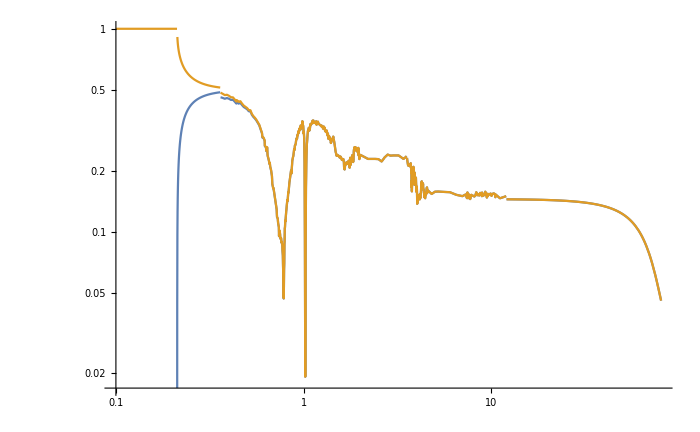

```mathematica
LogLogPlot[{BrZdmumu[m], BrZdee[m]} ,{m,0.1,80},ImageSize->700]
```

```mathematica
BrZdmumutable10MeVsteps = Transpose[{Table[1000*m,{m,0.22,50,0.01}],Table[BrZdmumu[m],{m,0.22,50,0.01}]}] //TableForm
```

220. | 0.28124
230. | 0.3559
240. | 0.394534
250. | 0.418793
260. | 0.435464
270. | 0.447561
280. | 0.456667
290. | 0.463711
300. | 0.469274
310. | 0.473743
320. | 0.477383
330. | 0.480381
340. | 0.482877
350. | 0.484973
360. | 0.459847
370. | 0.456508
380. | 0.451961
390. | 0.455653
400. | 0.452086
410. | 0.445941
420. | 0.446836
430. | 0.436554
440. | 0.435986
450. | 0.427531
460. | 0.431545
470. | 0.420223
480. | 0.411216
490. | 0.40631
500. | 0.401241
510. | 0.392121
520. | 0.392846
530. | 0.376227
540. | 0.367339
550. | 0.360962
560. | 0.353004
570. | 0.343374
580. | 0.334251
590. | 0.318774
600. | 0.304677
610. | 0.289934
620. | 0.280141
630. | 0.260132
640. | 0.260951
650. | 0.227098
660. | 0.213443
670. | 0.200827
680. | 0.174408
690. | 0.16287
700. | 0.148384
710. | 0.133535
720. | 0.120686
730. | 0.110949
740. | 0.0890131
750. | 0.0955209
760. | 0.0907398
770. | 0.0833675
780. | 0.0516275
790. | 0.0884089
800. | 0.112035
810. | 0.128758
820. | 0.143298
830. | 0.155002
840. | 0.17335
850. | 0.195023
860. | 0.193376
870. | 0.224239
880. | 0.234834
890. | 0.256033
900. | 0.265253
910. | 0.279656
920. | 0.283501
930. | 0.297698
940. | 0.306835
950. | 0.315443
960. | 0.31816
970. | 0.330309
980. | 0.32455
990. | 0.334831
1000. | 0.304118
1010. | 0.227983
1020. | 0.0213104
1030. | 0.181505
1040. | 0.2708
1050. | 0.302583
1060. | 0.320145
1070. | 0.31958
1080. | 0.324358
1090. | 0.334998
1100. | 0.34477
1110. | 0.346395
1120. | 0.348133
1130. | 0.342422
1140. | 0.343506
1150. | 0.345311
1160. | 0.340503
1170. | 0.338493
1180. | 0.340708
1190. | 0.349052
1200. | 0.340266
1210. | 0.334379
1220. | 0.335339
1230. | 0.330995
1240. | 0.327238
1250. | 0.32755
1260. | 0.328217
1270. | 0.319685
1280. | 0.319586
1290. | 0.320239
1300. | 0.31219
1310. | 0.313886
1320. | 0.30891
1330. | 0.309024
1340. | 0.297856
1350. | 0.290035
1360. | 0.290614
1370. | 0.285198
1380. | 0.28457
1390. | 0.283523
1400. | 0.271217
1410. | 0.283267
1420. | 0.283521
1430. | 0.290654
1440. | 0.292032
1450. | 0.281447
1460. | 0.270119
1470. | 0.258266
1480. | 0.246919
1490. | 0.240042
1500. | 0.235766
1510. | 0.2387
1520. | 0.237812
1530. | 0.236837
1540. | 0.235811
1550. | 0.232746
1560. | 0.231274
1570. | 0.23425
1580. | 0.231801
1590. | 0.227658
1600. | 0.225149
1610. | 0.227746
1620. | 0.225897
1630. | 0.224636
1640. | 0.209147
1650. | 0.201594
1660. | 0.20965
1670. | 0.216031
1680. | 0.214064
1690. | 0.219107
1700. | 0.215138
1710. | 0.218036
1720. | 0.217675
1730. | 0.222315
1740. | 0.218589
1750. | 0.218135
1760. | 0.208757
1770. | 0.232801
1780. | 0.213586
1790. | 0.225413
1800. | 0.224072
1810. | 0.237106
1820. | 0.229753
1830. | 0.226459
1840. | 0.224204
1850. | 0.25435
1860. | 0.253542
1870. | 0.25715
1880. | 0.251671
1890. | 0.259099
1900. | 0.250471
1910. | 0.258782
1920. | 0.248791
1930. | 0.253237
1940. | 0.246417
1950. | 0.239147
1960. | 0.229929
1970. | 0.236185
1980. | 0.225325
1990. | 0.232704
2000. | 0.239232
2010. | 0.238661
2020. | 0.238093
2030. | 0.237527
2040. | 0.236964
2050. | 0.236404
2060. | 0.235847
2070. | 0.235292
2080. | 0.23474
2090. | 0.23419
2100. | 0.233643
2110. | 0.233098
2120. | 0.232556
2130. | 0.232017
2140. | 0.23148
2150. | 0.230945
2160. | 0.230413
2170. | 0.229883
2180. | 0.229356
2190. | 0.228831
2200. | 0.228309
2210. | 0.228309
2220. | 0.228309
2230. | 0.228309
2240. | 0.228309
2250. | 0.228309
2260. | 0.228309
2270. | 0.228309
2280. | 0.228309
2290. | 0.228309
2300. | 0.228309
2310. | 0.228309
2320. | 0.228309
2330. | 0.228309
2340. | 0.228309
2350. | 0.228309
2360. | 0.228309
2370. | 0.228309
2380. | 0.228309
2390. | 0.228309
2400. | 0.228309
2410. | 0.228257
2420. | 0.228205
2430. | 0.228153
2440. | 0.228101
2450. | 0.228049
2460. | 0.227997
2470. | 0.227945
2480. | 0.227893
2490. | 0.227841
2500. | 0.227789
2510. | 0.227168
2520. | 0.226551
2530. | 0.225937
2540. | 0.225326
2550. | 0.224718
2560. | 0.224114
2570. | 0.223513
2580. | 0.222915
2590. | 0.22232
2600. | 0.221729
2610. | 0.222766
2620. | 0.223813
2630. | 0.22487
2640. | 0.225937
2650. | 0.227014
2660. | 0.228101
2670. | 0.229199
2680. | 0.230308
2690. | 0.231427
2700. | 0.232557
2710. | 0.233263
2720. | 0.233972
2730. | 0.234686
2740. | 0.235404
2750. | 0.236127
2760. | 0.236854
2770. | 0.237585
2780. | 0.238321
2790. | 0.239062
2800. | 0.239807
2810. | 0.23952
2820. | 0.239234
2830. | 0.238948
2840. | 0.238663
2850. | 0.238378
2860. | 0.238095
2870. | 0.237811
2880. | 0.237529
2890. | 0.237247
2900. | 0.236966
2910. | 0.237022
2920. | 0.237079
2930. | 0.237135
2940. | 0.237191
2950. | 0.237247
2960. | 0.237304
2970. | 0.23736
2980. | 0.237416
2990. | 0.237473
3000. | 0.237529
3010. | 0.237529
3020. | 0.237529
3030. | 0.237529
3040. | 0.237529
3050. | 0.237529
3060. | 0.237529
3070. | 0.237529
3080. | 0.237529
3090. | 0.237529
3100. | 0.237529
3110. | 0.237529
3120. | 0.237529
3130. | 0.237529
3140. | 0.237529
3150. | 0.237529
3160. | 0.237529
3170. | 0.237529
3180. | 0.237529
3190. | 0.237529
3200. | 0.237529
3210. | 0.237051
3220. | 0.236574
3230. | 0.236099
3240. | 0.235626
3250. | 0.235155
3260. | 0.234686
3270. | 0.234219
3280. | 0.233754
3290. | 0.23329
3300. | 0.232828
3310. | 0.232369
3320. | 0.231911
3330. | 0.231454
3340. | 0.231
3350. | 0.230547
3360. | 0.230096
3370. | 0.229647
3380. | 0.2292
3390. | 0.228754
3400. | 0.22831
3410. | 0.228833
3420. | 0.229357
3430. | 0.229885
3440. | 0.230414
3450. | 0.230947
3460. | 0.231481
3470. | 0.232018
3480. | 0.232558
3490. | 0.2331
3500. | 0.233645
3510. | 0.234192
3520. | 0.234741
3530. | 0.235294
3540. | 0.235849
3550. | 0.230292
3560. | 0.225423
3570. | 0.221297
3580. | 0.217595
3590. | 0.214186
3600. | 0.21157
3610. | 0.211361
3620. | 0.211225
3630. | 0.211149
3640. | 0.211125
3650. | 0.211144
3660. | 0.211201
3670. | 0.211292
3680. | 0.21296
3690. | 0.214682
3700. | 0.214867
3710. | 0.208966
3720. | 0.21114
3730. | 0.210659
3740. | 0.18958
3750. | 0.185806
3760. | 0.190243
3770. | 0.153606
3780. | 0.159759
3790. | 0.183218
3800. | 0.184881
3810. | 0.194388
3820. | 0.190934
3830. | 0.191396
3840. | 0.208261
3850. | 0.194012
3860. | 0.204096
3870. | 0.181715
3880. | 0.195195
3890. | 0.193005
3900. | 0.188471
3910. | 0.184661
3920. | 0.181007
3930. | 0.172696
3940. | 0.179978
3950. | 0.176622
3960. | 0.184595
3970. | 0.168844
3980. | 0.168696
3990. | 0.175348
4000. | 0.172178
4010. | 0.156426
4020. | 0.141091
4030. | 0.138078
4040. | 0.140117
4050. | 0.144899
4060. | 0.136504
4070. | 0.147708
4080. | 0.144418
4090. | 0.148182
4100. | 0.148202
4110. | 0.151136
4120. | 0.146833
4130. | 0.149381
4140. | 0.15295
4150. | 0.144472
4160. | 0.146297
4170. | 0.146221
4180. | 0.144876
4190. | 0.150017
4200. | 0.151531
4210. | 0.16856
4220. | 0.161268
4230. | 0.168093
4240. | 0.167162
4250. | 0.176824
4260. | 0.174875
4270. | 0.166352
4280. | 0.171547
4290. | 0.173821
4300. | 0.170356
4310. | 0.165348
4320. | 0.174654
4330. | 0.164114
4340. | 0.163373
4350. | 0.159653
4360. | 0.160098
4370. | 0.154351
4380. | 0.159205
4390. | 0.15965
4400. | 0.148344
4410. | 0.15201
4420. | 0.154539
4430. | 0.146025
4440. | 0.150479
4450. | 0.152726
4460. | 0.152558
4470. | 0.150877
4480. | 0.157624
4490. | 0.154528
4500. | 0.15877
4510. | 0.1618
4520. | 0.164949
4530. | 0.165167
4540. | 0.165386
4550. | 0.16017
4560. | 0.155272
4570. | 0.156288
4580. | 0.157318
4590. | 0.158363
4600. | 0.159422
4610. | 0.159104
4620. | 0.158788
4630. | 0.158474
4640. | 0.158162
4650. | 0.157852
4660. | 0.157543
4670. | 0.157236
4680. | 0.156931
4690. | 0.156628
4700. | 0.156326
4710. | 0.156026
4720. | 0.155727
4730. | 0.155431
4740. | 0.155136
4750. | 0.154842
4760. | 0.15455
4770. | 0.15426
4780. | 0.153971
4790. | 0.153683
4800. | 0.153397
4810. | 0.153589
4820. | 0.153782
4830. | 0.153975
4840. | 0.15417
4850. | 0.154365
4860. | 0.154561
4870. | 0.154758
4880. | 0.154956
4890. | 0.155155
4900. | 0.155355
4910. | 0.155556
4920. | 0.155757
4930. | 0.155959
4940. | 0.156163
4950. | 0.156367
4960. | 0.156572
4970. | 0.156778
4980. | 0.156984
4990. | 0.157192
5000. | 0.157401
5010. | 0.157411
5020. | 0.157423
5030. | 0.157434
5040. | 0.157446
5050. | 0.157458
5060. | 0.15747
5070. | 0.157483
5080. | 0.157496
5090. | 0.157509
5100. | 0.157523
5110. | 0.157537
5120. | 0.157551
5130. | 0.157565
5140. | 0.15758
5150. | 0.157595
5160. | 0.15761
5170. | 0.157625
5180. | 0.157641
5190. | 0.157657
5200. | 0.157673
5210. | 0.157652
5220. | 0.157631
5230. | 0.157611
5240. | 0.157591
5250. | 0.157571
5260. | 0.157551
5270. | 0.157531
5280. | 0.157512
5290. | 0.157493
5300. | 0.157474
5310. | 0.157456
5320. | 0.157437
5330. | 0.157419
5340. | 0.157401
5350. | 0.157383
5360. | 0.157365
5370. | 0.157348
5380. | 0.157331
5390. | 0.157313
5400. | 0.157297
5410. | 0.15728
5420. | 0.157263
5430. | 0.157247
5440. | 0.157231
5450. | 0.157215
5460. | 0.157199
5470. | 0.157183
5480. | 0.157168
5490. | 0.157152
5500. | 0.157137
5510. | 0.157122
5520. | 0.157107
5530. | 0.157093
5540. | 0.157078
5550. | 0.157064
5560. | 0.157049
5570. | 0.157035
5580. | 0.157021
5590. | 0.157007
5600. | 0.156994
5610. | 0.15698
5620. | 0.156967
5630. | 0.156954
5640. | 0.15694
5650. | 0.156927
5660. | 0.156915
5670. | 0.156902
5680. | 0.156889
5690. | 0.156877
5700. | 0.156864
5710. | 0.156852
5720. | 0.15684
5730. | 0.156828
5740. | 0.156816
5750. | 0.156804
5760. | 0.156793
5770. | 0.156781
5780. | 0.15677
5790. | 0.156759
5800. | 0.156747
5810. | 0.156736
5820. | 0.156725
5830. | 0.156714
5840. | 0.156704
5850. | 0.156693
5860. | 0.156683
5870. | 0.156672
5880. | 0.156662
5890. | 0.156651
5900. | 0.156641
5910. | 0.156631
5920. | 0.156621
5930. | 0.156611
5940. | 0.156602
5950. | 0.156592
5960. | 0.156582
5970. | 0.156573
5980. | 0.156563
5990. | 0.156554
6000. | 0.156545
6010. | 0.156448
6020. | 0.15635
6030. | 0.156254
6040. | 0.156157
6050. | 0.15606
6060. | 0.155964
6070. | 0.155868
6080. | 0.155772
6090. | 0.155676
6100. | 0.155581
6110. | 0.155485
6120. | 0.15539
6130. | 0.155295
6140. | 0.155201
6150. | 0.155106
6160. | 0.155012
6170. | 0.154917
6180. | 0.154823
6190. | 0.154729
6200. | 0.154636
6210. | 0.154542
6220. | 0.154449
6230. | 0.154356
6240. | 0.154263
6250. | 0.15417
6260. | 0.154078
6270. | 0.153985
6280. | 0.153893
6290. | 0.153801
6300. | 0.153709
6310. | 0.153617
6320. | 0.153526
6330. | 0.153434
6340. | 0.153343
6350. | 0.153252
6360. | 0.153161
6370. | 0.15307
6380. | 0.152979
6390. | 0.152889
6400. | 0.152799
6410. | 0.152709
6420. | 0.152619
6430. | 0.152529
6440. | 0.152439
6450. | 0.15235
6460. | 0.15226
6470. | 0.152171
6480. | 0.152082
6490. | 0.151993
6500. | 0.151905
6510. | 0.151857
6520. | 0.15181
6530. | 0.151763
6540. | 0.151717
6550. | 0.15167
6560. | 0.151623
6570. | 0.151576
6580. | 0.15153
6590. | 0.151483
6600. | 0.151437
6610. | 0.151391
6620. | 0.151344
6630. | 0.151298
6640. | 0.151252
6650. | 0.151206
6660. | 0.15116
6670. | 0.151114
6680. | 0.151068
6690. | 0.151022
6700. | 0.150976
6710. | 0.150931
6720. | 0.150885
6730. | 0.15084
6740. | 0.150794
6750. | 0.150749
6760. | 0.150703
6770. | 0.150658
6780. | 0.150613
6790. | 0.150568
6800. | 0.150523
6810. | 0.150477
6820. | 0.150432
6830. | 0.150388
6840. | 0.150343
6850. | 0.150298
6860. | 0.150253
6870. | 0.150208
6880. | 0.150164
6890. | 0.150119
6900. | 0.150075
6910. | 0.15003
6920. | 0.149986
6930. | 0.149941
6940. | 0.149897
6950. | 0.149853
6960. | 0.149809
6970. | 0.149765
6980. | 0.14972
6990. | 0.149676
7000. | 0.149632
7010. | 0.149733
7020. | 0.149835
7030. | 0.149936
7040. | 0.150037
7050. | 0.150139
7060. | 0.150241
7070. | 0.150342
7080. | 0.150445
7090. | 0.150547
7100. | 0.150649
7110. | 0.150752
7120. | 0.150854
7130. | 0.150957
7140. | 0.15106
7150. | 0.151164
7160. | 0.151267
7170. | 0.151371
7180. | 0.151474
7190. | 0.151578
7200. | 0.151682
7210. | 0.151787
7220. | 0.151891
7230. | 0.151996
7240. | 0.1521
7250. | 0.152205
7260. | 0.15231
7270. | 0.152415
7280. | 0.152521
7290. | 0.152626
7300. | 0.152732
7310. | 0.152056
7320. | 0.151385
7330. | 0.150721
7340. | 0.150062
7350. | 0.149409
7360. | 0.148761
7370. | 0.14812
7380. | 0.147484
7390. | 0.146853
7400. | 0.146227
7410. | 0.148892
7420. | 0.151655
7430. | 0.154523
7440. | 0.157502
7450. | 0.155378
7460. | 0.153311
7470. | 0.151298
7480. | 0.149337
7490. | 0.147426
7500. | 0.145564
7510. | 0.146243
7520. | 0.146928
7530. | 0.14762
7540. | 0.148318
7550. | 0.149023
7560. | 0.149734
7570. | 0.150453
7580. | 0.151178
7590. | 0.151911
7600. | 0.15265
7610. | 0.151791
7620. | 0.15094
7630. | 0.1501
7640. | 0.149269
7650. | 0.148446
7660. | 0.147633
7670. | 0.146829
7680. | 0.146034
7690. | 0.145247
7700. | 0.144468
7710. | 0.1452
7720. | 0.14594
7730. | 0.146687
7740. | 0.147442
7750. | 0.148205
7760. | 0.148975
7770. | 0.149754
7780. | 0.150541
7790. | 0.151336
7800. | 0.15214
7810. | 0.151976
7820. | 0.151813
7830. | 0.151649
7840. | 0.151487
7850. | 0.151324
7860. | 0.151162
7870. | 0.151
7880. | 0.150839
7890. | 0.150678
7900. | 0.150517
7910. | 0.150492
7920. | 0.150468
7930. | 0.150443
7940. | 0.150419
7950. | 0.150394
7960. | 0.15037
7970. | 0.150345
7980. | 0.150321
7990. | 0.150296
8000. | 0.150272
8010. | 0.150135
8020. | 0.149998
8030. | 0.149861
8040. | 0.149725
8050. | 0.149589
8060. | 0.149453
8070. | 0.149317
8080. | 0.149182
8090. | 0.149047
8100. | 0.148912
8110. | 0.14911
8120. | 0.149309
8130. | 0.149508
8140. | 0.149708
8150. | 0.149908
8160. | 0.150109
8170. | 0.15031
8180. | 0.150512
8190. | 0.150715
8200. | 0.150918
8210. | 0.151465
8220. | 0.152016
8230. | 0.152571
8240. | 0.15313
8250. | 0.153693
8260. | 0.154261
8270. | 0.154832
8280. | 0.155408
8290. | 0.155989
8300. | 0.156573
8310. | 0.15601
8320. | 0.15545
8330. | 0.154895
8340. | 0.154343
8350. | 0.153796
8360. | 0.153252
8370. | 0.152713
8380. | 0.152177
8390. | 0.151644
8400. | 0.151116
8410. | 0.15132
8420. | 0.151525
8430. | 0.151731
8440. | 0.151937
8450. | 0.152143
8460. | 0.152351
8470. | 0.152558
8480. | 0.152767
8490. | 0.152976
8500. | 0.153185
8510. | 0.152903
8520. | 0.152621
8530. | 0.152341
8540. | 0.152062
8550. | 0.151783
8560. | 0.151506
8570. | 0.15123
8580. | 0.150955
8590. | 0.150681
8600. | 0.150407
8610. | 0.150905
8620. | 0.151407
8630. | 0.151912
8640. | 0.15242
8650. | 0.152931
8660. | 0.153446
8670. | 0.153965
8680. | 0.154487
8690. | 0.155012
8700. | 0.155542
8710. | 0.155323
8720. | 0.155105
8730. | 0.154887
8740. | 0.154671
8750. | 0.154454
8760. | 0.154239
8770. | 0.154024
8780. | 0.153809
8790. | 0.153596
8800. | 0.153382
8810. | 0.152959
8820. | 0.152538
8830. | 0.152119
8840. | 0.151703
8850. | 0.151288
8860. | 0.150876
8870. | 0.150467
8880. | 0.150059
8890. | 0.149654
8900. | 0.149251
8910. | 0.156002
8920. | 0.155328
8930. | 0.154659
8940. | 0.153997
8950. | 0.15334
8960. | 0.152688
8970. | 0.152042
8980. | 0.151402
8990. | 0.150767
9000. | 0.150137
9010. | 0.150226
9020. | 0.150316
9030. | 0.150405
9040. | 0.150495
9050. | 0.150584
9060. | 0.150674
9070. | 0.150764
9080. | 0.150854
9090. | 0.150944
9100. | 0.151035
9110. | 0.151171
9120. | 0.151307
9130. | 0.151443
9140. | 0.15158
9150. | 0.151717
9160. | 0.151855
9170. | 0.151992
9180. | 0.15213
9190. | 0.152268
9200. | 0.152406
9210. | 0.153164
9220. | 0.153929
9230. | 0.154702
9240. | 0.155483
9250. | 0.156272
9260. | 0.157069
9270. | 0.157874
9280. | 0.158687
9290. | 0.155117
9300. | 0.151704
9310. | 0.152242
9320. | 0.152784
9330. | 0.15333
9340. | 0.153879
9350. | 0.154433
9360. | 0.154991
9370. | 0.15475
9380. | 0.15451
9390. | 0.154271
9400. | 0.156198
9410. | 0.153637
9420. | 0.151628
9430. | 0.150132
9440. | 0.148664
9450. | 0.147225
9460. | 0.154742
9470. | 0.15379
9480. | 0.152849
9490. | 0.151919
9500. | 0.151001
9510. | 0.148754
9520. | 0.149197
9530. | 0.149643
9540. | 0.150091
9550. | 0.150542
9560. | 0.150996
9570. | 0.151453
9580. | 0.151912
9590. | 0.152375
9600. | 0.15284
9610. | 0.152909
9620. | 0.152978
9630. | 0.153048
9640. | 0.153118
9650. | 0.153187
9660. | 0.153257
9670. | 0.153327
9680. | 0.153397
9690. | 0.153466
9700. | 0.153536
9710. | 0.153394
9720. | 0.153253
9730. | 0.153111
9740. | 0.15297
9750. | 0.152829
9760. | 0.152688
9770. | 0.152548
9780. | 0.152408
9790. | 0.152268
9800. | 0.152128
9810. | 0.152336
9820. | 0.152545
9830. | 0.152754
9840. | 0.152963
9850. | 0.153174
9860. | 0.153384
9870. | 0.153596
9880. | 0.153808
9890. | 0.15402
9900. | 0.154233
9910. | 0.153782
9920. | 0.153333
9930. | 0.152887
9940. | 0.152444
9950. | 0.152003
9960. | 0.151565
9970. | 0.151129
9980. | 0.150696
9990. | 0.150265
10000. | 0.149837
10010. | 0.150286
10020. | 0.150739
10030. | 0.151194
10040. | 0.151652
10050. | 0.151805
10060. | 0.151958
10070. | 0.152112
10080. | 0.152266
10090. | 0.15242
10100. | 0.152574
10110. | 0.152737
10120. | 0.1529
10130. | 0.153063
10140. | 0.153226
10150. | 0.15339
10160. | 0.153555
10170. | 0.153719
10180. | 0.153884
10190. | 0.15405
10200. | 0.154216
10210. | 0.15424
10220. | 0.154265
10230. | 0.154289
10240. | 0.154314
10250. | 0.154338
10260. | 0.154363
10270. | 0.154387
10280. | 0.154412
10290. | 0.154436
10300. | 0.154395
10310. | 0.154289
10320. | 0.154183
10330. | 0.154077
10340. | 0.153971
10350. | 0.153865
10360. | 0.153759
10370. | 0.153654
10380. | 0.153548
10390. | 0.153443
10400. | 0.153338
10410. | 0.153233
10420. | 0.153128
10430. | 0.153024
10440. | 0.152131
10450. | 0.151248
10460. | 0.150376
10470. | 0.149514
10480. | 0.148661
10490. | 0.147818
10500. | 0.149364
10510. | 0.150941
10520. | 0.152553
10530. | 0.152434
10540. | 0.152315
10550. | 0.152197
10560. | 0.152079
10570. | 0.151961
10580. | 0.151843
10590. | 0.151725
10600. | 0.151608
10610. | 0.15149
10620. | 0.151373
10630. | 0.151256
10640. | 0.15114
10650. | 0.151023
10660. | 0.150907
10670. | 0.15079
10680. | 0.150674
10690. | 0.150559
10700. | 0.150443
10710. | 0.150327
10720. | 0.150212
10730. | 0.150097
10740. | 0.149982
10750. | 0.149867
10760. | 0.149753
10770. | 0.149638
10780. | 0.149524
10790. | 0.14941
10800. | 0.149296
10810. | 0.149183
10820. | 0.149069
10830. | 0.148956
10840. | 0.148842
10850. | 0.148729
10860. | 0.148617
10870. | 0.148504
10880. | 0.148391
10890. | 0.148279
10900. | 0.148167
10910. | 0.148055
10920. | 0.147943
10930. | 0.147832
10940. | 0.14772
10950. | 0.147609
10960. | 0.147498
10970. | 0.147387
10980. | 0.147276
10990. | 0.147165
11000. | 0.147055
11010. | 0.146945
11020. | 0.146835
11030. | 0.146725
11040. | 0.146615
11050. | 0.146505
11060. | 0.146396
11070. | 0.146286
11080. | 0.146177
11090. | 0.146068
11100. | 0.146108
11110. | 0.146147
11120. | 0.146187
11130. | 0.146227
11140. | 0.146266
11150. | 0.146306
11160. | 0.146346
11170. | 0.146385
11180. | 0.146425
11190. | 0.146465
11200. | 0.146505
11210. | 0.146544
11220. | 0.146584
11230. | 0.146624
11240. | 0.146664
11250. | 0.146704
11260. | 0.146744
11270. | 0.146784
11280. | 0.146824
11290. | 0.146864
11300. | 0.146904
11310. | 0.146944
11320. | 0.146984
11330. | 0.147024
11340. | 0.147064
11350. | 0.147104
11360. | 0.147144
11370. | 0.147184
11380. | 0.147224
11390. | 0.147265
11400. | 0.147305
11410. | 0.147345
11420. | 0.147385
11430. | 0.147426
11440. | 0.147466
11450. | 0.147506
11460. | 0.147547
11470. | 0.147587
11480. | 0.147627
11490. | 0.147668
11500. | 0.147708
11510. | 0.147749
11520. | 0.147789
11530. | 0.14783
11540. | 0.14787
11550. | 0.147911
11560. | 0.147952
11570. | 0.147992
11580. | 0.148033
11590. | 0.148074
11600. | 0.148114
11610. | 0.148155
11620. | 0.148196
11630. | 0.148237
11640. | 0.148277
11650. | 0.148318
11660. | 0.148359
11670. | 0.1484
11680. | 0.148441
11690. | 0.148482
11700. | 0.148523
11710. | 0.148564
11720. | 0.148605
11730. | 0.148646
11740. | 0.148687
11750. | 0.148728
11760. | 0.148769
11770. | 0.14881
11780. | 0.148851
11790. | 0.148892
11800. | 0.148933
11810. | 0.148974
11820. | 0.149016
11830. | 0.149057
11840. | 0.149098
11850. | 0.149139
11860. | 0.149181
11870. | 0.149222
11880. | 0.149263
11890. | 0.149305
11900. | 0.149346
11910. | 0.149388
11920. | 0.149429
11930. | 0.149471
11940. | 0.149512
11950. | 0.149554
11960. | 0.149595
11970. | 0.149637
11980. | 0.149678
11990. | 0.14972
12000. | 0.144407
12010. | 0.144406
12020. | 0.144405
12030. | 0.144403
12040. | 0.144402
12050. | 0.144401
12060. | 0.1444
12070. | 0.144398
12080. | 0.144397
12090. | 0.144396
12100. | 0.144395
12110. | 0.144393
12120. | 0.144392
12130. | 0.144391
12140. | 0.14439
12150. | 0.144389
12160. | 0.144387
12170. | 0.144386
12180. | 0.144385
12190. | 0.144384
12200. | 0.144382
12210. | 0.144381
12220. | 0.14438
12230. | 0.144379
12240. | 0.144378
12250. | 0.144376
12260. | 0.144375
12270. | 0.144374
12280. | 0.144373
12290. | 0.144372
12300. | 0.14437
12310. | 0.144369
12320. | 0.144368
12330. | 0.144367
12340. | 0.144366
12350. | 0.144365
12360. | 0.144363
12370. | 0.144362
12380. | 0.144361
12390. | 0.14436
12400. | 0.144359
12410. | 0.144357
12420. | 0.144356
12430. | 0.144355
12440. | 0.144354
12450. | 0.144353
12460. | 0.144352
12470. | 0.144351
12480. | 0.14435
12490. | 0.144348
12500. | 0.144347
12510. | 0.144346
12520. | 0.144345
12530. | 0.144344
12540. | 0.144343
12550. | 0.144342
12560. | 0.14434
12570. | 0.144339
12580. | 0.144338
12590. | 0.144337
12600. | 0.144336
12610. | 0.144335
12620. | 0.144334
12630. | 0.144333
12640. | 0.144332
12650. | 0.14433
12660. | 0.144329
12670. | 0.144328
12680. | 0.144327
12690. | 0.144326
12700. | 0.144325
12710. | 0.144324
12720. | 0.144323
12730. | 0.144322
12740. | 0.144321
12750. | 0.144319
12760. | 0.144318
12770. | 0.144317
12780. | 0.144316
12790. | 0.144315
12800. | 0.144314
12810. | 0.144313
12820. | 0.144312
12830. | 0.144311
12840. | 0.14431
12850. | 0.144309
12860. | 0.144308
12870. | 0.144307
12880. | 0.144305
12890. | 0.144304
12900. | 0.144303
12910. | 0.144302
12920. | 0.144301
12930. | 0.1443
12940. | 0.144299
12950. | 0.144298
12960. | 0.144297
12970. | 0.144296
12980. | 0.144295
12990. | 0.144294
13000. | 0.144293
13010. | 0.144292
13020. | 0.14429
13030. | 0.144289
13040. | 0.144288
13050. | 0.144287
13060. | 0.144286
13070. | 0.144285
13080. | 0.144284
13090. | 0.144282
13100. | 0.144281
13110. | 0.14428
13120. | 0.144279
13130. | 0.144278
13140. | 0.144277
13150. | 0.144276
13160. | 0.144274
13170. | 0.144273
13180. | 0.144272
13190. | 0.144271
13200. | 0.14427
13210. | 0.144269
13220. | 0.144268
13230. | 0.144266
13240. | 0.144265
13250. | 0.144264
13260. | 0.144263
13270. | 0.144262
13280. | 0.144261
13290. | 0.14426
13300. | 0.144259
13310. | 0.144257
13320. | 0.144256
13330. | 0.144255
13340. | 0.144254
13350. | 0.144253
13360. | 0.144252
13370. | 0.144251
13380. | 0.14425
13390. | 0.144248
13400. | 0.144247
13410. | 0.144246
13420. | 0.144245
13430. | 0.144244
13440. | 0.144243
13450. | 0.144242
13460. | 0.144241
13470. | 0.14424
13480. | 0.144238
13490. | 0.144237
13500. | 0.144236
13510. | 0.144235
13520. | 0.144234
13530. | 0.144233
13540. | 0.144232
13550. | 0.144231
13560. | 0.14423
13570. | 0.144228
13580. | 0.144227
13590. | 0.144226
13600. | 0.144225
13610. | 0.144224
13620. | 0.144223
13630. | 0.144222
13640. | 0.144221
13650. | 0.14422
13660. | 0.144219
13670. | 0.144217
13680. | 0.144216
13690. | 0.144215
13700. | 0.144214
13710. | 0.144213
13720. | 0.144212
13730. | 0.144211
13740. | 0.14421
13750. | 0.144209
13760. | 0.144208
13770. | 0.144206
13780. | 0.144205
13790. | 0.144204
13800. | 0.144203
13810. | 0.144202
13820. | 0.144201
13830. | 0.1442
13840. | 0.144199
13850. | 0.144198
13860. | 0.144196
13870. | 0.144195
13880. | 0.144194
13890. | 0.144193
13900. | 0.144192
13910. | 0.144191
13920. | 0.14419
13930. | 0.144189
13940. | 0.144188
13950. | 0.144187
13960. | 0.144186
13970. | 0.144184
13980. | 0.144183
13990. | 0.144182
14000. | 0.144181
14010. | 0.14418
14020. | 0.144179
14030. | 0.144178
14040. | 0.144176
14050. | 0.144175
14060. | 0.144174
14070. | 0.144173
14080. | 0.144172
14090. | 0.14417
14100. | 0.144169
14110. | 0.144168
14120. | 0.144167
14130. | 0.144166
14140. | 0.144165
14150. | 0.144163
14160. | 0.144162
14170. | 0.144161
14180. | 0.14416
14190. | 0.144159
14200. | 0.144157
14210. | 0.144156
14220. | 0.144155
14230. | 0.144154
14240. | 0.144153
14250. | 0.144152
14260. | 0.14415
14270. | 0.144149
14280. | 0.144148
14290. | 0.144147
14300. | 0.144146
14310. | 0.144144
14320. | 0.144143
14330. | 0.144142
14340. | 0.144141
14350. | 0.14414
14360. | 0.144138
14370. | 0.144137
14380. | 0.144136
14390. | 0.144135
14400. | 0.144134
14410. | 0.144133
14420. | 0.144131
14430. | 0.14413
14440. | 0.144129
14450. | 0.144128
14460. | 0.144127
14470. | 0.144125
14480. | 0.144124
14490. | 0.144123
14500. | 0.144122
14510. | 0.144121
14520. | 0.144119
14530. | 0.144118
14540. | 0.144117
14550. | 0.144116
14560. | 0.144115
14570. | 0.144113
14580. | 0.144112
14590. | 0.144111
14600. | 0.14411
14610. | 0.144109
14620. | 0.144107
14630. | 0.144106
14640. | 0.144105
14650. | 0.144104
14660. | 0.144103
14670. | 0.144101
14680. | 0.1441
14690. | 0.144099
14700. | 0.144098
14710. | 0.144097
14720. | 0.144095
14730. | 0.144094
14740. | 0.144093
14750. | 0.144092
14760. | 0.144091
14770. | 0.144089
14780. | 0.144088
14790. | 0.144087
14800. | 0.144086
14810. | 0.144085
14820. | 0.144083
14830. | 0.144082
14840. | 0.144081
14850. | 0.14408
14860. | 0.144079
14870. | 0.144077
14880. | 0.144076
14890. | 0.144075
14900. | 0.144074
14910. | 0.144073
14920. | 0.144071
14930. | 0.14407
14940. | 0.144069
14950. | 0.144068
14960. | 0.144066
14970. | 0.144065
14980. | 0.144064
14990. | 0.144063
15000. | 0.144062
15010. | 0.14406
15020. | 0.144059
15030. | 0.144058
15040. | 0.144056
15050. | 0.144055
15060. | 0.144054
15070. | 0.144052
15080. | 0.144051
15090. | 0.14405
15100. | 0.144049
15110. | 0.144047
15120. | 0.144046
15130. | 0.144045
15140. | 0.144043
15150. | 0.144042
15160. | 0.144041
15170. | 0.14404
15180. | 0.144038
15190. | 0.144037
15200. | 0.144036
15210. | 0.144034
15220. | 0.144033
15230. | 0.144032
15240. | 0.14403
15250. | 0.144029
15260. | 0.144028
15270. | 0.144026
15280. | 0.144025
15290. | 0.144024
15300. | 0.144022
15310. | 0.144021
15320. | 0.14402
15330. | 0.144019
15340. | 0.144017
15350. | 0.144016
15360. | 0.144015
15370. | 0.144013
15380. | 0.144012
15390. | 0.144011
15400. | 0.144009
15410. | 0.144008
15420. | 0.144007
15430. | 0.144005
15440. | 0.144004
15450. | 0.144003
15460. | 0.144001
15470. | 0.144
15480. | 0.143999
15490. | 0.143997
15500. | 0.143996
15510. | 0.143995
15520. | 0.143993
15530. | 0.143992
15540. | 0.143991
15550. | 0.143989
15560. | 0.143988
15570. | 0.143987
15580. | 0.143985
15590. | 0.143984
15600. | 0.143983
15610. | 0.143981
15620. | 0.14398
15630. | 0.143979
15640. | 0.143977
15650. | 0.143976
15660. | 0.143975
15670. | 0.143973
15680. | 0.143972
15690. | 0.143971
15700. | 0.143969
15710. | 0.143968
15720. | 0.143967
15730. | 0.143965
15740. | 0.143964
15750. | 0.143962
15760. | 0.143961
15770. | 0.14396
15780. | 0.143958
15790. | 0.143957
15800. | 0.143956
15810. | 0.143954
15820. | 0.143953
15830. | 0.143952
15840. | 0.14395
15850. | 0.143949
15860. | 0.143947
15870. | 0.143946
15880. | 0.143945
15890. | 0.143943
15900. | 0.143942
15910. | 0.143941
15920. | 0.143939
15930. | 0.143938
15940. | 0.143936
15950. | 0.143935
15960. | 0.143934
15970. | 0.143932
15980. | 0.143931
15990. | 0.14393
16000. | 0.143928
16010. | 0.143927
16020. | 0.143925
16030. | 0.143924
16040. | 0.143922
16050. | 0.143921
16060. | 0.14392
16070. | 0.143918
16080. | 0.143917
16090. | 0.143915
16100. | 0.143914
16110. | 0.143912
16120. | 0.143911
16130. | 0.143909
16140. | 0.143908
16150. | 0.143906
16160. | 0.143905
16170. | 0.143904
16180. | 0.143902
16190. | 0.143901
16200. | 0.143899
16210. | 0.143898
16220. | 0.143896
16230. | 0.143895
16240. | 0.143893
16250. | 0.143892
16260. | 0.14389
16270. | 0.143889
16280. | 0.143887
16290. | 0.143886
16300. | 0.143884
16310. | 0.143883
16320. | 0.143881
16330. | 0.14388
16340. | 0.143878
16350. | 0.143877
16360. | 0.143876
16370. | 0.143874
16380. | 0.143873
16390. | 0.143871
16400. | 0.14387
16410. | 0.143868
16420. | 0.143867
16430. | 0.143865
16440. | 0.143864
16450. | 0.143862
16460. | 0.143861
16470. | 0.143859
16480. | 0.143858
16490. | 0.143856
16500. | 0.143855
16510. | 0.143853
16520. | 0.143852
16530. | 0.14385
16540. | 0.143849
16550. | 0.143847
16560. | 0.143846
16570. | 0.143844
16580. | 0.143843
16590. | 0.143841
16600. | 0.14384
16610. | 0.143838
16620. | 0.143837
16630. | 0.143835
16640. | 0.143833
16650. | 0.143832
16660. | 0.14383
16670. | 0.143829
16680. | 0.143827
16690. | 0.143826
16700. | 0.143824
16710. | 0.143823
16720. | 0.143821
16730. | 0.14382
16740. | 0.143818
16750. | 0.143817
16760. | 0.143815
16770. | 0.143814
16780. | 0.143812
16790. | 0.143811
16800. | 0.143809
16810. | 0.143807
16820. | 0.143806
16830. | 0.143804
16840. | 0.143803
16850. | 0.143801
16860. | 0.1438
16870. | 0.143798
16880. | 0.143797
16890. | 0.143795
16900. | 0.143793
16910. | 0.143792
16920. | 0.14379
16930. | 0.143789
16940. | 0.143787
16950. | 0.143786
16960. | 0.143784
16970. | 0.143783
16980. | 0.143781
16990. | 0.143779
17000. | 0.143778
17010. | 0.143776
17020. | 0.143775
17030. | 0.143773
17040. | 0.143771
17050. | 0.14377
17060. | 0.143768
17070. | 0.143766
17080. | 0.143765
17090. | 0.143763
17100. | 0.143762
17110. | 0.14376
17120. | 0.143758
17130. | 0.143757
17140. | 0.143755
17150. | 0.143753
17160. | 0.143752
17170. | 0.14375
17180. | 0.143748
17190. | 0.143747
17200. | 0.143745
17210. | 0.143744
17220. | 0.143742
17230. | 0.14374
17240. | 0.143739
17250. | 0.143737
17260. | 0.143735
17270. | 0.143734
17280. | 0.143732
17290. | 0.14373
17300. | 0.143729
17310. | 0.143727
17320. | 0.143725
17330. | 0.143724
17340. | 0.143722
17350. | 0.14372
17360. | 0.143719
17370. | 0.143717
17380. | 0.143715
17390. | 0.143714
17400. | 0.143712
17410. | 0.14371
17420. | 0.143709
17430. | 0.143707
17440. | 0.143705
17450. | 0.143703
17460. | 0.143702
17470. | 0.1437
17480. | 0.143698
17490. | 0.143697
17500. | 0.143695
17510. | 0.143693
17520. | 0.143692
17530. | 0.14369
17540. | 0.143688
17550. | 0.143687
17560. | 0.143685
17570. | 0.143683
17580. | 0.143681
17590. | 0.14368
17600. | 0.143678
17610. | 0.143676
17620. | 0.143675
17630. | 0.143673
17640. | 0.143671
17650. | 0.143669
17660. | 0.143668
17670. | 0.143666
17680. | 0.143664
17690. | 0.143663
17700. | 0.143661
17710. | 0.143659
17720. | 0.143657
17730. | 0.143656
17740. | 0.143654
17750. | 0.143652
17760. | 0.14365
17770. | 0.143649
17780. | 0.143647
17790. | 0.143645
17800. | 0.143644
17810. | 0.143642
17820. | 0.14364
17830. | 0.143638
17840. | 0.143637
17850. | 0.143635
17860. | 0.143633
17870. | 0.143631
17880. | 0.14363
17890. | 0.143628
17900. | 0.143626
17910. | 0.143624
17920. | 0.143623
17930. | 0.143621
17940. | 0.143619
17950. | 0.143617
17960. | 0.143616
17970. | 0.143614
17980. | 0.143612
17990. | 0.14361
18000. | 0.143608
18010. | 0.143607
18020. | 0.143605
18030. | 0.143603
18040. | 0.143601
18050. | 0.143599
18060. | 0.143598
18070. | 0.143596
18080. | 0.143594
18090. | 0.143592
18100. | 0.14359
18110. | 0.143588
18120. | 0.143587
18130. | 0.143585
18140. | 0.143583
18150. | 0.143581
18160. | 0.143579
18170. | 0.143577
18180. | 0.143576
18190. | 0.143574
18200. | 0.143572
18210. | 0.14357
18220. | 0.143568
18230. | 0.143566
18240. | 0.143564
18250. | 0.143563
18260. | 0.143561
18270. | 0.143559
18280. | 0.143557
18290. | 0.143555
18300. | 0.143553
18310. | 0.143551
18320. | 0.14355
18330. | 0.143548
18340. | 0.143546
18350. | 0.143544
18360. | 0.143542
18370. | 0.14354
18380. | 0.143538
18390. | 0.143537
18400. | 0.143535
18410. | 0.143533
18420. | 0.143531
18430. | 0.143529
18440. | 0.143527
18450. | 0.143525
18460. | 0.143523
18470. | 0.143521
18480. | 0.14352
18490. | 0.143518
18500. | 0.143516
18510. | 0.143514
18520. | 0.143512
18530. | 0.14351
18540. | 0.143508
18550. | 0.143506
18560. | 0.143504
18570. | 0.143502
18580. | 0.143501
18590. | 0.143499
18600. | 0.143497
18610. | 0.143495
18620. | 0.143493
18630. | 0.143491
18640. | 0.143489
18650. | 0.143487
18660. | 0.143485
18670. | 0.143483
18680. | 0.143481
18690. | 0.143479
18700. | 0.143478
18710. | 0.143476
18720. | 0.143474
18730. | 0.143472
18740. | 0.14347
18750. | 0.143468
18760. | 0.143466
18770. | 0.143464
18780. | 0.143462
18790. | 0.14346
18800. | 0.143458
18810. | 0.143456
18820. | 0.143454
18830. | 0.143452
18840. | 0.14345
18850. | 0.143448
18860. | 0.143446
18870. | 0.143444
18880. | 0.143443
18890. | 0.143441
18900. | 0.143439
18910. | 0.143437
18920. | 0.143435
18930. | 0.143433
18940. | 0.143431
18950. | 0.143429
18960. | 0.143427
18970. | 0.143425
18980. | 0.143423
18990. | 0.143421
19000. | 0.143419
19010. | 0.143417
19020. | 0.143415
19030. | 0.143413
19040. | 0.143411
19050. | 0.143409
19060. | 0.143407
19070. | 0.143405
19080. | 0.143403
19090. | 0.143401
19100. | 0.143399
19110. | 0.143397
19120. | 0.143395
19130. | 0.143393
19140. | 0.143391
19150. | 0.143388
19160. | 0.143386
19170. | 0.143384
19180. | 0.143382
19190. | 0.14338
19200. | 0.143378
19210. | 0.143376
19220. | 0.143374
19230. | 0.143372
19240. | 0.14337
19250. | 0.143368
19260. | 0.143366
19270. | 0.143364
19280. | 0.143362
19290. | 0.14336
19300. | 0.143358
19310. | 0.143356
19320. | 0.143353
19330. | 0.143351
19340. | 0.143349
19350. | 0.143347
19360. | 0.143345
19370. | 0.143343
19380. | 0.143341
19390. | 0.143339
19400. | 0.143337
19410. | 0.143335
19420. | 0.143333
19430. | 0.143331
19440. | 0.143329
19450. | 0.143326
19460. | 0.143324
19470. | 0.143322
19480. | 0.14332
19490. | 0.143318
19500. | 0.143316
19510. | 0.143314
19520. | 0.143312
19530. | 0.14331
19540. | 0.143307
19550. | 0.143305
19560. | 0.143303
19570. | 0.143301
19580. | 0.143299
19590. | 0.143297
19600. | 0.143295
19610. | 0.143293
19620. | 0.143291
19630. | 0.143288
19640. | 0.143286
19650. | 0.143284
19660. | 0.143282
19670. | 0.14328
19680. | 0.143278
19690. | 0.143276
19700. | 0.143273
19710. | 0.143271
19720. | 0.143269
19730. | 0.143267
19740. | 0.143265
19750. | 0.143263
19760. | 0.143261
19770. | 0.143258
19780. | 0.143256
19790. | 0.143254
19800. | 0.143252
19810. | 0.14325
19820. | 0.143248
19830. | 0.143246
19840. | 0.143243
19850. | 0.143241
19860. | 0.143239
19870. | 0.143237
19880. | 0.143235
19890. | 0.143232
19900. | 0.14323
19910. | 0.143228
19920. | 0.143226
19930. | 0.143224
19940. | 0.143222
19950. | 0.143219
19960. | 0.143217
19970. | 0.143215
19980. | 0.143213
19990. | 0.143211
20000. | 0.143209
20010. | 0.143206
20020. | 0.143204
20030. | 0.143202
20040. | 0.1432
20050. | 0.143197
20060. | 0.143195
20070. | 0.143193
20080. | 0.143191
20090. | 0.143188
20100. | 0.143186
20110. | 0.143184
20120. | 0.143182
20130. | 0.143179
20140. | 0.143177
20150. | 0.143175
20160. | 0.143173
20170. | 0.14317
20180. | 0.143168
20190. | 0.143166
20200. | 0.143164
20210. | 0.143161
20220. | 0.143159
20230. | 0.143157
20240. | 0.143154
20250. | 0.143152
20260. | 0.14315
20270. | 0.143148
20280. | 0.143145
20290. | 0.143143
20300. | 0.143141
20310. | 0.143138
20320. | 0.143136
20330. | 0.143134
20340. | 0.143132
20350. | 0.143129
20360. | 0.143127
20370. | 0.143125
20380. | 0.143123
20390. | 0.14312
20400. | 0.143118
20410. | 0.143116
20420. | 0.143113
20430. | 0.143111
20440. | 0.143109
20450. | 0.143106
20460. | 0.143104
20470. | 0.143102
20480. | 0.143099
20490. | 0.143097
20500. | 0.143095
20510. | 0.143092
20520. | 0.14309
20530. | 0.143088
20540. | 0.143085
20550. | 0.143083
20560. | 0.143081
20570. | 0.143079
20580. | 0.143076
20590. | 0.143074
20600. | 0.143072
20610. | 0.143069
20620. | 0.143067
20630. | 0.143064
20640. | 0.143062
20650. | 0.14306
20660. | 0.143057
20670. | 0.143055
20680. | 0.143053
20690. | 0.14305
20700. | 0.143048
20710. | 0.143046
20720. | 0.143043
20730. | 0.143041
20740. | 0.143039
20750. | 0.143036
20760. | 0.143034
20770. | 0.143031
20780. | 0.143029
20790. | 0.143027
20800. | 0.143024
20810. | 0.143022
20820. | 0.14302
20830. | 0.143017
20840. | 0.143015
20850. | 0.143012
20860. | 0.14301
20870. | 0.143008
20880. | 0.143005
20890. | 0.143003
20900. | 0.143
20910. | 0.142998
20920. | 0.142996
20930. | 0.142993
20940. | 0.142991
20950. | 0.142988
20960. | 0.142986
20970. | 0.142984
20980. | 0.142981
20990. | 0.142979
21000. | 0.142976
21010. | 0.142974
21020. | 0.142971
21030. | 0.142969
21040. | 0.142967
21050. | 0.142964
21060. | 0.142962
21070. | 0.142959
21080. | 0.142957
21090. | 0.142954
21100. | 0.142952
21110. | 0.142949
21120. | 0.142947
21130. | 0.142944
21140. | 0.142942
21150. | 0.142939
21160. | 0.142937
21170. | 0.142935
21180. | 0.142932
21190. | 0.14293
21200. | 0.142927
21210. | 0.142925
21220. | 0.142922
21230. | 0.14292
21240. | 0.142917
21250. | 0.142915
21260. | 0.142912
21270. | 0.14291
21280. | 0.142907
21290. | 0.142905
21300. | 0.142902
21310. | 0.1429
21320. | 0.142897
21330. | 0.142895
21340. | 0.142892
21350. | 0.14289
21360. | 0.142887
21370. | 0.142885
21380. | 0.142882
21390. | 0.14288
21400. | 0.142877
21410. | 0.142875
21420. | 0.142872
21430. | 0.142869
21440. | 0.142867
21450. | 0.142864
21460. | 0.142862
21470. | 0.142859
21480. | 0.142857
21490. | 0.142854
21500. | 0.142852
21510. | 0.142849
21520. | 0.142847
21530. | 0.142844
21540. | 0.142842
21550. | 0.142839
21560. | 0.142836
21570. | 0.142834
21580. | 0.142831
21590. | 0.142829
21600. | 0.142826
21610. | 0.142824
21620. | 0.142821
21630. | 0.142819
21640. | 0.142816
21650. | 0.142813
21660. | 0.142811
21670. | 0.142808
21680. | 0.142806
21690. | 0.142803
21700. | 0.1428
21710. | 0.142798
21720. | 0.142795
21730. | 0.142793
21740. | 0.14279
21750. | 0.142788
21760. | 0.142785
21770. | 0.142782
21780. | 0.14278
21790. | 0.142777
21800. | 0.142775
21810. | 0.142772
21820. | 0.142769
21830. | 0.142767
21840. | 0.142764
21850. | 0.142761
21860. | 0.142759
21870. | 0.142756
21880. | 0.142754
21890. | 0.142751
21900. | 0.142748
21910. | 0.142746
21920. | 0.142743
21930. | 0.142741
21940. | 0.142738
21950. | 0.142735
21960. | 0.142733
21970. | 0.14273
21980. | 0.142727
21990. | 0.142725
22000. | 0.142722
22010. | 0.142719
22020. | 0.142717
22030. | 0.142714
22040. | 0.142711
22050. | 0.142709
22060. | 0.142706
22070. | 0.142703
22080. | 0.142701
22090. | 0.142698
22100. | 0.142695
22110. | 0.142693
22120. | 0.14269
22130. | 0.142687
22140. | 0.142685
22150. | 0.142682
22160. | 0.142679
22170. | 0.142676
22180. | 0.142674
22190. | 0.142671
22200. | 0.142668
22210. | 0.142666
22220. | 0.142663
22230. | 0.14266
22240. | 0.142657
22250. | 0.142655
22260. | 0.142652
22270. | 0.142649
22280. | 0.142647
22290. | 0.142644
22300. | 0.142641
22310. | 0.142638
22320. | 0.142636
22330. | 0.142633
22340. | 0.14263
22350. | 0.142627
22360. | 0.142625
22370. | 0.142622
22380. | 0.142619
22390. | 0.142617
22400. | 0.142614
22410. | 0.142611
22420. | 0.142608
22430. | 0.142605
22440. | 0.142603
22450. | 0.1426
22460. | 0.142597
22470. | 0.142594
22480. | 0.142592
22490. | 0.142589
22500. | 0.142586
22510. | 0.142583
22520. | 0.142581
22530. | 0.142578
22540. | 0.142575
22550. | 0.142572
22560. | 0.142569
22570. | 0.142567
22580. | 0.142564
22590. | 0.142561
22600. | 0.142558
22610. | 0.142556
22620. | 0.142553
22630. | 0.14255
22640. | 0.142547
22650. | 0.142544
22660. | 0.142542
22670. | 0.142539
22680. | 0.142536
22690. | 0.142533
22700. | 0.14253
22710. | 0.142527
22720. | 0.142525
22730. | 0.142522
22740. | 0.142519
22750. | 0.142516
22760. | 0.142513
22770. | 0.142511
22780. | 0.142508
22790. | 0.142505
22800. | 0.142502
22810. | 0.142499
22820. | 0.142496
22830. | 0.142494
22840. | 0.142491
22850. | 0.142488
22860. | 0.142485
22870. | 0.142482
22880. | 0.142479
22890. | 0.142476
22900. | 0.142474
22910. | 0.142471
22920. | 0.142468
22930. | 0.142465
22940. | 0.142462
22950. | 0.142459
22960. | 0.142456
22970. | 0.142454
22980. | 0.142451
22990. | 0.142448
23000. | 0.142445
23010. | 0.142442
23020. | 0.142439
23030. | 0.142436
23040. | 0.142433
23050. | 0.14243
23060. | 0.142428
23070. | 0.142425
23080. | 0.142422
23090. | 0.142419
23100. | 0.142416
23110. | 0.142413
23120. | 0.14241
23130. | 0.142407
23140. | 0.142404
23150. | 0.142401
23160. | 0.142398
23170. | 0.142395
23180. | 0.142393
23190. | 0.14239
23200. | 0.142387
23210. | 0.142384
23220. | 0.142381
23230. | 0.142378
23240. | 0.142375
23250. | 0.142372
23260. | 0.142369
23270. | 0.142366
23280. | 0.142363
23290. | 0.14236
23300. | 0.142357
23310. | 0.142354
23320. | 0.142351
23330. | 0.142348
23340. | 0.142345
23350. | 0.142342
23360. | 0.142339
23370. | 0.142336
23380. | 0.142333
23390. | 0.14233
23400. | 0.142327
23410. | 0.142324
23420. | 0.142321
23430. | 0.142318
23440. | 0.142315
23450. | 0.142312
23460. | 0.142309
23470. | 0.142306
23480. | 0.142303
23490. | 0.1423
23500. | 0.142297
23510. | 0.142294
23520. | 0.142291
23530. | 0.142288
23540. | 0.142285
23550. | 0.142282
23560. | 0.142279
23570. | 0.142276
23580. | 0.142273
23590. | 0.14227
23600. | 0.142267
23610. | 0.142264
23620. | 0.142261
23630. | 0.142258
23640. | 0.142255
23650. | 0.142252
23660. | 0.142249
23670. | 0.142246
23680. | 0.142243
23690. | 0.14224
23700. | 0.142237
23710. | 0.142234
23720. | 0.142231
23730. | 0.142228
23740. | 0.142225
23750. | 0.142222
23760. | 0.142219
23770. | 0.142216
23780. | 0.142212
23790. | 0.142209
23800. | 0.142206
23810. | 0.142203
23820. | 0.1422
23830. | 0.142197
23840. | 0.142194
23850. | 0.142191
23860. | 0.142188
23870. | 0.142185
23880. | 0.142182
23890. | 0.142179
23900. | 0.142175
23910. | 0.142172
23920. | 0.142169
23930. | 0.142166
23940. | 0.142163
23950. | 0.14216
23960. | 0.142157
23970. | 0.142154
23980. | 0.142151
23990. | 0.142148
24000. | 0.142145
24010. | 0.142141
24020. | 0.142138
24030. | 0.142135
24040. | 0.142132
24050. | 0.142129
24060. | 0.142126
24070. | 0.142122
24080. | 0.142119
24090. | 0.142116
24100. | 0.142113
24110. | 0.14211
24120. | 0.142107
24130. | 0.142104
24140. | 0.1421
24150. | 0.142097
24160. | 0.142094
24170. | 0.142091
24180. | 0.142088
24190. | 0.142085
24200. | 0.142081
24210. | 0.142078
24220. | 0.142075
24230. | 0.142072
24240. | 0.142069
24250. | 0.142065
24260. | 0.142062
24270. | 0.142059
24280. | 0.142056
24290. | 0.142053
24300. | 0.142049
24310. | 0.142046
24320. | 0.142043
24330. | 0.14204
24340. | 0.142037
24350. | 0.142033
24360. | 0.14203
24370. | 0.142027
24380. | 0.142024
24390. | 0.142021
24400. | 0.142017
24410. | 0.142014
24420. | 0.142011
24430. | 0.142008
24440. | 0.142004
24450. | 0.142001
24460. | 0.141998
24470. | 0.141995
24480. | 0.141991
24490. | 0.141988
24500. | 0.141985
24510. | 0.141982
24520. | 0.141978
24530. | 0.141975
24540. | 0.141972
24550. | 0.141969
24560. | 0.141965
24570. | 0.141962
24580. | 0.141959
24590. | 0.141956
24600. | 0.141953
24610. | 0.141949
24620. | 0.141946
24630. | 0.141943
24640. | 0.141939
24650. | 0.141936
24660. | 0.141933
24670. | 0.141929
24680. | 0.141926
24690. | 0.141923
24700. | 0.14192
24710. | 0.141916
24720. | 0.141913
24730. | 0.14191
24740. | 0.141906
24750. | 0.141903
24760. | 0.1419
24770. | 0.141897
24780. | 0.141893
24790. | 0.14189
24800. | 0.141887
24810. | 0.141883
24820. | 0.14188
24830. | 0.141877
24840. | 0.141873
24850. | 0.14187
24860. | 0.141867
24870. | 0.141863
24880. | 0.14186
24890. | 0.141857
24900. | 0.141853
24910. | 0.14185
24920. | 0.141847
24930. | 0.141843
24940. | 0.14184
24950. | 0.141837
24960. | 0.141833
24970. | 0.14183
24980. | 0.141827
24990. | 0.141823
25000. | 0.14182
25010. | 0.141817
25020. | 0.141813
25030. | 0.14181
25040. | 0.141806
25050. | 0.141803
25060. | 0.1418
25070. | 0.141796
25080. | 0.141793
25090. | 0.141789
25100. | 0.141786
25110. | 0.141783
25120. | 0.141779
25130. | 0.141776
25140. | 0.141772
25150. | 0.141769
25160. | 0.141766
25170. | 0.141762
25180. | 0.141759
25190. | 0.141755
25200. | 0.141752
25210. | 0.141748
25220. | 0.141745
25230. | 0.141742
25240. | 0.141738
25250. | 0.141735
25260. | 0.141731
25270. | 0.141728
25280. | 0.141724
25290. | 0.141721
25300. | 0.141717
25310. | 0.141714
25320. | 0.141711
25330. | 0.141707
25340. | 0.141704
25350. | 0.1417
25360. | 0.141697
25370. | 0.141693
25380. | 0.14169
25390. | 0.141686
25400. | 0.141683
25410. | 0.141679
25420. | 0.141676
25430. | 0.141672
25440. | 0.141669
25450. | 0.141665
25460. | 0.141662
25470. | 0.141658
25480. | 0.141655
25490. | 0.141652
25500. | 0.141648
25510. | 0.141645
25520. | 0.141641
25530. | 0.141638
25540. | 0.141634
25550. | 0.141631
25560. | 0.141627
25570. | 0.141624
25580. | 0.14162
25590. | 0.141617
25600. | 0.141613
25610. | 0.14161
25620. | 0.141606
25630. | 0.141602
25640. | 0.141599
25650. | 0.141595
25660. | 0.141592
25670. | 0.141588
25680. | 0.141585
25690. | 0.141581
25700. | 0.141578
25710. | 0.141574
25720. | 0.141571
25730. | 0.141567
25740. | 0.141563
25750. | 0.14156
25760. | 0.141556
25770. | 0.141553
25780. | 0.141549
25790. | 0.141546
25800. | 0.141542
25810. | 0.141539
25820. | 0.141535
25830. | 0.141531
25840. | 0.141528
25850. | 0.141524
25860. | 0.141521
25870. | 0.141517
25880. | 0.141513
25890. | 0.14151
25900. | 0.141506
25910. | 0.141503
25920. | 0.141499
25930. | 0.141496
25940. | 0.141492
25950. | 0.141488
25960. | 0.141485
25970. | 0.141481
25980. | 0.141478
25990. | 0.141474
26000. | 0.14147
26010. | 0.141467
26020. | 0.141463
26030. | 0.141459
26040. | 0.141456
26050. | 0.141452
26060. | 0.141448
26070. | 0.141445
26080. | 0.141441
26090. | 0.141438
26100. | 0.141434
26110. | 0.14143
26120. | 0.141427
26130. | 0.141423
26140. | 0.141419
26150. | 0.141416
26160. | 0.141412
26170. | 0.141408
26180. | 0.141405
26190. | 0.141401
26200. | 0.141397
26210. | 0.141394
26220. | 0.14139
26230. | 0.141386
26240. | 0.141383
26250. | 0.141379
26260. | 0.141375
26270. | 0.141371
26280. | 0.141368
26290. | 0.141364
26300. | 0.14136
26310. | 0.141357
26320. | 0.141353
26330. | 0.141349
26340. | 0.141345
26350. | 0.141342
26360. | 0.141338
26370. | 0.141334
26380. | 0.141331
26390. | 0.141327
26400. | 0.141323
26410. | 0.14132
26420. | 0.141316
26430. | 0.141312
26440. | 0.141308
26450. | 0.141305
26460. | 0.141301
26470. | 0.141297
26480. | 0.141293
26490. | 0.14129
26500. | 0.141286
26510. | 0.141282
26520. | 0.141278
26530. | 0.141274
26540. | 0.141271
26550. | 0.141267
26560. | 0.141263
26570. | 0.141259
26580. | 0.141256
26590. | 0.141252
26600. | 0.141248
26610. | 0.141244
26620. | 0.141241
26630. | 0.141237
26640. | 0.141233
26650. | 0.141229
26660. | 0.141225
26670. | 0.141222
26680. | 0.141218
26690. | 0.141214
26700. | 0.14121
26710. | 0.141206
26720. | 0.141203
26730. | 0.141199
26740. | 0.141195
26750. | 0.141191
26760. | 0.141187
26770. | 0.141184
26780. | 0.14118
26790. | 0.141176
26800. | 0.141172
26810. | 0.141168
26820. | 0.141164
26830. | 0.141161
26840. | 0.141157
26850. | 0.141153
26860. | 0.141149
26870. | 0.141145
26880. | 0.141141
26890. | 0.141138
26900. | 0.141134
26910. | 0.14113
26920. | 0.141126
26930. | 0.141122
26940. | 0.141118
26950. | 0.141114
26960. | 0.141111
26970. | 0.141107
26980. | 0.141103
26990. | 0.141099
27000. | 0.141095
27010. | 0.141091
27020. | 0.141087
27030. | 0.141083
27040. | 0.141079
27050. | 0.141076
27060. | 0.141072
27070. | 0.141068
27080. | 0.141064
27090. | 0.14106
27100. | 0.141056
27110. | 0.141052
27120. | 0.141048
27130. | 0.141044
27140. | 0.14104
27150. | 0.141036
27160. | 0.141033
27170. | 0.141029
27180. | 0.141025
27190. | 0.141021
27200. | 0.141017
27210. | 0.141013
27220. | 0.141009
27230. | 0.141005
27240. | 0.141001
27250. | 0.140997
27260. | 0.140993
27270. | 0.140989
27280. | 0.140985
27290. | 0.140981
27300. | 0.140977
27310. | 0.140973
27320. | 0.140969
27330. | 0.140965
27340. | 0.140961
27350. | 0.140957
27360. | 0.140953
27370. | 0.140949
27380. | 0.140945
27390. | 0.140941
27400. | 0.140937
27410. | 0.140933
27420. | 0.140929
27430. | 0.140925
27440. | 0.140921
27450. | 0.140917
27460. | 0.140913
27470. | 0.140909
27480. | 0.140905
27490. | 0.140901
27500. | 0.140897
27510. | 0.140893
27520. | 0.140889
27530. | 0.140885
27540. | 0.140881
27550. | 0.140877
27560. | 0.140873
27570. | 0.140869
27580. | 0.140865
27590. | 0.140861
27600. | 0.140857
27610. | 0.140853
27620. | 0.140849
27630. | 0.140845
27640. | 0.140841
27650. | 0.140837
27660. | 0.140833
27670. | 0.140829
27680. | 0.140825
27690. | 0.14082
27700. | 0.140816
27710. | 0.140812
27720. | 0.140808
27730. | 0.140804
27740. | 0.1408
27750. | 0.140796
27760. | 0.140792
27770. | 0.140788
27780. | 0.140784
27790. | 0.14078
27800. | 0.140776
27810. | 0.140772
27820. | 0.140767
27830. | 0.140763
27840. | 0.140759
27850. | 0.140755
27860. | 0.140751
27870. | 0.140747
27880. | 0.140743
27890. | 0.140739
27900. | 0.140734
27910. | 0.14073
27920. | 0.140726
27930. | 0.140722
27940. | 0.140718
27950. | 0.140714
27960. | 0.14071
27970. | 0.140706
27980. | 0.140701
27990. | 0.140697
28000. | 0.140693
28010. | 0.140689
28020. | 0.140685
28030. | 0.140681
28040. | 0.140676
28050. | 0.140672
28060. | 0.140668
28070. | 0.140664
28080. | 0.14066
28090. | 0.140656
28100. | 0.140651
28110. | 0.140647
28120. | 0.140643
28130. | 0.140639
28140. | 0.140635
28150. | 0.14063
28160. | 0.140626
28170. | 0.140622
28180. | 0.140618
28190. | 0.140614
28200. | 0.140609
28210. | 0.140605
28220. | 0.140601
28230. | 0.140597
28240. | 0.140593
28250. | 0.140588
28260. | 0.140584
28270. | 0.14058
28280. | 0.140576
28290. | 0.140571
28300. | 0.140567
28310. | 0.140563
28320. | 0.140559
28330. | 0.140554
28340. | 0.14055
28350. | 0.140546
28360. | 0.140542
28370. | 0.140537
28380. | 0.140533
28390. | 0.140529
28400. | 0.140525
28410. | 0.14052
28420. | 0.140516
28430. | 0.140512
28440. | 0.140507
28450. | 0.140503
28460. | 0.140499
28470. | 0.140495
28480. | 0.14049
28490. | 0.140486
28500. | 0.140482
28510. | 0.140477
28520. | 0.140473
28530. | 0.140469
28540. | 0.140465
28550. | 0.14046
28560. | 0.140456
28570. | 0.140452
28580. | 0.140447
28590. | 0.140443
28600. | 0.140439
28610. | 0.140434
28620. | 0.14043
28630. | 0.140426
28640. | 0.140421
28650. | 0.140417
28660. | 0.140413
28670. | 0.140408
28680. | 0.140404
28690. | 0.1404
28700. | 0.140395
28710. | 0.140391
28720. | 0.140387
28730. | 0.140382
28740. | 0.140378
28750. | 0.140373
28760. | 0.140369
28770. | 0.140365
28780. | 0.14036
28790. | 0.140356
28800. | 0.140352
28810. | 0.140347
28820. | 0.140343
28830. | 0.140339
28840. | 0.140334
28850. | 0.14033
28860. | 0.140325
28870. | 0.140321
28880. | 0.140316
28890. | 0.140312
28900. | 0.140308
28910. | 0.140303
28920. | 0.140299
28930. | 0.140294
28940. | 0.14029
28950. | 0.140286
28960. | 0.140281
28970. | 0.140277
28980. | 0.140272
28990. | 0.140268
29000. | 0.140264
29010. | 0.140259
29020. | 0.140255
29030. | 0.14025
29040. | 0.140246
29050. | 0.140241
29060. | 0.140237
29070. | 0.140232
29080. | 0.140228
29090. | 0.140223
29100. | 0.140219
29110. | 0.140214
29120. | 0.14021
29130. | 0.140206
29140. | 0.140201
29150. | 0.140197
29160. | 0.140192
29170. | 0.140188
29180. | 0.140183
29190. | 0.140179
29200. | 0.140174
29210. | 0.14017
29220. | 0.140165
29230. | 0.140161
29240. | 0.140156
29250. | 0.140152
29260. | 0.140147
29270. | 0.140143
29280. | 0.140138
29290. | 0.140133
29300. | 0.140129
29310. | 0.140124
29320. | 0.14012
29330. | 0.140115
29340. | 0.140111
29350. | 0.140106
29360. | 0.140102
29370. | 0.140097
29380. | 0.140093
29390. | 0.140088
29400. | 0.140084
29410. | 0.140079
29420. | 0.140074
29430. | 0.14007
29440. | 0.140065
29450. | 0.140061
29460. | 0.140056
29470. | 0.140052
29480. | 0.140047
29490. | 0.140042
29500. | 0.140038
29510. | 0.140033
29520. | 0.140029
29530. | 0.140024
29540. | 0.140019
29550. | 0.140015
29560. | 0.14001
29570. | 0.140006
29580. | 0.140001
29590. | 0.139997
29600. | 0.139992
29610. | 0.139987
29620. | 0.139983
29630. | 0.139978
29640. | 0.139973
29650. | 0.139969
29660. | 0.139964
29670. | 0.13996
29680. | 0.139955
29690. | 0.13995
29700. | 0.139946
29710. | 0.139941
29720. | 0.139936
29730. | 0.139932
29740. | 0.139927
29750. | 0.139922
29760. | 0.139918
29770. | 0.139913
29780. | 0.139908
29790. | 0.139904
29800. | 0.139899
29810. | 0.139894
29820. | 0.13989
29830. | 0.139885
29840. | 0.13988
29850. | 0.139876
29860. | 0.139871
29870. | 0.139866
29880. | 0.139862
29890. | 0.139857
29900. | 0.139852
29910. | 0.139848
29920. | 0.139843
29930. | 0.139838
29940. | 0.139833
29950. | 0.139829
29960. | 0.139824
29970. | 0.139819
29980. | 0.139815
29990. | 0.13981
30000. | 0.139805
30010. | 0.1398
30020. | 0.139796
30030. | 0.139791
30040. | 0.139786
30050. | 0.139781
30060. | 0.139777
30070. | 0.139772
30080. | 0.139767
30090. | 0.139762
30100. | 0.139758
30110. | 0.139753
30120. | 0.139748
30130. | 0.139743
30140. | 0.139738
30150. | 0.139734
30160. | 0.139729
30170. | 0.139724
30180. | 0.139719
30190. | 0.139715
30200. | 0.13971
30210. | 0.139705
30220. | 0.1397
30230. | 0.139695
30240. | 0.139691
30250. | 0.139686
30260. | 0.139681
30270. | 0.139676
30280. | 0.139671
30290. | 0.139666
30300. | 0.139662
30310. | 0.139657
30320. | 0.139652
30330. | 0.139647
30340. | 0.139642
30350. | 0.139638
30360. | 0.139633
30370. | 0.139628
30380. | 0.139623
30390. | 0.139618
30400. | 0.139613
30410. | 0.139609
30420. | 0.139604
30430. | 0.139599
30440. | 0.139594
30450. | 0.139589
30460. | 0.139584
30470. | 0.139579
30480. | 0.139574
30490. | 0.139569
30500. | 0.139565
30510. | 0.13956
30520. | 0.139555
30530. | 0.13955
30540. | 0.139545
30550. | 0.13954
30560. | 0.139535
30570. | 0.13953
30580. | 0.139525
30590. | 0.139521
30600. | 0.139516
30610. | 0.139511
30620. | 0.139506
30630. | 0.139501
30640. | 0.139496
30650. | 0.139491
30660. | 0.139486
30670. | 0.139481
30680. | 0.139476
30690. | 0.139471
30700. | 0.139466
30710. | 0.139461
30720. | 0.139456
30730. | 0.139451
30740. | 0.139447
30750. | 0.139442
30760. | 0.139437
30770. | 0.139432
30780. | 0.139427
30790. | 0.139422
30800. | 0.139417
30810. | 0.139412
30820. | 0.139407
30830. | 0.139402
30840. | 0.139397
30850. | 0.139392
30860. | 0.139387
30870. | 0.139382
30880. | 0.139377
30890. | 0.139372
30900. | 0.139367
30910. | 0.139362
30920. | 0.139357
30930. | 0.139352
30940. | 0.139347
30950. | 0.139342
30960. | 0.139337
30970. | 0.139332
30980. | 0.139327
30990. | 0.139322
31000. | 0.139317
31010. | 0.139312
31020. | 0.139307
31030. | 0.139302
31040. | 0.139296
31050. | 0.139291
31060. | 0.139286
31070. | 0.139281
31080. | 0.139276
31090. | 0.139271
31100. | 0.139266
31110. | 0.139261
31120. | 0.139256
31130. | 0.139251
31140. | 0.139246
31150. | 0.139241
31160. | 0.139236
31170. | 0.139231
31180. | 0.139225
31190. | 0.13922
31200. | 0.139215
31210. | 0.13921
31220. | 0.139205
31230. | 0.1392
31240. | 0.139195
31250. | 0.13919
31260. | 0.139185
31270. | 0.139179
31280. | 0.139174
31290. | 0.139169
31300. | 0.139164
31310. | 0.139159
31320. | 0.139154
31330. | 0.139149
31340. | 0.139143
31350. | 0.139138
31360. | 0.139133
31370. | 0.139128
31380. | 0.139123
31390. | 0.139118
31400. | 0.139113
31410. | 0.139107
31420. | 0.139102
31430. | 0.139097
31440. | 0.139092
31450. | 0.139087
31460. | 0.139081
31470. | 0.139076
31480. | 0.139071
31490. | 0.139066
31500. | 0.139061
31510. | 0.139055
31520. | 0.13905
31530. | 0.139045
31540. | 0.13904
31550. | 0.139035
31560. | 0.139029
31570. | 0.139024
31580. | 0.139019
31590. | 0.139014
31600. | 0.139009
31610. | 0.139003
31620. | 0.138998
31630. | 0.138993
31640. | 0.138988
31650. | 0.138982
31660. | 0.138977
31670. | 0.138972
31680. | 0.138967
31690. | 0.138961
31700. | 0.138956
31710. | 0.138951
31720. | 0.138946
31730. | 0.13894
31740. | 0.138935
31750. | 0.13893
31760. | 0.138925
31770. | 0.138919
31780. | 0.138914
31790. | 0.138909
31800. | 0.138903
31810. | 0.138898
31820. | 0.138893
31830. | 0.138888
31840. | 0.138882
31850. | 0.138877
31860. | 0.138872
31870. | 0.138866
31880. | 0.138861
31890. | 0.138856
31900. | 0.13885
31910. | 0.138845
31920. | 0.13884
31930. | 0.138834
31940. | 0.138829
31950. | 0.138824
31960. | 0.138818
31970. | 0.138813
31980. | 0.138808
31990. | 0.138802
32000. | 0.138797
32010. | 0.138792
32020. | 0.138786
32030. | 0.138781
32040. | 0.138775
32050. | 0.13877
32060. | 0.138765
32070. | 0.138759
32080. | 0.138754
32090. | 0.138748
32100. | 0.138743
32110. | 0.138738
32120. | 0.138732
32130. | 0.138727
32140. | 0.138721
32150. | 0.138716
32160. | 0.138711
32170. | 0.138705
32180. | 0.1387
32190. | 0.138695
32200. | 0.138689
32210. | 0.138684
32220. | 0.138678
32230. | 0.138673
32240. | 0.138667
32250. | 0.138662
32260. | 0.138656
32270. | 0.138651
32280. | 0.138645
32290. | 0.13864
32300. | 0.138635
32310. | 0.138629
32320. | 0.138624
32330. | 0.138618
32340. | 0.138613
32350. | 0.138607
32360. | 0.138602
32370. | 0.138596
32380. | 0.138591
32390. | 0.138585
32400. | 0.13858
32410. | 0.138574
32420. | 0.138569
32430. | 0.138563
32440. | 0.138558
32450. | 0.138552
32460. | 0.138547
32470. | 0.138541
32480. | 0.138536
32490. | 0.13853
32500. | 0.138525
32510. | 0.138519
32520. | 0.138514
32530. | 0.138508
32540. | 0.138503
32550. | 0.138497
32560. | 0.138492
32570. | 0.138486
32580. | 0.13848
32590. | 0.138475
32600. | 0.138469
32610. | 0.138464
32620. | 0.138458
32630. | 0.138453
32640. | 0.138447
32650. | 0.138441
32660. | 0.138436
32670. | 0.13843
32680. | 0.138425
32690. | 0.138419
32700. | 0.138414
32710. | 0.138408
32720. | 0.138402
32730. | 0.138397
32740. | 0.138391
32750. | 0.138386
32760. | 0.13838
32770. | 0.138374
32780. | 0.138369
32790. | 0.138363
32800. | 0.138358
32810. | 0.138352
32820. | 0.138346
32830. | 0.138341
32840. | 0.138335
32850. | 0.138329
32860. | 0.138324
32870. | 0.138318
32880. | 0.138312
32890. | 0.138307
32900. | 0.138301
32910. | 0.138295
32920. | 0.13829
32930. | 0.138284
32940. | 0.138278
32950. | 0.138273
32960. | 0.138267
32970. | 0.138261
32980. | 0.138256
32990. | 0.13825
33000. | 0.138245
33010. | 0.138239
33020. | 0.138233
33030. | 0.138227
33040. | 0.138222
33050. | 0.138216
33060. | 0.13821
33070. | 0.138204
33080. | 0.138199
33090. | 0.138193
33100. | 0.138187
33110. | 0.138181
33120. | 0.138176
33130. | 0.13817
33140. | 0.138164
33150. | 0.138159
33160. | 0.138153
33170. | 0.138147
33180. | 0.138141
33190. | 0.138136
33200. | 0.13813
33210. | 0.138124
33220. | 0.138118
33230. | 0.138113
33240. | 0.138107
33250. | 0.138101
33260. | 0.138095
33270. | 0.138089
33280. | 0.138084
33290. | 0.138078
33300. | 0.138072
33310. | 0.138066
33320. | 0.13806
33330. | 0.138055
33340. | 0.138049
33350. | 0.138043
33360. | 0.138037
33370. | 0.138031
33380. | 0.138026
33390. | 0.13802
33400. | 0.138014
33410. | 0.138008
33420. | 0.138002
33430. | 0.137996
33440. | 0.13799
33450. | 0.137985
33460. | 0.137979
33470. | 0.137973
33480. | 0.137967
33490. | 0.137961
33500. | 0.137955
33510. | 0.137949
33520. | 0.137944
33530. | 0.137938
33540. | 0.137932
33550. | 0.137926
33560. | 0.13792
33570. | 0.137914
33580. | 0.137908
33590. | 0.137902
33600. | 0.137897
33610. | 0.137891
33620. | 0.137885
33630. | 0.137879
33640. | 0.137873
33650. | 0.137867
33660. | 0.137861
33670. | 0.137855
33680. | 0.137849
33690. | 0.137843
33700. | 0.137837
33710. | 0.137831
33720. | 0.137825
33730. | 0.137819
33740. | 0.137813
33750. | 0.137808
33760. | 0.137802
33770. | 0.137796
33780. | 0.13779
33790. | 0.137784
33800. | 0.137778
33810. | 0.137772
33820. | 0.137766
33830. | 0.13776
33840. | 0.137754
33850. | 0.137748
33860. | 0.137742
33870. | 0.137736
33880. | 0.13773
33890. | 0.137724
33900. | 0.137718
33910. | 0.137712
33920. | 0.137706
33930. | 0.1377
33940. | 0.137694
33950. | 0.137688
33960. | 0.137682
33970. | 0.137676
33980. | 0.13767
33990. | 0.137664
34000. | 0.137658
34010. | 0.137652
34020. | 0.137646
34030. | 0.13764
34040. | 0.137633
34050. | 0.137627
34060. | 0.137621
34070. | 0.137615
34080. | 0.137609
34090. | 0.137603
34100. | 0.137597
34110. | 0.137591
34120. | 0.137585
34130. | 0.137579
34140. | 0.137573
34150. | 0.137567
34160. | 0.13756
34170. | 0.137554
34180. | 0.137548
34190. | 0.137542
34200. | 0.137536
34210. | 0.13753
34220. | 0.137524
34230. | 0.137518
34240. | 0.137512
34250. | 0.137505
34260. | 0.137499
34270. | 0.137493
34280. | 0.137487
34290. | 0.137481
34300. | 0.137475
34310. | 0.137468
34320. | 0.137462
34330. | 0.137456
34340. | 0.13745
34350. | 0.137444
34360. | 0.137438
34370. | 0.137432
34380. | 0.137425
34390. | 0.137419
34400. | 0.137413
34410. | 0.137407
34420. | 0.137401
34430. | 0.137394
34440. | 0.137388
34450. | 0.137382
34460. | 0.137376
34470. | 0.137369
34480. | 0.137363
34490. | 0.137357
34500. | 0.137351
34510. | 0.137345
34520. | 0.137338
34530. | 0.137332
34540. | 0.137326
34550. | 0.13732
34560. | 0.137313
34570. | 0.137307
34580. | 0.137301
34590. | 0.137295
34600. | 0.137289
34610. | 0.137282
34620. | 0.137276
34630. | 0.13727
34640. | 0.137263
34650. | 0.137257
34660. | 0.137251
34670. | 0.137244
34680. | 0.137238
34690. | 0.137232
34700. | 0.137226
34710. | 0.137219
34720. | 0.137213
34730. | 0.137207
34740. | 0.1372
34750. | 0.137194
34760. | 0.137188
34770. | 0.137181
34780. | 0.137175
34790. | 0.137169
34800. | 0.137163
34810. | 0.137156
34820. | 0.13715
34830. | 0.137143
34840. | 0.137137
34850. | 0.137131
34860. | 0.137124
34870. | 0.137118
34880. | 0.137112
34890. | 0.137105
34900. | 0.137099
34910. | 0.137092
34920. | 0.137086
34930. | 0.13708
34940. | 0.137073
34950. | 0.137067
34960. | 0.137061
34970. | 0.137054
34980. | 0.137048
34990. | 0.137042
35000. | 0.137035
35010. | 0.137029
35020. | 0.137022
35030. | 0.137016
35040. | 0.137009
35050. | 0.137003
35060. | 0.136996
35070. | 0.13699
35080. | 0.136984
35090. | 0.136977
35100. | 0.136971
35110. | 0.136964
35120. | 0.136958
35130. | 0.136951
35140. | 0.136945
35150. | 0.136938
35160. | 0.136932
35170. | 0.136925
35180. | 0.136919
35190. | 0.136913
35200. | 0.136906
35210. | 0.1369
35220. | 0.136893
35230. | 0.136887
35240. | 0.13688
35250. | 0.136873
35260. | 0.136867
35270. | 0.13686
35280. | 0.136854
35290. | 0.136847
35300. | 0.136841
35310. | 0.136834
35320. | 0.136828
35330. | 0.136821
35340. | 0.136815
35350. | 0.136808
35360. | 0.136802
35370. | 0.136795
35380. | 0.136789
35390. | 0.136782
35400. | 0.136776
35410. | 0.136769
35420. | 0.136762
35430. | 0.136756
35440. | 0.136749
35450. | 0.136743
35460. | 0.136736
35470. | 0.136729
35480. | 0.136723
35490. | 0.136716
35500. | 0.13671
35510. | 0.136703
35520. | 0.136696
35530. | 0.13669
35540. | 0.136683
35550. | 0.136677
35560. | 0.13667
35570. | 0.136663
35580. | 0.136657
35590. | 0.13665
35600. | 0.136644
35610. | 0.136637
35620. | 0.13663
35630. | 0.136624
35640. | 0.136617
35650. | 0.13661
35660. | 0.136604
35670. | 0.136597
35680. | 0.13659
35690. | 0.136583
35700. | 0.136577
35710. | 0.13657
35720. | 0.136563
35730. | 0.136557
35740. | 0.13655
35750. | 0.136543
35760. | 0.136537
35770. | 0.13653
35780. | 0.136523
35790. | 0.136517
35800. | 0.13651
35810. | 0.136503
35820. | 0.136497
35830. | 0.13649
35840. | 0.136483
35850. | 0.136476
35860. | 0.13647
35870. | 0.136463
35880. | 0.136456
35890. | 0.136449
35900. | 0.136442
35910. | 0.136436
35920. | 0.136429
35930. | 0.136422
35940. | 0.136415
35950. | 0.136409
35960. | 0.136402
35970. | 0.136395
35980. | 0.136388
35990. | 0.136382
36000. | 0.136375
36010. | 0.136368
36020. | 0.136361
36030. | 0.136354
36040. | 0.136348
36050. | 0.136341
36060. | 0.136334
36070. | 0.136327
36080. | 0.13632
36090. | 0.136313
36100. | 0.136307
36110. | 0.1363
36120. | 0.136293
36130. | 0.136286
36140. | 0.136279
36150. | 0.136272
36160. | 0.136266
36170. | 0.136259
36180. | 0.136252
36190. | 0.136245
36200. | 0.136238
36210. | 0.136231
36220. | 0.136224
36230. | 0.136217
36240. | 0.136211
36250. | 0.136204
36260. | 0.136197
36270. | 0.13619
36280. | 0.136183
36290. | 0.136176
36300. | 0.136169
36310. | 0.136162
36320. | 0.136155
36330. | 0.136148
36340. | 0.136141
36350. | 0.136134
36360. | 0.136128
36370. | 0.136121
36380. | 0.136114
36390. | 0.136107
36400. | 0.1361
36410. | 0.136093
36420. | 0.136086
36430. | 0.136079
36440. | 0.136072
36450. | 0.136065
36460. | 0.136058
36470. | 0.136051
36480. | 0.136044
36490. | 0.136037
36500. | 0.13603
36510. | 0.136023
36520. | 0.136016
36530. | 0.136009
36540. | 0.136002
36550. | 0.135995
36560. | 0.135988
36570. | 0.135981
36580. | 0.135974
36590. | 0.135967
36600. | 0.13596
36610. | 0.135953
36620. | 0.135946
36630. | 0.135939
36640. | 0.135932
36650. | 0.135925
36660. | 0.135917
36670. | 0.13591
36680. | 0.135903
36690. | 0.135896
36700. | 0.135889
36710. | 0.135882
36720. | 0.135875
36730. | 0.135868
36740. | 0.135861
36750. | 0.135854
36760. | 0.135847
36770. | 0.13584
36780. | 0.135833
36790. | 0.135826
36800. | 0.135818
36810. | 0.135811
36820. | 0.135804
36830. | 0.135797
36840. | 0.13579
36850. | 0.135783
36860. | 0.135776
36870. | 0.135768
36880. | 0.135761
36890. | 0.135754
36900. | 0.135747
36910. | 0.13574
36920. | 0.135733
36930. | 0.135725
36940. | 0.135718
36950. | 0.135711
36960. | 0.135704
36970. | 0.135697
36980. | 0.13569
36990. | 0.135682
37000. | 0.135675
37010. | 0.135668
37020. | 0.135661
37030. | 0.135654
37040. | 0.135646
37050. | 0.135639
37060. | 0.135632
37070. | 0.135625
37080. | 0.135617
37090. | 0.13561
37100. | 0.135603
37110. | 0.135596
37120. | 0.135588
37130. | 0.135581
37140. | 0.135574
37150. | 0.135567
37160. | 0.135559
37170. | 0.135552
37180. | 0.135545
37190. | 0.135538
37200. | 0.13553
37210. | 0.135523
37220. | 0.135516
37230. | 0.135508
37240. | 0.135501
37250. | 0.135494
37260. | 0.135486
37270. | 0.135479
37280. | 0.135472
37290. | 0.135465
37300. | 0.135457
37310. | 0.13545
37320. | 0.135443
37330. | 0.135435
37340. | 0.135428
37350. | 0.135421
37360. | 0.135413
37370. | 0.135406
37380. | 0.135399
37390. | 0.135391
37400. | 0.135384
37410. | 0.135377
37420. | 0.135369
37430. | 0.135362
37440. | 0.135354
37450. | 0.135347
37460. | 0.135339
37470. | 0.135332
37480. | 0.135325
37490. | 0.135317
37500. | 0.13531
37510. | 0.135302
37520. | 0.135295
37530. | 0.135288
37540. | 0.13528
37550. | 0.135273
37560. | 0.135265
37570. | 0.135258
37580. | 0.135251
37590. | 0.135243
37600. | 0.135236
37610. | 0.135228
37620. | 0.135221
37630. | 0.135213
37640. | 0.135206
37650. | 0.135198
37660. | 0.135191
37670. | 0.135183
37680. | 0.135176
37690. | 0.135168
37700. | 0.135161
37710. | 0.135153
37720. | 0.135146
37730. | 0.135138
37740. | 0.135131
37750. | 0.135123
37760. | 0.135116
37770. | 0.135108
37780. | 0.135101
37790. | 0.135093
37800. | 0.135086
37810. | 0.135078
37820. | 0.135071
37830. | 0.135063
37840. | 0.135056
37850. | 0.135048
37860. | 0.13504
37870. | 0.135033
37880. | 0.135025
37890. | 0.135018
37900. | 0.13501
37910. | 0.135003
37920. | 0.134995
37930. | 0.134987
37940. | 0.13498
37950. | 0.134972
37960. | 0.134965
37970. | 0.134957
37980. | 0.134949
37990. | 0.134942
38000. | 0.134934
38010. | 0.134927
38020. | 0.134919
38030. | 0.134911
38040. | 0.134904
38050. | 0.134896
38060. | 0.134888
38070. | 0.134881
38080. | 0.134873
38090. | 0.134865
38100. | 0.134858
38110. | 0.13485
38120. | 0.134842
38130. | 0.134835
38140. | 0.134827
38150. | 0.134819
38160. | 0.134812
38170. | 0.134804
38180. | 0.134796
38190. | 0.134789
38200. | 0.134781
38210. | 0.134773
38220. | 0.134765
38230. | 0.134758
38240. | 0.13475
38250. | 0.134742
38260. | 0.134734
38270. | 0.134727
38280. | 0.134719
38290. | 0.134711
38300. | 0.134703
38310. | 0.134696
38320. | 0.134688
38330. | 0.13468
38340. | 0.134672
38350. | 0.134665
38360. | 0.134657
38370. | 0.134649
38380. | 0.134641
38390. | 0.134634
38400. | 0.134626
38410. | 0.134618
38420. | 0.13461
38430. | 0.134602
38440. | 0.134594
38450. | 0.134587
38460. | 0.134579
38470. | 0.134571
38480. | 0.134563
38490. | 0.134555
38500. | 0.134547
38510. | 0.13454
38520. | 0.134532
38530. | 0.134524
38540. | 0.134516
38550. | 0.134508
38560. | 0.1345
38570. | 0.134492
38580. | 0.134485
38590. | 0.134477
38600. | 0.134469
38610. | 0.134461
38620. | 0.134453
38630. | 0.134445
38640. | 0.134437
38650. | 0.134429
38660. | 0.134421
38670. | 0.134413
38680. | 0.134405
38690. | 0.134398
38700. | 0.13439
38710. | 0.134382
38720. | 0.134374
38730. | 0.134366
38740. | 0.134358
38750. | 0.13435
38760. | 0.134342
38770. | 0.134334
38780. | 0.134326
38790. | 0.134318
38800. | 0.13431
38810. | 0.134302
38820. | 0.134294
38830. | 0.134286
38840. | 0.134278
38850. | 0.13427
38860. | 0.134262
38870. | 0.134254
38880. | 0.134246
38890. | 0.134238
38900. | 0.13423
38910. | 0.134222
38920. | 0.134214
38930. | 0.134206
38940. | 0.134198
38950. | 0.13419
38960. | 0.134182
38970. | 0.134174
38980. | 0.134166
38990. | 0.134158
39000. | 0.13415
39010. | 0.134142
39020. | 0.134134
39030. | 0.134126
39040. | 0.134117
39050. | 0.134109
39060. | 0.134101
39070. | 0.134093
39080. | 0.134085
39090. | 0.134077
39100. | 0.134069
39110. | 0.134061
39120. | 0.134052
39130. | 0.134044
39140. | 0.134036
39150. | 0.134028
39160. | 0.13402
39170. | 0.134012
39180. | 0.134004
39190. | 0.133996
39200. | 0.133988
39210. | 0.133979
39220. | 0.133971
39230. | 0.133963
39240. | 0.133955
39250. | 0.133947
39260. | 0.133938
39270. | 0.13393
39280. | 0.133922
39290. | 0.133914
39300. | 0.133905
39310. | 0.133897
39320. | 0.133889
39330. | 0.133881
39340. | 0.133873
39350. | 0.133864
39360. | 0.133856
39370. | 0.133848
39380. | 0.13384
39390. | 0.133832
39400. | 0.133823
39410. | 0.133815
39420. | 0.133807
39430. | 0.133799
39440. | 0.13379
39450. | 0.133782
39460. | 0.133774
39470. | 0.133765
39480. | 0.133757
39490. | 0.133749
39500. | 0.13374
39510. | 0.133732
39520. | 0.133724
39530. | 0.133716
39540. | 0.133707
39550. | 0.133699
39560. | 0.133691
39570. | 0.133682
39580. | 0.133674
39590. | 0.133666
39600. | 0.133657
39610. | 0.133649
39620. | 0.133641
39630. | 0.133632
39640. | 0.133624
39650. | 0.133615
39660. | 0.133607
39670. | 0.133599
39680. | 0.13359
39690. | 0.133582
39700. | 0.133574
39710. | 0.133565
39720. | 0.133557
39730. | 0.133548
39740. | 0.13354
39750. | 0.133532
39760. | 0.133523
39770. | 0.133515
39780. | 0.133506
39790. | 0.133498
39800. | 0.13349
39810. | 0.133481
39820. | 0.133473
39830. | 0.133464
39840. | 0.133456
39850. | 0.133447
39860. | 0.133439
39870. | 0.13343
39880. | 0.133422
39890. | 0.133413
39900. | 0.133405
39910. | 0.133396
39920. | 0.133388
39930. | 0.133379
39940. | 0.133371
39950. | 0.133362
39960. | 0.133354
39970. | 0.133345
39980. | 0.133337
39990. | 0.133328
40000. | 0.13332
40010. | 0.133311
40020. | 0.133303
40030. | 0.133294
40040. | 0.133286
40050. | 0.133277
40060. | 0.133268
40070. | 0.13326
40080. | 0.133251
40090. | 0.133243
40100. | 0.133234
40110. | 0.133225
40120. | 0.133217
40130. | 0.133208
40140. | 0.1332
40150. | 0.133191
40160. | 0.133182
40170. | 0.133174
40180. | 0.133165
40190. | 0.133157
40200. | 0.133148
40210. | 0.133139
40220. | 0.133131
40230. | 0.133122
40240. | 0.133113
40250. | 0.133105
40260. | 0.133096
40270. | 0.133087
40280. | 0.133079
40290. | 0.13307
40300. | 0.133061
40310. | 0.133053
40320. | 0.133044
40330. | 0.133035
40340. | 0.133027
40350. | 0.133018
40360. | 0.133009
40370. | 0.133001
40380. | 0.132992
40390. | 0.132983
40400. | 0.132975
40410. | 0.132966
40420. | 0.132957
40430. | 0.132948
40440. | 0.132939
40450. | 0.132931
40460. | 0.132922
40470. | 0.132913
40480. | 0.132904
40490. | 0.132896
40500. | 0.132887
40510. | 0.132878
40520. | 0.132869
40530. | 0.13286
40540. | 0.132852
40550. | 0.132843
40560. | 0.132834
40570. | 0.132825
40580. | 0.132817
40590. | 0.132808
40600. | 0.132799
40610. | 0.13279
40620. | 0.132781
40630. | 0.132772
40640. | 0.132763
40650. | 0.132755
40660. | 0.132746
40670. | 0.132737
40680. | 0.132728
40690. | 0.132719
40700. | 0.13271
40710. | 0.132701
40720. | 0.132692
40730. | 0.132684
40740. | 0.132675
40750. | 0.132666
40760. | 0.132657
40770. | 0.132648
40780. | 0.132639
40790. | 0.13263
40800. | 0.132621
40810. | 0.132612
40820. | 0.132604
40830. | 0.132595
40840. | 0.132586
40850. | 0.132577
40860. | 0.132568
40870. | 0.132559
40880. | 0.13255
40890. | 0.132541
40900. | 0.132532
40910. | 0.132523
40920. | 0.132514
40930. | 0.132505
40940. | 0.132496
40950. | 0.132487
40960. | 0.132478
40970. | 0.132469
40980. | 0.13246
40990. | 0.132451
41000. | 0.132442
41010. | 0.132433
41020. | 0.132424
41030. | 0.132415
41040. | 0.132406
41050. | 0.132397
41060. | 0.132387
41070. | 0.132378
41080. | 0.132369
41090. | 0.13236
41100. | 0.132351
41110. | 0.132342
41120. | 0.132333
41130. | 0.132324
41140. | 0.132315
41150. | 0.132306
41160. | 0.132297
41170. | 0.132288
41180. | 0.132279
41190. | 0.132269
41200. | 0.13226
41210. | 0.132251
41220. | 0.132242
41230. | 0.132233
41240. | 0.132224
41250. | 0.132214
41260. | 0.132205
41270. | 0.132196
41280. | 0.132187
41290. | 0.132178
41300. | 0.132169
41310. | 0.132159
41320. | 0.13215
41330. | 0.132141
41340. | 0.132132
41350. | 0.132123
41360. | 0.132114
41370. | 0.132104
41380. | 0.132095
41390. | 0.132086
41400. | 0.132077
41410. | 0.132068
41420. | 0.132058
41430. | 0.132049
41440. | 0.13204
41450. | 0.13203
41460. | 0.132021
41470. | 0.132012
41480. | 0.132003
41490. | 0.131993
41500. | 0.131984
41510. | 0.131975
41520. | 0.131965
41530. | 0.131956
41540. | 0.131947
41550. | 0.131938
41560. | 0.131928
41570. | 0.131919
41580. | 0.13191
41590. | 0.1319
41600. | 0.131891
41610. | 0.131882
41620. | 0.131872
41630. | 0.131863
41640. | 0.131854
41650. | 0.131844
41660. | 0.131835
41670. | 0.131825
41680. | 0.131816
41690. | 0.131807
41700. | 0.131797
41710. | 0.131788
41720. | 0.131779
41730. | 0.131769
41740. | 0.13176
41750. | 0.13175
41760. | 0.131741
41770. | 0.131732
41780. | 0.131722
41790. | 0.131713
41800. | 0.131704
41810. | 0.131694
41820. | 0.131685
41830. | 0.131675
41840. | 0.131666
41850. | 0.131656
41860. | 0.131647
41870. | 0.131637
41880. | 0.131628
41890. | 0.131618
41900. | 0.131609
41910. | 0.131599
41920. | 0.13159
41930. | 0.13158
41940. | 0.131571
41950. | 0.131561
41960. | 0.131552
41970. | 0.131542
41980. | 0.131533
41990. | 0.131523
42000. | 0.131514
42010. | 0.131504
42020. | 0.131495
42030. | 0.131485
42040. | 0.131475
42050. | 0.131466
42060. | 0.131456
42070. | 0.131447
42080. | 0.131437
42090. | 0.131427
42100. | 0.131418
42110. | 0.131408
42120. | 0.131399
42130. | 0.131389
42140. | 0.131379
42150. | 0.13137
42160. | 0.13136
42170. | 0.131351
42180. | 0.131341
42190. | 0.131331
42200. | 0.131322
42210. | 0.131312
42220. | 0.131302
42230. | 0.131293
42240. | 0.131283
42250. | 0.131273
42260. | 0.131264
42270. | 0.131254
42280. | 0.131244
42290. | 0.131235
42300. | 0.131225
42310. | 0.131215
42320. | 0.131205
42330. | 0.131196
42340. | 0.131186
42350. | 0.131176
42360. | 0.131167
42370. | 0.131157
42380. | 0.131147
42390. | 0.131138
42400. | 0.131128
42410. | 0.131118
42420. | 0.131108
42430. | 0.131098
42440. | 0.131089
42450. | 0.131079
42460. | 0.131069
42470. | 0.131059
42480. | 0.131049
42490. | 0.13104
42500. | 0.13103
42510. | 0.13102
42520. | 0.13101
42530. | 0.131
42540. | 0.13099
42550. | 0.130981
42560. | 0.130971
42570. | 0.130961
42580. | 0.130951
42590. | 0.130941
42600. | 0.130932
42610. | 0.130922
42620. | 0.130912
42630. | 0.130902
42640. | 0.130892
42650. | 0.130882
42660. | 0.130872
42670. | 0.130862
42680. | 0.130852
42690. | 0.130842
42700. | 0.130832
42710. | 0.130823
42720. | 0.130813
42730. | 0.130803
42740. | 0.130793
42750. | 0.130783
42760. | 0.130773
42770. | 0.130763
42780. | 0.130753
42790. | 0.130743
42800. | 0.130733
42810. | 0.130723
42820. | 0.130713
42830. | 0.130703
42840. | 0.130693
42850. | 0.130683
42860. | 0.130673
42870. | 0.130663
42880. | 0.130653
42890. | 0.130643
42900. | 0.130633
42910. | 0.130623
42920. | 0.130613
42930. | 0.130603
42940. | 0.130593
42950. | 0.130583
42960. | 0.130573
42970. | 0.130563
42980. | 0.130553
42990. | 0.130543
43000. | 0.130533
43010. | 0.130523
43020. | 0.130513
43030. | 0.130502
43040. | 0.130492
43050. | 0.130482
43060. | 0.130472
43070. | 0.130462
43080. | 0.130452
43090. | 0.130442
43100. | 0.130431
43110. | 0.130421
43120. | 0.130411
43130. | 0.130401
43140. | 0.130391
43150. | 0.130381
43160. | 0.130371
43170. | 0.13036
43180. | 0.13035
43190. | 0.13034
43200. | 0.13033
43210. | 0.13032
43220. | 0.13031
43230. | 0.130299
43240. | 0.130289
43250. | 0.130279
43260. | 0.130268
43270. | 0.130258
43280. | 0.130248
43290. | 0.130238
43300. | 0.130227
43310. | 0.130217
43320. | 0.130207
43330. | 0.130197
43340. | 0.130186
43350. | 0.130176
43360. | 0.130166
43370. | 0.130156
43380. | 0.130145
43390. | 0.130135
43400. | 0.130125
43410. | 0.130115
43420. | 0.130104
43430. | 0.130094
43440. | 0.130084
43450. | 0.130073
43460. | 0.130063
43470. | 0.130052
43480. | 0.130042
43490. | 0.130032
43500. | 0.130021
43510. | 0.130011
43520. | 0.130001
43530. | 0.12999
43540. | 0.12998
43550. | 0.12997
43560. | 0.129959
43570. | 0.129949
43580. | 0.129938
43590. | 0.129928
43600. | 0.129918
43610. | 0.129907
43620. | 0.129897
43630. | 0.129886
43640. | 0.129876
43650. | 0.129865
43660. | 0.129855
43670. | 0.129844
43680. | 0.129834
43690. | 0.129823
43700. | 0.129813
43710. | 0.129802
43720. | 0.129792
43730. | 0.129782
43740. | 0.129771
43750. | 0.129761
43760. | 0.12975
43770. | 0.12974
43780. | 0.129729
43790. | 0.129719
43800. | 0.129708
43810. | 0.129698
43820. | 0.129687
43830. | 0.129676
43840. | 0.129666
43850. | 0.129655
43860. | 0.129645
43870. | 0.129634
43880. | 0.129623
43890. | 0.129613
43900. | 0.129602
43910. | 0.129592
43920. | 0.129581
43930. | 0.129571
43940. | 0.12956
43950. | 0.129549
43960. | 0.129539
43970. | 0.129528
43980. | 0.129518
43990. | 0.129507
44000. | 0.129496
44010. | 0.129486
44020. | 0.129475
44030. | 0.129464
44040. | 0.129454
44050. | 0.129443
44060. | 0.129432
44070. | 0.129421
44080. | 0.129411
44090. | 0.1294
44100. | 0.129389
44110. | 0.129379
44120. | 0.129368
44130. | 0.129357
44140. | 0.129346
44150. | 0.129336
44160. | 0.129325
44170. | 0.129314
44180. | 0.129304
44190. | 0.129293
44200. | 0.129282
44210. | 0.129271
44220. | 0.129261
44230. | 0.12925
44240. | 0.129239
44250. | 0.129228
44260. | 0.129217
44270. | 0.129206
44280. | 0.129196
44290. | 0.129185
44300. | 0.129174
44310. | 0.129163
44320. | 0.129152
44330. | 0.129141
44340. | 0.129131
44350. | 0.12912
44360. | 0.129109
44370. | 0.129098
44380. | 0.129087
44390. | 0.129077
44400. | 0.129066
44410. | 0.129055
44420. | 0.129044
44430. | 0.129033
44440. | 0.129022
44450. | 0.129011
44460. | 0.129
44470. | 0.128989
44480. | 0.128978
44490. | 0.128967
44500. | 0.128956
44510. | 0.128945
44520. | 0.128934
44530. | 0.128923
44540. | 0.128912
44550. | 0.128901
44560. | 0.128891
44570. | 0.12888
44580. | 0.128869
44590. | 0.128858
44600. | 0.128847
44610. | 0.128836
44620. | 0.128825
44630. | 0.128814
44640. | 0.128803
44650. | 0.128791
44660. | 0.12878
44670. | 0.128769
44680. | 0.128758
44690. | 0.128747
44700. | 0.128736
44710. | 0.128725
44720. | 0.128714
44730. | 0.128703
44740. | 0.128692
44750. | 0.128681
44760. | 0.12867
44770. | 0.128659
44780. | 0.128648
44790. | 0.128637
44800. | 0.128626
44810. | 0.128614
44820. | 0.128603
44830. | 0.128592
44840. | 0.128581
44850. | 0.12857
44860. | 0.128558
44870. | 0.128547
44880. | 0.128536
44890. | 0.128525
44900. | 0.128514
44910. | 0.128502
44920. | 0.128491
44930. | 0.12848
44940. | 0.128469
44950. | 0.128458
44960. | 0.128447
44970. | 0.128435
44980. | 0.128424
44990. | 0.128413
45000. | 0.128402
45010. | 0.128391
45020. | 0.128379
45030. | 0.128368
45040. | 0.128357
45050. | 0.128345
45060. | 0.128334
45070. | 0.128323
45080. | 0.128311
45090. | 0.1283
45100. | 0.128289
45110. | 0.128277
45120. | 0.128266
45130. | 0.128255
45140. | 0.128244
45150. | 0.128232
45160. | 0.128221
45170. | 0.12821
45180. | 0.128198
45190. | 0.128187
45200. | 0.128176
45210. | 0.128164
45220. | 0.128153
45230. | 0.128141
45240. | 0.12813
45250. | 0.128119
45260. | 0.128107
45270. | 0.128096
45280. | 0.128084
45290. | 0.128073
45300. | 0.128061
45310. | 0.12805
45320. | 0.128039
45330. | 0.128027
45340. | 0.128016
45350. | 0.128004
45360. | 0.127993
45370. | 0.127981
45380. | 0.12797
45390. | 0.127959
45400. | 0.127947
45410. | 0.127936
45420. | 0.127924
45430. | 0.127912
45440. | 0.127901
45450. | 0.127889
45460. | 0.127878
45470. | 0.127866
45480. | 0.127855
45490. | 0.127843
45500. | 0.127832
45510. | 0.12782
45520. | 0.127808
45530. | 0.127797
45540. | 0.127785
45550. | 0.127774
45560. | 0.127762
45570. | 0.127751
45580. | 0.127739
45590. | 0.127728
45600. | 0.127716
45610. | 0.127704
45620. | 0.127693
45630. | 0.127681
45640. | 0.127669
45650. | 0.127658
45660. | 0.127646
45670. | 0.127634
45680. | 0.127623
45690. | 0.127611
45700. | 0.127599
45710. | 0.127588
45720. | 0.127576
45730. | 0.127564
45740. | 0.127553
45750. | 0.127541
45760. | 0.127529
45770. | 0.127517
45780. | 0.127506
45790. | 0.127494
45800. | 0.127482
45810. | 0.127471
45820. | 0.127459
45830. | 0.127447
45840. | 0.127435
45850. | 0.127423
45860. | 0.127412
45870. | 0.1274
45880. | 0.127388
45890. | 0.127376
45900. | 0.127364
45910. | 0.127353
45920. | 0.127341
45930. | 0.127329
45940. | 0.127317
45950. | 0.127305
45960. | 0.127294
45970. | 0.127282
45980. | 0.12727
45990. | 0.127258
46000. | 0.127246
46010. | 0.127234
46020. | 0.127222
46030. | 0.127211
46040. | 0.127199
46050. | 0.127187
46060. | 0.127175
46070. | 0.127163
46080. | 0.127151
46090. | 0.127139
46100. | 0.127127
46110. | 0.127115
46120. | 0.127103
46130. | 0.127091
46140. | 0.127079
46150. | 0.127067
46160. | 0.127055
46170. | 0.127043
46180. | 0.127032
46190. | 0.12702
46200. | 0.127008
46210. | 0.126996
46220. | 0.126984
46230. | 0.126971
46240. | 0.126959
46250. | 0.126947
46260. | 0.126935
46270. | 0.126923
46280. | 0.126911
46290. | 0.126899
46300. | 0.126887
46310. | 0.126875
46320. | 0.126863
46330. | 0.126851
46340. | 0.126839
46350. | 0.126827
46360. | 0.126815
46370. | 0.126803
46380. | 0.126791
46390. | 0.126778
46400. | 0.126766
46410. | 0.126754
46420. | 0.126742
46430. | 0.12673
46440. | 0.126718
46450. | 0.126705
46460. | 0.126693
46470. | 0.126681
46480. | 0.126669
46490. | 0.126657
46500. | 0.126644
46510. | 0.126632
46520. | 0.12662
46530. | 0.126608
46540. | 0.126596
46550. | 0.126583
46560. | 0.126571
46570. | 0.126559
46580. | 0.126547
46590. | 0.126535
46600. | 0.126523
46610. | 0.12651
46620. | 0.126498
46630. | 0.126486
46640. | 0.126473
46650. | 0.126461
46660. | 0.126449
46670. | 0.126436
46680. | 0.126424
46690. | 0.126412
46700. | 0.126399
46710. | 0.126387
46720. | 0.126375
46730. | 0.126362
46740. | 0.12635
46750. | 0.126338
46760. | 0.126325
46770. | 0.126313
46780. | 0.126301
46790. | 0.126288
46800. | 0.126276
46810. | 0.126264
46820. | 0.126251
46830. | 0.126239
46840. | 0.126226
46850. | 0.126214
46860. | 0.126201
46870. | 0.126189
46880. | 0.126176
46890. | 0.126164
46900. | 0.126152
46910. | 0.126139
46920. | 0.126127
46930. | 0.126114
46940. | 0.126102
46950. | 0.126089
46960. | 0.126077
46970. | 0.126064
46980. | 0.126052
46990. | 0.126039
47000. | 0.126027
47010. | 0.126014
47020. | 0.126002
47030. | 0.125989
47040. | 0.125977
47050. | 0.125964
47060. | 0.125951
47070. | 0.125939
47080. | 0.125926
47090. | 0.125914
47100. | 0.125901
47110. | 0.125888
47120. | 0.125876
47130. | 0.125863
47140. | 0.125851
47150. | 0.125838
47160. | 0.125826
47170. | 0.125813
47180. | 0.1258
47190. | 0.125788
47200. | 0.125775
47210. | 0.125762
47220. | 0.12575
47230. | 0.125737
47240. | 0.125724
47250. | 0.125712
47260. | 0.125699
47270. | 0.125686
47280. | 0.125673
47290. | 0.125661
47300. | 0.125648
47310. | 0.125635
47320. | 0.125622
47330. | 0.12561
47340. | 0.125597
47350. | 0.125584
47360. | 0.125572
47370. | 0.125559
47380. | 0.125546
47390. | 0.125533
47400. | 0.125521
47410. | 0.125508
47420. | 0.125495
47430. | 0.125482
47440. | 0.125469
47450. | 0.125456
47460. | 0.125443
47470. | 0.125431
47480. | 0.125418
47490. | 0.125405
47500. | 0.125392
47510. | 0.125379
47520. | 0.125366
47530. | 0.125353
47540. | 0.125341
47550. | 0.125328
47560. | 0.125315
47570. | 0.125302
47580. | 0.125289
47590. | 0.125276
47600. | 0.125263
47610. | 0.12525
47620. | 0.125237
47630. | 0.125224
47640. | 0.125211
47650. | 0.125198
47660. | 0.125185
47670. | 0.125172
47680. | 0.125159
47690. | 0.125146
47700. | 0.125133
47710. | 0.12512
47720. | 0.125107
47730. | 0.125094
47740. | 0.125081
47750. | 0.125068
47760. | 0.125055
47770. | 0.125042
47780. | 0.125029
47790. | 0.125016
47800. | 0.125003
47810. | 0.12499
47820. | 0.124977
47830. | 0.124964
47840. | 0.124951
47850. | 0.124938
47860. | 0.124925
47870. | 0.124911
47880. | 0.124898
47890. | 0.124885
47900. | 0.124872
47910. | 0.124859
47920. | 0.124846
47930. | 0.124833
47940. | 0.12482
47950. | 0.124806
47960. | 0.124793
47970. | 0.12478
47980. | 0.124767
47990. | 0.124754
48000. | 0.124741
48010. | 0.124727
48020. | 0.124714
48030. | 0.124701
48040. | 0.124688
48050. | 0.124674
48060. | 0.124661
48070. | 0.124648
48080. | 0.124634
48090. | 0.124621
48100. | 0.124608
48110. | 0.124595
48120. | 0.124581
48130. | 0.124568
48140. | 0.124555
48150. | 0.124542
48160. | 0.124528
48170. | 0.124515
48180. | 0.124502
48190. | 0.124488
48200. | 0.124475
48210. | 0.124462
48220. | 0.124448
48230. | 0.124435
48240. | 0.124421
48250. | 0.124408
48260. | 0.124395
48270. | 0.124381
48280. | 0.124368
48290. | 0.124354
48300. | 0.124341
48310. | 0.124328
48320. | 0.124314
48330. | 0.124301
48340. | 0.124287
48350. | 0.124274
48360. | 0.12426
48370. | 0.124247
48380. | 0.124234
48390. | 0.12422
48400. | 0.124207
48410. | 0.124193
48420. | 0.12418
48430. | 0.124166
48440. | 0.124153
48450. | 0.124139
48460. | 0.124125
48470. | 0.124112
48480. | 0.124098
48490. | 0.124085
48500. | 0.124071
48510. | 0.124058
48520. | 0.124044
48530. | 0.124031
48540. | 0.124017
48550. | 0.124003
48560. | 0.12399
48570. | 0.123976
48580. | 0.123963
48590. | 0.123949
48600. | 0.123936
48610. | 0.123922
48620. | 0.123908
48630. | 0.123894
48640. | 0.123881
48650. | 0.123867
48660. | 0.123853
48670. | 0.12384
48680. | 0.123826
48690. | 0.123812
48700. | 0.123799
48710. | 0.123785
48720. | 0.123771
48730. | 0.123757
48740. | 0.123744
48750. | 0.12373
48760. | 0.123716
48770. | 0.123703
48780. | 0.123689
48790. | 0.123675
48800. | 0.123662
48810. | 0.123648
48820. | 0.123634
48830. | 0.12362
48840. | 0.123606
48850. | 0.123592
48860. | 0.123578
48870. | 0.123565
48880. | 0.123551
48890. | 0.123537
48900. | 0.123523
48910. | 0.123509
48920. | 0.123495
48930. | 0.123482
48940. | 0.123468
48950. | 0.123454
48960. | 0.12344
48970. | 0.123426
48980. | 0.123412
48990. | 0.123398
49000. | 0.123385
49010. | 0.123371
49020. | 0.123357
49030. | 0.123343
49040. | 0.123329
49050. | 0.123315
49060. | 0.123301
49070. | 0.123287
49080. | 0.123273
49090. | 0.123259
49100. | 0.123245
49110. | 0.123231
49120. | 0.123217
49130. | 0.123203
49140. | 0.123189
49150. | 0.123175
49160. | 0.123161
49170. | 0.123147
49180. | 0.123133
49190. | 0.123119
49200. | 0.123105
49210. | 0.123091
49220. | 0.123076
49230. | 0.123062
49240. | 0.123048
49250. | 0.123034
49260. | 0.12302
49270. | 0.123006
49280. | 0.122992
49290. | 0.122977
49300. | 0.122963
49310. | 0.122949
49320. | 0.122935
49330. | 0.122921
49340. | 0.122907
49350. | 0.122893
49360. | 0.122878
49370. | 0.122864
49380. | 0.12285
49390. | 0.122836
49400. | 0.122822
49410. | 0.122808
49420. | 0.122793
49430. | 0.122779
49440. | 0.122765
49450. | 0.12275
49460. | 0.122736
49470. | 0.122722
49480. | 0.122708
49490. | 0.122693
49500. | 0.122679
49510. | 0.122665
49520. | 0.12265
49530. | 0.122636
49540. | 0.122622
49550. | 0.122607
49560. | 0.122593
49570. | 0.122579
49580. | 0.122565
49590. | 0.12255
49600. | 0.122536
49610. | 0.122522
49620. | 0.122507
49630. | 0.122493
49640. | 0.122478
49650. | 0.122464
49660. | 0.122449
49670. | 0.122435
49680. | 0.122421
49690. | 0.122406
49700. | 0.122392
49710. | 0.122377
49720. | 0.122363
49730. | 0.122348
49740. | 0.122334
49750. | 0.122319
49760. | 0.122305
49770. | 0.122291
49780. | 0.122276
49790. | 0.122262
49800. | 0.122247
49810. | 0.122233
49820. | 0.122218
49830. | 0.122204
49840. | 0.122189
49850. | 0.122174
49860. | 0.12216
49870. | 0.122145
49880. | 0.122131
49890. | 0.122116
49900. | 0.122101
49910. | 0.122087
49920. | 0.122072
49930. | 0.122058
49940. | 0.122043
49950. | 0.122028
49960. | 0.122014
49970. | 0.121999
49980. | 0.121985
49990. | 0.12197
50000. | 0.121956

```mathematica
Export["BRZdmumu_10MeVsteps.csv",BrZdmumutable10MeVsteps,"csv"];
```

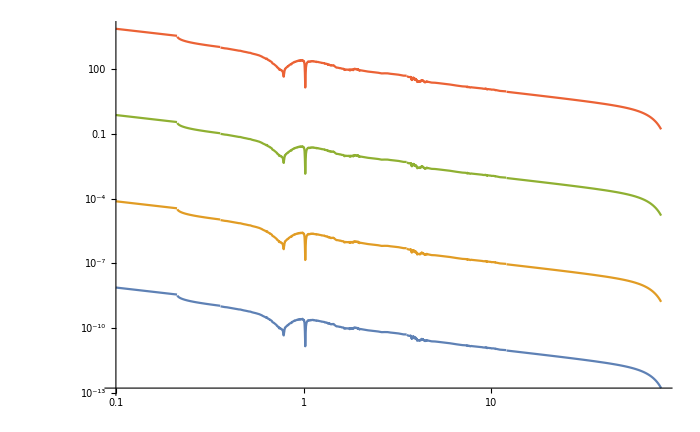

```mathematica
LogLogPlot[{ZdDecayLengthMeters[10^(-2),m],ZdDecayLengthMeters[10^(-4),m],ZdDecayLengthMeters[10^(-6),m],ZdDecayLengthMeters[10^(-8),m]},{m,0.1,80},ImageSize->700]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["BRZdmumu_10MeVsteps.csv"]]]
```

```mathematica
ZdDecayLengthMetersTablen2 =Transpose[{Table[1000*m,{m,0.22,50,0.01}],Table[ZdDecayLengthMeters[10^(-2),m],{m,0.22,50,0.01}]}] //TableForm
```

220. | 2.46956×10^-9
230. | 2.11682×10^-9
240. | 1.90694×10^-9
250. | 1.75731×10^-9
260. | 1.64125×10^-9
270. | 1.5466×10^-9
280. | 1.46678×10^-9
290. | 1.39784×10^-9
300. | 1.33723×10^-9
310. | 1.2832×10^-9
320. | 1.2345×10^-9
330. | 1.19022×10^-9
340. | 1.14967×10^-9
350. | 1.11229×10^-9
360. | 1.01812×10^-9
370. | 9.7748×10^-10
380. | 9.37403×10^-10
390. | 9.16723×10^-10
400. | 8.8338×10^-10
410. | 8.47258×10^-10
420. | 8.26306×10^-10
430. | 7.86478×10^-10
440. | 7.65853×10^-10
450. | 7.32832×10^-10
460. | 7.22337×10^-10
470. | 6.87322×10^-10
480. | 6.5764×10^-10
490. | 6.35722×10^-10
500. | 6.14532×10^-10
510. | 5.88182×10^-10
520. | 5.77401×10^-10
530. | 5.42086×10^-10
540. | 5.19083×10^-10
550. | 5.00452×10^-10
560. | 4.80377×10^-10
570. | 4.58812×10^-10
580. | 4.38692×10^-10
590. | 4.11091×10^-10
600. | 3.86194×10^-10
610. | 3.61337×10^-10
620. | 3.43374×10^-10
630. | 3.13681×10^-10
640. | 3.09654×10^-10
650. | 2.65261×10^-10
660. | 2.45469×10^-10
670. | 2.27456×10^-10
680. | 1.94585×10^-10
690. | 1.7904×10^-10
700. | 1.60754×10^-10
710. | 1.42604×10^-10
720. | 1.2707×10^-10
730. | 1.152×10^-10
740. | 9.1161×10^-11
750. | 9.6508×10^-11
760. | 9.04596×10^-11
770. | 8.20208×10^-11
780. | 5.01367×10^-11
790. | 8.47602×10^-11
800. | 1.06058×10^-10
810. | 1.20373×10^-10
820. | 1.3232×10^-10
830. | 1.41392×10^-10
840. | 1.56234×10^-10
850. | 1.73687×10^-10
860. | 1.70206×10^-10
870. | 1.95089×10^-10
880. | 2.01974×10^-10
890. | 2.17719×10^-10
900. | 2.23041×10^-10
910. | 2.32556×10^-10
920. | 2.33179×10^-10
930. | 2.42212×10^-10
940. | 2.4698×10^-10
950. | 2.51225×10^-10
960. | 2.5074×10^-10
970. | 2.57621×10^-10
980. | 2.50538×10^-10
990. | 2.55855×10^-10
1000. | 2.30055×10^-10
1010. | 1.70749×10^-10
1020. | 1.58036×10^-11
1030. | 1.33291×10^-10
1040. | 1.9695×10^-10
1050. | 2.17964×10^-10
1060. | 2.28433×10^-10
1070. | 2.25894×10^-10
1080. | 2.27144×10^-10
1090. | 2.32438×10^-10
1100. | 2.37039×10^-10
1110. | 2.36006×10^-10
1120. | 2.35068×10^-10
1130. | 2.29162×10^-10
1140. | 2.27867×10^-10
1150. | 2.27069×10^-10
1160. | 2.21973×10^-10
1170. | 2.18774×10^-10
1180. | 2.18336×10^-10
1190. | 2.21801×10^-10
1200. | 2.14413×10^-10
1210. | 2.0896×10^-10
1220. | 2.0784×10^-10
1230. | 2.03477×10^-10
1240. | 1.99543×10^-10
1250. | 1.98133×10^-10
1260. | 1.96959×10^-10
1270. | 1.90326×10^-10
1280. | 1.8878×10^-10
1290. | 1.87697×10^-10
1300. | 1.8157×10^-10
1310. | 1.81162×10^-10
1320. | 1.76938×10^-10
1330. | 1.75671×10^-10
1340. | 1.68057×10^-10
1350. | 1.62431×10^-10
1360. | 1.61557×10^-10
1370. | 1.57388×10^-10
1380. | 1.55903×10^-10
1390. | 1.54211×10^-10
1400. | 1.46463×10^-10
1410. | 1.51884×10^-10
1420. | 1.50949×10^-10
1430. | 1.53664×10^-10
1440. | 1.53319×10^-10
1450. | 1.46742×10^-10
1460. | 1.39871×10^-10
1470. | 1.32823×10^-10
1480. | 1.26128×10^-10
1490. | 1.21792×10^-10
1500. | 1.18825×10^-10
1510. | 1.19506×10^-10
1520. | 1.18278×10^-10
1530. | 1.17023×10^-10
1540. | 1.15759×10^-10
1550. | 1.13517×10^-10
1560. | 1.12075×10^-10
1570. | 1.12794×10^-10
1580. | 1.10908×10^-10
1590. | 1.0824×10^-10
1600. | 1.06378×10^-10
1610. | 1.06936×10^-10
1620. | 1.05413×10^-10
1630. | 1.04181×10^-10
1640. | 9.6406×10^-11
1650. | 9.23611×10^-11
1660. | 9.54731×10^-11
1670. | 9.77895×10^-11
1680. | 9.6322×10^-11
1690. | 9.80078×10^-11
1700. | 9.5666×10^-11
1710. | 9.63877×10^-11
1720. | 9.56682×10^-11
1730. | 9.71424×10^-11
1740. | 9.49651×10^-11
1750. | 9.42264×10^-11
1760. | 8.96626×10^-11
1770. | 9.94249×10^-11
1780. | 9.07058×10^-11
1790. | 9.51934×10^-11
1800. | 9.41013×10^-11
1810. | 9.90245×10^-11
1820. | 9.54265×10^-11
1830. | 9.35442×10^-11
1840. | 9.21091×10^-11
1850. | 1.03929×10^-10
1860. | 1.03042×10^-10
1870. | 1.03949×10^-10
1880. | 1.01193×10^-10
1890. | 1.03628×10^-10
1900. | 9.965×10^-11
1910. | 1.02417×10^-10
1920. | 9.79503×10^-11
1930. | 9.91841×10^-11
1940. | 9.60153×10^-11
1950. | 9.27046×10^-11
1960. | 8.86762×10^-11
1970. | 9.06265×10^-11
1980. | 8.60225×10^-11
1990. | 8.83933×10^-11
2000. | 9.04183×10^-11
2010. | 8.97536×10^-11
2020. | 8.90966×10^-11
2030. | 8.8447×10^-11
2040. | 8.78048×10^-11
2050. | 8.71699×10^-11
2060. | 8.6542×10^-11
2070. | 8.59212×10^-11
2080. | 8.53074×10^-11
2090. | 8.47003×10^-11
2100. | 8.40999×10^-11
2110. | 8.35062×10^-11
2120. | 8.29189×10^-11
2130. | 8.23381×10^-11
2140. | 8.17636×10^-11
2150. | 8.11953×10^-11
2160. | 8.06331×10^-11
2170. | 8.00769×10^-11
2180. | 7.95267×10^-11
2190. | 7.89824×10^-11
2200. | 7.84438×10^-11
2210. | 7.80888×10^-11
2220. | 7.7737×10^-11
2230. | 7.73883×10^-11
2240. | 7.70428×10^-11
2250. | 7.67003×10^-11
2260. | 7.63609×10^-11
2270. | 7.60245×10^-11
2280. | 7.5691×10^-11
2290. | 7.53604×10^-11
2300. | 7.50327×10^-11
2310. | 7.47078×10^-11
2320. | 7.43857×10^-11
2330. | 7.40664×10^-11
2340. | 7.37499×10^-11
2350. | 7.3436×10^-11
2360. | 7.31248×10^-11
2370. | 7.28162×10^-11
2380. | 7.25102×10^-11
2390. | 7.22068×10^-11
2400. | 7.19059×10^-11
2410. | 7.15911×10^-11
2420. | 7.1279×10^-11
2430. | 7.09694×10^-11
2440. | 7.06624×10^-11
2450. | 7.03579×10^-11
2460. | 7.00558×10^-11
2470. | 6.97563×10^-11
2480. | 6.94591×10^-11
2490. | 6.91644×10^-11
2500. | 6.8872×10^-11
2510. | 6.84106×10^-11
2520. | 6.79538×10^-11
2530. | 6.75017×10^-11
2540. | 6.70541×10^-11
2550. | 6.6611×10^-11
2560. | 6.61723×10^-11
2570. | 6.5738×10^-11
2580. | 6.5308×10^-11
2590. | 6.48822×10^-11
2600. | 6.44607×10^-11
2610. | 6.45141×10^-11
2620. | 6.45699×10^-11
2630. | 6.46281×10^-11
2640. | 6.46887×10^-11
2650. | 6.47518×10^-11
2660. | 6.48173×10^-11
2670. | 6.48854×10^-11
2680. | 6.49559×10^-11
2690. | 6.50289×10^-11
2700. | 6.51044×10^-11
2710. | 6.50608×10^-11
2720. | 6.50187×10^-11
2730. | 6.49782×10^-11
2740. | 6.49391×10^-11
2750. | 6.49016×10^-11
2760. | 6.48655×10^-11
2770. | 6.48309×10^-11
2780. | 6.47978×10^-11
2790. | 6.47662×10^-11
2800. | 6.4736×10^-11
2810. | 6.44284×10^-11
2820. | 6.41231×10^-11
2830. | 6.38201×10^-11
2840. | 6.35195×10^-11
2850. | 6.32211×10^-11
2860. | 6.29251×10^-11
2870. | 6.26312×10^-11
2880. | 6.23396×10^-11
2890. | 6.20502×10^-11
2900. | 6.17629×10^-11
2910. | 6.15652×10^-11
2920. | 6.13689×10^-11
2930. | 6.11739×10^-11
2940. | 6.09803×10^-11
2950. | 6.07879×10^-11
2960. | 6.05969×10^-11
2970. | 6.04072×10^-11
2980. | 6.02188×10^-11
2990. | 6.00316×10^-11
3000. | 5.98457×10^-11
3010. | 5.96468×10^-11
3020. | 5.94493×10^-11
3030. | 5.9253×10^-11
3040. | 5.90581×10^-11
3050. | 5.88644×10^-11
3060. | 5.8672×10^-11
3070. | 5.84809×10^-11
3080. | 5.8291×10^-11
3090. | 5.81023×10^-11
3100. | 5.79149×10^-11
3110. | 5.77286×10^-11
3120. | 5.75436×10^-11
3130. | 5.73597×10^-11
3140. | 5.7177×10^-11
3150. | 5.69955×10^-11
3160. | 5.68151×10^-11
3170. | 5.66358×10^-11
3180. | 5.64577×10^-11
3190. | 5.62807×10^-11
3200. | 5.61048×10^-11
3210. | 5.58173×10^-11
3220. | 5.5532×10^-11
3230. | 5.52489×10^-11
3240. | 5.49681×10^-11
3250. | 5.46894×10^-11
3260. | 5.44128×10^-11
3270. | 5.41384×10^-11
3280. | 5.38661×10^-11
3290. | 5.35959×10^-11
3300. | 5.33277×10^-11
3310. | 5.30615×10^-11
3320. | 5.27974×10^-11
3330. | 5.25353×10^-11
3340. | 5.22751×10^-11
3350. | 5.20169×10^-11
3360. | 5.17606×10^-11
3370. | 5.15063×10^-11
3380. | 5.12538×10^-11
3390. | 5.10032×10^-11
3400. | 5.07545×10^-11
3410. | 5.07214×10^-11
3420. | 5.06891×10^-11
3430. | 5.06575×10^-11
3440. | 5.06266×10^-11
3450. | 5.05964×10^-11
3460. | 5.05669×10^-11
3470. | 5.05382×10^-11
3480. | 5.05101×10^-11
3490. | 5.04827×10^-11
3500. | 5.04561×10^-11
3510. | 5.04301×10^-11
3520. | 5.04049×10^-11
3530. | 5.03803×10^-11
3540. | 5.03565×10^-11
3550. | 4.90316×10^-11
3560. | 4.786×10^-11
3570. | 4.68524×10^-11
3580. | 4.59398×10^-11
3590. | 4.50941×10^-11
3600. | 4.44198×10^-11
3610. | 4.42528×10^-11
3620. | 4.41022×10^-11
3630. | 4.39649×10^-11
3640. | 4.3839×10^-11
3650. | 4.37229×10^-11
3660. | 4.36152×10^-11
3670. | 4.3515×10^-11
3680. | 4.37393×10^-11
3690. | 4.39736×10^-11
3700. | 4.38925×10^-11
3710. | 4.25719×10^-11
3720. | 4.28992×10^-11
3730. | 4.26867×10^-11
3740. | 3.83127×10^-11
3750. | 3.74497×10^-11
3760. | 3.82421×10^-11
3770. | 3.07955×10^-11
3780. | 3.19443×10^-11
3790. | 3.65382×10^-11
3800. | 3.6773×10^-11
3810. | 3.85624×10^-11
3820. | 3.77779×10^-11
3830. | 3.77705×10^-11
3840. | 4.09916×10^-11
3850. | 3.80877×10^-11
3860. | 3.99637×10^-11
3870. | 3.54893×10^-11
3880. | 3.80237×10^-11
3890. | 3.75004×10^-11
3900. | 3.65256×10^-11
3910. | 3.56957×10^-11
3920. | 3.49×10^-11
3930. | 3.32129×10^-11
3940. | 3.45255×10^-11
3950. | 3.37958×10^-11
3960. | 3.52322×10^-11
3970. | 3.21449×10^-11
3980. | 3.20359×10^-11
3990. | 3.32157×10^-11
4000. | 3.25337×10^-11
4010. | 2.94834×10^-11
4020. | 2.6527×10^-11
4030. | 2.5896×10^-11
4040. | 2.62134×10^-11
4050. | 2.7041×10^-11
4060. | 2.54117×10^-11
4070. | 2.74299×10^-11
4080. | 2.67531×10^-11
4090. | 2.73831×10^-11
4100. | 2.73201×10^-11
4110. | 2.77932×10^-11
4120. | 2.69363×10^-11
4130. | 2.73374×10^-11
4140. | 2.7923×10^-11
4150. | 2.63115×10^-11
4160. | 2.65799×10^-11
4170. | 2.65023×10^-11
4180. | 2.61957×10^-11
4190. | 2.70605×10^-11
4200. | 2.72686×10^-11
4210. | 3.02609×10^-11
4220. | 2.88831×10^-11
4230. | 3.00344×10^-11
4240. | 2.97975×10^-11
4250. | 3.14457×10^-11
4260. | 3.1026×10^-11
4270. | 2.94447×10^-11
4280. | 3.02933×10^-11
4290. | 3.06234×10^-11
4300. | 2.99431×10^-11
4310. | 2.89954×10^-11
4320. | 3.05564×10^-11
4330. | 2.86461×10^-11
4340. | 2.84509×10^-11
4350. | 2.77391×10^-11
4360. | 2.77527×10^-11
4370. | 2.66953×10^-11
4380. | 2.74718×10^-11
4390. | 2.74859×10^-11
4400. | 2.54813×10^-11
4410. | 2.60519×10^-11
4420. | 2.64254×10^-11
4430. | 2.4913×10^-11
4440. | 2.56152×10^-11
4450. | 2.59392×10^-11
4460. | 2.58525×10^-11
4470. | 2.55105×10^-11
4480. | 2.65917×10^-11
4490. | 2.60113×10^-11
4500. | 2.6666×10^-11
4510. | 2.71147×10^-11
4520. | 2.75811×10^-11
4530. | 2.75566×10^-11
4540. | 2.75325×10^-11
4550. | 2.66054×10^-11
4560. | 2.57354×10^-11
4570. | 2.58471×10^-11
4580. | 2.59606×10^-11
4590. | 2.6076×10^-11
4600. | 2.61933×10^-11
4610. | 2.60843×10^-11
4620. | 2.59762×10^-11
4630. | 2.58688×10^-11
4640. | 2.57622×10^-11
4650. | 2.56563×10^-11
4660. | 2.55512×10^-11
4670. | 2.54468×10^-11
4680. | 2.53431×10^-11
4690. | 2.52402×10^-11
4700. | 2.5138×10^-11
4710. | 2.50364×10^-11
4720. | 2.49356×10^-11
4730. | 2.48354×10^-11
4740. | 2.4736×10^-11
4750. | 2.46372×10^-11
4760. | 2.4539×10^-11
4770. | 2.44416×10^-11
4780. | 2.43447×10^-11
4790. | 2.42485×10^-11
4800. | 2.4153×10^-11
4810. | 2.41329×10^-11
4820. | 2.4113×10^-11
4830. | 2.40934×10^-11
4840. | 2.40739×10^-11
4850. | 2.40547×10^-11
4860. | 2.40357×10^-11
4870. | 2.40169×10^-11
4880. | 2.39984×10^-11
4890. | 2.398×10^-11
4900. | 2.39619×10^-11
4910. | 2.39439×10^-11
4920. | 2.39262×10^-11
4930. | 2.39087×10^-11
4940. | 2.38914×10^-11
4950. | 2.38742×10^-11
4960. | 2.38573×10^-11
4970. | 2.38406×10^-11
4980. | 2.38241×10^-11
4990. | 2.38078×10^-11
5000. | 2.37917×10^-11
5010. | 2.37458×10^-11
5020. | 2.37002×10^-11
5030. | 2.36548×10^-11
5040. | 2.36096×10^-11
5050. | 2.35646×10^-11
5060. | 2.35199×10^-11
5070. | 2.34754×10^-11
5080. | 2.34311×10^-11
5090. | 2.3387×10^-11
5100. | 2.33431×10^-11
5110. | 2.32995×10^-11
5120. | 2.3256×10^-11
5130. | 2.32128×10^-11
5140. | 2.31698×10^-11
5150. | 2.3127×10^-11
5160. | 2.30843×10^-11
5170. | 2.30419×10^-11
5180. | 2.29997×10^-11
5190. | 2.29577×10^-11
5200. | 2.29159×10^-11
5210. | 2.28688×10^-11
5220. | 2.2822×10^-11
5230. | 2.27754×10^-11
5240. | 2.2729×10^-11
5250. | 2.26828×10^-11
5260. | 2.26369×10^-11
5270. | 2.25911×10^-11
5280. | 2.25455×10^-11
5290. | 2.25002×10^-11
5300. | 2.2455×10^-11
5310. | 2.24101×10^-11
5320. | 2.23653×10^-11
5330. | 2.23207×10^-11
5340. | 2.22764×10^-11
5350. | 2.22322×10^-11
5360. | 2.21882×10^-11
5370. | 2.21444×10^-11
5380. | 2.21008×10^-11
5390. | 2.20574×10^-11
5400. | 2.20142×10^-11
5410. | 2.19711×10^-11
5420. | 2.19283×10^-11
5430. | 2.18856×10^-11
5440. | 2.18431×10^-11
5450. | 2.18008×10^-11
5460. | 2.17586×10^-11
5470. | 2.17167×10^-11
5480. | 2.16749×10^-11
5490. | 2.16333×10^-11
5500. | 2.15918×10^-11
5510. | 2.15506×10^-11
5520. | 2.15095×10^-11
5530. | 2.14686×10^-11
5540. | 2.14278×10^-11
5550. | 2.13872×10^-11
5560. | 2.13468×10^-11
5570. | 2.13066×10^-11
5580. | 2.12665×10^-11
5590. | 2.12265×10^-11
5600. | 2.11868×10^-11
5610. | 2.11472×10^-11
5620. | 2.11077×10^-11
5630. | 2.10684×10^-11
5640. | 2.10293×10^-11
5650. | 2.09903×10^-11
5660. | 2.09515×10^-11
5670. | 2.09128×10^-11
5680. | 2.08743×10^-11
5690. | 2.0836×10^-11
5700. | 2.07978×10^-11
5710. | 2.07597×10^-11
5720. | 2.07218×10^-11
5730. | 2.0684×10^-11
5740. | 2.06464×10^-11
5750. | 2.0609×10^-11
5760. | 2.05716×10^-11
5770. | 2.05345×10^-11
5780. | 2.04974×10^-11
5790. | 2.04605×10^-11
5800. | 2.04238×10^-11
5810. | 2.03872×10^-11
5820. | 2.03507×10^-11
5830. | 2.03144×10^-11
5840. | 2.02782×10^-11
5850. | 2.02421×10^-11
5860. | 2.02062×10^-11
5870. | 2.01704×10^-11
5880. | 2.01348×10^-11
5890. | 2.00993×10^-11
5900. | 2.00639×10^-11
5910. | 2.00286×10^-11
5920. | 1.99935×10^-11
5930. | 1.99585×10^-11
5940. | 1.99237×10^-11
5950. | 1.98889×10^-11
5960. | 1.98543×10^-11
5970. | 1.98198×10^-11
5980. | 1.97855×10^-11
5990. | 1.97513×10^-11
6000. | 1.97172×10^-11
6010. | 1.96721×10^-11
6020. | 1.96272×10^-11
6030. | 1.95825×10^-11
6040. | 1.9538×10^-11
6050. | 1.94936×10^-11
6060. | 1.94494×10^-11
6070. | 1.94054×10^-11
6080. | 1.93616×10^-11
6090. | 1.93179×10^-11
6100. | 1.92743×10^-11
6110. | 1.9231×10^-11
6120. | 1.91878×10^-11
6130. | 1.91448×10^-11
6140. | 1.91019×10^-11
6150. | 1.90592×10^-11
6160. | 1.90167×10^-11
6170. | 1.89743×10^-11
6180. | 1.89321×10^-11
6190. | 1.889×10^-11
6200. | 1.88481×10^-11
6210. | 1.88064×10^-11
6220. | 1.87648×10^-11
6230. | 1.87234×10^-11
6240. | 1.86821×10^-11
6250. | 1.8641×10^-11
6260. | 1.86×10^-11
6270. | 1.85592×10^-11
6280. | 1.85185×10^-11
6290. | 1.8478×10^-11
6300. | 1.84376×10^-11
6310. | 1.83974×10^-11
6320. | 1.83573×10^-11
6330. | 1.83174×10^-11
6340. | 1.82776×10^-11
6350. | 1.8238×10^-11
6360. | 1.81985×10^-11
6370. | 1.81591×10^-11
6380. | 1.81199×10^-11
6390. | 1.80808×10^-11
6400. | 1.80419×10^-11
6410. | 1.80031×10^-11
6420. | 1.79645×10^-11
6430. | 1.7926×10^-11
6440. | 1.78876×10^-11
6450. | 1.78494×10^-11
6460. | 1.78113×10^-11
6470. | 1.77733×10^-11
6480. | 1.77355×10^-11
6490. | 1.76978×10^-11
6500. | 1.76602×10^-11
6510. | 1.76276×10^-11
6520. | 1.75951×10^-11
6530. | 1.75627×10^-11
6540. | 1.75305×10^-11
6550. | 1.74983×10^-11
6560. | 1.74662×10^-11
6570. | 1.74342×10^-11
6580. | 1.74024×10^-11
6590. | 1.73706×10^-11
6600. | 1.7339×10^-11
6610. | 1.73074×10^-11
6620. | 1.7276×10^-11
6630. | 1.72446×10^-11
6640. | 1.72134×10^-11
6650. | 1.71823×10^-11
6660. | 1.71512×10^-11
6670. | 1.71203×10^-11
6680. | 1.70895×10^-11
6690. | 1.70587×10^-11
6700. | 1.70281×10^-11
6710. | 1.69976×10^-11
6720. | 1.69671×10^-11
6730. | 1.69368×10^-11
6740. | 1.69065×10^-11
6750. | 1.68764×10^-11
6760. | 1.68463×10^-11
6770. | 1.68164×10^-11
6780. | 1.67865×10^-11
6790. | 1.67568×10^-11
6800. | 1.67271×10^-11
6810. | 1.66975×10^-11
6820. | 1.6668×10^-11
6830. | 1.66386×10^-11
6840. | 1.66093×10^-11
6850. | 1.65801×10^-11
6860. | 1.6551×10^-11
6870. | 1.6522×10^-11
6880. | 1.64931×10^-11
6890. | 1.64642×10^-11
6900. | 1.64355×10^-11
6910. | 1.64068×10^-11
6920. | 1.63782×10^-11
6930. | 1.63497×10^-11
6940. | 1.63213×10^-11
6950. | 1.6293×10^-11
6960. | 1.62648×10^-11
6970. | 1.62367×10^-11
6980. | 1.62086×10^-11
6990. | 1.61807×10^-11
7000. | 1.61528×10^-11
7010. | 1.61406×10^-11
7020. | 1.61285×10^-11
7030. | 1.61164×10^-11
7040. | 1.61044×10^-11
7050. | 1.60924×10^-11
7060. | 1.60805×10^-11
7070. | 1.60686×10^-11
7080. | 1.60568×10^-11
7090. | 1.60451×10^-11
7100. | 1.60333×10^-11
7110. | 1.60217×10^-11
7120. | 1.60101×10^-11
7130. | 1.59985×10^-11
7140. | 1.5987×10^-11
7150. | 1.59755×10^-11
7160. | 1.59641×10^-11
7170. | 1.59527×10^-11
7180. | 1.59414×10^-11
7190. | 1.59302×10^-11
7200. | 1.59189×10^-11
7210. | 1.59078×10^-11
7220. | 1.58966×10^-11
7230. | 1.58856×10^-11
7240. | 1.58745×10^-11
7250. | 1.58636×10^-11
7260. | 1.58526×10^-11
7270. | 1.58418×10^-11
7280. | 1.58309×10^-11
7290. | 1.58201×10^-11
7300. | 1.58094×10^-11
7310. | 1.57178×10^-11
7320. | 1.56271×10^-11
7330. | 1.55373×10^-11
7340. | 1.54483×10^-11
7350. | 1.53601×10^-11
7360. | 1.52728×10^-11
7370. | 1.51862×10^-11
7380. | 1.51005×10^-11
7390. | 1.50156×10^-11
7400. | 1.49314×10^-11
7410. | 1.51829×10^-11
7420. | 1.54439×10^-11
7430. | 1.57147×10^-11
7440. | 1.59961×10^-11
7450. | 1.57592×10^-11
7460. | 1.55287×10^-11
7470. | 1.53042×10^-11
7480. | 1.50857×10^-11
7490. | 1.48728×10^-11
7500. | 1.46653×10^-11
7510. | 1.47141×10^-11
7520. | 1.47633×10^-11
7530. | 1.48131×10^-11
7540. | 1.48634×10^-11
7550. | 1.49143×10^-11
7560. | 1.49657×10^-11
7570. | 1.50176×10^-11
7580. | 1.50701×10^-11
7590. | 1.51231×10^-11
7600. | 1.51767×10^-11
7610. | 1.50714×10^-11
7620. | 1.49673×10^-11
7630. | 1.48645×10^-11
7640. | 1.47628×10^-11
7650. | 1.46622×10^-11
7660. | 1.45629×10^-11
7670. | 1.44647×10^-11
7680. | 1.43675×10^-11
7690. | 1.42715×10^-11
7700. | 1.41766×10^-11
7710. | 1.42299×10^-11
7720. | 1.42839×10^-11
7730. | 1.43384×10^-11
7740. | 1.43936×10^-11
7750. | 1.44494×10^-11
7760. | 1.45058×10^-11
7770. | 1.45628×10^-11
7780. | 1.46205×10^-11
7790. | 1.46789×10^-11
7800. | 1.47379×10^-11
7810. | 1.47031×10^-11
7820. | 1.46685×10^-11
7830. | 1.4634×10^-11
7840. | 1.45996×10^-11
7850. | 1.45654×10^-11
7860. | 1.45312×10^-11
7870. | 1.44972×10^-11
7880. | 1.44633×10^-11
7890. | 1.44296×10^-11
7900. | 1.43959×10^-11
7910. | 1.43753×10^-11
7920. | 1.43548×10^-11
7930. | 1.43344×10^-11
7940. | 1.4314×10^-11
7950. | 1.42936×10^-11
7960. | 1.42733×10^-11
7970. | 1.42531×10^-11
7980. | 1.42329×10^-11
7990. | 1.42128×10^-11
8000. | 1.41927×10^-11
8010. | 1.4162×10^-11
8020. | 1.41314×10^-11
8030. | 1.4101×10^-11
8040. | 1.40706×10^-11
8050. | 1.40403×10^-11
8060. | 1.40101×10^-11
8070. | 1.39801×10^-11
8080. | 1.39501×10^-11
8090. | 1.39202×10^-11
8100. | 1.38904×10^-11
8110. | 1.38918×10^-11
8120. | 1.38931×10^-11
8130. | 1.38945×10^-11
8140. | 1.3896×10^-11
8150. | 1.38975×10^-11
8160. | 1.38991×10^-11
8170. | 1.39007×10^-11
8180. | 1.39023×10^-11
8190. | 1.3904×10^-11
8200. | 1.39057×10^-11
8210. | 1.39391×10^-11
8220. | 1.39728×10^-11
8230. | 1.40068×10^-11
8240. | 1.4041×10^-11
8250. | 1.40756×10^-11
8260. | 1.41104×10^-11
8270. | 1.41456×10^-11
8280. | 1.4181×10^-11
8290. | 1.42168×10^-11
8300. | 1.42528×10^-11
8310. | 1.41844×10^-11
8320. | 1.41166×10^-11
8330. | 1.40492×10^-11
8340. | 1.39824×10^-11
8350. | 1.39161×10^-11
8360. | 1.38503×10^-11
8370. | 1.3785×10^-11
8380. | 1.37203×10^-11
8390. | 1.3656×10^-11
8400. | 1.35921×10^-11
8410. | 1.35943×10^-11
8420. | 1.35966×10^-11
8430. | 1.35988×10^-11
8440. | 1.36012×10^-11
8450. | 1.36035×10^-11
8460. | 1.36059×10^-11
8470. | 1.36084×10^-11
8480. | 1.36109×10^-11
8490. | 1.36134×10^-11
8500. | 1.3616×10^-11
8510. | 1.35749×10^-11
8520. | 1.3534×10^-11
8530. | 1.34933×10^-11
8540. | 1.34528×10^-11
8550. | 1.34125×10^-11
8560. | 1.33723×10^-11
8570. | 1.33323×10^-11
8580. | 1.32925×10^-11
8590. | 1.32529×10^-11
8600. | 1.32135×10^-11
8610. | 1.32418×10^-11
8620. | 1.32704×10^-11
8630. | 1.32992×10^-11
8640. | 1.33282×10^-11
8650. | 1.33575×10^-11
8660. | 1.3387×10^-11
8670. | 1.34167×10^-11
8680. | 1.34467×10^-11
8690. | 1.34769×10^-11
8700. | 1.35073×10^-11
8710. | 1.34728×10^-11
8720. | 1.34385×10^-11
8730. | 1.34043×10^-11
8740. | 1.33702×10^-11
8750. | 1.33362×10^-11
8760. | 1.33024×10^-11
8770. | 1.32687×10^-11
8780. | 1.32351×10^-11
8790. | 1.32016×10^-11
8800. | 1.31683×10^-11
8810. | 1.3117×10^-11
8820. | 1.30661×10^-11
8830. | 1.30154×10^-11
8840. | 1.29651×10^-11
8850. | 1.29151×10^-11
8860. | 1.28653×10^-11
8870. | 1.28159×10^-11
8880. | 1.27668×10^-11
8890. | 1.2718×10^-11
8900. | 1.26695×10^-11
8910. | 1.32277×10^-11
8920. | 1.31557×10^-11
8930. | 1.30844×10^-11
8940. | 1.30138×10^-11
8950. | 1.29438×10^-11
8960. | 1.28744×10^-11
8970. | 1.28056×10^-11
8980. | 1.27375×10^-11
8990. | 1.26699×10^-11
9000. | 1.26029×10^-11
9010. | 1.25964×10^-11
9020. | 1.25899×10^-11
9030. | 1.25835×10^-11
9040. | 1.2577×10^-11
9050. | 1.25706×10^-11
9060. | 1.25642×10^-11
9070. | 1.25578×10^-11
9080. | 1.25514×10^-11
9090. | 1.25451×10^-11
9100. | 1.25388×10^-11
9110. | 1.25363×10^-11
9120. | 1.25338×10^-11
9130. | 1.25314×10^-11
9140. | 1.2529×10^-11
9150. | 1.25266×10^-11
9160. | 1.25242×10^-11
9170. | 1.25219×10^-11
9180. | 1.25196×10^-11
9190. | 1.25173×10^-11
9200. | 1.2515×10^-11
9210. | 1.25636×10^-11
9220. | 1.26126×10^-11
9230. | 1.26622×10^-11
9240. | 1.27123×10^-11
9250. | 1.2763×10^-11
9260. | 1.28142×10^-11
9270. | 1.2866×10^-11
9280. | 1.29183×10^-11
9290. | 1.26141×10^-11
9300. | 1.23232×10^-11
9310. | 1.23536×10^-11
9320. | 1.23843×10^-11
9330. | 1.24152×10^-11
9340. | 1.24463×10^-11
9350. | 1.24777×10^-11
9360. | 1.25094×10^-11
9370. | 1.24766×10^-11
9380. | 1.2444×10^-11
9390. | 1.24115×10^-11
9400. | 1.25531×10^-11
9410. | 1.23342×10^-11
9420. | 1.216×10^-11
9430. | 1.20272×10^-11
9440. | 1.1897×10^-11
9450. | 1.17693×10^-11
9460. | 1.23572×10^-11
9470. | 1.22681×10^-11
9480. | 1.21802×10^-11
9490. | 1.20933×10^-11
9500. | 1.20076×10^-11
9510. | 1.18164×10^-11
9520. | 1.18392×10^-11
9530. | 1.18621×10^-11
9540. | 1.18851×10^-11
9550. | 1.19084×10^-11
9560. | 1.19318×10^-11
9570. | 1.19553×10^-11
9580. | 1.1979×10^-11
9590. | 1.2003×10^-11
9600. | 1.2027×10^-11
9610. | 1.202×10^-11
9620. | 1.20129×10^-11
9630. | 1.20059×10^-11
9640. | 1.19988×10^-11
9650. | 1.19918×10^-11
9660. | 1.19849×10^-11
9670. | 1.19779×10^-11
9680. | 1.1971×10^-11
9690. | 1.1964×10^-11
9700. | 1.19571×10^-11
9710. | 1.19338×10^-11
9720. | 1.19105×10^-11
9730. | 1.18872×10^-11
9740. | 1.1864×10^-11
9750. | 1.18409×10^-11
9760. | 1.18179×10^-11
9770. | 1.17949×10^-11
9780. | 1.1772×10^-11
9790. | 1.17492×10^-11
9800. | 1.17264×10^-11
9810. | 1.17305×10^-11
9820. | 1.17345×10^-11
9830. | 1.17387×10^-11
9840. | 1.17428×10^-11
9850. | 1.1747×10^-11
9860. | 1.17512×10^-11
9870. | 1.17555×10^-11
9880. | 1.17598×10^-11
9890. | 1.17641×10^-11
9900. | 1.17685×10^-11
9910. | 1.17222×10^-11
9920. | 1.16762×10^-11
9930. | 1.16305×10^-11
9940. | 1.1585×10^-11
9950. | 1.15399×10^-11
9960. | 1.14951×10^-11
9970. | 1.14505×10^-11
9980. | 1.14062×10^-11
9990. | 1.13622×10^-11
10000. | 1.13185×10^-11
10010. | 1.13411×10^-11
10020. | 1.13639×10^-11
10030. | 1.13868×10^-11
10040. | 1.14099×10^-11
10050. | 1.141×10^-11
10060. | 1.14102×10^-11
10070. | 1.14104×10^-11
10080. | 1.14105×10^-11
10090. | 1.14108×10^-11
10100. | 1.1411×10^-11
10110. | 1.14118×10^-11
10120. | 1.14127×10^-11
10130. | 1.14136×10^-11
10140. | 1.14145×10^-11
10150. | 1.14155×10^-11
10160. | 1.14164×10^-11
10170. | 1.14174×10^-11
10180. | 1.14184×10^-11
10190. | 1.14195×10^-11
10200. | 1.14205×10^-11
10210. | 1.14111×10^-11
10220. | 1.14018×10^-11
10230. | 1.13924×10^-11
10240. | 1.13831×10^-11
10250. | 1.13738×10^-11
10260. | 1.13645×10^-11
10270. | 1.13552×10^-11
10280. | 1.13459×10^-11
10290. | 1.13367×10^-11
10300. | 1.13227×10^-11
10310. | 1.13039×10^-11
10320. | 1.12851×10^-11
10330. | 1.12664×10^-11
10340. | 1.12478×10^-11
10350. | 1.12292×10^-11
10360. | 1.12106×10^-11
10370. | 1.11921×10^-11
10380. | 1.11736×10^-11
10390. | 1.11552×10^-11
10400. | 1.11369×10^-11
10410. | 1.11185×10^-11
10420. | 1.11002×10^-11
10430. | 1.1082×10^-11
10440. | 1.10068×10^-11
10450. | 1.09324×10^-11
10460. | 1.0859×10^-11
10470. | 1.07864×10^-11
10480. | 1.07146×10^-11
10490. | 1.06437×10^-11
10500. | 1.07447×10^-11
10510. | 1.08479×10^-11
10520. | 1.09532×10^-11
10530. | 1.09343×10^-11
10540. | 1.09154×10^-11
10550. | 1.08966×10^-11
10560. | 1.08778×10^-11
10570. | 1.0859×10^-11
10580. | 1.08403×10^-11
10590. | 1.08217×10^-11
10600. | 1.08031×10^-11
10610. | 1.07846×10^-11
10620. | 1.07661×10^-11
10630. | 1.07476×10^-11
10640. | 1.07292×10^-11
10650. | 1.07108×10^-11
10660. | 1.06925×10^-11
10670. | 1.06743×10^-11
10680. | 1.06561×10^-11
10690. | 1.06379×10^-11
10700. | 1.06198×10^-11
10710. | 1.06017×10^-11
10720. | 1.05837×10^-11
10730. | 1.05657×10^-11
10740. | 1.05477×10^-11
10750. | 1.05299×10^-11
10760. | 1.0512×10^-11
10770. | 1.04942×10^-11
10780. | 1.04765×10^-11
10790. | 1.04587×10^-11
10800. | 1.04411×10^-11
10810. | 1.04235×10^-11
10820. | 1.04059×10^-11
10830. | 1.03884×10^-11
10840. | 1.03709×10^-11
10850. | 1.03534×10^-11
10860. | 1.0336×10^-11
10870. | 1.03187×10^-11
10880. | 1.03014×10^-11
10890. | 1.02841×10^-11
10900. | 1.02669×10^-11
10910. | 1.02497×10^-11
10920. | 1.02326×10^-11
10930. | 1.02155×10^-11
10940. | 1.01984×10^-11
10950. | 1.01814×10^-11
10960. | 1.01645×10^-11
10970. | 1.01475×10^-11
10980. | 1.01307×10^-11
10990. | 1.01138×10^-11
11000. | 1.0097×10^-11
11010. | 1.00803×10^-11
11020. | 1.00636×10^-11
11030. | 1.00469×10^-11
11040. | 1.00303×10^-11
11050. | 1.00137×10^-11
11060. | 9.99715×10^-12
11070. | 9.98065×10^-12
11080. | 9.96419×10^-12
11090. | 9.94777×10^-12
11100. | 9.94148×10^-12
11110. | 9.9352×10^-12
11120. | 9.92894×10^-12
11130. | 9.9227×10^-12
11140. | 9.91646×10^-12
11150. | 9.91024×10^-12
11160. | 9.90403×10^-12
11170. | 9.89783×10^-12
11180. | 9.89164×10^-12
11190. | 9.88547×10^-12
11200. | 9.87931×10^-12
11210. | 9.87316×10^-12
11220. | 9.86703×10^-12
11230. | 9.86091×10^-12
11240. | 9.8548×10^-12
11250. | 9.8487×10^-12
11260. | 9.84261×10^-12
11270. | 9.83654×10^-12
11280. | 9.83048×10^-12
11290. | 9.82443×10^-12
11300. | 9.8184×10^-12
11310. | 9.81237×10^-12
11320. | 9.80636×10^-12
11330. | 9.80036×10^-12
11340. | 9.79437×10^-12
11350. | 9.7884×10^-12
11360. | 9.78243×10^-12
11370. | 9.77648×10^-12
11380. | 9.77054×10^-12
11390. | 9.76461×10^-12
11400. | 9.7587×10^-12
11410. | 9.75279×10^-12
11420. | 9.7469×10^-12
11430. | 9.74102×10^-12
11440. | 9.73515×10^-12
11450. | 9.7293×10^-12
11460. | 9.72345×10^-12
11470. | 9.71762×10^-12
11480. | 9.7118×10^-12
11490. | 9.70599×10^-12
11500. | 9.70019×10^-12
11510. | 9.6944×10^-12
11520. | 9.68863×10^-12
11530. | 9.68286×10^-12
11540. | 9.67711×10^-12
11550. | 9.67137×10^-12
11560. | 9.66564×10^-12
11570. | 9.65992×10^-12
11580. | 9.65422×10^-12
11590. | 9.64852×10^-12
11600. | 9.64284×10^-12
11610. | 9.63717×10^-12
11620. | 9.6315×10^-12
11630. | 9.62585×10^-12
11640. | 9.62022×10^-12
11650. | 9.61459×10^-12
11660. | 9.60897×10^-12
11670. | 9.60337×10^-12
11680. | 9.59777×10^-12
11690. | 9.59219×10^-12
11700. | 9.58662×10^-12
11710. | 9.58106×10^-12
11720. | 9.57551×10^-12
11730. | 9.56997×10^-12
11740. | 9.56444×10^-12
11750. | 9.55892×10^-12
11760. | 9.55342×10^-12
11770. | 9.54792×10^-12
11780. | 9.54243×10^-12
11790. | 9.53696×10^-12
11800. | 9.5315×10^-12
11810. | 9.52605×10^-12
11820. | 9.5206×10^-12
11830. | 9.51517×10^-12
11840. | 9.50975×10^-12
11850. | 9.50434×10^-12
11860. | 9.49894×10^-12
11870. | 9.49356×10^-12
11880. | 9.48818×10^-12
11890. | 9.48281×10^-12
11900. | 9.47745×10^-12
11910. | 9.47211×10^-12
11920. | 9.46677×10^-12
11930. | 9.46145×10^-12
11940. | 9.45613×10^-12
11950. | 9.45083×10^-12
11960. | 9.44553×10^-12
11970. | 9.44025×10^-12
11980. | 9.43497×10^-12
11990. | 9.42971×10^-12
12000. | 9.0875×10^-12
12010. | 9.07984×10^-12
12020. | 9.07219×10^-12
12030. | 9.06456×10^-12
12040. | 9.05693×10^-12
12050. | 9.04932×10^-12
12060. | 9.04173×10^-12
12070. | 9.03414×10^-12
12080. | 9.02657×10^-12
12090. | 9.01901×10^-12
12100. | 9.01146×10^-12
12110. | 9.00393×10^-12
12120. | 8.99641×10^-12
12130. | 8.9889×10^-12
12140. | 8.9814×10^-12
12150. | 8.97392×10^-12
12160. | 8.96644×10^-12
12170. | 8.95898×10^-12
12180. | 8.95153×10^-12
12190. | 8.9441×10^-12
12200. | 8.93668×10^-12
12210. | 8.92927×10^-12
12220. | 8.92187×10^-12
12230. | 8.91449×10^-12
12240. | 8.90712×10^-12
12250. | 8.89976×10^-12
12260. | 8.89241×10^-12
12270. | 8.88507×10^-12
12280. | 8.87775×10^-12
12290. | 8.87044×10^-12
12300. | 8.86314×10^-12
12310. | 8.85585×10^-12
12320. | 8.84857×10^-12
12330. | 8.84131×10^-12
12340. | 8.83405×10^-12
12350. | 8.82681×10^-12
12360. | 8.81958×10^-12
12370. | 8.81237×10^-12
12380. | 8.80516×10^-12
12390. | 8.79797×10^-12
12400. | 8.79078×10^-12
12410. | 8.78362×10^-12
12420. | 8.77646×10^-12
12430. | 8.76931×10^-12
12440. | 8.76218×10^-12
12450. | 8.75506×10^-12
12460. | 8.74795×10^-12
12470. | 8.74085×10^-12
12480. | 8.73376×10^-12
12490. | 8.72668×10^-12
12500. | 8.71962×10^-12
12510. | 8.71256×10^-12
12520. | 8.70552×10^-12
12530. | 8.69849×10^-12
12540. | 8.69147×10^-12
12550. | 8.68446×10^-12
12560. | 8.67746×10^-12
12570. | 8.67047×10^-12
12580. | 8.6635×10^-12
12590. | 8.65653×10^-12
12600. | 8.64958×10^-12
12610. | 8.64264×10^-12
12620. | 8.63571×10^-12
12630. | 8.62879×10^-12
12640. | 8.62188×10^-12
12650. | 8.61498×10^-12
12660. | 8.6081×10^-12
12670. | 8.60122×10^-12
12680. | 8.59436×10^-12
12690. | 8.5875×10^-12
12700. | 8.58066×10^-12
12710. | 8.57383×10^-12
12720. | 8.56701×10^-12
12730. | 8.5602×10^-12
12740. | 8.5534×10^-12
12750. | 8.54661×10^-12
12760. | 8.53983×10^-12
12770. | 8.53306×10^-12
12780. | 8.52631×10^-12
12790. | 8.51956×10^-12
12800. | 8.51282×10^-12
12810. | 8.5061×10^-12
12820. | 8.49939×10^-12
12830. | 8.49268×10^-12
12840. | 8.48599×10^-12
12850. | 8.47931×10^-12
12860. | 8.47264×10^-12
12870. | 8.46598×10^-12
12880. | 8.45932×10^-12
12890. | 8.45268×10^-12
12900. | 8.44605×10^-12
12910. | 8.43943×10^-12
12920. | 8.43282×10^-12
12930. | 8.42622×10^-12
12940. | 8.41963×10^-12
12950. | 8.41305×10^-12
12960. | 8.40649×10^-12
12970. | 8.39993×10^-12
12980. | 8.39338×10^-12
12990. | 8.38684×10^-12
13000. | 8.38031×10^-12
13010. | 8.37379×10^-12
13020. | 8.36727×10^-12
13030. | 8.36077×10^-12
13040. | 8.35428×10^-12
13050. | 8.34779×10^-12
13060. | 8.34132×10^-12
13070. | 8.33485×10^-12
13080. | 8.3284×10^-12
13090. | 8.32196×10^-12
13100. | 8.31552×10^-12
13110. | 8.3091×10^-12
13120. | 8.30268×10^-12
13130. | 8.29628×10^-12
13140. | 8.28988×10^-12
13150. | 8.2835×10^-12
13160. | 8.27712×10^-12
13170. | 8.27075×10^-12
13180. | 8.2644×10^-12
13190. | 8.25805×10^-12
13200. | 8.25171×10^-12
13210. | 8.24539×10^-12
13220. | 8.23907×10^-12
13230. | 8.23276×10^-12
13240. | 8.22646×10^-12
13250. | 8.22018×10^-12
13260. | 8.2139×10^-12
13270. | 8.20763×10^-12
13280. | 8.20137×10^-12
13290. | 8.19512×10^-12
13300. | 8.18887×10^-12
13310. | 8.18264×10^-12
13320. | 8.17642×10^-12
13330. | 8.17021×10^-12
13340. | 8.164×10^-12
13350. | 8.15781×10^-12
13360. | 8.15162×10^-12
13370. | 8.14545×10^-12
13380. | 8.13928×10^-12
13390. | 8.13312×10^-12
13400. | 8.12697×10^-12
13410. | 8.12083×10^-12
13420. | 8.1147×10^-12
13430. | 8.10858×10^-12
13440. | 8.10247×10^-12
13450. | 8.09637×10^-12
13460. | 8.09028×10^-12
13470. | 8.08419×10^-12
13480. | 8.07812×10^-12
13490. | 8.07205×10^-12
13500. | 8.06599×10^-12
13510. | 8.05995×10^-12
13520. | 8.05391×10^-12
13530. | 8.04788×10^-12
13540. | 8.04185×10^-12
13550. | 8.03584×10^-12
13560. | 8.02984×10^-12
13570. | 8.02384×10^-12
13580. | 8.01786×10^-12
13590. | 8.01188×10^-12
13600. | 8.00591×10^-12
13610. | 7.99995×10^-12
13620. | 7.994×10^-12
13630. | 7.98806×10^-12
13640. | 7.98212×10^-12
13650. | 7.9762×10^-12
13660. | 7.97028×10^-12
13670. | 7.96438×10^-12
13680. | 7.95848×10^-12
13690. | 7.95259×10^-12
13700. | 7.94671×10^-12
13710. | 7.94083×10^-12
13720. | 7.93497×10^-12
13730. | 7.92911×10^-12
13740. | 7.92327×10^-12
13750. | 7.91743×10^-12
13760. | 7.9116×10^-12
13770. | 7.90577×10^-12
13780. | 7.89996×10^-12
13790. | 7.89416×10^-12
13800. | 7.88836×10^-12
13810. | 7.88257×10^-12
13820. | 7.87679×10^-12
13830. | 7.87102×10^-12
13840. | 7.86526×10^-12
13850. | 7.8595×10^-12
13860. | 7.85376×10^-12
13870. | 7.84802×10^-12
13880. | 7.84229×10^-12
13890. | 7.83657×10^-12
13900. | 7.83085×10^-12
13910. | 7.82515×10^-12
13920. | 7.81945×10^-12
13930. | 7.81376×10^-12
13940. | 7.80808×10^-12
13950. | 7.80241×10^-12
13960. | 7.79674×10^-12
13970. | 7.79109×10^-12
13980. | 7.78544×10^-12
13990. | 7.7798×10^-12
14000. | 7.77417×10^-12
14010. | 7.76854×10^-12
14020. | 7.76292×10^-12
14030. | 7.7573×10^-12
14040. | 7.7517×10^-12
14050. | 7.7461×10^-12
14060. | 7.74051×10^-12
14070. | 7.73493×10^-12
14080. | 7.72936×10^-12
14090. | 7.72379×10^-12
14100. | 7.71824×10^-12
14110. | 7.71269×10^-12
14120. | 7.70715×10^-12
14130. | 7.70161×10^-12
14140. | 7.69609×10^-12
14150. | 7.69057×10^-12
14160. | 7.68506×10^-12
14170. | 7.67956×10^-12
14180. | 7.67406×10^-12
14190. | 7.66857×10^-12
14200. | 7.66309×10^-12
14210. | 7.65762×10^-12
14220. | 7.65216×10^-12
14230. | 7.6467×10^-12
14240. | 7.64125×10^-12
14250. | 7.63581×10^-12
14260. | 7.63038×10^-12
14270. | 7.62495×10^-12
14280. | 7.61953×10^-12
14290. | 7.61412×10^-12
14300. | 7.60872×10^-12
14310. | 7.60332×10^-12
14320. | 7.59794×10^-12
14330. | 7.59255×10^-12
14340. | 7.58718×10^-12
14350. | 7.58182×10^-12
14360. | 7.57646×10^-12
14370. | 7.57111×10^-12
14380. | 7.56576×10^-12
14390. | 7.56043×10^-12
14400. | 7.5551×10^-12
14410. | 7.54978×10^-12
14420. | 7.54446×10^-12
14430. | 7.53916×10^-12
14440. | 7.53386×10^-12
14450. | 7.52856×10^-12
14460. | 7.52328×10^-12
14470. | 7.518×10^-12
14480. | 7.51273×10^-12
14490. | 7.50747×10^-12
14500. | 7.50221×10^-12
14510. | 7.49696×10^-12
14520. | 7.49172×10^-12
14530. | 7.48649×10^-12
14540. | 7.48126×10^-12
14550. | 7.47604×10^-12
14560. | 7.47083×10^-12
14570. | 7.46562×10^-12
14580. | 7.46042×10^-12
14590. | 7.45523×10^-12
14600. | 7.45005×10^-12
14610. | 7.44487×10^-12
14620. | 7.4397×10^-12
14630. | 7.43454×10^-12
14640. | 7.42938×10^-12
14650. | 7.42423×10^-12
14660. | 7.41909×10^-12
14670. | 7.41395×10^-12
14680. | 7.40883×10^-12
14690. | 7.4037×10^-12
14700. | 7.39859×10^-12
14710. | 7.39348×10^-12
14720. | 7.38838×10^-12
14730. | 7.38329×10^-12
14740. | 7.3782×10^-12
14750. | 7.37312×10^-12
14760. | 7.36805×10^-12
14770. | 7.36298×10^-12
14780. | 7.35792×10^-12
14790. | 7.35287×10^-12
14800. | 7.34782×10^-12
14810. | 7.34278×10^-12
14820. | 7.33775×10^-12
14830. | 7.33273×10^-12
14840. | 7.32771×10^-12
14850. | 7.32269×10^-12
14860. | 7.31769×10^-12
14870. | 7.31269×10^-12
14880. | 7.3077×10^-12
14890. | 7.30271×10^-12
14900. | 7.29773×10^-12
14910. | 7.29276×10^-12
14920. | 7.28779×10^-12
14930. | 7.28283×10^-12
14940. | 7.27788×10^-12
14950. | 7.27294×10^-12
14960. | 7.268×10^-12
14970. | 7.26307×10^-12
14980. | 7.25814×10^-12
14990. | 7.25322×10^-12
15000. | 7.24831×10^-12
15010. | 7.2434×10^-12
15020. | 7.23849×10^-12
15030. | 7.23359×10^-12
15040. | 7.2287×10^-12
15050. | 7.22382×10^-12
15060. | 7.21894×10^-12
15070. | 7.21407×10^-12
15080. | 7.2092×10^-12
15090. | 7.20435×10^-12
15100. | 7.19949×10^-12
15110. | 7.19465×10^-12
15120. | 7.18981×10^-12
15130. | 7.18497×10^-12
15140. | 7.18015×10^-12
15150. | 7.17533×10^-12
15160. | 7.17051×10^-12
15170. | 7.16571×10^-12
15180. | 7.1609×10^-12
15190. | 7.15611×10^-12
15200. | 7.15132×10^-12
15210. | 7.14654×10^-12
15220. | 7.14176×10^-12
15230. | 7.13699×10^-12
15240. | 7.13222×10^-12
15250. | 7.12747×10^-12
15260. | 7.12271×10^-12
15270. | 7.11797×10^-12
15280. | 7.11323×10^-12
15290. | 7.1085×10^-12
15300. | 7.10377×10^-12
15310. | 7.09905×10^-12
15320. | 7.09433×10^-12
15330. | 7.08962×10^-12
15340. | 7.08492×10^-12
15350. | 7.08022×10^-12
15360. | 7.07553×10^-12
15370. | 7.07085×10^-12
15380. | 7.06617×10^-12
15390. | 7.0615×10^-12
15400. | 7.05683×10^-12
15410. | 7.05217×10^-12
15420. | 7.04752×10^-12
15430. | 7.04287×10^-12
15440. | 7.03822×10^-12
15450. | 7.03359×10^-12
15460. | 7.02896×10^-12
15470. | 7.02433×10^-12
15480. | 7.01971×10^-12
15490. | 7.0151×10^-12
15500. | 7.01049×10^-12
15510. | 7.00589×10^-12
15520. | 7.00129×10^-12
15530. | 6.9967×10^-12
15540. | 6.99212×10^-12
15550. | 6.98754×10^-12
15560. | 6.98297×10^-12
15570. | 6.97841×10^-12
15580. | 6.97385×10^-12
15590. | 6.96929×10^-12
15600. | 6.96474×10^-12
15610. | 6.9602×10^-12
15620. | 6.95566×10^-12
15630. | 6.95113×10^-12
15640. | 6.9466×10^-12
15650. | 6.94208×10^-12
15660. | 6.93757×10^-12
15670. | 6.93306×10^-12
15680. | 6.92856×10^-12
15690. | 6.92406×10^-12
15700. | 6.91957×10^-12
15710. | 6.91508×10^-12
15720. | 6.9106×10^-12
15730. | 6.90612×10^-12
15740. | 6.90166×10^-12
15750. | 6.89719×10^-12
15760. | 6.89273×10^-12
15770. | 6.88828×10^-12
15780. | 6.88384×10^-12
15790. | 6.8794×10^-12
15800. | 6.87496×10^-12
15810. | 6.87053×10^-12
15820. | 6.8661×10^-12
15830. | 6.86168×10^-12
15840. | 6.85727×10^-12
15850. | 6.85286×10^-12
15860. | 6.84846×10^-12
15870. | 6.84406×10^-12
15880. | 6.83967×10^-12
15890. | 6.83528×10^-12
15900. | 6.8309×10^-12
15910. | 6.82653×10^-12
15920. | 6.82216×10^-12
15930. | 6.81779×10^-12
15940. | 6.81344×10^-12
15950. | 6.80908×10^-12
15960. | 6.80473×10^-12
15970. | 6.80039×10^-12
15980. | 6.79605×10^-12
15990. | 6.79172×10^-12
16000. | 6.7874×10^-12
16010. | 6.78307×10^-12
16020. | 6.77875×10^-12
16030. | 6.77444×10^-12
16040. | 6.77013×10^-12
16050. | 6.76583×10^-12
16060. | 6.76153×10^-12
16070. | 6.75724×10^-12
16080. | 6.75295×10^-12
16090. | 6.74867×10^-12
16100. | 6.74439×10^-12
16110. | 6.74012×10^-12
16120. | 6.73585×10^-12
16130. | 6.73159×10^-12
16140. | 6.72734×10^-12
16150. | 6.72309×10^-12
16160. | 6.71884×10^-12
16170. | 6.7146×10^-12
16180. | 6.71037×10^-12
16190. | 6.70614×10^-12
16200. | 6.70191×10^-12
16210. | 6.69769×10^-12
16220. | 6.69348×10^-12
16230. | 6.68927×10^-12
16240. | 6.68507×10^-12
16250. | 6.68087×10^-12
16260. | 6.67667×10^-12
16270. | 6.67248×10^-12
16280. | 6.6683×10^-12
16290. | 6.66412×10^-12
16300. | 6.65995×10^-12
16310. | 6.65578×10^-12
16320. | 6.65162×10^-12
16330. | 6.64746×10^-12
16340. | 6.6433×10^-12
16350. | 6.63916×10^-12
16360. | 6.63501×10^-12
16370. | 6.63087×10^-12
16380. | 6.62674×10^-12
16390. | 6.62261×10^-12
16400. | 6.61849×10^-12
16410. | 6.61437×10^-12
16420. | 6.61026×10^-12
16430. | 6.60615×10^-12
16440. | 6.60204×10^-12
16450. | 6.59794×10^-12
16460. | 6.59385×10^-12
16470. | 6.58976×10^-12
16480. | 6.58568×10^-12
16490. | 6.5816×10^-12
16500. | 6.57752×10^-12
16510. | 6.57345×10^-12
16520. | 6.56939×10^-12
16530. | 6.56533×10^-12
16540. | 6.56127×10^-12
16550. | 6.55722×10^-12
16560. | 6.55318×10^-12
16570. | 6.54914×10^-12
16580. | 6.5451×10^-12
16590. | 6.54107×10^-12
16600. | 6.53705×10^-12
16610. | 6.53303×10^-12
16620. | 6.52901×10^-12
16630. | 6.525×10^-12
16640. | 6.52099×10^-12
16650. | 6.51699×10^-12
16660. | 6.51299×10^-12
16670. | 6.50899×10^-12
16680. | 6.50501×10^-12
16690. | 6.50102×10^-12
16700. | 6.49704×10^-12
16710. | 6.49307×10^-12
16720. | 6.4891×10^-12
16730. | 6.48514×10^-12
16740. | 6.48118×10^-12
16750. | 6.47722×10^-12
16760. | 6.47327×10^-12
16770. | 6.46932×10^-12
16780. | 6.46538×10^-12
16790. | 6.46145×10^-12
16800. | 6.45751×10^-12
16810. | 6.45359×10^-12
16820. | 6.44966×10^-12
16830. | 6.44574×10^-12
16840. | 6.44183×10^-12
16850. | 6.43792×10^-12
16860. | 6.43401×10^-12
16870. | 6.43011×10^-12
16880. | 6.42622×10^-12
16890. | 6.42233×10^-12
16900. | 6.41844×10^-12
16910. | 6.41456×10^-12
16920. | 6.41068×10^-12
16930. | 6.40681×10^-12
16940. | 6.40294×10^-12
16950. | 6.39907×10^-12
16960. | 6.39521×10^-12
16970. | 6.39136×10^-12
16980. | 6.38751×10^-12
16990. | 6.38366×10^-12
17000. | 6.37982×10^-12
17010. | 6.37598×10^-12
17020. | 6.37215×10^-12
17030. | 6.36832×10^-12
17040. | 6.36449×10^-12
17050. | 6.36067×10^-12
17060. | 6.35685×10^-12
17070. | 6.35304×10^-12
17080. | 6.34923×10^-12
17090. | 6.34542×10^-12
17100. | 6.34162×10^-12
17110. | 6.33783×10^-12
17120. | 6.33404×10^-12
17130. | 6.33025×10^-12
17140. | 6.32647×10^-12
17150. | 6.32269×10^-12
17160. | 6.31892×10^-12
17170. | 6.31515×10^-12
17180. | 6.31138×10^-12
17190. | 6.30762×10^-12
17200. | 6.30387×10^-12
17210. | 6.30011×10^-12
17220. | 6.29636×10^-12
17230. | 6.29262×10^-12
17240. | 6.28888×10^-12
17250. | 6.28514×10^-12
17260. | 6.28141×10^-12
17270. | 6.27769×10^-12
17280. | 6.27396×10^-12
17290. | 6.27024×10^-12
17300. | 6.26653×10^-12
17310. | 6.26282×10^-12
17320. | 6.25911×10^-12
17330. | 6.25541×10^-12
17340. | 6.25172×10^-12
17350. | 6.24802×10^-12
17360. | 6.24434×10^-12
17370. | 6.24065×10^-12
17380. | 6.23697×10^-12
17390. | 6.23329×10^-12
17400. | 6.22962×10^-12
17410. | 6.22595×10^-12
17420. | 6.22229×10^-12
17430. | 6.21863×10^-12
17440. | 6.21497×10^-12
17450. | 6.21132×10^-12
17460. | 6.20767×10^-12
17470. | 6.20403×10^-12
17480. | 6.20039×10^-12
17490. | 6.19675×10^-12
17500. | 6.19312×10^-12
17510. | 6.1895×10^-12
17520. | 6.18587×10^-12
17530. | 6.18225×10^-12
17540. | 6.17864×10^-12
17550. | 6.17503×10^-12
17560. | 6.17142×10^-12
17570. | 6.16782×10^-12
17580. | 6.16422×10^-12
17590. | 6.16063×10^-12
17600. | 6.15704×10^-12
17610. | 6.15345×10^-12
17620. | 6.14987×10^-12
17630. | 6.14629×10^-12
17640. | 6.14271×10^-12
17650. | 6.13914×10^-12
17660. | 6.13557×10^-12
17670. | 6.13201×10^-12
17680. | 6.12845×10^-12
17690. | 6.1249×10^-12
17700. | 6.12134×10^-12
17710. | 6.1178×10^-12
17720. | 6.11425×10^-12
17730. | 6.11071×10^-12
17740. | 6.10718×10^-12
17750. | 6.10365×10^-12
17760. | 6.10012×10^-12
17770. | 6.0966×10^-12
17780. | 6.09308×10^-12
17790. | 6.08956×10^-12
17800. | 6.08605×10^-12
17810. | 6.08254×10^-12
17820. | 6.07904×10^-12
17830. | 6.07554×10^-12
17840. | 6.07204×10^-12
17850. | 6.06855×10^-12
17860. | 6.06506×10^-12
17870. | 6.06157×10^-12
17880. | 6.05809×10^-12
17890. | 6.05461×10^-12
17900. | 6.05114×10^-12
17910. | 6.04767×10^-12
17920. | 6.0442×10^-12
17930. | 6.04074×10^-12
17940. | 6.03728×10^-12
17950. | 6.03383×10^-12
17960. | 6.03037×10^-12
17970. | 6.02693×10^-12
17980. | 6.02348×10^-12
17990. | 6.02005×10^-12
18000. | 6.01661×10^-12
18010. | 6.01318×10^-12
18020. | 6.00974×10^-12
18030. | 6.00632×10^-12
18040. | 6.00289×10^-12
18050. | 5.99947×10^-12
18060. | 5.99606×10^-12
18070. | 5.99265×10^-12
18080. | 5.98924×10^-12
18090. | 5.98583×10^-12
18100. | 5.98243×10^-12
18110. | 5.97904×10^-12
18120. | 5.97564×10^-12
18130. | 5.97225×10^-12
18140. | 5.96887×10^-12
18150. | 5.96548×10^-12
18160. | 5.96211×10^-12
18170. | 5.95873×10^-12
18180. | 5.95536×10^-12
18190. | 5.95199×10^-12
18200. | 5.94863×10^-12
18210. | 5.94527×10^-12
18220. | 5.94191×10^-12
18230. | 5.93856×10^-12
18240. | 5.93521×10^-12
18250. | 5.93186×10^-12
18260. | 5.92852×10^-12
18270. | 5.92518×10^-12
18280. | 5.92184×10^-12
18290. | 5.91851×10^-12
18300. | 5.91518×10^-12
18310. | 5.91186×10^-12
18320. | 5.90853×10^-12
18330. | 5.90522×10^-12
18340. | 5.9019×10^-12
18350. | 5.89859×10^-12
18360. | 5.89529×10^-12
18370. | 5.89198×10^-12
18380. | 5.88868×10^-12
18390. | 5.88539×10^-12
18400. | 5.88209×10^-12
18410. | 5.8788×10^-12
18420. | 5.87552×10^-12
18430. | 5.87223×10^-12
18440. | 5.86895×10^-12
18450. | 5.86568×10^-12
18460. | 5.86241×10^-12
18470. | 5.85914×10^-12
18480. | 5.85587×10^-12
18490. | 5.85261×10^-12
18500. | 5.84935×10^-12
18510. | 5.8461×10^-12
18520. | 5.84284×10^-12
18530. | 5.8396×10^-12
18540. | 5.83635×10^-12
18550. | 5.83311×10^-12
18560. | 5.82987×10^-12
18570. | 5.82664×10^-12
18580. | 5.82341×10^-12
18590. | 5.82018×10^-12
18600. | 5.81696×10^-12
18610. | 5.81374×10^-12
18620. | 5.81052×10^-12
18630. | 5.8073×10^-12
18640. | 5.80409×10^-12
18650. | 5.80088×10^-12
18660. | 5.79768×10^-12
18670. | 5.79448×10^-12
18680. | 5.79128×10^-12
18690. | 5.78809×10^-12
18700. | 5.7849×10^-12
18710. | 5.78171×10^-12
18720. | 5.77852×10^-12
18730. | 5.77534×10^-12
18740. | 5.77217×10^-12
18750. | 5.76899×10^-12
18760. | 5.76582×10^-12
18770. | 5.76266×10^-12
18780. | 5.75949×10^-12
18790. | 5.75633×10^-12
18800. | 5.75317×10^-12
18810. | 5.75002×10^-12
18820. | 5.74687×10^-12
18830. | 5.74372×10^-12
18840. | 5.74057×10^-12
18850. | 5.73743×10^-12
18860. | 5.73429×10^-12
18870. | 5.73116×10^-12
18880. | 5.72803×10^-12
18890. | 5.7249×10^-12
18900. | 5.72177×10^-12
18910. | 5.71865×10^-12
18920. | 5.71553×10^-12
18930. | 5.71242×10^-12
18940. | 5.7093×10^-12
18950. | 5.7062×10^-12
18960. | 5.70309×10^-12
18970. | 5.69999×10^-12
18980. | 5.69689×10^-12
18990. | 5.69379×10^-12
19000. | 5.6907×10^-12
19010. | 5.68761×10^-12
19020. | 5.68452×10^-12
19030. | 5.68143×10^-12
19040. | 5.67835×10^-12
19050. | 5.67527×10^-12
19060. | 5.6722×10^-12
19070. | 5.66912×10^-12
19080. | 5.66605×10^-12
19090. | 5.66299×10^-12
19100. | 5.65992×10^-12
19110. | 5.65686×10^-12
19120. | 5.65381×10^-12
19130. | 5.65075×10^-12
19140. | 5.6477×10^-12
19150. | 5.64466×10^-12
19160. | 5.64161×10^-12
19170. | 5.63857×10^-12
19180. | 5.63553×10^-12
19190. | 5.6325×10^-12
19200. | 5.62947×10^-12
19210. | 5.62644×10^-12
19220. | 5.62341×10^-12
19230. | 5.62039×10^-12
19240. | 5.61737×10^-12
19250. | 5.61435×10^-12
19260. | 5.61134×10^-12
19270. | 5.60833×10^-12
19280. | 5.60532×10^-12
19290. | 5.60231×10^-12
19300. | 5.59931×10^-12
19310. | 5.59631×10^-12
19320. | 5.59332×10^-12
19330. | 5.59033×10^-12
19340. | 5.58734×10^-12
19350. | 5.58435×10^-12
19360. | 5.58137×10^-12
19370. | 5.57839×10^-12
19380. | 5.57541×10^-12
19390. | 5.57244×10^-12
19400. | 5.56947×10^-12
19410. | 5.5665×10^-12
19420. | 5.56353×10^-12
19430. | 5.56057×10^-12
19440. | 5.55761×10^-12
19450. | 5.55465×10^-12
19460. | 5.5517×10^-12
19470. | 5.54874×10^-12
19480. | 5.5458×10^-12
19490. | 5.54285×10^-12
19500. | 5.53991×10^-12
19510. | 5.53697×10^-12
19520. | 5.53403×10^-12
19530. | 5.5311×10^-12
19540. | 5.52817×10^-12
19550. | 5.52524×10^-12
19560. | 5.52232×10^-12
19570. | 5.5194×10^-12
19580. | 5.51648×10^-12
19590. | 5.51357×10^-12
19600. | 5.51065×10^-12
19610. | 5.50774×10^-12
19620. | 5.50484×10^-12
19630. | 5.50193×10^-12
19640. | 5.49903×10^-12
19650. | 5.49613×10^-12
19660. | 5.49323×10^-12
19670. | 5.49034×10^-12
19680. | 5.48745×10^-12
19690. | 5.48456×10^-12
19700. | 5.48168×10^-12
19710. | 5.4788×10^-12
19720. | 5.47592×10^-12
19730. | 5.47305×10^-12
19740. | 5.47017×10^-12
19750. | 5.4673×10^-12
19760. | 5.46444×10^-12
19770. | 5.46157×10^-12
19780. | 5.45871×10^-12
19790. | 5.45585×10^-12
19800. | 5.453×10^-12
19810. | 5.45014×10^-12
19820. | 5.44729×10^-12
19830. | 5.44444×10^-12
19840. | 5.4416×10^-12
19850. | 5.43876×10^-12
19860. | 5.43592×10^-12
19870. | 5.43308×10^-12
19880. | 5.43025×10^-12
19890. | 5.42742×10^-12
19900. | 5.42459×10^-12
19910. | 5.42176×10^-12
19920. | 5.41894×10^-12
19930. | 5.41612×10^-12
19940. | 5.4133×10^-12
19950. | 5.41049×10^-12
19960. | 5.40768×10^-12
19970. | 5.40487×10^-12
19980. | 5.40206×10^-12
19990. | 5.39926×10^-12
20000. | 5.39646×10^-12
20010. | 5.39366×10^-12
20020. | 5.39086×10^-12
20030. | 5.38807×10^-12
20040. | 5.38528×10^-12
20050. | 5.38249×10^-12
20060. | 5.3797×10^-12
20070. | 5.37692×10^-12
20080. | 5.37414×10^-12
20090. | 5.37136×10^-12
20100. | 5.36859×10^-12
20110. | 5.36582×10^-12
20120. | 5.36305×10^-12
20130. | 5.36028×10^-12
20140. | 5.35752×10^-12
20150. | 5.35475×10^-12
20160. | 5.352×10^-12
20170. | 5.34924×10^-12
20180. | 5.34649×10^-12
20190. | 5.34374×10^-12
20200. | 5.34099×10^-12
20210. | 5.33824×10^-12
20220. | 5.3355×10^-12
20230. | 5.33276×10^-12
20240. | 5.33002×10^-12
20250. | 5.32728×10^-12
20260. | 5.32455×10^-12
20270. | 5.32182×10^-12
20280. | 5.31909×10^-12
20290. | 5.31637×10^-12
20300. | 5.31365×10^-12
20310. | 5.31093×10^-12
20320. | 5.30821×10^-12
20330. | 5.3055×10^-12
20340. | 5.30278×10^-12
20350. | 5.30008×10^-12
20360. | 5.29737×10^-12
20370. | 5.29467×10^-12
20380. | 5.29196×10^-12
20390. | 5.28927×10^-12
20400. | 5.28657×10^-12
20410. | 5.28388×10^-12
20420. | 5.28118×10^-12
20430. | 5.27849×10^-12
20440. | 5.27581×10^-12
20450. | 5.27312×10^-12
20460. | 5.27044×10^-12
20470. | 5.26776×10^-12
20480. | 5.26509×10^-12
20490. | 5.26241×10^-12
20500. | 5.25974×10^-12
20510. | 5.25707×10^-12
20520. | 5.25441×10^-12
20530. | 5.25175×10^-12
20540. | 5.24909×10^-12
20550. | 5.24643×10^-12
20560. | 5.24377×10^-12
20570. | 5.24112×10^-12
20580. | 5.23847×10^-12
20590. | 5.23582×10^-12
20600. | 5.23318×10^-12
20610. | 5.23053×10^-12
20620. | 5.22789×10^-12
20630. | 5.22525×10^-12
20640. | 5.22261×10^-12
20650. | 5.21998×10^-12
20660. | 5.21735×10^-12
20670. | 5.21472×10^-12
20680. | 5.21209×10^-12
20690. | 5.20947×10^-12
20700. | 5.20685×10^-12
20710. | 5.20423×10^-12
20720. | 5.20161×10^-12
20730. | 5.199×10^-12
20740. | 5.19639×10^-12
20750. | 5.19378×10^-12
20760. | 5.19117×10^-12
20770. | 5.18857×10^-12
20780. | 5.18597×10^-12
20790. | 5.18337×10^-12
20800. | 5.18077×10^-12
20810. | 5.17818×10^-12
20820. | 5.17559×10^-12
20830. | 5.173×10^-12
20840. | 5.17041×10^-12
20850. | 5.16782×10^-12
20860. | 5.16524×10^-12
20870. | 5.16266×10^-12
20880. | 5.16008×10^-12
20890. | 5.15751×10^-12
20900. | 5.15493×10^-12
20910. | 5.15236×10^-12
20920. | 5.1498×10^-12
20930. | 5.14723×10^-12
20940. | 5.14467×10^-12
20950. | 5.14211×10^-12
20960. | 5.13955×10^-12
20970. | 5.13699×10^-12
20980. | 5.13444×10^-12
20990. | 5.13189×10^-12
21000. | 5.12934×10^-12
21010. | 5.12679×10^-12
21020. | 5.12424×10^-12
21030. | 5.1217×10^-12
21040. | 5.11916×10^-12
21050. | 5.11662×10^-12
21060. | 5.11408×10^-12
21070. | 5.11155×10^-12
21080. | 5.10902×10^-12
21090. | 5.10649×10^-12
21100. | 5.10396×10^-12
21110. | 5.10144×10^-12
21120. | 5.09891×10^-12
21130. | 5.09639×10^-12
21140. | 5.09388×10^-12
21150. | 5.09136×10^-12
21160. | 5.08885×10^-12
21170. | 5.08634×10^-12
21180. | 5.08383×10^-12
21190. | 5.08132×10^-12
21200. | 5.07882×10^-12
21210. | 5.07632×10^-12
21220. | 5.07382×10^-12
21230. | 5.07132×10^-12
21240. | 5.06882×10^-12
21250. | 5.06633×10^-12
21260. | 5.06384×10^-12
21270. | 5.06135×10^-12
21280. | 5.05887×10^-12
21290. | 5.05638×10^-12
21300. | 5.0539×10^-12
21310. | 5.05142×10^-12
21320. | 5.04894×10^-12
21330. | 5.04647×10^-12
21340. | 5.044×10^-12
21350. | 5.04153×10^-12
21360. | 5.03906×10^-12
21370. | 5.03659×10^-12
21380. | 5.03413×10^-12
21390. | 5.03167×10^-12
21400. | 5.02921×10^-12
21410. | 5.02675×10^-12
21420. | 5.0243×10^-12
21430. | 5.02185×10^-12
21440. | 5.0194×10^-12
21450. | 5.01695×10^-12
21460. | 5.0145×10^-12
21470. | 5.01206×10^-12
21480. | 5.00962×10^-12
21490. | 5.00718×10^-12
21500. | 5.00474×10^-12
21510. | 5.0023×10^-12
21520. | 4.99987×10^-12
21530. | 4.99744×10^-12
21540. | 4.99501×10^-12
21550. | 4.99259×10^-12
21560. | 4.99016×10^-12
21570. | 4.98774×10^-12
21580. | 4.98532×10^-12
21590. | 4.98291×10^-12
21600. | 4.98049×10^-12
21610. | 4.97808×10^-12
21620. | 4.97566×10^-12
21630. | 4.97326×10^-12
21640. | 4.97085×10^-12
21650. | 4.96844×10^-12
21660. | 4.96604×10^-12
21670. | 4.96364×10^-12
21680. | 4.96124×10^-12
21690. | 4.95884×10^-12
21700. | 4.95645×10^-12
21710. | 4.95406×10^-12
21720. | 4.95167×10^-12
21730. | 4.94928×10^-12
21740. | 4.9469×10^-12
21750. | 4.94451×10^-12
21760. | 4.94213×10^-12
21770. | 4.93975×10^-12
21780. | 4.93738×10^-12
21790. | 4.935×10^-12
21800. | 4.93263×10^-12
21810. | 4.93026×10^-12
21820. | 4.92789×10^-12
21830. | 4.92552×10^-12
21840. | 4.92316×10^-12
21850. | 4.92079×10^-12
21860. | 4.91843×10^-12
21870. | 4.91607×10^-12
21880. | 4.91372×10^-12
21890. | 4.91136×10^-12
21900. | 4.90901×10^-12
21910. | 4.90666×10^-12
21920. | 4.90431×10^-12
21930. | 4.90197×10^-12
21940. | 4.89962×10^-12
21950. | 4.89728×10^-12
21960. | 4.89494×10^-12
21970. | 4.8926×10^-12
21980. | 4.89027×10^-12
21990. | 4.88794×10^-12
22000. | 4.88561×10^-12
22010. | 4.88327×10^-12
22020. | 4.88095×10^-12
22030. | 4.87862×10^-12
22040. | 4.87629×10^-12
22050. | 4.87397×10^-12
22060. | 4.87165×10^-12
22070. | 4.86933×10^-12
22080. | 4.86702×10^-12
22090. | 4.8647×10^-12
22100. | 4.86239×10^-12
22110. | 4.86008×10^-12
22120. | 4.85777×10^-12
22130. | 4.85546×10^-12
22140. | 4.85316×10^-12
22150. | 4.85086×10^-12
22160. | 4.84856×10^-12
22170. | 4.84626×10^-12
22180. | 4.84396×10^-12
22190. | 4.84167×10^-12
22200. | 4.83938×10^-12
22210. | 4.83709×10^-12
22220. | 4.8348×10^-12
22230. | 4.83251×10^-12
22240. | 4.83023×10^-12
22250. | 4.82794×10^-12
22260. | 4.82566×10^-12
22270. | 4.82338×10^-12
22280. | 4.82111×10^-12
22290. | 4.81883×10^-12
22300. | 4.81656×10^-12
22310. | 4.81429×10^-12
22320. | 4.81202×10^-12
22330. | 4.80975×10^-12
22340. | 4.80749×10^-12
22350. | 4.80523×10^-12
22360. | 4.80297×10^-12
22370. | 4.80071×10^-12
22380. | 4.79845×10^-12
22390. | 4.7962×10^-12
22400. | 4.79394×10^-12
22410. | 4.79169×10^-12
22420. | 4.78944×10^-12
22430. | 4.78719×10^-12
22440. | 4.78495×10^-12
22450. | 4.7827×10^-12
22460. | 4.78046×10^-12
22470. | 4.77822×10^-12
22480. | 4.77598×10^-12
22490. | 4.77375×10^-12
22500. | 4.77151×10^-12
22510. | 4.76928×10^-12
22520. | 4.76705×10^-12
22530. | 4.76482×10^-12
22540. | 4.7626×10^-12
22550. | 4.76037×10^-12
22560. | 4.75815×10^-12
22570. | 4.75593×10^-12
22580. | 4.75371×10^-12
22590. | 4.7515×10^-12
22600. | 4.74928×10^-12
22610. | 4.74707×10^-12
22620. | 4.74486×10^-12
22630. | 4.74265×10^-12
22640. | 4.74044×10^-12
22650. | 4.73823×10^-12
22660. | 4.73603×10^-12
22670. | 4.73382×10^-12
22680. | 4.73162×10^-12
22690. | 4.72943×10^-12
22700. | 4.72723×10^-12
22710. | 4.72503×10^-12
22720. | 4.72284×10^-12
22730. | 4.72065×10^-12
22740. | 4.71846×10^-12
22750. | 4.71628×10^-12
22760. | 4.71409×10^-12
22770. | 4.71191×10^-12
22780. | 4.70973×10^-12
22790. | 4.70755×10^-12
22800. | 4.70537×10^-12
22810. | 4.70319×10^-12
22820. | 4.70102×10^-12
22830. | 4.69884×10^-12
22840. | 4.69667×10^-12
22850. | 4.6945×10^-12
22860. | 4.69234×10^-12
22870. | 4.69017×10^-12
22880. | 4.68801×10^-12
22890. | 4.68584×10^-12
22900. | 4.68368×10^-12
22910. | 4.68153×10^-12
22920. | 4.67937×10^-12
22930. | 4.67721×10^-12
22940. | 4.67506×10^-12
22950. | 4.67291×10^-12
22960. | 4.67076×10^-12
22970. | 4.66862×10^-12
22980. | 4.66647×10^-12
22990. | 4.66433×10^-12
23000. | 4.66219×10^-12
23010. | 4.66004×10^-12
23020. | 4.6579×10^-12
23030. | 4.65577×10^-12
23040. | 4.65363×10^-12
23050. | 4.6515×10^-12
23060. | 4.64936×10^-12
23070. | 4.64723×10^-12
23080. | 4.6451×10^-12
23090. | 4.64298×10^-12
23100. | 4.64085×10^-12
23110. | 4.63873×10^-12
23120. | 4.63661×10^-12
23130. | 4.63449×10^-12
23140. | 4.63237×10^-12
23150. | 4.63025×10^-12
23160. | 4.62814×10^-12
23170. | 4.62603×10^-12
23180. | 4.62392×10^-12
23190. | 4.62181×10^-12
23200. | 4.6197×10^-12
23210. | 4.61759×10^-12
23220. | 4.61549×10^-12
23230. | 4.61339×10^-12
23240. | 4.61129×10^-12
23250. | 4.60919×10^-12
23260. | 4.60709×10^-12
23270. | 4.60499×10^-12
23280. | 4.6029×10^-12
23290. | 4.60081×10^-12
23300. | 4.59872×10^-12
23310. | 4.59663×10^-12
23320. | 4.59454×10^-12
23330. | 4.59246×10^-12
23340. | 4.59037×10^-12
23350. | 4.58829×10^-12
23360. | 4.58621×10^-12
23370. | 4.58413×10^-12
23380. | 4.58206×10^-12
23390. | 4.57998×10^-12
23400. | 4.57791×10^-12
23410. | 4.57584×10^-12
23420. | 4.57377×10^-12
23430. | 4.5717×10^-12
23440. | 4.56963×10^-12
23450. | 4.56756×10^-12
23460. | 4.5655×10^-12
23470. | 4.56344×10^-12
23480. | 4.56138×10^-12
23490. | 4.55932×10^-12
23500. | 4.55726×10^-12
23510. | 4.55521×10^-12
23520. | 4.55316×10^-12
23530. | 4.5511×10^-12
23540. | 4.54905×10^-12
23550. | 4.54701×10^-12
23560. | 4.54496×10^-12
23570. | 4.54291×10^-12
23580. | 4.54087×10^-12
23590. | 4.53883×10^-12
23600. | 4.53679×10^-12
23610. | 4.53475×10^-12
23620. | 4.53271×10^-12
23630. | 4.53068×10^-12
23640. | 4.52865×10^-12
23650. | 4.52661×10^-12
23660. | 4.52458×10^-12
23670. | 4.52255×10^-12
23680. | 4.52053×10^-12
23690. | 4.5185×10^-12
23700. | 4.51648×10^-12
23710. | 4.51445×10^-12
23720. | 4.51243×10^-12
23730. | 4.51042×10^-12
23740. | 4.5084×10^-12
23750. | 4.50638×10^-12
23760. | 4.50437×10^-12
23770. | 4.50236×10^-12
23780. | 4.50035×10^-12
23790. | 4.49834×10^-12
23800. | 4.49633×10^-12
23810. | 4.49433×10^-12
23820. | 4.49232×10^-12
23830. | 4.49032×10^-12
23840. | 4.48832×10^-12
23850. | 4.48632×10^-12
23860. | 4.48432×10^-12
23870. | 4.48232×10^-12
23880. | 4.48033×10^-12
23890. | 4.47833×10^-12
23900. | 4.47634×10^-12
23910. | 4.47435×10^-12
23920. | 4.47236×10^-12
23930. | 4.47037×10^-12
23940. | 4.46839×10^-12
23950. | 4.46641×10^-12
23960. | 4.46442×10^-12
23970. | 4.46244×10^-12
23980. | 4.46047×10^-12
23990. | 4.45849×10^-12
24000. | 4.45651×10^-12
24010. | 4.45454×10^-12
24020. | 4.45256×10^-12
24030. | 4.45059×10^-12
24040. | 4.44862×10^-12
24050. | 4.44665×10^-12
24060. | 4.44468×10^-12
24070. | 4.44272×10^-12
24080. | 4.44075×10^-12
24090. | 4.43879×10^-12
24100. | 4.43683×10^-12
24110. | 4.43487×10^-12
24120. | 4.43291×10^-12
24130. | 4.43096×10^-12
24140. | 4.429×10^-12
24150. | 4.42705×10^-12
24160. | 4.4251×10^-12
24170. | 4.42315×10^-12
24180. | 4.4212×10^-12
24190. | 4.41925×10^-12
24200. | 4.41731×10^-12
24210. | 4.41536×10^-12
24220. | 4.41342×10^-12
24230. | 4.41148×10^-12
24240. | 4.40954×10^-12
24250. | 4.4076×10^-12
24260. | 4.40566×10^-12
24270. | 4.40373×10^-12
24280. | 4.40179×10^-12
24290. | 4.39986×10^-12
24300. | 4.39793×10^-12
24310. | 4.396×10^-12
24320. | 4.39407×10^-12
24330. | 4.39215×10^-12
24340. | 4.39022×10^-12
24350. | 4.3883×10^-12
24360. | 4.38638×10^-12
24370. | 4.38446×10^-12
24380. | 4.38254×10^-12
24390. | 4.38063×10^-12
24400. | 4.37871×10^-12
24410. | 4.3768×10^-12
24420. | 4.37488×10^-12
24430. | 4.37297×10^-12
24440. | 4.37106×10^-12
24450. | 4.36915×10^-12
24460. | 4.36725×10^-12
24470. | 4.36534×10^-12
24480. | 4.36344×10^-12
24490. | 4.36153×10^-12
24500. | 4.35963×10^-12
24510. | 4.35773×10^-12
24520. | 4.35584×10^-12
24530. | 4.35394×10^-12
24540. | 4.35205×10^-12
24550. | 4.35015×10^-12
24560. | 4.34826×10^-12
24570. | 4.34637×10^-12
24580. | 4.34448×10^-12
24590. | 4.34259×10^-12
24600. | 4.34071×10^-12
24610. | 4.33882×10^-12
24620. | 4.33694×10^-12
24630. | 4.33506×10^-12
24640. | 4.33318×10^-12
24650. | 4.3313×10^-12
24660. | 4.32942×10^-12
24670. | 4.32754×10^-12
24680. | 4.32567×10^-12
24690. | 4.32379×10^-12
24700. | 4.32192×10^-12
24710. | 4.32005×10^-12
24720. | 4.31818×10^-12
24730. | 4.31632×10^-12
24740. | 4.31445×10^-12
24750. | 4.31259×10^-12
24760. | 4.31072×10^-12
24770. | 4.30886×10^-12
24780. | 4.307×10^-12
24790. | 4.30514×10^-12
24800. | 4.30329×10^-12
24810. | 4.30143×10^-12
24820. | 4.29957×10^-12
24830. | 4.29772×10^-12
24840. | 4.29587×10^-12
24850. | 4.29402×10^-12
24860. | 4.29217×10^-12
24870. | 4.29032×10^-12
24880. | 4.28847×10^-12
24890. | 4.28663×10^-12
24900. | 4.28478×10^-12
24910. | 4.28294×10^-12
24920. | 4.2811×10^-12
24930. | 4.27926×10^-12
24940. | 4.27742×10^-12
24950. | 4.27559×10^-12
24960. | 4.27375×10^-12
24970. | 4.27192×10^-12
24980. | 4.27009×10^-12
24990. | 4.26826×10^-12
25000. | 4.26643×10^-12
25010. | 4.2646×10^-12
25020. | 4.26277×10^-12
25030. | 4.26094×10^-12
25040. | 4.25912×10^-12
25050. | 4.2573×10^-12
25060. | 4.25547×10^-12
25070. | 4.25365×10^-12
25080. | 4.25183×10^-12
25090. | 4.25002×10^-12
25100. | 4.2482×10^-12
25110. | 4.24638×10^-12
25120. | 4.24457×10^-12
25130. | 4.24276×10^-12
25140. | 4.24095×10^-12
25150. | 4.23914×10^-12
25160. | 4.23733×10^-12
25170. | 4.23552×10^-12
25180. | 4.23372×10^-12
25190. | 4.23192×10^-12
25200. | 4.23011×10^-12
25210. | 4.22831×10^-12
25220. | 4.22651×10^-12
25230. | 4.22471×10^-12
25240. | 4.22291×10^-12
25250. | 4.22112×10^-12
25260. | 4.21932×10^-12
25270. | 4.21753×10^-12
25280. | 4.21573×10^-12
25290. | 4.21394×10^-12
25300. | 4.21215×10^-12
25310. | 4.21037×10^-12
25320. | 4.20858×10^-12
25330. | 4.20679×10^-12
25340. | 4.20501×10^-12
25350. | 4.20323×10^-12
25360. | 4.20145×10^-12
25370. | 4.19967×10^-12
25380. | 4.19789×10^-12
25390. | 4.19611×10^-12
25400. | 4.19433×10^-12
25410. | 4.19256×10^-12
25420. | 4.19079×10^-12
25430. | 4.18901×10^-12
25440. | 4.18724×10^-12
25450. | 4.18547×10^-12
25460. | 4.1837×10^-12
25470. | 4.18193×10^-12
25480. | 4.18017×10^-12
25490. | 4.1784×10^-12
25500. | 4.17664×10^-12
25510. | 4.17488×10^-12
25520. | 4.17312×10^-12
25530. | 4.17136×10^-12
25540. | 4.1696×10^-12
25550. | 4.16784×10^-12
25560. | 4.16609×10^-12
25570. | 4.16434×10^-12
25580. | 4.16258×10^-12
25590. | 4.16083×10^-12
25600. | 4.15908×10^-12
25610. | 4.15733×10^-12
25620. | 4.15558×10^-12
25630. | 4.15384×10^-12
25640. | 4.15209×10^-12
25650. | 4.15035×10^-12
25660. | 4.1486×10^-12
25670. | 4.14686×10^-12
25680. | 4.14512×10^-12
25690. | 4.14338×10^-12
25700. | 4.14165×10^-12
25710. | 4.13991×10^-12
25720. | 4.13817×10^-12
25730. | 4.13644×10^-12
25740. | 4.13471×10^-12
25750. | 4.13298×10^-12
25760. | 4.13125×10^-12
25770. | 4.12952×10^-12
25780. | 4.12779×10^-12
25790. | 4.12607×10^-12
25800. | 4.12434×10^-12
25810. | 4.12262×10^-12
25820. | 4.1209×10^-12
25830. | 4.11917×10^-12
25840. | 4.11745×10^-12
25850. | 4.11573×10^-12
25860. | 4.11402×10^-12
25870. | 4.1123×10^-12
25880. | 4.11058×10^-12
25890. | 4.10887×10^-12
25900. | 4.10716×10^-12
25910. | 4.10545×10^-12
25920. | 4.10374×10^-12
25930. | 4.10203×10^-12
25940. | 4.10032×10^-12
25950. | 4.09862×10^-12
25960. | 4.09691×10^-12
25970. | 4.09521×10^-12
25980. | 4.0935×10^-12
25990. | 4.0918×10^-12
26000. | 4.0901×10^-12
26010. | 4.0884×10^-12
26020. | 4.08671×10^-12
26030. | 4.08501×10^-12
26040. | 4.08331×10^-12
26050. | 4.08162×10^-12
26060. | 4.07992×10^-12
26070. | 4.07823×10^-12
26080. | 4.07654×10^-12
26090. | 4.07485×10^-12
26100. | 4.07316×10^-12
26110. | 4.07147×10^-12
26120. | 4.06979×10^-12
26130. | 4.0681×10^-12
26140. | 4.06642×10^-12
26150. | 4.06474×10^-12
26160. | 4.06306×10^-12
26170. | 4.06138×10^-12
26180. | 4.0597×10^-12
26190. | 4.05802×10^-12
26200. | 4.05635×10^-12
26210. | 4.05467×10^-12
26220. | 4.05299×10^-12
26230. | 4.05132×10^-12
26240. | 4.04965×10^-12
26250. | 4.04798×10^-12
26260. | 4.04631×10^-12
26270. | 4.04464×10^-12
26280. | 4.04297×10^-12
26290. | 4.04131×10^-12
26300. | 4.03964×10^-12
26310. | 4.03798×10^-12
26320. | 4.03632×10^-12
26330. | 4.03466×10^-12
26340. | 4.033×10^-12
26350. | 4.03134×10^-12
26360. | 4.02968×10^-12
26370. | 4.02802×10^-12
26380. | 4.02637×10^-12
26390. | 4.02472×10^-12
26400. | 4.02306×10^-12
26410. | 4.02141×10^-12
26420. | 4.01976×10^-12
26430. | 4.01811×10^-12
26440. | 4.01646×10^-12
26450. | 4.01481×10^-12
26460. | 4.01317×10^-12
26470. | 4.01152×10^-12
26480. | 4.00988×10^-12
26490. | 4.00824×10^-12
26500. | 4.0066×10^-12
26510. | 4.00496×10^-12
26520. | 4.00332×10^-12
26530. | 4.00168×10^-12
26540. | 4.00004×10^-12
26550. | 3.99841×10^-12
26560. | 3.99677×10^-12
26570. | 3.99514×10^-12
26580. | 3.99351×10^-12
26590. | 3.99188×10^-12
26600. | 3.99025×10^-12
26610. | 3.98862×10^-12
26620. | 3.98699×10^-12
26630. | 3.98537×10^-12
26640. | 3.98374×10^-12
26650. | 3.98212×10^-12
26660. | 3.98049×10^-12
26670. | 3.97887×10^-12
26680. | 3.97725×10^-12
26690. | 3.97563×10^-12
26700. | 3.97401×10^-12
26710. | 3.97239×10^-12
26720. | 3.97078×10^-12
26730. | 3.96916×10^-12
26740. | 3.96755×10^-12
26750. | 3.96594×10^-12
26760. | 3.96432×10^-12
26770. | 3.96271×10^-12
26780. | 3.96111×10^-12
26790. | 3.9595×10^-12
26800. | 3.95789×10^-12
26810. | 3.95628×10^-12
26820. | 3.95468×10^-12
26830. | 3.95307×10^-12
26840. | 3.95147×10^-12
26850. | 3.94987×10^-12
26860. | 3.94827×10^-12
26870. | 3.94667×10^-12
26880. | 3.94507×10^-12
26890. | 3.94347×10^-12
26900. | 3.94188×10^-12
26910. | 3.94028×10^-12
26920. | 3.93869×10^-12
26930. | 3.93709×10^-12
26940. | 3.9355×10^-12
26950. | 3.93391×10^-12
26960. | 3.93232×10^-12
26970. | 3.93074×10^-12
26980. | 3.92915×10^-12
26990. | 3.92756×10^-12
27000. | 3.92598×10^-12
27010. | 3.92439×10^-12
27020. | 3.92281×10^-12
27030. | 3.92123×10^-12
27040. | 3.91964×10^-12
27050. | 3.91806×10^-12
27060. | 3.91648×10^-12
27070. | 3.91491×10^-12
27080. | 3.91333×10^-12
27090. | 3.91175×10^-12
27100. | 3.91018×10^-12
27110. | 3.9086×10^-12
27120. | 3.90703×10^-12
27130. | 3.90546×10^-12
27140. | 3.90389×10^-12
27150. | 3.90232×10^-12
27160. | 3.90075×10^-12
27170. | 3.89919×10^-12
27180. | 3.89762×10^-12
27190. | 3.89606×10^-12
27200. | 3.89449×10^-12
27210. | 3.89293×10^-12
27220. | 3.89137×10^-12
27230. | 3.8898×10^-12
27240. | 3.88824×10^-12
27250. | 3.88669×10^-12
27260. | 3.88513×10^-12
27270. | 3.88357×10^-12
27280. | 3.88201×10^-12
27290. | 3.88046×10^-12
27300. | 3.87891×10^-12
27310. | 3.87735×10^-12
27320. | 3.8758×10^-12
27330. | 3.87425×10^-12
27340. | 3.8727×10^-12
27350. | 3.87116×10^-12
27360. | 3.86961×10^-12
27370. | 3.86806×10^-12
27380. | 3.86652×10^-12
27390. | 3.86497×10^-12
27400. | 3.86343×10^-12
27410. | 3.86189×10^-12
27420. | 3.86035×10^-12
27430. | 3.85881×10^-12
27440. | 3.85727×10^-12
27450. | 3.85573×10^-12
27460. | 3.85419×10^-12
27470. | 3.85266×10^-12
27480. | 3.85112×10^-12
27490. | 3.84959×10^-12
27500. | 3.84805×10^-12
27510. | 3.84652×10^-12
27520. | 3.84499×10^-12
27530. | 3.84346×10^-12
27540. | 3.84193×10^-12
27550. | 3.84041×10^-12
27560. | 3.83888×10^-12
27570. | 3.83736×10^-12
27580. | 3.83583×10^-12
27590. | 3.83431×10^-12
27600. | 3.83279×10^-12
27610. | 3.83127×10^-12
27620. | 3.82974×10^-12
27630. | 3.82822×10^-12
27640. | 3.82671×10^-12
27650. | 3.82519×10^-12
27660. | 3.82367×10^-12
27670. | 3.82216×10^-12
27680. | 3.82064×10^-12
27690. | 3.81913×10^-12
27700. | 3.81761×10^-12
27710. | 3.8161×10^-12
27720. | 3.81459×10^-12
27730. | 3.81308×10^-12
27740. | 3.81158×10^-12
27750. | 3.81007×10^-12
27760. | 3.80856×10^-12
27770. | 3.80706×10^-12
27780. | 3.80555×10^-12
27790. | 3.80405×10^-12
27800. | 3.80255×10^-12
27810. | 3.80105×10^-12
27820. | 3.79955×10^-12
27830. | 3.79805×10^-12
27840. | 3.79655×10^-12
27850. | 3.79505×10^-12
27860. | 3.79355×10^-12
27870. | 3.79206×10^-12
27880. | 3.79056×10^-12
27890. | 3.78907×10^-12
27900. | 3.78758×10^-12
27910. | 3.78609×10^-12
27920. | 3.7846×10^-12
27930. | 3.78311×10^-12
27940. | 3.78162×10^-12
27950. | 3.78013×10^-12
27960. | 3.77864×10^-12
27970. | 3.77716×10^-12
27980. | 3.77567×10^-12
27990. | 3.77419×10^-12
28000. | 3.77271×10^-12
28010. | 3.77123×10^-12
28020. | 3.76975×10^-12
28030. | 3.76826×10^-12
28040. | 3.76679×10^-12
28050. | 3.76531×10^-12
28060. | 3.76383×10^-12
28070. | 3.76235×10^-12
28080. | 3.76088×10^-12
28090. | 3.7594×10^-12
28100. | 3.75793×10^-12
28110. | 3.75646×10^-12
28120. | 3.75499×10^-12
28130. | 3.75352×10^-12
28140. | 3.75205×10^-12
28150. | 3.75058×10^-12
28160. | 3.74911×10^-12
28170. | 3.74764×10^-12
28180. | 3.74618×10^-12
28190. | 3.74471×10^-12
28200. | 3.74325×10^-12
28210. | 3.74179×10^-12
28220. | 3.74033×10^-12
28230. | 3.73886×10^-12
28240. | 3.7374×10^-12
28250. | 3.73594×10^-12
28260. | 3.73449×10^-12
28270. | 3.73303×10^-12
28280. | 3.73157×10^-12
28290. | 3.73012×10^-12
28300. | 3.72866×10^-12
28310. | 3.72721×10^-12
28320. | 3.72576×10^-12
28330. | 3.72431×10^-12
28340. | 3.72285×10^-12
28350. | 3.72141×10^-12
28360. | 3.71996×10^-12
28370. | 3.71851×10^-12
28380. | 3.71706×10^-12
28390. | 3.71562×10^-12
28400. | 3.71417×10^-12
28410. | 3.71273×10^-12
28420. | 3.71129×10^-12
28430. | 3.70984×10^-12
28440. | 3.7084×10^-12
28450. | 3.70696×10^-12
28460. | 3.70552×10^-12
28470. | 3.70408×10^-12
28480. | 3.70264×10^-12
28490. | 3.70121×10^-12
28500. | 3.69977×10^-12
28510. | 3.69834×10^-12
28520. | 3.6969×10^-12
28530. | 3.69547×10^-12
28540. | 3.69404×10^-12
28550. | 3.69261×10^-12
28560. | 3.69118×10^-12
28570. | 3.68975×10^-12
28580. | 3.68832×10^-12
28590. | 3.68689×10^-12
28600. | 3.68547×10^-12
28610. | 3.68404×10^-12
28620. | 3.68262×10^-12
28630. | 3.68119×10^-12
28640. | 3.67977×10^-12
28650. | 3.67835×10^-12
28660. | 3.67692×10^-12
28670. | 3.6755×10^-12
28680. | 3.67408×10^-12
28690. | 3.67267×10^-12
28700. | 3.67125×10^-12
28710. | 3.66983×10^-12
28720. | 3.66842×10^-12
28730. | 3.667×10^-12
28740. | 3.66559×10^-12
28750. | 3.66418×10^-12
28760. | 3.66276×10^-12
28770. | 3.66135×10^-12
28780. | 3.65994×10^-12
28790. | 3.65853×10^-12
28800. | 3.65713×10^-12
28810. | 3.65572×10^-12
28820. | 3.65431×10^-12
28830. | 3.6529×10^-12
28840. | 3.6515×10^-12
28850. | 3.65009×10^-12
28860. | 3.64869×10^-12
28870. | 3.64729×10^-12
28880. | 3.64589×10^-12
28890. | 3.64449×10^-12
28900. | 3.64309×10^-12
28910. | 3.64169×10^-12
28920. | 3.64029×10^-12
28930. | 3.63889×10^-12
28940. | 3.6375×10^-12
28950. | 3.6361×10^-12
28960. | 3.63471×10^-12
28970. | 3.63331×10^-12
28980. | 3.63192×10^-12
28990. | 3.63053×10^-12
29000. | 3.62914×10^-12
29010. | 3.62775×10^-12
29020. | 3.62636×10^-12
29030. | 3.62497×10^-12
29040. | 3.62358×10^-12
29050. | 3.62219×10^-12
29060. | 3.62081×10^-12
29070. | 3.61942×10^-12
29080. | 3.61804×10^-12
29090. | 3.61665×10^-12
29100. | 3.61527×10^-12
29110. | 3.61389×10^-12
29120. | 3.61251×10^-12
29130. | 3.61113×10^-12
29140. | 3.60975×10^-12
29150. | 3.60837×10^-12
29160. | 3.607×10^-12
29170. | 3.60562×10^-12
29180. | 3.60424×10^-12
29190. | 3.60287×10^-12
29200. | 3.6015×10^-12
29210. | 3.60012×10^-12
29220. | 3.59875×10^-12
29230. | 3.59738×10^-12
29240. | 3.59601×10^-12
29250. | 3.59464×10^-12
29260. | 3.59327×10^-12
29270. | 3.5919×10^-12
29280. | 3.59053×10^-12
29290. | 3.58917×10^-12
29300. | 3.5878×10^-12
29310. | 3.58644×10^-12
29320. | 3.58507×10^-12
29330. | 3.58371×10^-12
29340. | 3.58235×10^-12
29350. | 3.58099×10^-12
29360. | 3.57963×10^-12
29370. | 3.57827×10^-12
29380. | 3.57691×10^-12
29390. | 3.57555×10^-12
29400. | 3.5742×10^-12
29410. | 3.57284×10^-12
29420. | 3.57148×10^-12
29430. | 3.57013×10^-12
29440. | 3.56877×10^-12
29450. | 3.56742×10^-12
29460. | 3.56607×10^-12
29470. | 3.56472×10^-12
29480. | 3.56336×10^-12
29490. | 3.56201×10^-12
29500. | 3.56067×10^-12
29510. | 3.55932×10^-12
29520. | 3.55797×10^-12
29530. | 3.55662×10^-12
29540. | 3.55528×10^-12
29550. | 3.55394×10^-12
29560. | 3.55259×10^-12
29570. | 3.55125×10^-12
29580. | 3.54991×10^-12
29590. | 3.54857×10^-12
29600. | 3.54723×10^-12
29610. | 3.54589×10^-12
29620. | 3.54455×10^-12
29630. | 3.54321×10^-12
29640. | 3.54187×10^-12
29650. | 3.54053×10^-12
29660. | 3.5392×10^-12
29670. | 3.53786×10^-12
29680. | 3.53653×10^-12
29690. | 3.53519×10^-12
29700. | 3.53386×10^-12
29710. | 3.53253×10^-12
29720. | 3.5312×10^-12
29730. | 3.52987×10^-12
29740. | 3.52854×10^-12
29750. | 3.52721×10^-12
29760. | 3.52589×10^-12
29770. | 3.52456×10^-12
29780. | 3.52323×10^-12
29790. | 3.52191×10^-12
29800. | 3.52058×10^-12
29810. | 3.51926×10^-12
29820. | 3.51794×10^-12
29830. | 3.51661×10^-12
29840. | 3.51529×10^-12
29850. | 3.51397×10^-12
29860. | 3.51265×10^-12
29870. | 3.51133×10^-12
29880. | 3.51001×10^-12
29890. | 3.5087×10^-12
29900. | 3.50738×10^-12
29910. | 3.50607×10^-12
29920. | 3.50475×10^-12
29930. | 3.50344×10^-12
29940. | 3.50212×10^-12
29950. | 3.50081×10^-12
29960. | 3.4995×10^-12
29970. | 3.49819×10^-12
29980. | 3.49688×10^-12
29990. | 3.49557×10^-12
30000. | 3.49426×10^-12
30010. | 3.49295×10^-12
30020. | 3.49165×10^-12
30030. | 3.49034×10^-12
30040. | 3.48903×10^-12
30050. | 3.48773×10^-12
30060. | 3.48642×10^-12
30070. | 3.48512×10^-12
30080. | 3.48382×10^-12
30090. | 3.48251×10^-12
30100. | 3.48121×10^-12
30110. | 3.47991×10^-12
30120. | 3.47861×10^-12
30130. | 3.47732×10^-12
30140. | 3.47602×10^-12
30150. | 3.47472×10^-12
30160. | 3.47342×10^-12
30170. | 3.47213×10^-12
30180. | 3.47084×10^-12
30190. | 3.46954×10^-12
30200. | 3.46825×10^-12
30210. | 3.46696×10^-12
30220. | 3.46566×10^-12
30230. | 3.46437×10^-12
30240. | 3.46308×10^-12
30250. | 3.46179×10^-12
30260. | 3.4605×10^-12
30270. | 3.45921×10^-12
30280. | 3.45793×10^-12
30290. | 3.45664×10^-12
30300. | 3.45535×10^-12
30310. | 3.45407×10^-12
30320. | 3.45279×10^-12
30330. | 3.4515×10^-12
30340. | 3.45022×10^-12
30350. | 3.44894×10^-12
30360. | 3.44766×10^-12
30370. | 3.44638×10^-12
30380. | 3.4451×10^-12
30390. | 3.44382×10^-12
30400. | 3.44254×10^-12
30410. | 3.44126×10^-12
30420. | 3.43999×10^-12
30430. | 3.43871×10^-12
30440. | 3.43743×10^-12
30450. | 3.43616×10^-12
30460. | 3.43489×10^-12
30470. | 3.43361×10^-12
30480. | 3.43234×10^-12
30490. | 3.43107×10^-12
30500. | 3.4298×10^-12
30510. | 3.42853×10^-12
30520. | 3.42726×10^-12
30530. | 3.42599×10^-12
30540. | 3.42472×10^-12
30550. | 3.42346×10^-12
30560. | 3.42219×10^-12
30570. | 3.42093×10^-12
30580. | 3.41966×10^-12
30590. | 3.4184×10^-12
30600. | 3.41714×10^-12
30610. | 3.41587×10^-12
30620. | 3.41461×10^-12
30630. | 3.41335×10^-12
30640. | 3.41209×10^-12
30650. | 3.41083×10^-12
30660. | 3.40957×10^-12
30670. | 3.40831×10^-12
30680. | 3.40705×10^-12
30690. | 3.40579×10^-12
30700. | 3.40454×10^-12
30710. | 3.40328×10^-12
30720. | 3.40203×10^-12
30730. | 3.40078×10^-12
30740. | 3.39952×10^-12
30750. | 3.39827×10^-12
30760. | 3.39702×10^-12
30770. | 3.39577×10^-12
30780. | 3.39452×10^-12
30790. | 3.39327×10^-12
30800. | 3.39202×10^-12
30810. | 3.39077×10^-12
30820. | 3.38953×10^-12
30830. | 3.38828×10^-12
30840. | 3.38703×10^-12
30850. | 3.38579×10^-12
30860. | 3.38454×10^-12
30870. | 3.3833×10^-12
30880. | 3.38205×10^-12
30890. | 3.38081×10^-12
30900. | 3.37957×10^-12
30910. | 3.37833×10^-12
30920. | 3.37709×10^-12
30930. | 3.37585×10^-12
30940. | 3.37461×10^-12
30950. | 3.37337×10^-12
30960. | 3.37214×10^-12
30970. | 3.3709×10^-12
30980. | 3.36967×10^-12
30990. | 3.36843×10^-12
31000. | 3.3672×10^-12
31010. | 3.36596×10^-12
31020. | 3.36473×10^-12
31030. | 3.3635×10^-12
31040. | 3.36226×10^-12
31050. | 3.36103×10^-12
31060. | 3.3598×10^-12
31070. | 3.35857×10^-12
31080. | 3.35734×10^-12
31090. | 3.35611×10^-12
31100. | 3.35489×10^-12
31110. | 3.35366×10^-12
31120. | 3.35243×10^-12
31130. | 3.35121×10^-12
31140. | 3.34998×10^-12
31150. | 3.34876×10^-12
31160. | 3.34753×10^-12
31170. | 3.34631×10^-12
31180. | 3.34509×10^-12
31190. | 3.34387×10^-12
31200. | 3.34265×10^-12
31210. | 3.34143×10^-12
31220. | 3.34021×10^-12
31230. | 3.33899×10^-12
31240. | 3.33777×10^-12
31250. | 3.33655×10^-12
31260. | 3.33534×10^-12
31270. | 3.33412×10^-12
31280. | 3.33291×10^-12
31290. | 3.33169×10^-12
31300. | 3.33048×10^-12
31310. | 3.32926×10^-12
31320. | 3.32805×10^-12
31330. | 3.32684×10^-12
31340. | 3.32563×10^-12
31350. | 3.32442×10^-12
31360. | 3.32321×10^-12
31370. | 3.322×10^-12
31380. | 3.32079×10^-12
31390. | 3.31959×10^-12
31400. | 3.31838×10^-12
31410. | 3.31717×10^-12
31420. | 3.31597×10^-12
31430. | 3.31476×10^-12
31440. | 3.31356×10^-12
31450. | 3.31235×10^-12
31460. | 3.31115×10^-12
31470. | 3.30995×10^-12
31480. | 3.30874×10^-12
31490. | 3.30754×10^-12
31500. | 3.30634×10^-12
31510. | 3.30514×10^-12
31520. | 3.30394×10^-12
31530. | 3.30275×10^-12
31540. | 3.30155×10^-12
31550. | 3.30035×10^-12
31560. | 3.29916×10^-12
31570. | 3.29796×10^-12
31580. | 3.29677×10^-12
31590. | 3.29557×10^-12
31600. | 3.29438×10^-12
31610. | 3.29319×10^-12
31620. | 3.29199×10^-12
31630. | 3.2908×10^-12
31640. | 3.28961×10^-12
31650. | 3.28842×10^-12
31660. | 3.28723×10^-12
31670. | 3.28604×10^-12
31680. | 3.28485×10^-12
31690. | 3.28366×10^-12
31700. | 3.28248×10^-12
31710. | 3.28129×10^-12
31720. | 3.2801×10^-12
31730. | 3.27892×10^-12
31740. | 3.27773×10^-12
31750. | 3.27655×10^-12
31760. | 3.27537×10^-12
31770. | 3.27419×10^-12
31780. | 3.27301×10^-12
31790. | 3.27182×10^-12
31800. | 3.27064×10^-12
31810. | 3.26946×10^-12
31820. | 3.26828×10^-12
31830. | 3.26711×10^-12
31840. | 3.26593×10^-12
31850. | 3.26475×10^-12
31860. | 3.26357×10^-12
31870. | 3.2624×10^-12
31880. | 3.26122×10^-12
31890. | 3.26005×10^-12
31900. | 3.25887×10^-12
31910. | 3.2577×10^-12
31920. | 3.25653×10^-12
31930. | 3.25535×10^-12
31940. | 3.25418×10^-12
31950. | 3.25301×10^-12
31960. | 3.25184×10^-12
31970. | 3.25067×10^-12
31980. | 3.2495×10^-12
31990. | 3.24834×10^-12
32000. | 3.24717×10^-12
32010. | 3.246×10^-12
32020. | 3.24483×10^-12
32030. | 3.24367×10^-12
32040. | 3.2425×10^-12
32050. | 3.24134×10^-12
32060. | 3.24017×10^-12
32070. | 3.23901×10^-12
32080. | 3.23785×10^-12
32090. | 3.23668×10^-12
32100. | 3.23552×10^-12
32110. | 3.23436×10^-12
32120. | 3.2332×10^-12
32130. | 3.23204×10^-12
32140. | 3.23088×10^-12
32150. | 3.22973×10^-12
32160. | 3.22857×10^-12
32170. | 3.22741×10^-12
32180. | 3.22626×10^-12
32190. | 3.2251×10^-12
32200. | 3.22395×10^-12
32210. | 3.22279×10^-12
32220. | 3.22164×10^-12
32230. | 3.22048×10^-12
32240. | 3.21933×10^-12
32250. | 3.21818×10^-12
32260. | 3.21702×10^-12
32270. | 3.21587×10^-12
32280. | 3.21472×10^-12
32290. | 3.21357×10^-12
32300. | 3.21242×10^-12
32310. | 3.21128×10^-12
32320. | 3.21013×10^-12
32330. | 3.20898×10^-12
32340. | 3.20784×10^-12
32350. | 3.20669×10^-12
32360. | 3.20554×10^-12
32370. | 3.2044×10^-12
32380. | 3.20326×10^-12
32390. | 3.20211×10^-12
32400. | 3.20097×10^-12
32410. | 3.19983×10^-12
32420. | 3.19869×10^-12
32430. | 3.19755×10^-12
32440. | 3.1964×10^-12
32450. | 3.19526×10^-12
32460. | 3.19412×10^-12
32470. | 3.19299×10^-12
32480. | 3.19185×10^-12
32490. | 3.19071×10^-12
32500. | 3.18957×10^-12
32510. | 3.18844×10^-12
32520. | 3.1873×10^-12
32530. | 3.18617×10^-12
32540. | 3.18503×10^-12
32550. | 3.1839×10^-12
32560. | 3.18277×10^-12
32570. | 3.18163×10^-12
32580. | 3.1805×10^-12
32590. | 3.17937×10^-12
32600. | 3.17824×10^-12
32610. | 3.17711×10^-12
32620. | 3.17598×10^-12
32630. | 3.17485×10^-12
32640. | 3.17372×10^-12
32650. | 3.17259×10^-12
32660. | 3.17147×10^-12
32670. | 3.17034×10^-12
32680. | 3.16921×10^-12
32690. | 3.16809×10^-12
32700. | 3.16696×10^-12
32710. | 3.16584×10^-12
32720. | 3.16472×10^-12
32730. | 3.16359×10^-12
32740. | 3.16247×10^-12
32750. | 3.16135×10^-12
32760. | 3.16023×10^-12
32770. | 3.15911×10^-12
32780. | 3.15799×10^-12
32790. | 3.15687×10^-12
32800. | 3.15575×10^-12
32810. | 3.15463×10^-12
32820. | 3.15352×10^-12
32830. | 3.1524×10^-12
32840. | 3.15128×10^-12
32850. | 3.15016×10^-12
32860. | 3.14905×10^-12
32870. | 3.14793×10^-12
32880. | 3.14682×10^-12
32890. | 3.14571×10^-12
32900. | 3.14459×10^-12
32910. | 3.14348×10^-12
32920. | 3.14237×10^-12
32930. | 3.14126×10^-12
32940. | 3.14015×10^-12
32950. | 3.13904×10^-12
32960. | 3.13793×10^-12
32970. | 3.13682×10^-12
32980. | 3.13571×10^-12
32990. | 3.13461×10^-12
33000. | 3.1335×10^-12
33010. | 3.13239×10^-12
33020. | 3.13128×10^-12
33030. | 3.13018×10^-12
33040. | 3.12907×10^-12
33050. | 3.12797×10^-12
33060. | 3.12686×10^-12
33070. | 3.12576×10^-12
33080. | 3.12466×10^-12
33090. | 3.12355×10^-12
33100. | 3.12245×10^-12
33110. | 3.12135×10^-12
33120. | 3.12025×10^-12
33130. | 3.11915×10^-12
33140. | 3.11805×10^-12
33150. | 3.11695×10^-12
33160. | 3.11586×10^-12
33170. | 3.11476×10^-12
33180. | 3.11366×10^-12
33190. | 3.11257×10^-12
33200. | 3.11147×10^-12
33210. | 3.11038×10^-12
33220. | 3.10928×10^-12
33230. | 3.10818×10^-12
33240. | 3.10709×10^-12
33250. | 3.106×10^-12
33260. | 3.1049×10^-12
33270. | 3.10381×10^-12
33280. | 3.10272×10^-12
33290. | 3.10163×10^-12
33300. | 3.10054×10^-12
33310. | 3.09945×10^-12
33320. | 3.09836×10^-12
33330. | 3.09727×10^-12
33340. | 3.09618×10^-12
33350. | 3.0951×10^-12
33360. | 3.09401×10^-12
33370. | 3.09292×10^-12
33380. | 3.09184×10^-12
33390. | 3.09075×10^-12
33400. | 3.08967×10^-12
33410. | 3.08858×10^-12
33420. | 3.0875×10^-12
33430. | 3.08642×10^-12
33440. | 3.08533×10^-12
33450. | 3.08425×10^-12
33460. | 3.08317×10^-12
33470. | 3.08209×10^-12
33480. | 3.08101×10^-12
33490. | 3.07993×10^-12
33500. | 3.07885×10^-12
33510. | 3.07777×10^-12
33520. | 3.07669×10^-12
33530. | 3.07561×10^-12
33540. | 3.07454×10^-12
33550. | 3.07346×10^-12
33560. | 3.07239×10^-12
33570. | 3.07131×10^-12
33580. | 3.07024×10^-12
33590. | 3.06916×10^-12
33600. | 3.06809×10^-12
33610. | 3.06702×10^-12
33620. | 3.06594×10^-12
33630. | 3.06487×10^-12
33640. | 3.0638×10^-12
33650. | 3.06273×10^-12
33660. | 3.06166×10^-12
33670. | 3.06059×10^-12
33680. | 3.05952×10^-12
33690. | 3.05845×10^-12
33700. | 3.05738×10^-12
33710. | 3.05631×10^-12
33720. | 3.05524×10^-12
33730. | 3.05418×10^-12
33740. | 3.05311×10^-12
33750. | 3.05205×10^-12
33760. | 3.05098×10^-12
33770. | 3.04992×10^-12
33780. | 3.04885×10^-12
33790. | 3.04779×10^-12
33800. | 3.04673×10^-12
33810. | 3.04566×10^-12
33820. | 3.0446×10^-12
33830. | 3.04354×10^-12
33840. | 3.04248×10^-12
33850. | 3.04142×10^-12
33860. | 3.04036×10^-12
33870. | 3.0393×10^-12
33880. | 3.03824×10^-12
33890. | 3.03718×10^-12
33900. | 3.03612×10^-12
33910. | 3.03507×10^-12
33920. | 3.03401×10^-12
33930. | 3.03295×10^-12
33940. | 3.0319×10^-12
33950. | 3.03084×10^-12
33960. | 3.02979×10^-12
33970. | 3.02874×10^-12
33980. | 3.02768×10^-12
33990. | 3.02663×10^-12
34000. | 3.02558×10^-12
34010. | 3.02453×10^-12
34020. | 3.02347×10^-12
34030. | 3.02242×10^-12
34040. | 3.02137×10^-12
34050. | 3.02032×10^-12
34060. | 3.01927×10^-12
34070. | 3.01822×10^-12
34080. | 3.01717×10^-12
34090. | 3.01612×10^-12
34100. | 3.01508×10^-12
34110. | 3.01403×10^-12
34120. | 3.01298×10^-12
34130. | 3.01194×10^-12
34140. | 3.01089×10^-12
34150. | 3.00985×10^-12
34160. | 3.0088×10^-12
34170. | 3.00776×10^-12
34180. | 3.00672×10^-12
34190. | 3.00568×10^-12
34200. | 3.00463×10^-12
34210. | 3.00359×10^-12
34220. | 3.00255×10^-12
34230. | 3.00151×10^-12
34240. | 3.00047×10^-12
34250. | 2.99943×10^-12
34260. | 2.99839×10^-12
34270. | 2.99735×10^-12
34280. | 2.99631×10^-12
34290. | 2.99527×10^-12
34300. | 2.99424×10^-12
34310. | 2.9932×10^-12
34320. | 2.99216×10^-12
34330. | 2.99113×10^-12
34340. | 2.99009×10^-12
34350. | 2.98906×10^-12
34360. | 2.98802×10^-12
34370. | 2.98699×10^-12
34380. | 2.98596×10^-12
34390. | 2.98493×10^-12
34400. | 2.9839×10^-12
34410. | 2.98286×10^-12
34420. | 2.98183×10^-12
34430. | 2.9808×10^-12
34440. | 2.97977×10^-12
34450. | 2.97874×10^-12
34460. | 2.97771×10^-12
34470. | 2.97668×10^-12
34480. | 2.97565×10^-12
34490. | 2.97462×10^-12
34500. | 2.9736×10^-12
34510. | 2.97257×10^-12
34520. | 2.97155×10^-12
34530. | 2.97052×10^-12
34540. | 2.96949×10^-12
34550. | 2.96847×10^-12
34560. | 2.96745×10^-12
34570. | 2.96642×10^-12
34580. | 2.9654×10^-12
34590. | 2.96438×10^-12
34600. | 2.96336×10^-12
34610. | 2.96234×10^-12
34620. | 2.96131×10^-12
34630. | 2.96029×10^-12
34640. | 2.95927×10^-12
34650. | 2.95825×10^-12
34660. | 2.95723×10^-12
34670. | 2.95621×10^-12
34680. | 2.95519×10^-12
34690. | 2.95418×10^-12
34700. | 2.95316×10^-12
34710. | 2.95214×10^-12
34720. | 2.95113×10^-12
34730. | 2.95011×10^-12
34740. | 2.9491×10^-12
34750. | 2.94808×10^-12
34760. | 2.94707×10^-12
34770. | 2.94605×10^-12
34780. | 2.94504×10^-12
34790. | 2.94403×10^-12
34800. | 2.94302×10^-12
34810. | 2.942×10^-12
34820. | 2.94099×10^-12
34830. | 2.93998×10^-12
34840. | 2.93897×10^-12
34850. | 2.93796×10^-12
34860. | 2.93695×10^-12
34870. | 2.93594×10^-12
34880. | 2.93493×10^-12
34890. | 2.93392×10^-12
34900. | 2.93292×10^-12
34910. | 2.93191×10^-12
34920. | 2.9309×10^-12
34930. | 2.9299×10^-12
34940. | 2.92889×10^-12
34950. | 2.92789×10^-12
34960. | 2.92688×10^-12
34970. | 2.92588×10^-12
34980. | 2.92487×10^-12
34990. | 2.92387×10^-12
35000. | 2.92287×10^-12
35010. | 2.92187×10^-12
35020. | 2.92086×10^-12
35030. | 2.91986×10^-12
35040. | 2.91886×10^-12
35050. | 2.91786×10^-12
35060. | 2.91686×10^-12
35070. | 2.91586×10^-12
35080. | 2.91486×10^-12
35090. | 2.91386×10^-12
35100. | 2.91286×10^-12
35110. | 2.91186×10^-12
35120. | 2.91087×10^-12
35130. | 2.90987×10^-12
35140. | 2.90887×10^-12
35150. | 2.90788×10^-12
35160. | 2.90688×10^-12
35170. | 2.90589×10^-12
35180. | 2.90489×10^-12
35190. | 2.9039×10^-12
35200. | 2.90291×10^-12
35210. | 2.90191×10^-12
35220. | 2.90092×10^-12
35230. | 2.89993×10^-12
35240. | 2.89894×10^-12
35250. | 2.89794×10^-12
35260. | 2.89695×10^-12
35270. | 2.89596×10^-12
35280. | 2.89497×10^-12
35290. | 2.89398×10^-12
35300. | 2.89299×10^-12
35310. | 2.89201×10^-12
35320. | 2.89102×10^-12
35330. | 2.89003×10^-12
35340. | 2.88904×10^-12
35350. | 2.88806×10^-12
35360. | 2.88707×10^-12
35370. | 2.88609×10^-12
35380. | 2.8851×10^-12
35390. | 2.88412×10^-12
35400. | 2.88313×10^-12
35410. | 2.88215×10^-12
35420. | 2.88117×10^-12
35430. | 2.88018×10^-12
35440. | 2.8792×10^-12
35450. | 2.87822×10^-12
35460. | 2.87723×10^-12
35470. | 2.87625×10^-12
35480. | 2.87527×10^-12
35490. | 2.87429×10^-12
35500. | 2.87331×10^-12
35510. | 2.87233×10^-12
35520. | 2.87135×10^-12
35530. | 2.87037×10^-12
35540. | 2.8694×10^-12
35550. | 2.86842×10^-12
35560. | 2.86744×10^-12
35570. | 2.86647×10^-12
35580. | 2.86549×10^-12
35590. | 2.86452×10^-12
35600. | 2.86354×10^-12
35610. | 2.86257×10^-12
35620. | 2.86159×10^-12
35630. | 2.86062×10^-12
35640. | 2.85964×10^-12
35650. | 2.85867×10^-12
35660. | 2.8577×10^-12
35670. | 2.85672×10^-12
35680. | 2.85575×10^-12
35690. | 2.85478×10^-12
35700. | 2.85381×10^-12
35710. | 2.85284×10^-12
35720. | 2.85187×10^-12
35730. | 2.8509×10^-12
35740. | 2.84993×10^-12
35750. | 2.84896×10^-12
35760. | 2.84799×10^-12
35770. | 2.84703×10^-12
35780. | 2.84606×10^-12
35790. | 2.84509×10^-12
35800. | 2.84413×10^-12
35810. | 2.84316×10^-12
35820. | 2.8422×10^-12
35830. | 2.84123×10^-12
35840. | 2.84026×10^-12
35850. | 2.8393×10^-12
35860. | 2.83834×10^-12
35870. | 2.83737×10^-12
35880. | 2.83641×10^-12
35890. | 2.83545×10^-12
35900. | 2.83448×10^-12
35910. | 2.83352×10^-12
35920. | 2.83256×10^-12
35930. | 2.8316×10^-12
35940. | 2.83064×10^-12
35950. | 2.82968×10^-12
35960. | 2.82872×10^-12
35970. | 2.82776×10^-12
35980. | 2.82681×10^-12
35990. | 2.82585×10^-12
36000. | 2.82489×10^-12
36010. | 2.82393×10^-12
36020. | 2.82297×10^-12
36030. | 2.82202×10^-12
36040. | 2.82106×10^-12
36050. | 2.8201×10^-12
36060. | 2.81915×10^-12
36070. | 2.81819×10^-12
36080. | 2.81724×10^-12
36090. | 2.81628×10^-12
36100. | 2.81533×10^-12
36110. | 2.81438×10^-12
36120. | 2.81343×10^-12
36130. | 2.81247×10^-12
36140. | 2.81152×10^-12
36150. | 2.81057×10^-12
36160. | 2.80962×10^-12
36170. | 2.80867×10^-12
36180. | 2.80772×10^-12
36190. | 2.80677×10^-12
36200. | 2.80582×10^-12
36210. | 2.80487×10^-12
36220. | 2.80392×10^-12
36230. | 2.80297×10^-12
36240. | 2.80203×10^-12
36250. | 2.80108×10^-12
36260. | 2.80013×10^-12
36270. | 2.79919×10^-12
36280. | 2.79824×10^-12
36290. | 2.79729×10^-12
36300. | 2.79635×10^-12
36310. | 2.7954×10^-12
36320. | 2.79446×10^-12
36330. | 2.79352×10^-12
36340. | 2.79257×10^-12
36350. | 2.79163×10^-12
36360. | 2.79069×10^-12
36370. | 2.78975×10^-12
36380. | 2.7888×10^-12
36390. | 2.78786×10^-12
36400. | 2.78692×10^-12
36410. | 2.78598×10^-12
36420. | 2.78504×10^-12
36430. | 2.7841×10^-12
36440. | 2.78316×10^-12
36450. | 2.78222×10^-12
36460. | 2.78128×10^-12
36470. | 2.78034×10^-12
36480. | 2.77941×10^-12
36490. | 2.77847×10^-12
36500. | 2.77753×10^-12
36510. | 2.7766×10^-12
36520. | 2.77566×10^-12
36530. | 2.77472×10^-12
36540. | 2.77379×10^-12
36550. | 2.77285×10^-12
36560. | 2.77192×10^-12
36570. | 2.77099×10^-12
36580. | 2.77005×10^-12
36590. | 2.76912×10^-12
36600. | 2.76819×10^-12
36610. | 2.76726×10^-12
36620. | 2.76632×10^-12
36630. | 2.76539×10^-12
36640. | 2.76446×10^-12
36650. | 2.76353×10^-12
36660. | 2.7626×10^-12
36670. | 2.76167×10^-12
36680. | 2.76074×10^-12
36690. | 2.75981×10^-12
36700. | 2.75888×10^-12
36710. | 2.75795×10^-12
36720. | 2.75702×10^-12
36730. | 2.7561×10^-12
36740. | 2.75517×10^-12
36750. | 2.75424×10^-12
36760. | 2.75332×10^-12
36770. | 2.75239×10^-12
36780. | 2.75147×10^-12
36790. | 2.75054×10^-12
36800. | 2.74962×10^-12
36810. | 2.74869×10^-12
36820. | 2.74777×10^-12
36830. | 2.74685×10^-12
36840. | 2.74592×10^-12
36850. | 2.745×10^-12
36860. | 2.74408×10^-12
36870. | 2.74315×10^-12
36880. | 2.74223×10^-12
36890. | 2.74131×10^-12
36900. | 2.74039×10^-12
36910. | 2.73947×10^-12
36920. | 2.73855×10^-12
36930. | 2.73763×10^-12
36940. | 2.73671×10^-12
36950. | 2.73579×10^-12
36960. | 2.73488×10^-12
36970. | 2.73396×10^-12
36980. | 2.73304×10^-12
36990. | 2.73212×10^-12
37000. | 2.73121×10^-12
37010. | 2.73029×10^-12
37020. | 2.72937×10^-12
37030. | 2.72846×10^-12
37040. | 2.72754×10^-12
37050. | 2.72663×10^-12
37060. | 2.72571×10^-12
37070. | 2.7248×10^-12
37080. | 2.72388×10^-12
37090. | 2.72297×10^-12
37100. | 2.72206×10^-12
37110. | 2.72114×10^-12
37120. | 2.72023×10^-12
37130. | 2.71932×10^-12
37140. | 2.71841×10^-12
37150. | 2.7175×10^-12
37160. | 2.71659×10^-12
37170. | 2.71568×10^-12
37180. | 2.71477×10^-12
37190. | 2.71386×10^-12
37200. | 2.71295×10^-12
37210. | 2.71204×10^-12
37220. | 2.71113×10^-12
37230. | 2.71022×10^-12
37240. | 2.70932×10^-12
37250. | 2.70841×10^-12
37260. | 2.7075×10^-12
37270. | 2.70659×10^-12
37280. | 2.70569×10^-12
37290. | 2.70478×10^-12
37300. | 2.70388×10^-12
37310. | 2.70297×10^-12
37320. | 2.70207×10^-12
37330. | 2.70116×10^-12
37340. | 2.70026×10^-12
37350. | 2.69936×10^-12
37360. | 2.69845×10^-12
37370. | 2.69755×10^-12
37380. | 2.69665×10^-12
37390. | 2.69575×10^-12
37400. | 2.69485×10^-12
37410. | 2.69395×10^-12
37420. | 2.69305×10^-12
37430. | 2.69214×10^-12
37440. | 2.69124×10^-12
37450. | 2.69034×10^-12
37460. | 2.68944×10^-12
37470. | 2.68854×10^-12
37480. | 2.68765×10^-12
37490. | 2.68675×10^-12
37500. | 2.68585×10^-12
37510. | 2.68495×10^-12
37520. | 2.68406×10^-12
37530. | 2.68316×10^-12
37540. | 2.68226×10^-12
37550. | 2.68137×10^-12
37560. | 2.68047×10^-12
37570. | 2.67958×10^-12
37580. | 2.67868×10^-12
37590. | 2.67779×10^-12
37600. | 2.6769×10^-12
37610. | 2.676×10^-12
37620. | 2.67511×10^-12
37630. | 2.67421×10^-12
37640. | 2.67332×10^-12
37650. | 2.67243×10^-12
37660. | 2.67154×10^-12
37670. | 2.67064×10^-12
37680. | 2.66975×10^-12
37690. | 2.66886×10^-12
37700. | 2.66797×10^-12
37710. | 2.66708×10^-12
37720. | 2.66619×10^-12
37730. | 2.6653×10^-12
37740. | 2.66441×10^-12
37750. | 2.66353×10^-12
37760. | 2.66264×10^-12
37770. | 2.66175×10^-12
37780. | 2.66086×10^-12
37790. | 2.65998×10^-12
37800. | 2.65909×10^-12
37810. | 2.65821×10^-12
37820. | 2.65732×10^-12
37830. | 2.65643×10^-12
37840. | 2.65555×10^-12
37850. | 2.65466×10^-12
37860. | 2.65378×10^-12
37870. | 2.65289×10^-12
37880. | 2.65201×10^-12
37890. | 2.65112×10^-12
37900. | 2.65024×10^-12
37910. | 2.64936×10^-12
37920. | 2.64848×10^-12
37930. | 2.64759×10^-12
37940. | 2.64671×10^-12
37950. | 2.64583×10^-12
37960. | 2.64495×10^-12
37970. | 2.64407×10^-12
37980. | 2.64319×10^-12
37990. | 2.64231×10^-12
38000. | 2.64143×10^-12
38010. | 2.64055×10^-12
38020. | 2.63967×10^-12
38030. | 2.63879×10^-12
38040. | 2.63792×10^-12
38050. | 2.63704×10^-12
38060. | 2.63616×10^-12
38070. | 2.63528×10^-12
38080. | 2.6344×10^-12
38090. | 2.63353×10^-12
38100. | 2.63265×10^-12
38110. | 2.63178×10^-12
38120. | 2.6309×10^-12
38130. | 2.63003×10^-12
38140. | 2.62915×10^-12
38150. | 2.62828×10^-12
38160. | 2.6274×10^-12
38170. | 2.62653×10^-12
38180. | 2.62566×10^-12
38190. | 2.62479×10^-12
38200. | 2.62391×10^-12
38210. | 2.62304×10^-12
38220. | 2.62217×10^-12
38230. | 2.6213×10^-12
38240. | 2.62042×10^-12
38250. | 2.61955×10^-12
38260. | 2.61868×10^-12
38270. | 2.61781×10^-12
38280. | 2.61694×10^-12
38290. | 2.61607×10^-12
38300. | 2.6152×10^-12
38310. | 2.61433×10^-12
38320. | 2.61347×10^-12
38330. | 2.6126×10^-12
38340. | 2.61173×10^-12
38350. | 2.61086×10^-12
38360. | 2.61×10^-12
38370. | 2.60913×10^-12
38380. | 2.60827×10^-12
38390. | 2.6074×10^-12
38400. | 2.60654×10^-12
38410. | 2.60567×10^-12
38420. | 2.6048×10^-12
38430. | 2.60394×10^-12
38440. | 2.60307×10^-12
38450. | 2.60221×10^-12
38460. | 2.60134×10^-12
38470. | 2.60048×10^-12
38480. | 2.59962×10^-12
38490. | 2.59876×10^-12
38500. | 2.59789×10^-12
38510. | 2.59703×10^-12
38520. | 2.59617×10^-12
38530. | 2.59531×10^-12
38540. | 2.59445×10^-12
38550. | 2.59359×10^-12
38560. | 2.59273×10^-12
38570. | 2.59187×10^-12
38580. | 2.59101×10^-12
38590. | 2.59015×10^-12
38600. | 2.58929×10^-12
38610. | 2.58843×10^-12
38620. | 2.58758×10^-12
38630. | 2.58672×10^-12
38640. | 2.58586×10^-12
38650. | 2.585×10^-12
38660. | 2.58414×10^-12
38670. | 2.58329×10^-12
38680. | 2.58243×10^-12
38690. | 2.58157×10^-12
38700. | 2.58072×10^-12
38710. | 2.57986×10^-12
38720. | 2.57901×10^-12
38730. | 2.57815×10^-12
38740. | 2.5773×10^-12
38750. | 2.57645×10^-12
38760. | 2.57559×10^-12
38770. | 2.57474×10^-12
38780. | 2.57389×10^-12
38790. | 2.57304×10^-12
38800. | 2.57219×10^-12
38810. | 2.57133×10^-12
38820. | 2.57048×10^-12
38830. | 2.56963×10^-12
38840. | 2.56878×10^-12
38850. | 2.56793×10^-12
38860. | 2.56708×10^-12
38870. | 2.56623×10^-12
38880. | 2.56538×10^-12
38890. | 2.56453×10^-12
38900. | 2.56368×10^-12
38910. | 2.56283×10^-12
38920. | 2.56198×10^-12
38930. | 2.56113×10^-12
38940. | 2.56029×10^-12
38950. | 2.55944×10^-12
38960. | 2.55859×10^-12
38970. | 2.55775×10^-12
38980. | 2.5569×10^-12
38990. | 2.55606×10^-12
39000. | 2.55521×10^-12
39010. | 2.55436×10^-12
39020. | 2.55352×10^-12
39030. | 2.55267×10^-12
39040. | 2.55183×10^-12
39050. | 2.55098×10^-12
39060. | 2.55014×10^-12
39070. | 2.5493×10^-12
39080. | 2.54845×10^-12
39090. | 2.54761×10^-12
39100. | 2.54677×10^-12
39110. | 2.54592×10^-12
39120. | 2.54508×10^-12
39130. | 2.54424×10^-12
39140. | 2.5434×10^-12
39150. | 2.54256×10^-12
39160. | 2.54172×10^-12
39170. | 2.54088×10^-12
39180. | 2.54004×10^-12
39190. | 2.5392×10^-12
39200. | 2.53836×10^-12
39210. | 2.53752×10^-12
39220. | 2.53668×10^-12
39230. | 2.53584×10^-12
39240. | 2.53501×10^-12
39250. | 2.53417×10^-12
39260. | 2.53333×10^-12
39270. | 2.53249×10^-12
39280. | 2.53166×10^-12
39290. | 2.53082×10^-12
39300. | 2.52998×10^-12
39310. | 2.52915×10^-12
39320. | 2.52831×10^-12
39330. | 2.52748×10^-12
39340. | 2.52664×10^-12
39350. | 2.52581×10^-12
39360. | 2.52497×10^-12
39370. | 2.52414×10^-12
39380. | 2.52331×10^-12
39390. | 2.52248×10^-12
39400. | 2.52164×10^-12
39410. | 2.52081×10^-12
39420. | 2.51998×10^-12
39430. | 2.51914×10^-12
39440. | 2.51831×10^-12
39450. | 2.51748×10^-12
39460. | 2.51665×10^-12
39470. | 2.51582×10^-12
39480. | 2.51499×10^-12
39490. | 2.51416×10^-12
39500. | 2.51333×10^-12
39510. | 2.5125×10^-12
39520. | 2.51167×10^-12
39530. | 2.51084×10^-12
39540. | 2.51001×10^-12
39550. | 2.50918×10^-12
39560. | 2.50835×10^-12
39570. | 2.50753×10^-12
39580. | 2.5067×10^-12
39590. | 2.50587×10^-12
39600. | 2.50505×10^-12
39610. | 2.50422×10^-12
39620. | 2.50339×10^-12
39630. | 2.50257×10^-12
39640. | 2.50174×10^-12
39650. | 2.50091×10^-12
39660. | 2.50009×10^-12
39670. | 2.49926×10^-12
39680. | 2.49844×10^-12
39690. | 2.49761×10^-12
39700. | 2.49679×10^-12
39710. | 2.49597×10^-12
39720. | 2.49514×10^-12
39730. | 2.49432×10^-12
39740. | 2.4935×10^-12
39750. | 2.49268×10^-12
39760. | 2.49186×10^-12
39770. | 2.49103×10^-12
39780. | 2.49021×10^-12
39790. | 2.48939×10^-12
39800. | 2.48857×10^-12
39810. | 2.48775×10^-12
39820. | 2.48693×10^-12
39830. | 2.48611×10^-12
39840. | 2.48529×10^-12
39850. | 2.48447×10^-12
39860. | 2.48365×10^-12
39870. | 2.48283×10^-12
39880. | 2.48201×10^-12
39890. | 2.4812×10^-12
39900. | 2.48038×10^-12
39910. | 2.47956×10^-12
39920. | 2.47874×10^-12
39930. | 2.47793×10^-12
39940. | 2.47711×10^-12
39950. | 2.47629×10^-12
39960. | 2.47548×10^-12
39970. | 2.47466×10^-12
39980. | 2.47385×10^-12
39990. | 2.47303×10^-12
40000. | 2.47222×10^-12
40010. | 2.47141×10^-12
40020. | 2.47059×10^-12
40030. | 2.46978×10^-12
40040. | 2.46896×10^-12
40050. | 2.46815×10^-12
40060. | 2.46733×10^-12
40070. | 2.46652×10^-12
40080. | 2.46571×10^-12
40090. | 2.4649×10^-12
40100. | 2.46408×10^-12
40110. | 2.46327×10^-12
40120. | 2.46246×10^-12
40130. | 2.46165×10^-12
40140. | 2.46084×10^-12
40150. | 2.46003×10^-12
40160. | 2.45922×10^-12
40170. | 2.45841×10^-12
40180. | 2.4576×10^-12
40190. | 2.45679×10^-12
40200. | 2.45598×10^-12
40210. | 2.45517×10^-12
40220. | 2.45436×10^-12
40230. | 2.45356×10^-12
40240. | 2.45275×10^-12
40250. | 2.45194×10^-12
40260. | 2.45113×10^-12
40270. | 2.45032×10^-12
40280. | 2.44952×10^-12
40290. | 2.44871×10^-12
40300. | 2.4479×10^-12
40310. | 2.4471×10^-12
40320. | 2.44629×10^-12
40330. | 2.44549×10^-12
40340. | 2.44468×10^-12
40350. | 2.44388×10^-12
40360. | 2.44307×10^-12
40370. | 2.44227×10^-12
40380. | 2.44147×10^-12
40390. | 2.44066×10^-12
40400. | 2.43986×10^-12
40410. | 2.43906×10^-12
40420. | 2.43825×10^-12
40430. | 2.43745×10^-12
40440. | 2.43665×10^-12
40450. | 2.43585×10^-12
40460. | 2.43504×10^-12
40470. | 2.43424×10^-12
40480. | 2.43344×10^-12
40490. | 2.43264×10^-12
40500. | 2.43184×10^-12
40510. | 2.43104×10^-12
40520. | 2.43024×10^-12
40530. | 2.42944×10^-12
40540. | 2.42864×10^-12
40550. | 2.42784×10^-12
40560. | 2.42704×10^-12
40570. | 2.42625×10^-12
40580. | 2.42545×10^-12
40590. | 2.42465×10^-12
40600. | 2.42385×10^-12
40610. | 2.42306×10^-12
40620. | 2.42226×10^-12
40630. | 2.42146×10^-12
40640. | 2.42066×10^-12
40650. | 2.41987×10^-12
40660. | 2.41907×10^-12
40670. | 2.41827×10^-12
40680. | 2.41748×10^-12
40690. | 2.41668×10^-12
40700. | 2.41589×10^-12
40710. | 2.41509×10^-12
40720. | 2.4143×10^-12
40730. | 2.4135×10^-12
40740. | 2.41271×10^-12
40750. | 2.41192×10^-12
40760. | 2.41113×10^-12
40770. | 2.41033×10^-12
40780. | 2.40954×10^-12
40790. | 2.40875×10^-12
40800. | 2.40796×10^-12
40810. | 2.40717×10^-12
40820. | 2.40637×10^-12
40830. | 2.40558×10^-12
40840. | 2.40479×10^-12
40850. | 2.404×10^-12
40860. | 2.40321×10^-12
40870. | 2.40242×10^-12
40880. | 2.40163×10^-12
40890. | 2.40084×10^-12
40900. | 2.40005×10^-12
40910. | 2.39926×10^-12
40920. | 2.39847×10^-12
40930. | 2.39768×10^-12
40940. | 2.39689×10^-12
40950. | 2.3961×10^-12
40960. | 2.39532×10^-12
40970. | 2.39453×10^-12
40980. | 2.39374×10^-12
40990. | 2.39296×10^-12
41000. | 2.39217×10^-12
41010. | 2.39138×10^-12
41020. | 2.3906×10^-12
41030. | 2.38981×10^-12
41040. | 2.38902×10^-12
41050. | 2.38824×10^-12
41060. | 2.38745×10^-12
41070. | 2.38667×10^-12
41080. | 2.38588×10^-12
41090. | 2.3851×10^-12
41100. | 2.38431×10^-12
41110. | 2.38353×10^-12
41120. | 2.38274×10^-12
41130. | 2.38196×10^-12
41140. | 2.38118×10^-12
41150. | 2.3804×10^-12
41160. | 2.37961×10^-12
41170. | 2.37883×10^-12
41180. | 2.37805×10^-12
41190. | 2.37727×10^-12
41200. | 2.37649×10^-12
41210. | 2.37571×10^-12
41220. | 2.37492×10^-12
41230. | 2.37414×10^-12
41240. | 2.37336×10^-12
41250. | 2.37258×10^-12
41260. | 2.3718×10^-12
41270. | 2.37102×10^-12
41280. | 2.37024×10^-12
41290. | 2.36946×10^-12
41300. | 2.36868×10^-12
41310. | 2.3679×10^-12
41320. | 2.36713×10^-12
41330. | 2.36635×10^-12
41340. | 2.36557×10^-12
41350. | 2.36479×10^-12
41360. | 2.36402×10^-12
41370. | 2.36324×10^-12
41380. | 2.36246×10^-12
41390. | 2.36169×10^-12
41400. | 2.36091×10^-12
41410. | 2.36013×10^-12
41420. | 2.35936×10^-12
41430. | 2.35858×10^-12
41440. | 2.35781×10^-12
41450. | 2.35703×10^-12
41460. | 2.35625×10^-12
41470. | 2.35548×10^-12
41480. | 2.35471×10^-12
41490. | 2.35393×10^-12
41500. | 2.35316×10^-12
41510. | 2.35238×10^-12
41520. | 2.35161×10^-12
41530. | 2.35084×10^-12
41540. | 2.35007×10^-12
41550. | 2.34929×10^-12
41560. | 2.34852×10^-12
41570. | 2.34775×10^-12
41580. | 2.34698×10^-12
41590. | 2.34621×10^-12
41600. | 2.34544×10^-12
41610. | 2.34467×10^-12
41620. | 2.34389×10^-12
41630. | 2.34312×10^-12
41640. | 2.34235×10^-12
41650. | 2.34158×10^-12
41660. | 2.34081×10^-12
41670. | 2.34004×10^-12
41680. | 2.33927×10^-12
41690. | 2.3385×10^-12
41700. | 2.33773×10^-12
41710. | 2.33697×10^-12
41720. | 2.3362×10^-12
41730. | 2.33543×10^-12
41740. | 2.33466×10^-12
41750. | 2.3339×10^-12
41760. | 2.33313×10^-12
41770. | 2.33236×10^-12
41780. | 2.3316×10^-12
41790. | 2.33083×10^-12
41800. | 2.33007×10^-12
41810. | 2.3293×10^-12
41820. | 2.32853×10^-12
41830. | 2.32777×10^-12
41840. | 2.327×10^-12
41850. | 2.32623×10^-12
41860. | 2.32547×10^-12
41870. | 2.3247×10^-12
41880. | 2.32394×10^-12
41890. | 2.32318×10^-12
41900. | 2.32241×10^-12
41910. | 2.32165×10^-12
41920. | 2.32089×10^-12
41930. | 2.32012×10^-12
41940. | 2.31936×10^-12
41950. | 2.3186×10^-12
41960. | 2.31784×10^-12
41970. | 2.31707×10^-12
41980. | 2.31631×10^-12
41990. | 2.31555×10^-12
42000. | 2.31479×10^-12
42010. | 2.31403×10^-12
42020. | 2.31327×10^-12
42030. | 2.31251×10^-12
42040. | 2.31175×10^-12
42050. | 2.31099×10^-12
42060. | 2.31022×10^-12
42070. | 2.30946×10^-12
42080. | 2.3087×10^-12
42090. | 2.30795×10^-12
42100. | 2.30719×10^-12
42110. | 2.30643×10^-12
42120. | 2.30567×10^-12
42130. | 2.30491×10^-12
42140. | 2.30415×10^-12
42150. | 2.3034×10^-12
42160. | 2.30264×10^-12
42170. | 2.30188×10^-12
42180. | 2.30113×10^-12
42190. | 2.30037×10^-12
42200. | 2.29961×10^-12
42210. | 2.29886×10^-12
42220. | 2.2981×10^-12
42230. | 2.29734×10^-12
42240. | 2.29659×10^-12
42250. | 2.29583×10^-12
42260. | 2.29508×10^-12
42270. | 2.29432×10^-12
42280. | 2.29357×10^-12
42290. | 2.29281×10^-12
42300. | 2.29206×10^-12
42310. | 2.2913×10^-12
42320. | 2.29055×10^-12
42330. | 2.2898×10^-12
42340. | 2.28904×10^-12
42350. | 2.28829×10^-12
42360. | 2.28754×10^-12
42370. | 2.28679×10^-12
42380. | 2.28603×10^-12
42390. | 2.28528×10^-12
42400. | 2.28453×10^-12
42410. | 2.28378×10^-12
42420. | 2.28303×10^-12
42430. | 2.28228×10^-12
42440. | 2.28152×10^-12
42450. | 2.28077×10^-12
42460. | 2.28002×10^-12
42470. | 2.27927×10^-12
42480. | 2.27852×10^-12
42490. | 2.27777×10^-12
42500. | 2.27702×10^-12
42510. | 2.27627×10^-12
42520. | 2.27552×10^-12
42530. | 2.27477×10^-12
42540. | 2.27403×10^-12
42550. | 2.27328×10^-12
42560. | 2.27253×10^-12
42570. | 2.27178×10^-12
42580. | 2.27104×10^-12
42590. | 2.27029×10^-12
42600. | 2.26954×10^-12
42610. | 2.2688×10^-12
42620. | 2.26805×10^-12
42630. | 2.2673×10^-12
42640. | 2.26655×10^-12
42650. | 2.26581×10^-12
42660. | 2.26506×10^-12
42670. | 2.26432×10^-12
42680. | 2.26357×10^-12
42690. | 2.26282×10^-12
42700. | 2.26208×10^-12
42710. | 2.26133×10^-12
42720. | 2.26059×10^-12
42730. | 2.25985×10^-12
42740. | 2.2591×10^-12
42750. | 2.25836×10^-12
42760. | 2.25762×10^-12
42770. | 2.25687×10^-12
42780. | 2.25613×10^-12
42790. | 2.25539×10^-12
42800. | 2.25465×10^-12
42810. | 2.2539×10^-12
42820. | 2.25316×10^-12
42830. | 2.25242×10^-12
42840. | 2.25168×10^-12
42850. | 2.25093×10^-12
42860. | 2.25019×10^-12
42870. | 2.24945×10^-12
42880. | 2.24871×10^-12
42890. | 2.24797×10^-12
42900. | 2.24723×10^-12
42910. | 2.24649×10^-12
42920. | 2.24575×10^-12
42930. | 2.24501×10^-12
42940. | 2.24427×10^-12
42950. | 2.24353×10^-12
42960. | 2.24279×10^-12
42970. | 2.24205×10^-12
42980. | 2.24132×10^-12
42990. | 2.24058×10^-12
43000. | 2.23984×10^-12
43010. | 2.2391×10^-12
43020. | 2.23836×10^-12
43030. | 2.23762×10^-12
43040. | 2.23689×10^-12
43050. | 2.23615×10^-12
43060. | 2.23541×10^-12
43070. | 2.23467×10^-12
43080. | 2.23394×10^-12
43090. | 2.2332×10^-12
43100. | 2.23246×10^-12
43110. | 2.23173×10^-12
43120. | 2.23099×10^-12
43130. | 2.23026×10^-12
43140. | 2.22952×10^-12
43150. | 2.22879×10^-12
43160. | 2.22805×10^-12
43170. | 2.22732×10^-12
43180. | 2.22659×10^-12
43190. | 2.22585×10^-12
43200. | 2.22512×10^-12
43210. | 2.22439×10^-12
43220. | 2.22365×10^-12
43230. | 2.22292×10^-12
43240. | 2.22218×10^-12
43250. | 2.22145×10^-12
43260. | 2.22072×10^-12
43270. | 2.21998×10^-12
43280. | 2.21925×10^-12
43290. | 2.21852×10^-12
43300. | 2.21779×10^-12
43310. | 2.21706×10^-12
43320. | 2.21633×10^-12
43330. | 2.21559×10^-12
43340. | 2.21486×10^-12
43350. | 2.21413×10^-12
43360. | 2.2134×10^-12
43370. | 2.21267×10^-12
43380. | 2.21194×10^-12
43390. | 2.21122×10^-12
43400. | 2.21049×10^-12
43410. | 2.20976×10^-12
43420. | 2.20903×10^-12
43430. | 2.2083×10^-12
43440. | 2.20757×10^-12
43450. | 2.20684×10^-12
43460. | 2.20611×10^-12
43470. | 2.20538×10^-12
43480. | 2.20465×10^-12
43490. | 2.20392×10^-12
43500. | 2.2032×10^-12
43510. | 2.20247×10^-12
43520. | 2.20174×10^-12
43530. | 2.20102×10^-12
43540. | 2.20029×10^-12
43550. | 2.19956×10^-12
43560. | 2.19884×10^-12
43570. | 2.19811×10^-12
43580. | 2.19739×10^-12
43590. | 2.19666×10^-12
43600. | 2.19594×10^-12
43610. | 2.19521×10^-12
43620. | 2.19449×10^-12
43630. | 2.19376×10^-12
43640. | 2.19304×10^-12
43650. | 2.19231×10^-12
43660. | 2.19159×10^-12
43670. | 2.19086×10^-12
43680. | 2.19014×10^-12
43690. | 2.18941×10^-12
43700. | 2.18869×10^-12
43710. | 2.18797×10^-12
43720. | 2.18724×10^-12
43730. | 2.18652×10^-12
43740. | 2.1858×10^-12
43750. | 2.18508×10^-12
43760. | 2.18436×10^-12
43770. | 2.18363×10^-12
43780. | 2.18291×10^-12
43790. | 2.18219×10^-12
43800. | 2.18147×10^-12
43810. | 2.18075×10^-12
43820. | 2.18003×10^-12
43830. | 2.17931×10^-12
43840. | 2.17859×10^-12
43850. | 2.17787×10^-12
43860. | 2.17714×10^-12
43870. | 2.17642×10^-12
43880. | 2.1757×10^-12
43890. | 2.17498×10^-12
43900. | 2.17427×10^-12
43910. | 2.17355×10^-12
43920. | 2.17283×10^-12
43930. | 2.17211×10^-12
43940. | 2.17139×10^-12
43950. | 2.17067×10^-12
43960. | 2.16996×10^-12
43970. | 2.16924×10^-12
43980. | 2.16852×10^-12
43990. | 2.16781×10^-12
44000. | 2.16709×10^-12
44010. | 2.16637×10^-12
44020. | 2.16565×10^-12
44030. | 2.16494×10^-12
44040. | 2.16422×10^-12
44050. | 2.1635×10^-12
44060. | 2.16278×10^-12
44070. | 2.16207×10^-12
44080. | 2.16135×10^-12
44090. | 2.16064×10^-12
44100. | 2.15992×10^-12
44110. | 2.15921×10^-12
44120. | 2.15849×10^-12
44130. | 2.15778×10^-12
44140. | 2.15706×10^-12
44150. | 2.15635×10^-12
44160. | 2.15563×10^-12
44170. | 2.15492×10^-12
44180. | 2.15421×10^-12
44190. | 2.1535×10^-12
44200. | 2.15278×10^-12
44210. | 2.15207×10^-12
44220. | 2.15136×10^-12
44230. | 2.15064×10^-12
44240. | 2.14993×10^-12
44250. | 2.14922×10^-12
44260. | 2.1485×10^-12
44270. | 2.14779×10^-12
44280. | 2.14708×10^-12
44290. | 2.14637×10^-12
44300. | 2.14565×10^-12
44310. | 2.14494×10^-12
44320. | 2.14423×10^-12
44330. | 2.14352×10^-12
44340. | 2.14281×10^-12
44350. | 2.1421×10^-12
44360. | 2.14139×10^-12
44370. | 2.14068×10^-12
44380. | 2.13997×10^-12
44390. | 2.13926×10^-12
44400. | 2.13856×10^-12
44410. | 2.13785×10^-12
44420. | 2.13714×10^-12
44430. | 2.13643×10^-12
44440. | 2.13572×10^-12
44450. | 2.13501×10^-12
44460. | 2.1343×10^-12
44470. | 2.13359×10^-12
44480. | 2.13288×10^-12
44490. | 2.13217×10^-12
44500. | 2.13147×10^-12
44510. | 2.13076×10^-12
44520. | 2.13005×10^-12
44530. | 2.12935×10^-12
44540. | 2.12864×10^-12
44550. | 2.12793×10^-12
44560. | 2.12723×10^-12
44570. | 2.12652×10^-12
44580. | 2.12582×10^-12
44590. | 2.12511×10^-12
44600. | 2.12441×10^-12
44610. | 2.1237×10^-12
44620. | 2.12299×10^-12
44630. | 2.12229×10^-12
44640. | 2.12158×10^-12
44650. | 2.12088×10^-12
44660. | 2.12017×10^-12
44670. | 2.11947×10^-12
44680. | 2.11876×10^-12
44690. | 2.11806×10^-12
44700. | 2.11735×10^-12
44710. | 2.11665×10^-12
44720. | 2.11595×10^-12
44730. | 2.11524×10^-12
44740. | 2.11454×10^-12
44750. | 2.11384×10^-12
44760. | 2.11314×10^-12
44770. | 2.11243×10^-12
44780. | 2.11173×10^-12
44790. | 2.11103×10^-12
44800. | 2.11033×10^-12
44810. | 2.10963×10^-12
44820. | 2.10893×10^-12
44830. | 2.10822×10^-12
44840. | 2.10752×10^-12
44850. | 2.10682×10^-12
44860. | 2.10612×10^-12
44870. | 2.10542×10^-12
44880. | 2.10472×10^-12
44890. | 2.10402×10^-12
44900. | 2.10332×10^-12
44910. | 2.10262×10^-12
44920. | 2.10192×10^-12
44930. | 2.10122×10^-12
44940. | 2.10052×10^-12
44950. | 2.09982×10^-12
44960. | 2.09912×10^-12
44970. | 2.09842×10^-12
44980. | 2.09772×10^-12
44990. | 2.09703×10^-12
45000. | 2.09633×10^-12
45010. | 2.09563×10^-12
45020. | 2.09493×10^-12
45030. | 2.09423×10^-12
45040. | 2.09353×10^-12
45050. | 2.09284×10^-12
45060. | 2.09214×10^-12
45070. | 2.09144×10^-12
45080. | 2.09074×10^-12
45090. | 2.09005×10^-12
45100. | 2.08935×10^-12
45110. | 2.08865×10^-12
45120. | 2.08796×10^-12
45130. | 2.08726×10^-12
45140. | 2.08657×10^-12
45150. | 2.08587×10^-12
45160. | 2.08518×10^-12
45170. | 2.08448×10^-12
45180. | 2.08379×10^-12
45190. | 2.08309×10^-12
45200. | 2.0824×10^-12
45210. | 2.0817×10^-12
45220. | 2.08101×10^-12
45230. | 2.08031×10^-12
45240. | 2.07962×10^-12
45250. | 2.07892×10^-12
45260. | 2.07823×10^-12
45270. | 2.07753×10^-12
45280. | 2.07684×10^-12
45290. | 2.07615×10^-12
45300. | 2.07545×10^-12
45310. | 2.07476×10^-12
45320. | 2.07407×10^-12
45330. | 2.07338×10^-12
45340. | 2.07269×10^-12
45350. | 2.07199×10^-12
45360. | 2.0713×10^-12
45370. | 2.07061×10^-12
45380. | 2.06992×10^-12
45390. | 2.06923×10^-12
45400. | 2.06854×10^-12
45410. | 2.06785×10^-12
45420. | 2.06715×10^-12
45430. | 2.06646×10^-12
45440. | 2.06577×10^-12
45450. | 2.06508×10^-12
45460. | 2.06439×10^-12
45470. | 2.0637×10^-12
45480. | 2.06301×10^-12
45490. | 2.06232×10^-12
45500. | 2.06163×10^-12
45510. | 2.06094×10^-12
45520. | 2.06025×10^-12
45530. | 2.05956×10^-12
45540. | 2.05887×10^-12
45550. | 2.05819×10^-12
45560. | 2.0575×10^-12
45570. | 2.05681×10^-12
45580. | 2.05612×10^-12
45590. | 2.05544×10^-12
45600. | 2.05475×10^-12
45610. | 2.05406×10^-12
45620. | 2.05337×10^-12
45630. | 2.05268×10^-12
45640. | 2.05199×10^-12
45650. | 2.05131×10^-12
45660. | 2.05062×10^-12
45670. | 2.04993×10^-12
45680. | 2.04925×10^-12
45690. | 2.04856×10^-12
45700. | 2.04787×10^-12
45710. | 2.04719×10^-12
45720. | 2.0465×10^-12
45730. | 2.04582×10^-12
45740. | 2.04513×10^-12
45750. | 2.04445×10^-12
45760. | 2.04376×10^-12
45770. | 2.04308×10^-12
45780. | 2.04239×10^-12
45790. | 2.04171×10^-12
45800. | 2.04103×10^-12
45810. | 2.04034×10^-12
45820. | 2.03965×10^-12
45830. | 2.03897×10^-12
45840. | 2.03829×10^-12
45850. | 2.0376×10^-12
45860. | 2.03692×10^-12
45870. | 2.03623×10^-12
45880. | 2.03555×10^-12
45890. | 2.03487×10^-12
45900. | 2.03418×10^-12
45910. | 2.0335×10^-12
45920. | 2.03282×10^-12
45930. | 2.03214×10^-12
45940. | 2.03145×10^-12
45950. | 2.03077×10^-12
45960. | 2.03009×10^-12
45970. | 2.02941×10^-12
45980. | 2.02873×10^-12
45990. | 2.02805×10^-12
46000. | 2.02737×10^-12
46010. | 2.02669×10^-12
46020. | 2.02601×10^-12
46030. | 2.02532×10^-12
46040. | 2.02464×10^-12
46050. | 2.02396×10^-12
46060. | 2.02328×10^-12
46070. | 2.0226×10^-12
46080. | 2.02192×10^-12
46090. | 2.02124×10^-12
46100. | 2.02056×10^-12
46110. | 2.01988×10^-12
46120. | 2.0192×10^-12
46130. | 2.01852×10^-12
46140. | 2.01784×10^-12
46150. | 2.01716×10^-12
46160. | 2.01649×10^-12
46170. | 2.01581×10^-12
46180. | 2.01513×10^-12
46190. | 2.01445×10^-12
46200. | 2.01378×10^-12
46210. | 2.0131×10^-12
46220. | 2.01242×10^-12
46230. | 2.01174×10^-12
46240. | 2.01106×10^-12
46250. | 2.01038×10^-12
46260. | 2.00971×10^-12
46270. | 2.00903×10^-12
46280. | 2.00835×10^-12
46290. | 2.00768×10^-12
46300. | 2.007×10^-12
46310. | 2.00632×10^-12
46320. | 2.00565×10^-12
46330. | 2.00497×10^-12
46340. | 2.0043×10^-12
46350. | 2.00362×10^-12
46360. | 2.00294×10^-12
46370. | 2.00227×10^-12
46380. | 2.0016×10^-12
46390. | 2.00092×10^-12
46400. | 2.00025×10^-12
46410. | 1.99957×10^-12
46420. | 1.9989×10^-12
46430. | 1.99822×10^-12
46440. | 1.99755×10^-12
46450. | 1.99687×10^-12
46460. | 1.9962×10^-12
46470. | 1.99552×10^-12
46480. | 1.99485×10^-12
46490. | 1.99417×10^-12
46500. | 1.9935×10^-12
46510. | 1.99283×10^-12
46520. | 1.99215×10^-12
46530. | 1.99148×10^-12
46540. | 1.99081×10^-12
46550. | 1.99014×10^-12
46560. | 1.98947×10^-12
46570. | 1.98879×10^-12
46580. | 1.98812×10^-12
46590. | 1.98745×10^-12
46600. | 1.98678×10^-12
46610. | 1.98611×10^-12
46620. | 1.98544×10^-12
46630. | 1.98476×10^-12
46640. | 1.98409×10^-12
46650. | 1.98342×10^-12
46660. | 1.98275×10^-12
46670. | 1.98208×10^-12
46680. | 1.98141×10^-12
46690. | 1.98074×10^-12
46700. | 1.98007×10^-12
46710. | 1.97939×10^-12
46720. | 1.97873×10^-12
46730. | 1.97806×10^-12
46740. | 1.97739×10^-12
46750. | 1.97672×10^-12
46760. | 1.97605×10^-12
46770. | 1.97538×10^-12
46780. | 1.97471×10^-12
46790. | 1.97404×10^-12
46800. | 1.97338×10^-12
46810. | 1.97271×10^-12
46820. | 1.97204×10^-12
46830. | 1.97137×10^-12
46840. | 1.9707×10^-12
46850. | 1.97003×10^-12
46860. | 1.96936×10^-12
46870. | 1.96869×10^-12
46880. | 1.96802×10^-12
46890. | 1.96736×10^-12
46900. | 1.96669×10^-12
46910. | 1.96602×10^-12
46920. | 1.96536×10^-12
46930. | 1.96469×10^-12
46940. | 1.96402×10^-12
46950. | 1.96336×10^-12
46960. | 1.96269×10^-12
46970. | 1.96202×10^-12
46980. | 1.96136×10^-12
46990. | 1.96069×10^-12
47000. | 1.96003×10^-12
47010. | 1.95936×10^-12
47020. | 1.9587×10^-12
47030. | 1.95803×10^-12
47040. | 1.95736×10^-12
47050. | 1.9567×10^-12
47060. | 1.95603×10^-12
47070. | 1.95537×10^-12
47080. | 1.9547×10^-12
47090. | 1.95404×10^-12
47100. | 1.95337×10^-12
47110. | 1.95271×10^-12
47120. | 1.95204×10^-12
47130. | 1.95138×10^-12
47140. | 1.95072×10^-12
47150. | 1.95005×10^-12
47160. | 1.94939×10^-12
47170. | 1.94873×10^-12
47180. | 1.94807×10^-12
47190. | 1.9474×10^-12
47200. | 1.94674×10^-12
47210. | 1.94608×10^-12
47220. | 1.94541×10^-12
47230. | 1.94475×10^-12
47240. | 1.94409×10^-12
47250. | 1.94342×10^-12
47260. | 1.94276×10^-12
47270. | 1.9421×10^-12
47280. | 1.94144×10^-12
47290. | 1.94077×10^-12
47300. | 1.94011×10^-12
47310. | 1.93945×10^-12
47320. | 1.93879×10^-12
47330. | 1.93813×10^-12
47340. | 1.93747×10^-12
47350. | 1.93681×10^-12
47360. | 1.93615×10^-12
47370. | 1.93549×10^-12
47380. | 1.93483×10^-12
47390. | 1.93417×10^-12
47400. | 1.93351×10^-12
47410. | 1.93285×10^-12
47420. | 1.93219×10^-12
47430. | 1.93153×10^-12
47440. | 1.93087×10^-12
47450. | 1.93021×10^-12
47460. | 1.92955×10^-12
47470. | 1.92889×10^-12
47480. | 1.92823×10^-12
47490. | 1.92757×10^-12
47500. | 1.92691×10^-12
47510. | 1.92625×10^-12
47520. | 1.92559×10^-12
47530. | 1.92493×10^-12
47540. | 1.92428×10^-12
47550. | 1.92362×10^-12
47560. | 1.92296×10^-12
47570. | 1.9223×10^-12
47580. | 1.92165×10^-12
47590. | 1.92099×10^-12
47600. | 1.92033×10^-12
47610. | 1.91968×10^-12
47620. | 1.91902×10^-12
47630. | 1.91836×10^-12
47640. | 1.9177×10^-12
47650. | 1.91704×10^-12
47660. | 1.91639×10^-12
47670. | 1.91573×10^-12
47680. | 1.91507×10^-12
47690. | 1.91442×10^-12
47700. | 1.91376×10^-12
47710. | 1.9131×10^-12
47720. | 1.91245×10^-12
47730. | 1.91179×10^-12
47740. | 1.91114×10^-12
47750. | 1.91048×10^-12
47760. | 1.90983×10^-12
47770. | 1.90917×10^-12
47780. | 1.90852×10^-12
47790. | 1.90787×10^-12
47800. | 1.90721×10^-12
47810. | 1.90656×10^-12
47820. | 1.9059×10^-12
47830. | 1.90525×10^-12
47840. | 1.90459×10^-12
47850. | 1.90394×10^-12
47860. | 1.90328×10^-12
47870. | 1.90263×10^-12
47880. | 1.90197×10^-12
47890. | 1.90132×10^-12
47900. | 1.90067×10^-12
47910. | 1.90001×10^-12
47920. | 1.89936×10^-12
47930. | 1.89871×10^-12
47940. | 1.89805×10^-12
47950. | 1.8974×10^-12
47960. | 1.89675×10^-12
47970. | 1.8961×10^-12
47980. | 1.89545×10^-12
47990. | 1.8948×10^-12
48000. | 1.89414×10^-12
48010. | 1.89349×10^-12
48020. | 1.89284×10^-12
48030. | 1.89219×10^-12
48040. | 1.89153×10^-12
48050. | 1.89088×10^-12
48060. | 1.89023×10^-12
48070. | 1.88958×10^-12
48080. | 1.88893×10^-12
48090. | 1.88827×10^-12
48100. | 1.88762×10^-12
48110. | 1.88697×10^-12
48120. | 1.88632×10^-12
48130. | 1.88567×10^-12
48140. | 1.88502×10^-12
48150. | 1.88437×10^-12
48160. | 1.88372×10^-12
48170. | 1.88307×10^-12
48180. | 1.88243×10^-12
48190. | 1.88178×10^-12
48200. | 1.88113×10^-12
48210. | 1.88048×10^-12
48220. | 1.87983×10^-12
48230. | 1.87918×10^-12
48240. | 1.87853×10^-12
48250. | 1.87788×10^-12
48260. | 1.87723×10^-12
48270. | 1.87658×10^-12
48280. | 1.87593×10^-12
48290. | 1.87528×10^-12
48300. | 1.87463×10^-12
48310. | 1.87398×10^-12
48320. | 1.87334×10^-12
48330. | 1.87269×10^-12
48340. | 1.87204×10^-12
48350. | 1.87139×10^-12
48360. | 1.87075×10^-12
48370. | 1.8701×10^-12
48380. | 1.86945×10^-12
48390. | 1.86881×10^-12
48400. | 1.86816×10^-12
48410. | 1.86751×10^-12
48420. | 1.86687×10^-12
48430. | 1.86622×10^-12
48440. | 1.86557×10^-12
48450. | 1.86492×10^-12
48460. | 1.86428×10^-12
48470. | 1.86363×10^-12
48480. | 1.86298×10^-12
48490. | 1.86234×10^-12
48500. | 1.86169×10^-12
48510. | 1.86105×10^-12
48520. | 1.8604×10^-12
48530. | 1.85976×10^-12
48540. | 1.85911×10^-12
48550. | 1.85847×10^-12
48560. | 1.85782×10^-12
48570. | 1.85718×10^-12
48580. | 1.85653×10^-12
48590. | 1.85589×10^-12
48600. | 1.85525×10^-12
48610. | 1.8546×10^-12
48620. | 1.85396×10^-12
48630. | 1.85331×10^-12
48640. | 1.85267×10^-12
48650. | 1.85202×10^-12
48660. | 1.85138×10^-12
48670. | 1.85073×10^-12
48680. | 1.85009×10^-12
48690. | 1.84944×10^-12
48700. | 1.8488×10^-12
48710. | 1.84816×10^-12
48720. | 1.84752×10^-12
48730. | 1.84687×10^-12
48740. | 1.84623×10^-12
48750. | 1.84559×10^-12
48760. | 1.84495×10^-12
48770. | 1.8443×10^-12
48780. | 1.84366×10^-12
48790. | 1.84302×10^-12
48800. | 1.84238×10^-12
48810. | 1.84174×10^-12
48820. | 1.84109×10^-12
48830. | 1.84045×10^-12
48840. | 1.83981×10^-12
48850. | 1.83917×10^-12
48860. | 1.83852×10^-12
48870. | 1.83788×10^-12
48880. | 1.83724×10^-12
48890. | 1.8366×10^-12
48900. | 1.83596×10^-12
48910. | 1.83532×10^-12
48920. | 1.83468×10^-12
48930. | 1.83404×10^-12
48940. | 1.8334×10^-12
48950. | 1.83276×10^-12
48960. | 1.83212×10^-12
48970. | 1.83148×10^-12
48980. | 1.83084×10^-12
48990. | 1.8302×10^-12
49000. | 1.82956×10^-12
49010. | 1.82892×10^-12
49020. | 1.82828×10^-12
49030. | 1.82764×10^-12
49040. | 1.827×10^-12
49050. | 1.82636×10^-12
49060. | 1.82572×10^-12
49070. | 1.82508×10^-12
49080. | 1.82444×10^-12
49090. | 1.8238×10^-12
49100. | 1.82316×10^-12
49110. | 1.82252×10^-12
49120. | 1.82189×10^-12
49130. | 1.82125×10^-12
49140. | 1.82061×10^-12
49150. | 1.81997×10^-12
49160. | 1.81933×10^-12
49170. | 1.8187×10^-12
49180. | 1.81806×10^-12
49190. | 1.81742×10^-12
49200. | 1.81679×10^-12
49210. | 1.81615×10^-12
49220. | 1.81551×10^-12
49230. | 1.81487×10^-12
49240. | 1.81423×10^-12
49250. | 1.8136×10^-12
49260. | 1.81296×10^-12
49270. | 1.81232×10^-12
49280. | 1.81168×10^-12
49290. | 1.81105×10^-12
49300. | 1.81041×10^-12
49310. | 1.80977×10^-12
49320. | 1.80914×10^-12
49330. | 1.8085×10^-12
49340. | 1.80787×10^-12
49350. | 1.80723×10^-12
49360. | 1.8066×10^-12
49370. | 1.80596×10^-12
49380. | 1.80533×10^-12
49390. | 1.80469×10^-12
49400. | 1.80406×10^-12
49410. | 1.80342×10^-12
49420. | 1.80279×10^-12
49430. | 1.80215×10^-12
49440. | 1.80151×10^-12
49450. | 1.80088×10^-12
49460. | 1.80024×10^-12
49470. | 1.79961×10^-12
49480. | 1.79897×10^-12
49490. | 1.79834×10^-12
49500. | 1.7977×10^-12
49510. | 1.79707×10^-12
49520. | 1.79644×10^-12
49530. | 1.7958×10^-12
49540. | 1.79517×10^-12
49550. | 1.79454×10^-12
49560. | 1.7939×10^-12
49570. | 1.79327×10^-12
49580. | 1.79264×10^-12
49590. | 1.79201×10^-12
49600. | 1.79137×10^-12
49610. | 1.79074×10^-12
49620. | 1.79011×10^-12
49630. | 1.78947×10^-12
49640. | 1.78884×10^-12
49650. | 1.78821×10^-12
49660. | 1.78757×10^-12
49670. | 1.78694×10^-12
49680. | 1.78631×10^-12
49690. | 1.78567×10^-12
49700. | 1.78504×10^-12
49710. | 1.78441×10^-12
49720. | 1.78378×10^-12
49730. | 1.78315×10^-12
49740. | 1.78252×10^-12
49750. | 1.78189×10^-12
49760. | 1.78125×10^-12
49770. | 1.78062×10^-12
49780. | 1.77999×10^-12
49790. | 1.77936×10^-12
49800. | 1.77873×10^-12
49810. | 1.7781×10^-12
49820. | 1.77747×10^-12
49830. | 1.77684×10^-12
49840. | 1.77621×10^-12
49850. | 1.77558×10^-12
49860. | 1.77494×10^-12
49870. | 1.77431×10^-12
49880. | 1.77368×10^-12
49890. | 1.77305×10^-12
49900. | 1.77242×10^-12
49910. | 1.77179×10^-12
49920. | 1.77116×10^-12
49930. | 1.77053×10^-12
49940. | 1.7699×10^-12
49950. | 1.76928×10^-12
49960. | 1.76865×10^-12
49970. | 1.76802×10^-12
49980. | 1.76739×10^-12
49990. | 1.76676×10^-12
50000. | 1.76614×10^-12

```mathematica
Export["ZdDecayLengthMeters_epsn2_10MeVsteps.csv",ZdDecayLengthMetersTablen2 ,"csv"];
```

```mathematica
ZdDecayLengthMetersTablen4 =Transpose[{Table[1000*m,{m,0.22,50,0.01}],Table[ZdDecayLengthMeters[10^(-4),m],{m,0.22,50,0.01}]}] //TableForm
```

220. | 0.0000246956
230. | 0.0000211682
240. | 0.0000190694
250. | 0.0000175731
260. | 0.0000164125
270. | 0.000015466
280. | 0.0000146678
290. | 0.0000139784
300. | 0.0000133723
310. | 0.000012832
320. | 0.000012345
330. | 0.0000119022
340. | 0.0000114967
350. | 0.0000111229
360. | 0.0000101812
370. | 9.7748×10^-6
380. | 9.37403×10^-6
390. | 9.16723×10^-6
400. | 8.8338×10^-6
410. | 8.47258×10^-6
420. | 8.26306×10^-6
430. | 7.86478×10^-6
440. | 7.65853×10^-6
450. | 7.32832×10^-6
460. | 7.22337×10^-6
470. | 6.87322×10^-6
480. | 6.5764×10^-6
490. | 6.35722×10^-6
500. | 6.14532×10^-6
510. | 5.88182×10^-6
520. | 5.77401×10^-6
530. | 5.42086×10^-6
540. | 5.19083×10^-6
550. | 5.00452×10^-6
560. | 4.80377×10^-6
570. | 4.58812×10^-6
580. | 4.38692×10^-6
590. | 4.11091×10^-6
600. | 3.86194×10^-6
610. | 3.61337×10^-6
620. | 3.43374×10^-6
630. | 3.13681×10^-6
640. | 3.09654×10^-6
650. | 2.65261×10^-6
660. | 2.45469×10^-6
670. | 2.27456×10^-6
680. | 1.94585×10^-6
690. | 1.7904×10^-6
700. | 1.60754×10^-6
710. | 1.42604×10^-6
720. | 1.2707×10^-6
730. | 1.152×10^-6
740. | 9.1161×10^-7
750. | 9.6508×10^-7
760. | 9.04596×10^-7
770. | 8.20208×10^-7
780. | 5.01367×10^-7
790. | 8.47602×10^-7
800. | 1.06058×10^-6
810. | 1.20373×10^-6
820. | 1.3232×10^-6
830. | 1.41392×10^-6
840. | 1.56234×10^-6
850. | 1.73687×10^-6
860. | 1.70206×10^-6
870. | 1.95089×10^-6
880. | 2.01974×10^-6
890. | 2.17719×10^-6
900. | 2.23041×10^-6
910. | 2.32556×10^-6
920. | 2.33179×10^-6
930. | 2.42212×10^-6
940. | 2.4698×10^-6
950. | 2.51225×10^-6
960. | 2.5074×10^-6
970. | 2.57621×10^-6
980. | 2.50538×10^-6
990. | 2.55855×10^-6
1000. | 2.30055×10^-6
1010. | 1.70749×10^-6
1020. | 1.58036×10^-7
1030. | 1.33291×10^-6
1040. | 1.9695×10^-6
1050. | 2.17964×10^-6
1060. | 2.28433×10^-6
1070. | 2.25894×10^-6
1080. | 2.27144×10^-6
1090. | 2.32438×10^-6
1100. | 2.37039×10^-6
1110. | 2.36006×10^-6
1120. | 2.35068×10^-6
1130. | 2.29162×10^-6
1140. | 2.27867×10^-6
1150. | 2.27069×10^-6
1160. | 2.21973×10^-6
1170. | 2.18774×10^-6
1180. | 2.18336×10^-6
1190. | 2.21801×10^-6
1200. | 2.14413×10^-6
1210. | 2.0896×10^-6
1220. | 2.0784×10^-6
1230. | 2.03477×10^-6
1240. | 1.99543×10^-6
1250. | 1.98133×10^-6
1260. | 1.96959×10^-6
1270. | 1.90326×10^-6
1280. | 1.8878×10^-6
1290. | 1.87697×10^-6
1300. | 1.8157×10^-6
1310. | 1.81162×10^-6
1320. | 1.76938×10^-6
1330. | 1.75671×10^-6
1340. | 1.68057×10^-6
1350. | 1.62431×10^-6
1360. | 1.61557×10^-6
1370. | 1.57388×10^-6
1380. | 1.55903×10^-6
1390. | 1.54211×10^-6
1400. | 1.46463×10^-6
1410. | 1.51884×10^-6
1420. | 1.50949×10^-6
1430. | 1.53664×10^-6
1440. | 1.53319×10^-6
1450. | 1.46742×10^-6
1460. | 1.39871×10^-6
1470. | 1.32823×10^-6
1480. | 1.26128×10^-6
1490. | 1.21792×10^-6
1500. | 1.18825×10^-6
1510. | 1.19506×10^-6
1520. | 1.18278×10^-6
1530. | 1.17023×10^-6
1540. | 1.15759×10^-6
1550. | 1.13517×10^-6
1560. | 1.12075×10^-6
1570. | 1.12794×10^-6
1580. | 1.10908×10^-6
1590. | 1.0824×10^-6
1600. | 1.06378×10^-6
1610. | 1.06936×10^-6
1620. | 1.05413×10^-6
1630. | 1.04181×10^-6
1640. | 9.6406×10^-7
1650. | 9.23611×10^-7
1660. | 9.54731×10^-7
1670. | 9.77895×10^-7
1680. | 9.6322×10^-7
1690. | 9.80078×10^-7
1700. | 9.5666×10^-7
1710. | 9.63877×10^-7
1720. | 9.56682×10^-7
1730. | 9.71424×10^-7
1740. | 9.49651×10^-7
1750. | 9.42264×10^-7
1760. | 8.96626×10^-7
1770. | 9.94249×10^-7
1780. | 9.07058×10^-7
1790. | 9.51934×10^-7
1800. | 9.41013×10^-7
1810. | 9.90245×10^-7
1820. | 9.54265×10^-7
1830. | 9.35442×10^-7
1840. | 9.21091×10^-7
1850. | 1.03929×10^-6
1860. | 1.03042×10^-6
1870. | 1.03949×10^-6
1880. | 1.01193×10^-6
1890. | 1.03628×10^-6
1900. | 9.965×10^-7
1910. | 1.02417×10^-6
1920. | 9.79503×10^-7
1930. | 9.91841×10^-7
1940. | 9.60153×10^-7
1950. | 9.27046×10^-7
1960. | 8.86762×10^-7
1970. | 9.06265×10^-7
1980. | 8.60225×10^-7
1990. | 8.83933×10^-7
2000. | 9.04183×10^-7
2010. | 8.97536×10^-7
2020. | 8.90966×10^-7
2030. | 8.8447×10^-7
2040. | 8.78048×10^-7
2050. | 8.71699×10^-7
2060. | 8.6542×10^-7
2070. | 8.59212×10^-7
2080. | 8.53074×10^-7
2090. | 8.47003×10^-7
2100. | 8.40999×10^-7
2110. | 8.35062×10^-7
2120. | 8.29189×10^-7
2130. | 8.23381×10^-7
2140. | 8.17636×10^-7
2150. | 8.11953×10^-7
2160. | 8.06331×10^-7
2170. | 8.00769×10^-7
2180. | 7.95267×10^-7
2190. | 7.89824×10^-7
2200. | 7.84438×10^-7
2210. | 7.80888×10^-7
2220. | 7.7737×10^-7
2230. | 7.73883×10^-7
2240. | 7.70428×10^-7
2250. | 7.67003×10^-7
2260. | 7.63609×10^-7
2270. | 7.60245×10^-7
2280. | 7.5691×10^-7
2290. | 7.53604×10^-7
2300. | 7.50327×10^-7
2310. | 7.47078×10^-7
2320. | 7.43857×10^-7
2330. | 7.40664×10^-7
2340. | 7.37499×10^-7
2350. | 7.3436×10^-7
2360. | 7.31248×10^-7
2370. | 7.28162×10^-7
2380. | 7.25102×10^-7
2390. | 7.22068×10^-7
2400. | 7.19059×10^-7
2410. | 7.15911×10^-7
2420. | 7.1279×10^-7
2430. | 7.09694×10^-7
2440. | 7.06624×10^-7
2450. | 7.03579×10^-7
2460. | 7.00558×10^-7
2470. | 6.97563×10^-7
2480. | 6.94591×10^-7
2490. | 6.91644×10^-7
2500. | 6.8872×10^-7
2510. | 6.84106×10^-7
2520. | 6.79538×10^-7
2530. | 6.75017×10^-7
2540. | 6.70541×10^-7
2550. | 6.6611×10^-7
2560. | 6.61723×10^-7
2570. | 6.5738×10^-7
2580. | 6.5308×10^-7
2590. | 6.48822×10^-7
2600. | 6.44607×10^-7
2610. | 6.45141×10^-7
2620. | 6.45699×10^-7
2630. | 6.46281×10^-7
2640. | 6.46887×10^-7
2650. | 6.47518×10^-7
2660. | 6.48173×10^-7
2670. | 6.48854×10^-7
2680. | 6.49559×10^-7
2690. | 6.50289×10^-7
2700. | 6.51044×10^-7
2710. | 6.50608×10^-7
2720. | 6.50187×10^-7
2730. | 6.49782×10^-7
2740. | 6.49391×10^-7
2750. | 6.49016×10^-7
2760. | 6.48655×10^-7
2770. | 6.48309×10^-7
2780. | 6.47978×10^-7
2790. | 6.47662×10^-7
2800. | 6.4736×10^-7
2810. | 6.44284×10^-7
2820. | 6.41231×10^-7
2830. | 6.38201×10^-7
2840. | 6.35195×10^-7
2850. | 6.32211×10^-7
2860. | 6.29251×10^-7
2870. | 6.26312×10^-7
2880. | 6.23396×10^-7
2890. | 6.20502×10^-7
2900. | 6.17629×10^-7
2910. | 6.15652×10^-7
2920. | 6.13689×10^-7
2930. | 6.11739×10^-7
2940. | 6.09803×10^-7
2950. | 6.07879×10^-7
2960. | 6.05969×10^-7
2970. | 6.04072×10^-7
2980. | 6.02188×10^-7
2990. | 6.00316×10^-7
3000. | 5.98457×10^-7
3010. | 5.96468×10^-7
3020. | 5.94493×10^-7
3030. | 5.9253×10^-7
3040. | 5.90581×10^-7
3050. | 5.88644×10^-7
3060. | 5.8672×10^-7
3070. | 5.84809×10^-7
3080. | 5.8291×10^-7
3090. | 5.81023×10^-7
3100. | 5.79149×10^-7
3110. | 5.77286×10^-7
3120. | 5.75436×10^-7
3130. | 5.73597×10^-7
3140. | 5.7177×10^-7
3150. | 5.69955×10^-7
3160. | 5.68151×10^-7
3170. | 5.66358×10^-7
3180. | 5.64577×10^-7
3190. | 5.62807×10^-7
3200. | 5.61048×10^-7
3210. | 5.58173×10^-7
3220. | 5.5532×10^-7
3230. | 5.52489×10^-7
3240. | 5.49681×10^-7
3250. | 5.46894×10^-7
3260. | 5.44128×10^-7
3270. | 5.41384×10^-7
3280. | 5.38661×10^-7
3290. | 5.35959×10^-7
3300. | 5.33277×10^-7
3310. | 5.30615×10^-7
3320. | 5.27974×10^-7
3330. | 5.25353×10^-7
3340. | 5.22751×10^-7
3350. | 5.20169×10^-7
3360. | 5.17606×10^-7
3370. | 5.15063×10^-7
3380. | 5.12538×10^-7
3390. | 5.10032×10^-7
3400. | 5.07545×10^-7
3410. | 5.07214×10^-7
3420. | 5.06891×10^-7
3430. | 5.06575×10^-7
3440. | 5.06266×10^-7
3450. | 5.05964×10^-7
3460. | 5.05669×10^-7
3470. | 5.05382×10^-7
3480. | 5.05101×10^-7
3490. | 5.04827×10^-7
3500. | 5.04561×10^-7
3510. | 5.04301×10^-7
3520. | 5.04049×10^-7
3530. | 5.03803×10^-7
3540. | 5.03565×10^-7
3550. | 4.90316×10^-7
3560. | 4.786×10^-7
3570. | 4.68524×10^-7
3580. | 4.59398×10^-7
3590. | 4.50941×10^-7
3600. | 4.44198×10^-7
3610. | 4.42528×10^-7
3620. | 4.41022×10^-7
3630. | 4.39649×10^-7
3640. | 4.3839×10^-7
3650. | 4.37229×10^-7
3660. | 4.36152×10^-7
3670. | 4.3515×10^-7
3680. | 4.37393×10^-7
3690. | 4.39736×10^-7
3700. | 4.38925×10^-7
3710. | 4.25719×10^-7
3720. | 4.28992×10^-7
3730. | 4.26867×10^-7
3740. | 3.83127×10^-7
3750. | 3.74497×10^-7
3760. | 3.82421×10^-7
3770. | 3.07955×10^-7
3780. | 3.19443×10^-7
3790. | 3.65382×10^-7
3800. | 3.6773×10^-7
3810. | 3.85624×10^-7
3820. | 3.77779×10^-7
3830. | 3.77705×10^-7
3840. | 4.09916×10^-7
3850. | 3.80877×10^-7
3860. | 3.99637×10^-7
3870. | 3.54893×10^-7
3880. | 3.80237×10^-7
3890. | 3.75004×10^-7
3900. | 3.65256×10^-7
3910. | 3.56957×10^-7
3920. | 3.49×10^-7
3930. | 3.32129×10^-7
3940. | 3.45255×10^-7
3950. | 3.37958×10^-7
3960. | 3.52322×10^-7
3970. | 3.21449×10^-7
3980. | 3.20359×10^-7
3990. | 3.32157×10^-7
4000. | 3.25337×10^-7
4010. | 2.94834×10^-7
4020. | 2.6527×10^-7
4030. | 2.5896×10^-7
4040. | 2.62134×10^-7
4050. | 2.7041×10^-7
4060. | 2.54117×10^-7
4070. | 2.74299×10^-7
4080. | 2.67531×10^-7
4090. | 2.73831×10^-7
4100. | 2.73201×10^-7
4110. | 2.77932×10^-7
4120. | 2.69363×10^-7
4130. | 2.73374×10^-7
4140. | 2.7923×10^-7
4150. | 2.63115×10^-7
4160. | 2.65799×10^-7
4170. | 2.65023×10^-7
4180. | 2.61957×10^-7
4190. | 2.70605×10^-7
4200. | 2.72686×10^-7
4210. | 3.02609×10^-7
4220. | 2.88831×10^-7
4230. | 3.00344×10^-7
4240. | 2.97975×10^-7
4250. | 3.14457×10^-7
4260. | 3.1026×10^-7
4270. | 2.94447×10^-7
4280. | 3.02933×10^-7
4290. | 3.06234×10^-7
4300. | 2.99431×10^-7
4310. | 2.89954×10^-7
4320. | 3.05564×10^-7
4330. | 2.86461×10^-7
4340. | 2.84509×10^-7
4350. | 2.77391×10^-7
4360. | 2.77527×10^-7
4370. | 2.66953×10^-7
4380. | 2.74718×10^-7
4390. | 2.74859×10^-7
4400. | 2.54813×10^-7
4410. | 2.60519×10^-7
4420. | 2.64254×10^-7
4430. | 2.4913×10^-7
4440. | 2.56152×10^-7
4450. | 2.59392×10^-7
4460. | 2.58525×10^-7
4470. | 2.55105×10^-7
4480. | 2.65917×10^-7
4490. | 2.60113×10^-7
4500. | 2.6666×10^-7
4510. | 2.71147×10^-7
4520. | 2.75811×10^-7
4530. | 2.75566×10^-7
4540. | 2.75325×10^-7
4550. | 2.66054×10^-7
4560. | 2.57354×10^-7
4570. | 2.58471×10^-7
4580. | 2.59606×10^-7
4590. | 2.6076×10^-7
4600. | 2.61933×10^-7
4610. | 2.60843×10^-7
4620. | 2.59762×10^-7
4630. | 2.58688×10^-7
4640. | 2.57622×10^-7
4650. | 2.56563×10^-7
4660. | 2.55512×10^-7
4670. | 2.54468×10^-7
4680. | 2.53431×10^-7
4690. | 2.52402×10^-7
4700. | 2.5138×10^-7
4710. | 2.50364×10^-7
4720. | 2.49356×10^-7
4730. | 2.48354×10^-7
4740. | 2.4736×10^-7
4750. | 2.46372×10^-7
4760. | 2.4539×10^-7
4770. | 2.44416×10^-7
4780. | 2.43447×10^-7
4790. | 2.42485×10^-7
4800. | 2.4153×10^-7
4810. | 2.41329×10^-7
4820. | 2.4113×10^-7
4830. | 2.40934×10^-7
4840. | 2.40739×10^-7
4850. | 2.40547×10^-7
4860. | 2.40357×10^-7
4870. | 2.40169×10^-7
4880. | 2.39984×10^-7
4890. | 2.398×10^-7
4900. | 2.39619×10^-7
4910. | 2.39439×10^-7
4920. | 2.39262×10^-7
4930. | 2.39087×10^-7
4940. | 2.38914×10^-7
4950. | 2.38742×10^-7
4960. | 2.38573×10^-7
4970. | 2.38406×10^-7
4980. | 2.38241×10^-7
4990. | 2.38078×10^-7
5000. | 2.37917×10^-7
5010. | 2.37458×10^-7
5020. | 2.37002×10^-7
5030. | 2.36548×10^-7
5040. | 2.36096×10^-7
5050. | 2.35646×10^-7
5060. | 2.35199×10^-7
5070. | 2.34754×10^-7
5080. | 2.34311×10^-7
5090. | 2.3387×10^-7
5100. | 2.33431×10^-7
5110. | 2.32995×10^-7
5120. | 2.3256×10^-7
5130. | 2.32128×10^-7
5140. | 2.31698×10^-7
5150. | 2.3127×10^-7
5160. | 2.30843×10^-7
5170. | 2.30419×10^-7
5180. | 2.29997×10^-7
5190. | 2.29577×10^-7
5200. | 2.29159×10^-7
5210. | 2.28688×10^-7
5220. | 2.2822×10^-7
5230. | 2.27754×10^-7
5240. | 2.2729×10^-7
5250. | 2.26828×10^-7
5260. | 2.26369×10^-7
5270. | 2.25911×10^-7
5280. | 2.25455×10^-7
5290. | 2.25002×10^-7
5300. | 2.2455×10^-7
5310. | 2.24101×10^-7
5320. | 2.23653×10^-7
5330. | 2.23207×10^-7
5340. | 2.22764×10^-7
5350. | 2.22322×10^-7
5360. | 2.21882×10^-7
5370. | 2.21444×10^-7
5380. | 2.21008×10^-7
5390. | 2.20574×10^-7
5400. | 2.20142×10^-7
5410. | 2.19711×10^-7
5420. | 2.19283×10^-7
5430. | 2.18856×10^-7
5440. | 2.18431×10^-7
5450. | 2.18008×10^-7
5460. | 2.17586×10^-7
5470. | 2.17167×10^-7
5480. | 2.16749×10^-7
5490. | 2.16333×10^-7
5500. | 2.15918×10^-7
5510. | 2.15506×10^-7
5520. | 2.15095×10^-7
5530. | 2.14686×10^-7
5540. | 2.14278×10^-7
5550. | 2.13872×10^-7
5560. | 2.13468×10^-7
5570. | 2.13066×10^-7
5580. | 2.12665×10^-7
5590. | 2.12265×10^-7
5600. | 2.11868×10^-7
5610. | 2.11472×10^-7
5620. | 2.11077×10^-7
5630. | 2.10684×10^-7
5640. | 2.10293×10^-7
5650. | 2.09903×10^-7
5660. | 2.09515×10^-7
5670. | 2.09128×10^-7
5680. | 2.08743×10^-7
5690. | 2.0836×10^-7
5700. | 2.07978×10^-7
5710. | 2.07597×10^-7
5720. | 2.07218×10^-7
5730. | 2.0684×10^-7
5740. | 2.06464×10^-7
5750. | 2.0609×10^-7
5760. | 2.05716×10^-7
5770. | 2.05345×10^-7
5780. | 2.04974×10^-7
5790. | 2.04605×10^-7
5800. | 2.04238×10^-7
5810. | 2.03872×10^-7
5820. | 2.03507×10^-7
5830. | 2.03144×10^-7
5840. | 2.02782×10^-7
5850. | 2.02421×10^-7
5860. | 2.02062×10^-7
5870. | 2.01704×10^-7
5880. | 2.01348×10^-7
5890. | 2.00993×10^-7
5900. | 2.00639×10^-7
5910. | 2.00286×10^-7
5920. | 1.99935×10^-7
5930. | 1.99585×10^-7
5940. | 1.99237×10^-7
5950. | 1.98889×10^-7
5960. | 1.98543×10^-7
5970. | 1.98198×10^-7
5980. | 1.97855×10^-7
5990. | 1.97513×10^-7
6000. | 1.97172×10^-7
6010. | 1.96721×10^-7
6020. | 1.96272×10^-7
6030. | 1.95825×10^-7
6040. | 1.9538×10^-7
6050. | 1.94936×10^-7
6060. | 1.94494×10^-7
6070. | 1.94054×10^-7
6080. | 1.93616×10^-7
6090. | 1.93179×10^-7
6100. | 1.92743×10^-7
6110. | 1.9231×10^-7
6120. | 1.91878×10^-7
6130. | 1.91448×10^-7
6140. | 1.91019×10^-7
6150. | 1.90592×10^-7
6160. | 1.90167×10^-7
6170. | 1.89743×10^-7
6180. | 1.89321×10^-7
6190. | 1.889×10^-7
6200. | 1.88481×10^-7
6210. | 1.88064×10^-7
6220. | 1.87648×10^-7
6230. | 1.87234×10^-7
6240. | 1.86821×10^-7
6250. | 1.8641×10^-7
6260. | 1.86×10^-7
6270. | 1.85592×10^-7
6280. | 1.85185×10^-7
6290. | 1.8478×10^-7
6300. | 1.84376×10^-7
6310. | 1.83974×10^-7
6320. | 1.83573×10^-7
6330. | 1.83174×10^-7
6340. | 1.82776×10^-7
6350. | 1.8238×10^-7
6360. | 1.81985×10^-7
6370. | 1.81591×10^-7
6380. | 1.81199×10^-7
6390. | 1.80808×10^-7
6400. | 1.80419×10^-7
6410. | 1.80031×10^-7
6420. | 1.79645×10^-7
6430. | 1.7926×10^-7
6440. | 1.78876×10^-7
6450. | 1.78494×10^-7
6460. | 1.78113×10^-7
6470. | 1.77733×10^-7
6480. | 1.77355×10^-7
6490. | 1.76978×10^-7
6500. | 1.76602×10^-7
6510. | 1.76276×10^-7
6520. | 1.75951×10^-7
6530. | 1.75627×10^-7
6540. | 1.75305×10^-7
6550. | 1.74983×10^-7
6560. | 1.74662×10^-7
6570. | 1.74342×10^-7
6580. | 1.74024×10^-7
6590. | 1.73706×10^-7
6600. | 1.7339×10^-7
6610. | 1.73074×10^-7
6620. | 1.7276×10^-7
6630. | 1.72446×10^-7
6640. | 1.72134×10^-7
6650. | 1.71823×10^-7
6660. | 1.71512×10^-7
6670. | 1.71203×10^-7
6680. | 1.70895×10^-7
6690. | 1.70587×10^-7
6700. | 1.70281×10^-7
6710. | 1.69976×10^-7
6720. | 1.69671×10^-7
6730. | 1.69368×10^-7
6740. | 1.69065×10^-7
6750. | 1.68764×10^-7
6760. | 1.68463×10^-7
6770. | 1.68164×10^-7
6780. | 1.67865×10^-7
6790. | 1.67568×10^-7
6800. | 1.67271×10^-7
6810. | 1.66975×10^-7
6820. | 1.6668×10^-7
6830. | 1.66386×10^-7
6840. | 1.66093×10^-7
6850. | 1.65801×10^-7
6860. | 1.6551×10^-7
6870. | 1.6522×10^-7
6880. | 1.64931×10^-7
6890. | 1.64642×10^-7
6900. | 1.64355×10^-7
6910. | 1.64068×10^-7
6920. | 1.63782×10^-7
6930. | 1.63497×10^-7
6940. | 1.63213×10^-7
6950. | 1.6293×10^-7
6960. | 1.62648×10^-7
6970. | 1.62367×10^-7
6980. | 1.62086×10^-7
6990. | 1.61807×10^-7
7000. | 1.61528×10^-7
7010. | 1.61406×10^-7
7020. | 1.61285×10^-7
7030. | 1.61164×10^-7
7040. | 1.61044×10^-7
7050. | 1.60924×10^-7
7060. | 1.60805×10^-7
7070. | 1.60686×10^-7
7080. | 1.60568×10^-7
7090. | 1.60451×10^-7
7100. | 1.60333×10^-7
7110. | 1.60217×10^-7
7120. | 1.60101×10^-7
7130. | 1.59985×10^-7
7140. | 1.5987×10^-7
7150. | 1.59755×10^-7
7160. | 1.59641×10^-7
7170. | 1.59527×10^-7
7180. | 1.59414×10^-7
7190. | 1.59302×10^-7
7200. | 1.59189×10^-7
7210. | 1.59078×10^-7
7220. | 1.58966×10^-7
7230. | 1.58856×10^-7
7240. | 1.58745×10^-7
7250. | 1.58636×10^-7
7260. | 1.58526×10^-7
7270. | 1.58418×10^-7
7280. | 1.58309×10^-7
7290. | 1.58201×10^-7
7300. | 1.58094×10^-7
7310. | 1.57178×10^-7
7320. | 1.56271×10^-7
7330. | 1.55373×10^-7
7340. | 1.54483×10^-7
7350. | 1.53601×10^-7
7360. | 1.52728×10^-7
7370. | 1.51862×10^-7
7380. | 1.51005×10^-7
7390. | 1.50156×10^-7
7400. | 1.49314×10^-7
7410. | 1.51829×10^-7
7420. | 1.54439×10^-7
7430. | 1.57147×10^-7
7440. | 1.59961×10^-7
7450. | 1.57592×10^-7
7460. | 1.55287×10^-7
7470. | 1.53042×10^-7
7480. | 1.50857×10^-7
7490. | 1.48728×10^-7
7500. | 1.46653×10^-7
7510. | 1.47141×10^-7
7520. | 1.47633×10^-7
7530. | 1.48131×10^-7
7540. | 1.48634×10^-7
7550. | 1.49143×10^-7
7560. | 1.49657×10^-7
7570. | 1.50176×10^-7
7580. | 1.50701×10^-7
7590. | 1.51231×10^-7
7600. | 1.51767×10^-7
7610. | 1.50714×10^-7
7620. | 1.49673×10^-7
7630. | 1.48645×10^-7
7640. | 1.47628×10^-7
7650. | 1.46622×10^-7
7660. | 1.45629×10^-7
7670. | 1.44647×10^-7
7680. | 1.43675×10^-7
7690. | 1.42715×10^-7
7700. | 1.41766×10^-7
7710. | 1.42299×10^-7
7720. | 1.42839×10^-7
7730. | 1.43384×10^-7
7740. | 1.43936×10^-7
7750. | 1.44494×10^-7
7760. | 1.45058×10^-7
7770. | 1.45628×10^-7
7780. | 1.46205×10^-7
7790. | 1.46789×10^-7
7800. | 1.47379×10^-7
7810. | 1.47031×10^-7
7820. | 1.46685×10^-7
7830. | 1.4634×10^-7
7840. | 1.45996×10^-7
7850. | 1.45654×10^-7
7860. | 1.45312×10^-7
7870. | 1.44972×10^-7
7880. | 1.44633×10^-7
7890. | 1.44296×10^-7
7900. | 1.43959×10^-7
7910. | 1.43753×10^-7
7920. | 1.43548×10^-7
7930. | 1.43344×10^-7
7940. | 1.4314×10^-7
7950. | 1.42936×10^-7
7960. | 1.42733×10^-7
7970. | 1.42531×10^-7
7980. | 1.42329×10^-7
7990. | 1.42128×10^-7
8000. | 1.41927×10^-7
8010. | 1.4162×10^-7
8020. | 1.41314×10^-7
8030. | 1.4101×10^-7
8040. | 1.40706×10^-7
8050. | 1.40403×10^-7
8060. | 1.40101×10^-7
8070. | 1.39801×10^-7
8080. | 1.39501×10^-7
8090. | 1.39202×10^-7
8100. | 1.38904×10^-7
8110. | 1.38918×10^-7
8120. | 1.38931×10^-7
8130. | 1.38945×10^-7
8140. | 1.3896×10^-7
8150. | 1.38975×10^-7
8160. | 1.38991×10^-7
8170. | 1.39007×10^-7
8180. | 1.39023×10^-7
8190. | 1.3904×10^-7
8200. | 1.39057×10^-7
8210. | 1.39391×10^-7
8220. | 1.39728×10^-7
8230. | 1.40068×10^-7
8240. | 1.4041×10^-7
8250. | 1.40756×10^-7
8260. | 1.41104×10^-7
8270. | 1.41456×10^-7
8280. | 1.4181×10^-7
8290. | 1.42168×10^-7
8300. | 1.42528×10^-7
8310. | 1.41844×10^-7
8320. | 1.41166×10^-7
8330. | 1.40492×10^-7
8340. | 1.39824×10^-7
8350. | 1.39161×10^-7
8360. | 1.38503×10^-7
8370. | 1.3785×10^-7
8380. | 1.37203×10^-7
8390. | 1.3656×10^-7
8400. | 1.35921×10^-7
8410. | 1.35943×10^-7
8420. | 1.35966×10^-7
8430. | 1.35988×10^-7
8440. | 1.36012×10^-7
8450. | 1.36035×10^-7
8460. | 1.36059×10^-7
8470. | 1.36084×10^-7
8480. | 1.36109×10^-7
8490. | 1.36134×10^-7
8500. | 1.3616×10^-7
8510. | 1.35749×10^-7
8520. | 1.3534×10^-7
8530. | 1.34933×10^-7
8540. | 1.34528×10^-7
8550. | 1.34125×10^-7
8560. | 1.33723×10^-7
8570. | 1.33323×10^-7
8580. | 1.32925×10^-7
8590. | 1.32529×10^-7
8600. | 1.32135×10^-7
8610. | 1.32418×10^-7
8620. | 1.32704×10^-7
8630. | 1.32992×10^-7
8640. | 1.33282×10^-7
8650. | 1.33575×10^-7
8660. | 1.3387×10^-7
8670. | 1.34167×10^-7
8680. | 1.34467×10^-7
8690. | 1.34769×10^-7
8700. | 1.35073×10^-7
8710. | 1.34728×10^-7
8720. | 1.34385×10^-7
8730. | 1.34043×10^-7
8740. | 1.33702×10^-7
8750. | 1.33362×10^-7
8760. | 1.33024×10^-7
8770. | 1.32687×10^-7
8780. | 1.32351×10^-7
8790. | 1.32016×10^-7
8800. | 1.31683×10^-7
8810. | 1.3117×10^-7
8820. | 1.30661×10^-7
8830. | 1.30154×10^-7
8840. | 1.29651×10^-7
8850. | 1.29151×10^-7
8860. | 1.28653×10^-7
8870. | 1.28159×10^-7
8880. | 1.27668×10^-7
8890. | 1.2718×10^-7
8900. | 1.26695×10^-7
8910. | 1.32277×10^-7
8920. | 1.31557×10^-7
8930. | 1.30844×10^-7
8940. | 1.30138×10^-7
8950. | 1.29438×10^-7
8960. | 1.28744×10^-7
8970. | 1.28056×10^-7
8980. | 1.27375×10^-7
8990. | 1.26699×10^-7
9000. | 1.26029×10^-7
9010. | 1.25964×10^-7
9020. | 1.25899×10^-7
9030. | 1.25835×10^-7
9040. | 1.2577×10^-7
9050. | 1.25706×10^-7
9060. | 1.25642×10^-7
9070. | 1.25578×10^-7
9080. | 1.25514×10^-7
9090. | 1.25451×10^-7
9100. | 1.25388×10^-7
9110. | 1.25363×10^-7
9120. | 1.25338×10^-7
9130. | 1.25314×10^-7
9140. | 1.2529×10^-7
9150. | 1.25266×10^-7
9160. | 1.25242×10^-7
9170. | 1.25219×10^-7
9180. | 1.25196×10^-7
9190. | 1.25173×10^-7
9200. | 1.2515×10^-7
9210. | 1.25636×10^-7
9220. | 1.26126×10^-7
9230. | 1.26622×10^-7
9240. | 1.27123×10^-7
9250. | 1.2763×10^-7
9260. | 1.28142×10^-7
9270. | 1.2866×10^-7
9280. | 1.29183×10^-7
9290. | 1.26141×10^-7
9300. | 1.23232×10^-7
9310. | 1.23536×10^-7
9320. | 1.23843×10^-7
9330. | 1.24152×10^-7
9340. | 1.24463×10^-7
9350. | 1.24777×10^-7
9360. | 1.25094×10^-7
9370. | 1.24766×10^-7
9380. | 1.2444×10^-7
9390. | 1.24115×10^-7
9400. | 1.25531×10^-7
9410. | 1.23342×10^-7
9420. | 1.216×10^-7
9430. | 1.20272×10^-7
9440. | 1.1897×10^-7
9450. | 1.17693×10^-7
9460. | 1.23572×10^-7
9470. | 1.22681×10^-7
9480. | 1.21802×10^-7
9490. | 1.20933×10^-7
9500. | 1.20076×10^-7
9510. | 1.18164×10^-7
9520. | 1.18392×10^-7
9530. | 1.18621×10^-7
9540. | 1.18851×10^-7
9550. | 1.19084×10^-7
9560. | 1.19318×10^-7
9570. | 1.19553×10^-7
9580. | 1.1979×10^-7
9590. | 1.2003×10^-7
9600. | 1.2027×10^-7
9610. | 1.202×10^-7
9620. | 1.20129×10^-7
9630. | 1.20059×10^-7
9640. | 1.19988×10^-7
9650. | 1.19918×10^-7
9660. | 1.19849×10^-7
9670. | 1.19779×10^-7
9680. | 1.1971×10^-7
9690. | 1.1964×10^-7
9700. | 1.19571×10^-7
9710. | 1.19338×10^-7
9720. | 1.19105×10^-7
9730. | 1.18872×10^-7
9740. | 1.1864×10^-7
9750. | 1.18409×10^-7
9760. | 1.18179×10^-7
9770. | 1.17949×10^-7
9780. | 1.1772×10^-7
9790. | 1.17492×10^-7
9800. | 1.17264×10^-7
9810. | 1.17305×10^-7
9820. | 1.17345×10^-7
9830. | 1.17387×10^-7
9840. | 1.17428×10^-7
9850. | 1.1747×10^-7
9860. | 1.17512×10^-7
9870. | 1.17555×10^-7
9880. | 1.17598×10^-7
9890. | 1.17641×10^-7
9900. | 1.17685×10^-7
9910. | 1.17222×10^-7
9920. | 1.16762×10^-7
9930. | 1.16305×10^-7
9940. | 1.1585×10^-7
9950. | 1.15399×10^-7
9960. | 1.14951×10^-7
9970. | 1.14505×10^-7
9980. | 1.14062×10^-7
9990. | 1.13622×10^-7
10000. | 1.13185×10^-7
10010. | 1.13411×10^-7
10020. | 1.13639×10^-7
10030. | 1.13868×10^-7
10040. | 1.14099×10^-7
10050. | 1.141×10^-7
10060. | 1.14102×10^-7
10070. | 1.14104×10^-7
10080. | 1.14105×10^-7
10090. | 1.14108×10^-7
10100. | 1.1411×10^-7
10110. | 1.14118×10^-7
10120. | 1.14127×10^-7
10130. | 1.14136×10^-7
10140. | 1.14145×10^-7
10150. | 1.14155×10^-7
10160. | 1.14164×10^-7
10170. | 1.14174×10^-7
10180. | 1.14184×10^-7
10190. | 1.14195×10^-7
10200. | 1.14205×10^-7
10210. | 1.14111×10^-7
10220. | 1.14018×10^-7
10230. | 1.13924×10^-7
10240. | 1.13831×10^-7
10250. | 1.13738×10^-7
10260. | 1.13645×10^-7
10270. | 1.13552×10^-7
10280. | 1.13459×10^-7
10290. | 1.13367×10^-7
10300. | 1.13227×10^-7
10310. | 1.13039×10^-7
10320. | 1.12851×10^-7
10330. | 1.12664×10^-7
10340. | 1.12478×10^-7
10350. | 1.12292×10^-7
10360. | 1.12106×10^-7
10370. | 1.11921×10^-7
10380. | 1.11736×10^-7
10390. | 1.11552×10^-7
10400. | 1.11369×10^-7
10410. | 1.11185×10^-7
10420. | 1.11002×10^-7
10430. | 1.1082×10^-7
10440. | 1.10068×10^-7
10450. | 1.09324×10^-7
10460. | 1.0859×10^-7
10470. | 1.07864×10^-7
10480. | 1.07146×10^-7
10490. | 1.06437×10^-7
10500. | 1.07447×10^-7
10510. | 1.08479×10^-7
10520. | 1.09532×10^-7
10530. | 1.09343×10^-7
10540. | 1.09154×10^-7
10550. | 1.08966×10^-7
10560. | 1.08778×10^-7
10570. | 1.0859×10^-7
10580. | 1.08403×10^-7
10590. | 1.08217×10^-7
10600. | 1.08031×10^-7
10610. | 1.07846×10^-7
10620. | 1.07661×10^-7
10630. | 1.07476×10^-7
10640. | 1.07292×10^-7
10650. | 1.07108×10^-7
10660. | 1.06925×10^-7
10670. | 1.06743×10^-7
10680. | 1.06561×10^-7
10690. | 1.06379×10^-7
10700. | 1.06198×10^-7
10710. | 1.06017×10^-7
10720. | 1.05837×10^-7
10730. | 1.05657×10^-7
10740. | 1.05477×10^-7
10750. | 1.05299×10^-7
10760. | 1.0512×10^-7
10770. | 1.04942×10^-7
10780. | 1.04765×10^-7
10790. | 1.04587×10^-7
10800. | 1.04411×10^-7
10810. | 1.04235×10^-7
10820. | 1.04059×10^-7
10830. | 1.03884×10^-7
10840. | 1.03709×10^-7
10850. | 1.03534×10^-7
10860. | 1.0336×10^-7
10870. | 1.03187×10^-7
10880. | 1.03014×10^-7
10890. | 1.02841×10^-7
10900. | 1.02669×10^-7
10910. | 1.02497×10^-7
10920. | 1.02326×10^-7
10930. | 1.02155×10^-7
10940. | 1.01984×10^-7
10950. | 1.01814×10^-7
10960. | 1.01645×10^-7
10970. | 1.01475×10^-7
10980. | 1.01307×10^-7
10990. | 1.01138×10^-7
11000. | 1.0097×10^-7
11010. | 1.00803×10^-7
11020. | 1.00636×10^-7
11030. | 1.00469×10^-7
11040. | 1.00303×10^-7
11050. | 1.00137×10^-7
11060. | 9.99715×10^-8
11070. | 9.98065×10^-8
11080. | 9.96419×10^-8
11090. | 9.94777×10^-8
11100. | 9.94148×10^-8
11110. | 9.9352×10^-8
11120. | 9.92894×10^-8
11130. | 9.9227×10^-8
11140. | 9.91646×10^-8
11150. | 9.91024×10^-8
11160. | 9.90403×10^-8
11170. | 9.89783×10^-8
11180. | 9.89164×10^-8
11190. | 9.88547×10^-8
11200. | 9.87931×10^-8
11210. | 9.87316×10^-8
11220. | 9.86703×10^-8
11230. | 9.86091×10^-8
11240. | 9.8548×10^-8
11250. | 9.8487×10^-8
11260. | 9.84261×10^-8
11270. | 9.83654×10^-8
11280. | 9.83048×10^-8
11290. | 9.82443×10^-8
11300. | 9.8184×10^-8
11310. | 9.81237×10^-8
11320. | 9.80636×10^-8
11330. | 9.80036×10^-8
11340. | 9.79437×10^-8
11350. | 9.7884×10^-8
11360. | 9.78243×10^-8
11370. | 9.77648×10^-8
11380. | 9.77054×10^-8
11390. | 9.76461×10^-8
11400. | 9.7587×10^-8
11410. | 9.75279×10^-8
11420. | 9.7469×10^-8
11430. | 9.74102×10^-8
11440. | 9.73515×10^-8
11450. | 9.7293×10^-8
11460. | 9.72345×10^-8
11470. | 9.71762×10^-8
11480. | 9.7118×10^-8
11490. | 9.70599×10^-8
11500. | 9.70019×10^-8
11510. | 9.6944×10^-8
11520. | 9.68863×10^-8
11530. | 9.68286×10^-8
11540. | 9.67711×10^-8
11550. | 9.67137×10^-8
11560. | 9.66564×10^-8
11570. | 9.65992×10^-8
11580. | 9.65422×10^-8
11590. | 9.64852×10^-8
11600. | 9.64284×10^-8
11610. | 9.63717×10^-8
11620. | 9.6315×10^-8
11630. | 9.62585×10^-8
11640. | 9.62022×10^-8
11650. | 9.61459×10^-8
11660. | 9.60897×10^-8
11670. | 9.60337×10^-8
11680. | 9.59777×10^-8
11690. | 9.59219×10^-8
11700. | 9.58662×10^-8
11710. | 9.58106×10^-8
11720. | 9.57551×10^-8
11730. | 9.56997×10^-8
11740. | 9.56444×10^-8
11750. | 9.55892×10^-8
11760. | 9.55342×10^-8
11770. | 9.54792×10^-8
11780. | 9.54243×10^-8
11790. | 9.53696×10^-8
11800. | 9.5315×10^-8
11810. | 9.52605×10^-8
11820. | 9.5206×10^-8
11830. | 9.51517×10^-8
11840. | 9.50975×10^-8
11850. | 9.50434×10^-8
11860. | 9.49894×10^-8
11870. | 9.49356×10^-8
11880. | 9.48818×10^-8
11890. | 9.48281×10^-8
11900. | 9.47745×10^-8
11910. | 9.47211×10^-8
11920. | 9.46677×10^-8
11930. | 9.46145×10^-8
11940. | 9.45613×10^-8
11950. | 9.45083×10^-8
11960. | 9.44553×10^-8
11970. | 9.44025×10^-8
11980. | 9.43497×10^-8
11990. | 9.42971×10^-8
12000. | 9.0875×10^-8
12010. | 9.07984×10^-8
12020. | 9.07219×10^-8
12030. | 9.06456×10^-8
12040. | 9.05693×10^-8
12050. | 9.04932×10^-8
12060. | 9.04173×10^-8
12070. | 9.03414×10^-8
12080. | 9.02657×10^-8
12090. | 9.01901×10^-8
12100. | 9.01146×10^-8
12110. | 9.00393×10^-8
12120. | 8.99641×10^-8
12130. | 8.9889×10^-8
12140. | 8.9814×10^-8
12150. | 8.97392×10^-8
12160. | 8.96644×10^-8
12170. | 8.95898×10^-8
12180. | 8.95153×10^-8
12190. | 8.9441×10^-8
12200. | 8.93668×10^-8
12210. | 8.92927×10^-8
12220. | 8.92187×10^-8
12230. | 8.91449×10^-8
12240. | 8.90712×10^-8
12250. | 8.89976×10^-8
12260. | 8.89241×10^-8
12270. | 8.88507×10^-8
12280. | 8.87775×10^-8
12290. | 8.87044×10^-8
12300. | 8.86314×10^-8
12310. | 8.85585×10^-8
12320. | 8.84857×10^-8
12330. | 8.84131×10^-8
12340. | 8.83405×10^-8
12350. | 8.82681×10^-8
12360. | 8.81958×10^-8
12370. | 8.81237×10^-8
12380. | 8.80516×10^-8
12390. | 8.79797×10^-8
12400. | 8.79078×10^-8
12410. | 8.78362×10^-8
12420. | 8.77646×10^-8
12430. | 8.76931×10^-8
12440. | 8.76218×10^-8
12450. | 8.75506×10^-8
12460. | 8.74795×10^-8
12470. | 8.74085×10^-8
12480. | 8.73376×10^-8
12490. | 8.72668×10^-8
12500. | 8.71962×10^-8
12510. | 8.71256×10^-8
12520. | 8.70552×10^-8
12530. | 8.69849×10^-8
12540. | 8.69147×10^-8
12550. | 8.68446×10^-8
12560. | 8.67746×10^-8
12570. | 8.67047×10^-8
12580. | 8.6635×10^-8
12590. | 8.65653×10^-8
12600. | 8.64958×10^-8
12610. | 8.64264×10^-8
12620. | 8.63571×10^-8
12630. | 8.62879×10^-8
12640. | 8.62188×10^-8
12650. | 8.61498×10^-8
12660. | 8.6081×10^-8
12670. | 8.60122×10^-8
12680. | 8.59436×10^-8
12690. | 8.5875×10^-8
12700. | 8.58066×10^-8
12710. | 8.57383×10^-8
12720. | 8.56701×10^-8
12730. | 8.5602×10^-8
12740. | 8.5534×10^-8
12750. | 8.54661×10^-8
12760. | 8.53983×10^-8
12770. | 8.53306×10^-8
12780. | 8.52631×10^-8
12790. | 8.51956×10^-8
12800. | 8.51282×10^-8
12810. | 8.5061×10^-8
12820. | 8.49939×10^-8
12830. | 8.49268×10^-8
12840. | 8.48599×10^-8
12850. | 8.47931×10^-8
12860. | 8.47264×10^-8
12870. | 8.46598×10^-8
12880. | 8.45932×10^-8
12890. | 8.45268×10^-8
12900. | 8.44605×10^-8
12910. | 8.43943×10^-8
12920. | 8.43282×10^-8
12930. | 8.42622×10^-8
12940. | 8.41963×10^-8
12950. | 8.41305×10^-8
12960. | 8.40649×10^-8
12970. | 8.39993×10^-8
12980. | 8.39338×10^-8
12990. | 8.38684×10^-8
13000. | 8.38031×10^-8
13010. | 8.37379×10^-8
13020. | 8.36727×10^-8
13030. | 8.36077×10^-8
13040. | 8.35428×10^-8
13050. | 8.34779×10^-8
13060. | 8.34132×10^-8
13070. | 8.33485×10^-8
13080. | 8.3284×10^-8
13090. | 8.32196×10^-8
13100. | 8.31552×10^-8
13110. | 8.3091×10^-8
13120. | 8.30268×10^-8
13130. | 8.29628×10^-8
13140. | 8.28988×10^-8
13150. | 8.2835×10^-8
13160. | 8.27712×10^-8
13170. | 8.27075×10^-8
13180. | 8.2644×10^-8
13190. | 8.25805×10^-8
13200. | 8.25171×10^-8
13210. | 8.24539×10^-8
13220. | 8.23907×10^-8
13230. | 8.23276×10^-8
13240. | 8.22646×10^-8
13250. | 8.22018×10^-8
13260. | 8.2139×10^-8
13270. | 8.20763×10^-8
13280. | 8.20137×10^-8
13290. | 8.19512×10^-8
13300. | 8.18887×10^-8
13310. | 8.18264×10^-8
13320. | 8.17642×10^-8
13330. | 8.17021×10^-8
13340. | 8.164×10^-8
13350. | 8.15781×10^-8
13360. | 8.15162×10^-8
13370. | 8.14545×10^-8
13380. | 8.13928×10^-8
13390. | 8.13312×10^-8
13400. | 8.12697×10^-8
13410. | 8.12083×10^-8
13420. | 8.1147×10^-8
13430. | 8.10858×10^-8
13440. | 8.10247×10^-8
13450. | 8.09637×10^-8
13460. | 8.09028×10^-8
13470. | 8.08419×10^-8
13480. | 8.07812×10^-8
13490. | 8.07205×10^-8
13500. | 8.06599×10^-8
13510. | 8.05995×10^-8
13520. | 8.05391×10^-8
13530. | 8.04788×10^-8
13540. | 8.04185×10^-8
13550. | 8.03584×10^-8
13560. | 8.02984×10^-8
13570. | 8.02384×10^-8
13580. | 8.01786×10^-8
13590. | 8.01188×10^-8
13600. | 8.00591×10^-8
13610. | 7.99995×10^-8
13620. | 7.994×10^-8
13630. | 7.98806×10^-8
13640. | 7.98212×10^-8
13650. | 7.9762×10^-8
13660. | 7.97028×10^-8
13670. | 7.96438×10^-8
13680. | 7.95848×10^-8
13690. | 7.95259×10^-8
13700. | 7.94671×10^-8
13710. | 7.94083×10^-8
13720. | 7.93497×10^-8
13730. | 7.92911×10^-8
13740. | 7.92327×10^-8
13750. | 7.91743×10^-8
13760. | 7.9116×10^-8
13770. | 7.90577×10^-8
13780. | 7.89996×10^-8
13790. | 7.89416×10^-8
13800. | 7.88836×10^-8
13810. | 7.88257×10^-8
13820. | 7.87679×10^-8
13830. | 7.87102×10^-8
13840. | 7.86526×10^-8
13850. | 7.8595×10^-8
13860. | 7.85376×10^-8
13870. | 7.84802×10^-8
13880. | 7.84229×10^-8
13890. | 7.83657×10^-8
13900. | 7.83085×10^-8
13910. | 7.82515×10^-8
13920. | 7.81945×10^-8
13930. | 7.81376×10^-8
13940. | 7.80808×10^-8
13950. | 7.80241×10^-8
13960. | 7.79674×10^-8
13970. | 7.79109×10^-8
13980. | 7.78544×10^-8
13990. | 7.7798×10^-8
14000. | 7.77417×10^-8
14010. | 7.76854×10^-8
14020. | 7.76292×10^-8
14030. | 7.7573×10^-8
14040. | 7.7517×10^-8
14050. | 7.7461×10^-8
14060. | 7.74051×10^-8
14070. | 7.73493×10^-8
14080. | 7.72936×10^-8
14090. | 7.72379×10^-8
14100. | 7.71824×10^-8
14110. | 7.71269×10^-8
14120. | 7.70715×10^-8
14130. | 7.70161×10^-8
14140. | 7.69609×10^-8
14150. | 7.69057×10^-8
14160. | 7.68506×10^-8
14170. | 7.67956×10^-8
14180. | 7.67406×10^-8
14190. | 7.66857×10^-8
14200. | 7.66309×10^-8
14210. | 7.65762×10^-8
14220. | 7.65216×10^-8
14230. | 7.6467×10^-8
14240. | 7.64125×10^-8
14250. | 7.63581×10^-8
14260. | 7.63038×10^-8
14270. | 7.62495×10^-8
14280. | 7.61953×10^-8
14290. | 7.61412×10^-8
14300. | 7.60872×10^-8
14310. | 7.60332×10^-8
14320. | 7.59794×10^-8
14330. | 7.59255×10^-8
14340. | 7.58718×10^-8
14350. | 7.58182×10^-8
14360. | 7.57646×10^-8
14370. | 7.57111×10^-8
14380. | 7.56576×10^-8
14390. | 7.56043×10^-8
14400. | 7.5551×10^-8
14410. | 7.54978×10^-8
14420. | 7.54446×10^-8
14430. | 7.53916×10^-8
14440. | 7.53386×10^-8
14450. | 7.52856×10^-8
14460. | 7.52328×10^-8
14470. | 7.518×10^-8
14480. | 7.51273×10^-8
14490. | 7.50747×10^-8
14500. | 7.50221×10^-8
14510. | 7.49696×10^-8
14520. | 7.49172×10^-8
14530. | 7.48649×10^-8
14540. | 7.48126×10^-8
14550. | 7.47604×10^-8
14560. | 7.47083×10^-8
14570. | 7.46562×10^-8
14580. | 7.46042×10^-8
14590. | 7.45523×10^-8
14600. | 7.45005×10^-8
14610. | 7.44487×10^-8
14620. | 7.4397×10^-8
14630. | 7.43454×10^-8
14640. | 7.42938×10^-8
14650. | 7.42423×10^-8
14660. | 7.41909×10^-8
14670. | 7.41395×10^-8
14680. | 7.40883×10^-8
14690. | 7.4037×10^-8
14700. | 7.39859×10^-8
14710. | 7.39348×10^-8
14720. | 7.38838×10^-8
14730. | 7.38329×10^-8
14740. | 7.3782×10^-8
14750. | 7.37312×10^-8
14760. | 7.36805×10^-8
14770. | 7.36298×10^-8
14780. | 7.35792×10^-8
14790. | 7.35287×10^-8
14800. | 7.34782×10^-8
14810. | 7.34278×10^-8
14820. | 7.33775×10^-8
14830. | 7.33273×10^-8
14840. | 7.32771×10^-8
14850. | 7.32269×10^-8
14860. | 7.31769×10^-8
14870. | 7.31269×10^-8
14880. | 7.3077×10^-8
14890. | 7.30271×10^-8
14900. | 7.29773×10^-8
14910. | 7.29276×10^-8
14920. | 7.28779×10^-8
14930. | 7.28283×10^-8
14940. | 7.27788×10^-8
14950. | 7.27294×10^-8
14960. | 7.268×10^-8
14970. | 7.26307×10^-8
14980. | 7.25814×10^-8
14990. | 7.25322×10^-8
15000. | 7.24831×10^-8
15010. | 7.2434×10^-8
15020. | 7.23849×10^-8
15030. | 7.23359×10^-8
15040. | 7.2287×10^-8
15050. | 7.22382×10^-8
15060. | 7.21894×10^-8
15070. | 7.21407×10^-8
15080. | 7.2092×10^-8
15090. | 7.20435×10^-8
15100. | 7.19949×10^-8
15110. | 7.19465×10^-8
15120. | 7.18981×10^-8
15130. | 7.18497×10^-8
15140. | 7.18015×10^-8
15150. | 7.17533×10^-8
15160. | 7.17051×10^-8
15170. | 7.16571×10^-8
15180. | 7.1609×10^-8
15190. | 7.15611×10^-8
15200. | 7.15132×10^-8
15210. | 7.14654×10^-8
15220. | 7.14176×10^-8
15230. | 7.13699×10^-8
15240. | 7.13222×10^-8
15250. | 7.12747×10^-8
15260. | 7.12271×10^-8
15270. | 7.11797×10^-8
15280. | 7.11323×10^-8
15290. | 7.1085×10^-8
15300. | 7.10377×10^-8
15310. | 7.09905×10^-8
15320. | 7.09433×10^-8
15330. | 7.08962×10^-8
15340. | 7.08492×10^-8
15350. | 7.08022×10^-8
15360. | 7.07553×10^-8
15370. | 7.07085×10^-8
15380. | 7.06617×10^-8
15390. | 7.0615×10^-8
15400. | 7.05683×10^-8
15410. | 7.05217×10^-8
15420. | 7.04752×10^-8
15430. | 7.04287×10^-8
15440. | 7.03822×10^-8
15450. | 7.03359×10^-8
15460. | 7.02896×10^-8
15470. | 7.02433×10^-8
15480. | 7.01971×10^-8
15490. | 7.0151×10^-8
15500. | 7.01049×10^-8
15510. | 7.00589×10^-8
15520. | 7.00129×10^-8
15530. | 6.9967×10^-8
15540. | 6.99212×10^-8
15550. | 6.98754×10^-8
15560. | 6.98297×10^-8
15570. | 6.97841×10^-8
15580. | 6.97385×10^-8
15590. | 6.96929×10^-8
15600. | 6.96474×10^-8
15610. | 6.9602×10^-8
15620. | 6.95566×10^-8
15630. | 6.95113×10^-8
15640. | 6.9466×10^-8
15650. | 6.94208×10^-8
15660. | 6.93757×10^-8
15670. | 6.93306×10^-8
15680. | 6.92856×10^-8
15690. | 6.92406×10^-8
15700. | 6.91957×10^-8
15710. | 6.91508×10^-8
15720. | 6.9106×10^-8
15730. | 6.90612×10^-8
15740. | 6.90166×10^-8
15750. | 6.89719×10^-8
15760. | 6.89273×10^-8
15770. | 6.88828×10^-8
15780. | 6.88384×10^-8
15790. | 6.8794×10^-8
15800. | 6.87496×10^-8
15810. | 6.87053×10^-8
15820. | 6.8661×10^-8
15830. | 6.86168×10^-8
15840. | 6.85727×10^-8
15850. | 6.85286×10^-8
15860. | 6.84846×10^-8
15870. | 6.84406×10^-8
15880. | 6.83967×10^-8
15890. | 6.83528×10^-8
15900. | 6.8309×10^-8
15910. | 6.82653×10^-8
15920. | 6.82216×10^-8
15930. | 6.81779×10^-8
15940. | 6.81344×10^-8
15950. | 6.80908×10^-8
15960. | 6.80473×10^-8
15970. | 6.80039×10^-8
15980. | 6.79605×10^-8
15990. | 6.79172×10^-8
16000. | 6.7874×10^-8
16010. | 6.78307×10^-8
16020. | 6.77875×10^-8
16030. | 6.77444×10^-8
16040. | 6.77013×10^-8
16050. | 6.76583×10^-8
16060. | 6.76153×10^-8
16070. | 6.75724×10^-8
16080. | 6.75295×10^-8
16090. | 6.74867×10^-8
16100. | 6.74439×10^-8
16110. | 6.74012×10^-8
16120. | 6.73585×10^-8
16130. | 6.73159×10^-8
16140. | 6.72734×10^-8
16150. | 6.72309×10^-8
16160. | 6.71884×10^-8
16170. | 6.7146×10^-8
16180. | 6.71037×10^-8
16190. | 6.70614×10^-8
16200. | 6.70191×10^-8
16210. | 6.69769×10^-8
16220. | 6.69348×10^-8
16230. | 6.68927×10^-8
16240. | 6.68507×10^-8
16250. | 6.68087×10^-8
16260. | 6.67667×10^-8
16270. | 6.67248×10^-8
16280. | 6.6683×10^-8
16290. | 6.66412×10^-8
16300. | 6.65995×10^-8
16310. | 6.65578×10^-8
16320. | 6.65162×10^-8
16330. | 6.64746×10^-8
16340. | 6.6433×10^-8
16350. | 6.63916×10^-8
16360. | 6.63501×10^-8
16370. | 6.63087×10^-8
16380. | 6.62674×10^-8
16390. | 6.62261×10^-8
16400. | 6.61849×10^-8
16410. | 6.61437×10^-8
16420. | 6.61026×10^-8
16430. | 6.60615×10^-8
16440. | 6.60204×10^-8
16450. | 6.59794×10^-8
16460. | 6.59385×10^-8
16470. | 6.58976×10^-8
16480. | 6.58568×10^-8
16490. | 6.5816×10^-8
16500. | 6.57752×10^-8
16510. | 6.57345×10^-8
16520. | 6.56939×10^-8
16530. | 6.56533×10^-8
16540. | 6.56127×10^-8
16550. | 6.55722×10^-8
16560. | 6.55318×10^-8
16570. | 6.54914×10^-8
16580. | 6.5451×10^-8
16590. | 6.54107×10^-8
16600. | 6.53705×10^-8
16610. | 6.53303×10^-8
16620. | 6.52901×10^-8
16630. | 6.525×10^-8
16640. | 6.52099×10^-8
16650. | 6.51699×10^-8
16660. | 6.51299×10^-8
16670. | 6.50899×10^-8
16680. | 6.50501×10^-8
16690. | 6.50102×10^-8
16700. | 6.49704×10^-8
16710. | 6.49307×10^-8
16720. | 6.4891×10^-8
16730. | 6.48514×10^-8
16740. | 6.48118×10^-8
16750. | 6.47722×10^-8
16760. | 6.47327×10^-8
16770. | 6.46932×10^-8
16780. | 6.46538×10^-8
16790. | 6.46145×10^-8
16800. | 6.45751×10^-8
16810. | 6.45359×10^-8
16820. | 6.44966×10^-8
16830. | 6.44574×10^-8
16840. | 6.44183×10^-8
16850. | 6.43792×10^-8
16860. | 6.43401×10^-8
16870. | 6.43011×10^-8
16880. | 6.42622×10^-8
16890. | 6.42233×10^-8
16900. | 6.41844×10^-8
16910. | 6.41456×10^-8
16920. | 6.41068×10^-8
16930. | 6.40681×10^-8
16940. | 6.40294×10^-8
16950. | 6.39907×10^-8
16960. | 6.39521×10^-8
16970. | 6.39136×10^-8
16980. | 6.38751×10^-8
16990. | 6.38366×10^-8
17000. | 6.37982×10^-8
17010. | 6.37598×10^-8
17020. | 6.37215×10^-8
17030. | 6.36832×10^-8
17040. | 6.36449×10^-8
17050. | 6.36067×10^-8
17060. | 6.35685×10^-8
17070. | 6.35304×10^-8
17080. | 6.34923×10^-8
17090. | 6.34542×10^-8
17100. | 6.34162×10^-8
17110. | 6.33783×10^-8
17120. | 6.33404×10^-8
17130. | 6.33025×10^-8
17140. | 6.32647×10^-8
17150. | 6.32269×10^-8
17160. | 6.31892×10^-8
17170. | 6.31515×10^-8
17180. | 6.31138×10^-8
17190. | 6.30762×10^-8
17200. | 6.30387×10^-8
17210. | 6.30011×10^-8
17220. | 6.29636×10^-8
17230. | 6.29262×10^-8
17240. | 6.28888×10^-8
17250. | 6.28514×10^-8
17260. | 6.28141×10^-8
17270. | 6.27769×10^-8
17280. | 6.27396×10^-8
17290. | 6.27024×10^-8
17300. | 6.26653×10^-8
17310. | 6.26282×10^-8
17320. | 6.25911×10^-8
17330. | 6.25541×10^-8
17340. | 6.25172×10^-8
17350. | 6.24802×10^-8
17360. | 6.24434×10^-8
17370. | 6.24065×10^-8
17380. | 6.23697×10^-8
17390. | 6.23329×10^-8
17400. | 6.22962×10^-8
17410. | 6.22595×10^-8
17420. | 6.22229×10^-8
17430. | 6.21863×10^-8
17440. | 6.21497×10^-8
17450. | 6.21132×10^-8
17460. | 6.20767×10^-8
17470. | 6.20403×10^-8
17480. | 6.20039×10^-8
17490. | 6.19675×10^-8
17500. | 6.19312×10^-8
17510. | 6.1895×10^-8
17520. | 6.18587×10^-8
17530. | 6.18225×10^-8
17540. | 6.17864×10^-8
17550. | 6.17503×10^-8
17560. | 6.17142×10^-8
17570. | 6.16782×10^-8
17580. | 6.16422×10^-8
17590. | 6.16063×10^-8
17600. | 6.15704×10^-8
17610. | 6.15345×10^-8
17620. | 6.14987×10^-8
17630. | 6.14629×10^-8
17640. | 6.14271×10^-8
17650. | 6.13914×10^-8
17660. | 6.13557×10^-8
17670. | 6.13201×10^-8
17680. | 6.12845×10^-8
17690. | 6.1249×10^-8
17700. | 6.12134×10^-8
17710. | 6.1178×10^-8
17720. | 6.11425×10^-8
17730. | 6.11071×10^-8
17740. | 6.10718×10^-8
17750. | 6.10365×10^-8
17760. | 6.10012×10^-8
17770. | 6.0966×10^-8
17780. | 6.09308×10^-8
17790. | 6.08956×10^-8
17800. | 6.08605×10^-8
17810. | 6.08254×10^-8
17820. | 6.07904×10^-8
17830. | 6.07554×10^-8
17840. | 6.07204×10^-8
17850. | 6.06855×10^-8
17860. | 6.06506×10^-8
17870. | 6.06157×10^-8
17880. | 6.05809×10^-8
17890. | 6.05461×10^-8
17900. | 6.05114×10^-8
17910. | 6.04767×10^-8
17920. | 6.0442×10^-8
17930. | 6.04074×10^-8
17940. | 6.03728×10^-8
17950. | 6.03383×10^-8
17960. | 6.03037×10^-8
17970. | 6.02693×10^-8
17980. | 6.02348×10^-8
17990. | 6.02005×10^-8
18000. | 6.01661×10^-8
18010. | 6.01318×10^-8
18020. | 6.00974×10^-8
18030. | 6.00632×10^-8
18040. | 6.00289×10^-8
18050. | 5.99947×10^-8
18060. | 5.99606×10^-8
18070. | 5.99265×10^-8
18080. | 5.98924×10^-8
18090. | 5.98583×10^-8
18100. | 5.98243×10^-8
18110. | 5.97904×10^-8
18120. | 5.97564×10^-8
18130. | 5.97225×10^-8
18140. | 5.96887×10^-8
18150. | 5.96548×10^-8
18160. | 5.96211×10^-8
18170. | 5.95873×10^-8
18180. | 5.95536×10^-8
18190. | 5.95199×10^-8
18200. | 5.94863×10^-8
18210. | 5.94527×10^-8
18220. | 5.94191×10^-8
18230. | 5.93856×10^-8
18240. | 5.93521×10^-8
18250. | 5.93186×10^-8
18260. | 5.92852×10^-8
18270. | 5.92518×10^-8
18280. | 5.92184×10^-8
18290. | 5.91851×10^-8
18300. | 5.91518×10^-8
18310. | 5.91186×10^-8
18320. | 5.90853×10^-8
18330. | 5.90522×10^-8
18340. | 5.9019×10^-8
18350. | 5.89859×10^-8
18360. | 5.89529×10^-8
18370. | 5.89198×10^-8
18380. | 5.88868×10^-8
18390. | 5.88539×10^-8
18400. | 5.88209×10^-8
18410. | 5.8788×10^-8
18420. | 5.87552×10^-8
18430. | 5.87223×10^-8
18440. | 5.86895×10^-8
18450. | 5.86568×10^-8
18460. | 5.86241×10^-8
18470. | 5.85914×10^-8
18480. | 5.85587×10^-8
18490. | 5.85261×10^-8
18500. | 5.84935×10^-8
18510. | 5.8461×10^-8
18520. | 5.84284×10^-8
18530. | 5.8396×10^-8
18540. | 5.83635×10^-8
18550. | 5.83311×10^-8
18560. | 5.82987×10^-8
18570. | 5.82664×10^-8
18580. | 5.82341×10^-8
18590. | 5.82018×10^-8
18600. | 5.81696×10^-8
18610. | 5.81374×10^-8
18620. | 5.81052×10^-8
18630. | 5.8073×10^-8
18640. | 5.80409×10^-8
18650. | 5.80088×10^-8
18660. | 5.79768×10^-8
18670. | 5.79448×10^-8
18680. | 5.79128×10^-8
18690. | 5.78809×10^-8
18700. | 5.7849×10^-8
18710. | 5.78171×10^-8
18720. | 5.77852×10^-8
18730. | 5.77534×10^-8
18740. | 5.77217×10^-8
18750. | 5.76899×10^-8
18760. | 5.76582×10^-8
18770. | 5.76266×10^-8
18780. | 5.75949×10^-8
18790. | 5.75633×10^-8
18800. | 5.75317×10^-8
18810. | 5.75002×10^-8
18820. | 5.74687×10^-8
18830. | 5.74372×10^-8
18840. | 5.74057×10^-8
18850. | 5.73743×10^-8
18860. | 5.73429×10^-8
18870. | 5.73116×10^-8
18880. | 5.72803×10^-8
18890. | 5.7249×10^-8
18900. | 5.72177×10^-8
18910. | 5.71865×10^-8
18920. | 5.71553×10^-8
18930. | 5.71242×10^-8
18940. | 5.7093×10^-8
18950. | 5.7062×10^-8
18960. | 5.70309×10^-8
18970. | 5.69999×10^-8
18980. | 5.69689×10^-8
18990. | 5.69379×10^-8
19000. | 5.6907×10^-8
19010. | 5.68761×10^-8
19020. | 5.68452×10^-8
19030. | 5.68143×10^-8
19040. | 5.67835×10^-8
19050. | 5.67527×10^-8
19060. | 5.6722×10^-8
19070. | 5.66912×10^-8
19080. | 5.66605×10^-8
19090. | 5.66299×10^-8
19100. | 5.65992×10^-8
19110. | 5.65686×10^-8
19120. | 5.65381×10^-8
19130. | 5.65075×10^-8
19140. | 5.6477×10^-8
19150. | 5.64466×10^-8
19160. | 5.64161×10^-8
19170. | 5.63857×10^-8
19180. | 5.63553×10^-8
19190. | 5.6325×10^-8
19200. | 5.62947×10^-8
19210. | 5.62644×10^-8
19220. | 5.62341×10^-8
19230. | 5.62039×10^-8
19240. | 5.61737×10^-8
19250. | 5.61435×10^-8
19260. | 5.61134×10^-8
19270. | 5.60833×10^-8
19280. | 5.60532×10^-8
19290. | 5.60231×10^-8
19300. | 5.59931×10^-8
19310. | 5.59631×10^-8
19320. | 5.59332×10^-8
19330. | 5.59033×10^-8
19340. | 5.58734×10^-8
19350. | 5.58435×10^-8
19360. | 5.58137×10^-8
19370. | 5.57839×10^-8
19380. | 5.57541×10^-8
19390. | 5.57244×10^-8
19400. | 5.56947×10^-8
19410. | 5.5665×10^-8
19420. | 5.56353×10^-8
19430. | 5.56057×10^-8
19440. | 5.55761×10^-8
19450. | 5.55465×10^-8
19460. | 5.5517×10^-8
19470. | 5.54874×10^-8
19480. | 5.5458×10^-8
19490. | 5.54285×10^-8
19500. | 5.53991×10^-8
19510. | 5.53697×10^-8
19520. | 5.53403×10^-8
19530. | 5.5311×10^-8
19540. | 5.52817×10^-8
19550. | 5.52524×10^-8
19560. | 5.52232×10^-8
19570. | 5.5194×10^-8
19580. | 5.51648×10^-8
19590. | 5.51357×10^-8
19600. | 5.51065×10^-8
19610. | 5.50774×10^-8
19620. | 5.50484×10^-8
19630. | 5.50193×10^-8
19640. | 5.49903×10^-8
19650. | 5.49613×10^-8
19660. | 5.49323×10^-8
19670. | 5.49034×10^-8
19680. | 5.48745×10^-8
19690. | 5.48456×10^-8
19700. | 5.48168×10^-8
19710. | 5.4788×10^-8
19720. | 5.47592×10^-8
19730. | 5.47305×10^-8
19740. | 5.47017×10^-8
19750. | 5.4673×10^-8
19760. | 5.46444×10^-8
19770. | 5.46157×10^-8
19780. | 5.45871×10^-8
19790. | 5.45585×10^-8
19800. | 5.453×10^-8
19810. | 5.45014×10^-8
19820. | 5.44729×10^-8
19830. | 5.44444×10^-8
19840. | 5.4416×10^-8
19850. | 5.43876×10^-8
19860. | 5.43592×10^-8
19870. | 5.43308×10^-8
19880. | 5.43025×10^-8
19890. | 5.42742×10^-8
19900. | 5.42459×10^-8
19910. | 5.42176×10^-8
19920. | 5.41894×10^-8
19930. | 5.41612×10^-8
19940. | 5.4133×10^-8
19950. | 5.41049×10^-8
19960. | 5.40768×10^-8
19970. | 5.40487×10^-8
19980. | 5.40206×10^-8
19990. | 5.39926×10^-8
20000. | 5.39646×10^-8
20010. | 5.39366×10^-8
20020. | 5.39086×10^-8
20030. | 5.38807×10^-8
20040. | 5.38528×10^-8
20050. | 5.38249×10^-8
20060. | 5.3797×10^-8
20070. | 5.37692×10^-8
20080. | 5.37414×10^-8
20090. | 5.37136×10^-8
20100. | 5.36859×10^-8
20110. | 5.36582×10^-8
20120. | 5.36305×10^-8
20130. | 5.36028×10^-8
20140. | 5.35752×10^-8
20150. | 5.35475×10^-8
20160. | 5.352×10^-8
20170. | 5.34924×10^-8
20180. | 5.34649×10^-8
20190. | 5.34374×10^-8
20200. | 5.34099×10^-8
20210. | 5.33824×10^-8
20220. | 5.3355×10^-8
20230. | 5.33276×10^-8
20240. | 5.33002×10^-8
20250. | 5.32728×10^-8
20260. | 5.32455×10^-8
20270. | 5.32182×10^-8
20280. | 5.31909×10^-8
20290. | 5.31637×10^-8
20300. | 5.31365×10^-8
20310. | 5.31093×10^-8
20320. | 5.30821×10^-8
20330. | 5.3055×10^-8
20340. | 5.30278×10^-8
20350. | 5.30008×10^-8
20360. | 5.29737×10^-8
20370. | 5.29467×10^-8
20380. | 5.29196×10^-8
20390. | 5.28927×10^-8
20400. | 5.28657×10^-8
20410. | 5.28388×10^-8
20420. | 5.28118×10^-8
20430. | 5.27849×10^-8
20440. | 5.27581×10^-8
20450. | 5.27312×10^-8
20460. | 5.27044×10^-8
20470. | 5.26776×10^-8
20480. | 5.26509×10^-8
20490. | 5.26241×10^-8
20500. | 5.25974×10^-8
20510. | 5.25707×10^-8
20520. | 5.25441×10^-8
20530. | 5.25175×10^-8
20540. | 5.24909×10^-8
20550. | 5.24643×10^-8
20560. | 5.24377×10^-8
20570. | 5.24112×10^-8
20580. | 5.23847×10^-8
20590. | 5.23582×10^-8
20600. | 5.23318×10^-8
20610. | 5.23053×10^-8
20620. | 5.22789×10^-8
20630. | 5.22525×10^-8
20640. | 5.22261×10^-8
20650. | 5.21998×10^-8
20660. | 5.21735×10^-8
20670. | 5.21472×10^-8
20680. | 5.21209×10^-8
20690. | 5.20947×10^-8
20700. | 5.20685×10^-8
20710. | 5.20423×10^-8
20720. | 5.20161×10^-8
20730. | 5.199×10^-8
20740. | 5.19639×10^-8
20750. | 5.19378×10^-8
20760. | 5.19117×10^-8
20770. | 5.18857×10^-8
20780. | 5.18597×10^-8
20790. | 5.18337×10^-8
20800. | 5.18077×10^-8
20810. | 5.17818×10^-8
20820. | 5.17559×10^-8
20830. | 5.173×10^-8
20840. | 5.17041×10^-8
20850. | 5.16782×10^-8
20860. | 5.16524×10^-8
20870. | 5.16266×10^-8
20880. | 5.16008×10^-8
20890. | 5.15751×10^-8
20900. | 5.15493×10^-8
20910. | 5.15236×10^-8
20920. | 5.1498×10^-8
20930. | 5.14723×10^-8
20940. | 5.14467×10^-8
20950. | 5.14211×10^-8
20960. | 5.13955×10^-8
20970. | 5.13699×10^-8
20980. | 5.13444×10^-8
20990. | 5.13189×10^-8
21000. | 5.12934×10^-8
21010. | 5.12679×10^-8
21020. | 5.12424×10^-8
21030. | 5.1217×10^-8
21040. | 5.11916×10^-8
21050. | 5.11662×10^-8
21060. | 5.11408×10^-8
21070. | 5.11155×10^-8
21080. | 5.10902×10^-8
21090. | 5.10649×10^-8
21100. | 5.10396×10^-8
21110. | 5.10144×10^-8
21120. | 5.09891×10^-8
21130. | 5.09639×10^-8
21140. | 5.09388×10^-8
21150. | 5.09136×10^-8
21160. | 5.08885×10^-8
21170. | 5.08634×10^-8
21180. | 5.08383×10^-8
21190. | 5.08132×10^-8
21200. | 5.07882×10^-8
21210. | 5.07632×10^-8
21220. | 5.07382×10^-8
21230. | 5.07132×10^-8
21240. | 5.06882×10^-8
21250. | 5.06633×10^-8
21260. | 5.06384×10^-8
21270. | 5.06135×10^-8
21280. | 5.05887×10^-8
21290. | 5.05638×10^-8
21300. | 5.0539×10^-8
21310. | 5.05142×10^-8
21320. | 5.04894×10^-8
21330. | 5.04647×10^-8
21340. | 5.044×10^-8
21350. | 5.04153×10^-8
21360. | 5.03906×10^-8
21370. | 5.03659×10^-8
21380. | 5.03413×10^-8
21390. | 5.03167×10^-8
21400. | 5.02921×10^-8
21410. | 5.02675×10^-8
21420. | 5.0243×10^-8
21430. | 5.02185×10^-8
21440. | 5.0194×10^-8
21450. | 5.01695×10^-8
21460. | 5.0145×10^-8
21470. | 5.01206×10^-8
21480. | 5.00962×10^-8
21490. | 5.00718×10^-8
21500. | 5.00474×10^-8
21510. | 5.0023×10^-8
21520. | 4.99987×10^-8
21530. | 4.99744×10^-8
21540. | 4.99501×10^-8
21550. | 4.99259×10^-8
21560. | 4.99016×10^-8
21570. | 4.98774×10^-8
21580. | 4.98532×10^-8
21590. | 4.98291×10^-8
21600. | 4.98049×10^-8
21610. | 4.97808×10^-8
21620. | 4.97566×10^-8
21630. | 4.97326×10^-8
21640. | 4.97085×10^-8
21650. | 4.96844×10^-8
21660. | 4.96604×10^-8
21670. | 4.96364×10^-8
21680. | 4.96124×10^-8
21690. | 4.95884×10^-8
21700. | 4.95645×10^-8
21710. | 4.95406×10^-8
21720. | 4.95167×10^-8
21730. | 4.94928×10^-8
21740. | 4.9469×10^-8
21750. | 4.94451×10^-8
21760. | 4.94213×10^-8
21770. | 4.93975×10^-8
21780. | 4.93738×10^-8
21790. | 4.935×10^-8
21800. | 4.93263×10^-8
21810. | 4.93026×10^-8
21820. | 4.92789×10^-8
21830. | 4.92552×10^-8
21840. | 4.92316×10^-8
21850. | 4.92079×10^-8
21860. | 4.91843×10^-8
21870. | 4.91607×10^-8
21880. | 4.91372×10^-8
21890. | 4.91136×10^-8
21900. | 4.90901×10^-8
21910. | 4.90666×10^-8
21920. | 4.90431×10^-8
21930. | 4.90197×10^-8
21940. | 4.89962×10^-8
21950. | 4.89728×10^-8
21960. | 4.89494×10^-8
21970. | 4.8926×10^-8
21980. | 4.89027×10^-8
21990. | 4.88794×10^-8
22000. | 4.88561×10^-8
22010. | 4.88327×10^-8
22020. | 4.88095×10^-8
22030. | 4.87862×10^-8
22040. | 4.87629×10^-8
22050. | 4.87397×10^-8
22060. | 4.87165×10^-8
22070. | 4.86933×10^-8
22080. | 4.86702×10^-8
22090. | 4.8647×10^-8
22100. | 4.86239×10^-8
22110. | 4.86008×10^-8
22120. | 4.85777×10^-8
22130. | 4.85546×10^-8
22140. | 4.85316×10^-8
22150. | 4.85086×10^-8
22160. | 4.84856×10^-8
22170. | 4.84626×10^-8
22180. | 4.84396×10^-8
22190. | 4.84167×10^-8
22200. | 4.83938×10^-8
22210. | 4.83709×10^-8
22220. | 4.8348×10^-8
22230. | 4.83251×10^-8
22240. | 4.83023×10^-8
22250. | 4.82794×10^-8
22260. | 4.82566×10^-8
22270. | 4.82338×10^-8
22280. | 4.82111×10^-8
22290. | 4.81883×10^-8
22300. | 4.81656×10^-8
22310. | 4.81429×10^-8
22320. | 4.81202×10^-8
22330. | 4.80975×10^-8
22340. | 4.80749×10^-8
22350. | 4.80523×10^-8
22360. | 4.80297×10^-8
22370. | 4.80071×10^-8
22380. | 4.79845×10^-8
22390. | 4.7962×10^-8
22400. | 4.79394×10^-8
22410. | 4.79169×10^-8
22420. | 4.78944×10^-8
22430. | 4.78719×10^-8
22440. | 4.78495×10^-8
22450. | 4.7827×10^-8
22460. | 4.78046×10^-8
22470. | 4.77822×10^-8
22480. | 4.77598×10^-8
22490. | 4.77375×10^-8
22500. | 4.77151×10^-8
22510. | 4.76928×10^-8
22520. | 4.76705×10^-8
22530. | 4.76482×10^-8
22540. | 4.7626×10^-8
22550. | 4.76037×10^-8
22560. | 4.75815×10^-8
22570. | 4.75593×10^-8
22580. | 4.75371×10^-8
22590. | 4.7515×10^-8
22600. | 4.74928×10^-8
22610. | 4.74707×10^-8
22620. | 4.74486×10^-8
22630. | 4.74265×10^-8
22640. | 4.74044×10^-8
22650. | 4.73823×10^-8
22660. | 4.73603×10^-8
22670. | 4.73382×10^-8
22680. | 4.73162×10^-8
22690. | 4.72943×10^-8
22700. | 4.72723×10^-8
22710. | 4.72503×10^-8
22720. | 4.72284×10^-8
22730. | 4.72065×10^-8
22740. | 4.71846×10^-8
22750. | 4.71628×10^-8
22760. | 4.71409×10^-8
22770. | 4.71191×10^-8
22780. | 4.70973×10^-8
22790. | 4.70755×10^-8
22800. | 4.70537×10^-8
22810. | 4.70319×10^-8
22820. | 4.70102×10^-8
22830. | 4.69884×10^-8
22840. | 4.69667×10^-8
22850. | 4.6945×10^-8
22860. | 4.69234×10^-8
22870. | 4.69017×10^-8
22880. | 4.68801×10^-8
22890. | 4.68584×10^-8
22900. | 4.68368×10^-8
22910. | 4.68153×10^-8
22920. | 4.67937×10^-8
22930. | 4.67721×10^-8
22940. | 4.67506×10^-8
22950. | 4.67291×10^-8
22960. | 4.67076×10^-8
22970. | 4.66862×10^-8
22980. | 4.66647×10^-8
22990. | 4.66433×10^-8
23000. | 4.66219×10^-8
23010. | 4.66004×10^-8
23020. | 4.6579×10^-8
23030. | 4.65577×10^-8
23040. | 4.65363×10^-8
23050. | 4.6515×10^-8
23060. | 4.64936×10^-8
23070. | 4.64723×10^-8
23080. | 4.6451×10^-8
23090. | 4.64298×10^-8
23100. | 4.64085×10^-8
23110. | 4.63873×10^-8
23120. | 4.63661×10^-8
23130. | 4.63449×10^-8
23140. | 4.63237×10^-8
23150. | 4.63025×10^-8
23160. | 4.62814×10^-8
23170. | 4.62603×10^-8
23180. | 4.62392×10^-8
23190. | 4.62181×10^-8
23200. | 4.6197×10^-8
23210. | 4.61759×10^-8
23220. | 4.61549×10^-8
23230. | 4.61339×10^-8
23240. | 4.61129×10^-8
23250. | 4.60919×10^-8
23260. | 4.60709×10^-8
23270. | 4.60499×10^-8
23280. | 4.6029×10^-8
23290. | 4.60081×10^-8
23300. | 4.59872×10^-8
23310. | 4.59663×10^-8
23320. | 4.59454×10^-8
23330. | 4.59246×10^-8
23340. | 4.59037×10^-8
23350. | 4.58829×10^-8
23360. | 4.58621×10^-8
23370. | 4.58413×10^-8
23380. | 4.58206×10^-8
23390. | 4.57998×10^-8
23400. | 4.57791×10^-8
23410. | 4.57584×10^-8
23420. | 4.57377×10^-8
23430. | 4.5717×10^-8
23440. | 4.56963×10^-8
23450. | 4.56756×10^-8
23460. | 4.5655×10^-8
23470. | 4.56344×10^-8
23480. | 4.56138×10^-8
23490. | 4.55932×10^-8
23500. | 4.55726×10^-8
23510. | 4.55521×10^-8
23520. | 4.55316×10^-8
23530. | 4.5511×10^-8
23540. | 4.54905×10^-8
23550. | 4.54701×10^-8
23560. | 4.54496×10^-8
23570. | 4.54291×10^-8
23580. | 4.54087×10^-8
23590. | 4.53883×10^-8
23600. | 4.53679×10^-8
23610. | 4.53475×10^-8
23620. | 4.53271×10^-8
23630. | 4.53068×10^-8
23640. | 4.52865×10^-8
23650. | 4.52661×10^-8
23660. | 4.52458×10^-8
23670. | 4.52255×10^-8
23680. | 4.52053×10^-8
23690. | 4.5185×10^-8
23700. | 4.51648×10^-8
23710. | 4.51445×10^-8
23720. | 4.51243×10^-8
23730. | 4.51042×10^-8
23740. | 4.5084×10^-8
23750. | 4.50638×10^-8
23760. | 4.50437×10^-8
23770. | 4.50236×10^-8
23780. | 4.50035×10^-8
23790. | 4.49834×10^-8
23800. | 4.49633×10^-8
23810. | 4.49433×10^-8
23820. | 4.49232×10^-8
23830. | 4.49032×10^-8
23840. | 4.48832×10^-8
23850. | 4.48632×10^-8
23860. | 4.48432×10^-8
23870. | 4.48232×10^-8
23880. | 4.48033×10^-8
23890. | 4.47833×10^-8
23900. | 4.47634×10^-8
23910. | 4.47435×10^-8
23920. | 4.47236×10^-8
23930. | 4.47037×10^-8
23940. | 4.46839×10^-8
23950. | 4.46641×10^-8
23960. | 4.46442×10^-8
23970. | 4.46244×10^-8
23980. | 4.46047×10^-8
23990. | 4.45849×10^-8
24000. | 4.45651×10^-8
24010. | 4.45454×10^-8
24020. | 4.45256×10^-8
24030. | 4.45059×10^-8
24040. | 4.44862×10^-8
24050. | 4.44665×10^-8
24060. | 4.44468×10^-8
24070. | 4.44272×10^-8
24080. | 4.44075×10^-8
24090. | 4.43879×10^-8
24100. | 4.43683×10^-8
24110. | 4.43487×10^-8
24120. | 4.43291×10^-8
24130. | 4.43096×10^-8
24140. | 4.429×10^-8
24150. | 4.42705×10^-8
24160. | 4.4251×10^-8
24170. | 4.42315×10^-8
24180. | 4.4212×10^-8
24190. | 4.41925×10^-8
24200. | 4.41731×10^-8
24210. | 4.41536×10^-8
24220. | 4.41342×10^-8
24230. | 4.41148×10^-8
24240. | 4.40954×10^-8
24250. | 4.4076×10^-8
24260. | 4.40566×10^-8
24270. | 4.40373×10^-8
24280. | 4.40179×10^-8
24290. | 4.39986×10^-8
24300. | 4.39793×10^-8
24310. | 4.396×10^-8
24320. | 4.39407×10^-8
24330. | 4.39215×10^-8
24340. | 4.39022×10^-8
24350. | 4.3883×10^-8
24360. | 4.38638×10^-8
24370. | 4.38446×10^-8
24380. | 4.38254×10^-8
24390. | 4.38063×10^-8
24400. | 4.37871×10^-8
24410. | 4.3768×10^-8
24420. | 4.37488×10^-8
24430. | 4.37297×10^-8
24440. | 4.37106×10^-8
24450. | 4.36915×10^-8
24460. | 4.36725×10^-8
24470. | 4.36534×10^-8
24480. | 4.36344×10^-8
24490. | 4.36153×10^-8
24500. | 4.35963×10^-8
24510. | 4.35773×10^-8
24520. | 4.35584×10^-8
24530. | 4.35394×10^-8
24540. | 4.35205×10^-8
24550. | 4.35015×10^-8
24560. | 4.34826×10^-8
24570. | 4.34637×10^-8
24580. | 4.34448×10^-8
24590. | 4.34259×10^-8
24600. | 4.34071×10^-8
24610. | 4.33882×10^-8
24620. | 4.33694×10^-8
24630. | 4.33506×10^-8
24640. | 4.33318×10^-8
24650. | 4.3313×10^-8
24660. | 4.32942×10^-8
24670. | 4.32754×10^-8
24680. | 4.32567×10^-8
24690. | 4.32379×10^-8
24700. | 4.32192×10^-8
24710. | 4.32005×10^-8
24720. | 4.31818×10^-8
24730. | 4.31632×10^-8
24740. | 4.31445×10^-8
24750. | 4.31259×10^-8
24760. | 4.31072×10^-8
24770. | 4.30886×10^-8
24780. | 4.307×10^-8
24790. | 4.30514×10^-8
24800. | 4.30329×10^-8
24810. | 4.30143×10^-8
24820. | 4.29957×10^-8
24830. | 4.29772×10^-8
24840. | 4.29587×10^-8
24850. | 4.29402×10^-8
24860. | 4.29217×10^-8
24870. | 4.29032×10^-8
24880. | 4.28847×10^-8
24890. | 4.28663×10^-8
24900. | 4.28478×10^-8
24910. | 4.28294×10^-8
24920. | 4.2811×10^-8
24930. | 4.27926×10^-8
24940. | 4.27742×10^-8
24950. | 4.27559×10^-8
24960. | 4.27375×10^-8
24970. | 4.27192×10^-8
24980. | 4.27009×10^-8
24990. | 4.26826×10^-8
25000. | 4.26643×10^-8
25010. | 4.2646×10^-8
25020. | 4.26277×10^-8
25030. | 4.26094×10^-8
25040. | 4.25912×10^-8
25050. | 4.2573×10^-8
25060. | 4.25547×10^-8
25070. | 4.25365×10^-8
25080. | 4.25183×10^-8
25090. | 4.25002×10^-8
25100. | 4.2482×10^-8
25110. | 4.24638×10^-8
25120. | 4.24457×10^-8
25130. | 4.24276×10^-8
25140. | 4.24095×10^-8
25150. | 4.23914×10^-8
25160. | 4.23733×10^-8
25170. | 4.23552×10^-8
25180. | 4.23372×10^-8
25190. | 4.23192×10^-8
25200. | 4.23011×10^-8
25210. | 4.22831×10^-8
25220. | 4.22651×10^-8
25230. | 4.22471×10^-8
25240. | 4.22291×10^-8
25250. | 4.22112×10^-8
25260. | 4.21932×10^-8
25270. | 4.21753×10^-8
25280. | 4.21573×10^-8
25290. | 4.21394×10^-8
25300. | 4.21215×10^-8
25310. | 4.21037×10^-8
25320. | 4.20858×10^-8
25330. | 4.20679×10^-8
25340. | 4.20501×10^-8
25350. | 4.20323×10^-8
25360. | 4.20145×10^-8
25370. | 4.19967×10^-8
25380. | 4.19789×10^-8
25390. | 4.19611×10^-8
25400. | 4.19433×10^-8
25410. | 4.19256×10^-8
25420. | 4.19079×10^-8
25430. | 4.18901×10^-8
25440. | 4.18724×10^-8
25450. | 4.18547×10^-8
25460. | 4.1837×10^-8
25470. | 4.18193×10^-8
25480. | 4.18017×10^-8
25490. | 4.1784×10^-8
25500. | 4.17664×10^-8
25510. | 4.17488×10^-8
25520. | 4.17312×10^-8
25530. | 4.17136×10^-8
25540. | 4.1696×10^-8
25550. | 4.16784×10^-8
25560. | 4.16609×10^-8
25570. | 4.16434×10^-8
25580. | 4.16258×10^-8
25590. | 4.16083×10^-8
25600. | 4.15908×10^-8
25610. | 4.15733×10^-8
25620. | 4.15558×10^-8
25630. | 4.15384×10^-8
25640. | 4.15209×10^-8
25650. | 4.15035×10^-8
25660. | 4.1486×10^-8
25670. | 4.14686×10^-8
25680. | 4.14512×10^-8
25690. | 4.14338×10^-8
25700. | 4.14165×10^-8
25710. | 4.13991×10^-8
25720. | 4.13817×10^-8
25730. | 4.13644×10^-8
25740. | 4.13471×10^-8
25750. | 4.13298×10^-8
25760. | 4.13125×10^-8
25770. | 4.12952×10^-8
25780. | 4.12779×10^-8
25790. | 4.12607×10^-8
25800. | 4.12434×10^-8
25810. | 4.12262×10^-8
25820. | 4.1209×10^-8
25830. | 4.11917×10^-8
25840. | 4.11745×10^-8
25850. | 4.11573×10^-8
25860. | 4.11402×10^-8
25870. | 4.1123×10^-8
25880. | 4.11058×10^-8
25890. | 4.10887×10^-8
25900. | 4.10716×10^-8
25910. | 4.10545×10^-8
25920. | 4.10374×10^-8
25930. | 4.10203×10^-8
25940. | 4.10032×10^-8
25950. | 4.09862×10^-8
25960. | 4.09691×10^-8
25970. | 4.09521×10^-8
25980. | 4.0935×10^-8
25990. | 4.0918×10^-8
26000. | 4.0901×10^-8
26010. | 4.0884×10^-8
26020. | 4.08671×10^-8
26030. | 4.08501×10^-8
26040. | 4.08331×10^-8
26050. | 4.08162×10^-8
26060. | 4.07992×10^-8
26070. | 4.07823×10^-8
26080. | 4.07654×10^-8
26090. | 4.07485×10^-8
26100. | 4.07316×10^-8
26110. | 4.07147×10^-8
26120. | 4.06979×10^-8
26130. | 4.0681×10^-8
26140. | 4.06642×10^-8
26150. | 4.06474×10^-8
26160. | 4.06306×10^-8
26170. | 4.06138×10^-8
26180. | 4.0597×10^-8
26190. | 4.05802×10^-8
26200. | 4.05635×10^-8
26210. | 4.05467×10^-8
26220. | 4.05299×10^-8
26230. | 4.05132×10^-8
26240. | 4.04965×10^-8
26250. | 4.04798×10^-8
26260. | 4.04631×10^-8
26270. | 4.04464×10^-8
26280. | 4.04297×10^-8
26290. | 4.04131×10^-8
26300. | 4.03964×10^-8
26310. | 4.03798×10^-8
26320. | 4.03632×10^-8
26330. | 4.03466×10^-8
26340. | 4.033×10^-8
26350. | 4.03134×10^-8
26360. | 4.02968×10^-8
26370. | 4.02802×10^-8
26380. | 4.02637×10^-8
26390. | 4.02472×10^-8
26400. | 4.02306×10^-8
26410. | 4.02141×10^-8
26420. | 4.01976×10^-8
26430. | 4.01811×10^-8
26440. | 4.01646×10^-8
26450. | 4.01481×10^-8
26460. | 4.01317×10^-8
26470. | 4.01152×10^-8
26480. | 4.00988×10^-8
26490. | 4.00824×10^-8
26500. | 4.0066×10^-8
26510. | 4.00496×10^-8
26520. | 4.00332×10^-8
26530. | 4.00168×10^-8
26540. | 4.00004×10^-8
26550. | 3.99841×10^-8
26560. | 3.99677×10^-8
26570. | 3.99514×10^-8
26580. | 3.99351×10^-8
26590. | 3.99188×10^-8
26600. | 3.99025×10^-8
26610. | 3.98862×10^-8
26620. | 3.98699×10^-8
26630. | 3.98537×10^-8
26640. | 3.98374×10^-8
26650. | 3.98212×10^-8
26660. | 3.98049×10^-8
26670. | 3.97887×10^-8
26680. | 3.97725×10^-8
26690. | 3.97563×10^-8
26700. | 3.97401×10^-8
26710. | 3.97239×10^-8
26720. | 3.97078×10^-8
26730. | 3.96916×10^-8
26740. | 3.96755×10^-8
26750. | 3.96594×10^-8
26760. | 3.96432×10^-8
26770. | 3.96271×10^-8
26780. | 3.96111×10^-8
26790. | 3.9595×10^-8
26800. | 3.95789×10^-8
26810. | 3.95628×10^-8
26820. | 3.95468×10^-8
26830. | 3.95307×10^-8
26840. | 3.95147×10^-8
26850. | 3.94987×10^-8
26860. | 3.94827×10^-8
26870. | 3.94667×10^-8
26880. | 3.94507×10^-8
26890. | 3.94347×10^-8
26900. | 3.94188×10^-8
26910. | 3.94028×10^-8
26920. | 3.93869×10^-8
26930. | 3.93709×10^-8
26940. | 3.9355×10^-8
26950. | 3.93391×10^-8
26960. | 3.93232×10^-8
26970. | 3.93074×10^-8
26980. | 3.92915×10^-8
26990. | 3.92756×10^-8
27000. | 3.92598×10^-8
27010. | 3.92439×10^-8
27020. | 3.92281×10^-8
27030. | 3.92123×10^-8
27040. | 3.91964×10^-8
27050. | 3.91806×10^-8
27060. | 3.91648×10^-8
27070. | 3.91491×10^-8
27080. | 3.91333×10^-8
27090. | 3.91175×10^-8
27100. | 3.91018×10^-8
27110. | 3.9086×10^-8
27120. | 3.90703×10^-8
27130. | 3.90546×10^-8
27140. | 3.90389×10^-8
27150. | 3.90232×10^-8
27160. | 3.90075×10^-8
27170. | 3.89919×10^-8
27180. | 3.89762×10^-8
27190. | 3.89606×10^-8
27200. | 3.89449×10^-8
27210. | 3.89293×10^-8
27220. | 3.89137×10^-8
27230. | 3.8898×10^-8
27240. | 3.88824×10^-8
27250. | 3.88669×10^-8
27260. | 3.88513×10^-8
27270. | 3.88357×10^-8
27280. | 3.88201×10^-8
27290. | 3.88046×10^-8
27300. | 3.87891×10^-8
27310. | 3.87735×10^-8
27320. | 3.8758×10^-8
27330. | 3.87425×10^-8
27340. | 3.8727×10^-8
27350. | 3.87116×10^-8
27360. | 3.86961×10^-8
27370. | 3.86806×10^-8
27380. | 3.86652×10^-8
27390. | 3.86497×10^-8
27400. | 3.86343×10^-8
27410. | 3.86189×10^-8
27420. | 3.86035×10^-8
27430. | 3.85881×10^-8
27440. | 3.85727×10^-8
27450. | 3.85573×10^-8
27460. | 3.85419×10^-8
27470. | 3.85266×10^-8
27480. | 3.85112×10^-8
27490. | 3.84959×10^-8
27500. | 3.84805×10^-8
27510. | 3.84652×10^-8
27520. | 3.84499×10^-8
27530. | 3.84346×10^-8
27540. | 3.84193×10^-8
27550. | 3.84041×10^-8
27560. | 3.83888×10^-8
27570. | 3.83736×10^-8
27580. | 3.83583×10^-8
27590. | 3.83431×10^-8
27600. | 3.83279×10^-8
27610. | 3.83127×10^-8
27620. | 3.82974×10^-8
27630. | 3.82822×10^-8
27640. | 3.82671×10^-8
27650. | 3.82519×10^-8
27660. | 3.82367×10^-8
27670. | 3.82216×10^-8
27680. | 3.82064×10^-8
27690. | 3.81913×10^-8
27700. | 3.81761×10^-8
27710. | 3.8161×10^-8
27720. | 3.81459×10^-8
27730. | 3.81308×10^-8
27740. | 3.81158×10^-8
27750. | 3.81007×10^-8
27760. | 3.80856×10^-8
27770. | 3.80706×10^-8
27780. | 3.80555×10^-8
27790. | 3.80405×10^-8
27800. | 3.80255×10^-8
27810. | 3.80105×10^-8
27820. | 3.79955×10^-8
27830. | 3.79805×10^-8
27840. | 3.79655×10^-8
27850. | 3.79505×10^-8
27860. | 3.79355×10^-8
27870. | 3.79206×10^-8
27880. | 3.79056×10^-8
27890. | 3.78907×10^-8
27900. | 3.78758×10^-8
27910. | 3.78609×10^-8
27920. | 3.7846×10^-8
27930. | 3.78311×10^-8
27940. | 3.78162×10^-8
27950. | 3.78013×10^-8
27960. | 3.77864×10^-8
27970. | 3.77716×10^-8
27980. | 3.77567×10^-8
27990. | 3.77419×10^-8
28000. | 3.77271×10^-8
28010. | 3.77123×10^-8
28020. | 3.76975×10^-8
28030. | 3.76826×10^-8
28040. | 3.76679×10^-8
28050. | 3.76531×10^-8
28060. | 3.76383×10^-8
28070. | 3.76235×10^-8
28080. | 3.76088×10^-8
28090. | 3.7594×10^-8
28100. | 3.75793×10^-8
28110. | 3.75646×10^-8
28120. | 3.75499×10^-8
28130. | 3.75352×10^-8
28140. | 3.75205×10^-8
28150. | 3.75058×10^-8
28160. | 3.74911×10^-8
28170. | 3.74764×10^-8
28180. | 3.74618×10^-8
28190. | 3.74471×10^-8
28200. | 3.74325×10^-8
28210. | 3.74179×10^-8
28220. | 3.74033×10^-8
28230. | 3.73886×10^-8
28240. | 3.7374×10^-8
28250. | 3.73594×10^-8
28260. | 3.73449×10^-8
28270. | 3.73303×10^-8
28280. | 3.73157×10^-8
28290. | 3.73012×10^-8
28300. | 3.72866×10^-8
28310. | 3.72721×10^-8
28320. | 3.72576×10^-8
28330. | 3.72431×10^-8
28340. | 3.72285×10^-8
28350. | 3.72141×10^-8
28360. | 3.71996×10^-8
28370. | 3.71851×10^-8
28380. | 3.71706×10^-8
28390. | 3.71562×10^-8
28400. | 3.71417×10^-8
28410. | 3.71273×10^-8
28420. | 3.71129×10^-8
28430. | 3.70984×10^-8
28440. | 3.7084×10^-8
28450. | 3.70696×10^-8
28460. | 3.70552×10^-8
28470. | 3.70408×10^-8
28480. | 3.70264×10^-8
28490. | 3.70121×10^-8
28500. | 3.69977×10^-8
28510. | 3.69834×10^-8
28520. | 3.6969×10^-8
28530. | 3.69547×10^-8
28540. | 3.69404×10^-8
28550. | 3.69261×10^-8
28560. | 3.69118×10^-8
28570. | 3.68975×10^-8
28580. | 3.68832×10^-8
28590. | 3.68689×10^-8
28600. | 3.68547×10^-8
28610. | 3.68404×10^-8
28620. | 3.68262×10^-8
28630. | 3.68119×10^-8
28640. | 3.67977×10^-8
28650. | 3.67835×10^-8
28660. | 3.67692×10^-8
28670. | 3.6755×10^-8
28680. | 3.67408×10^-8
28690. | 3.67267×10^-8
28700. | 3.67125×10^-8
28710. | 3.66983×10^-8
28720. | 3.66842×10^-8
28730. | 3.667×10^-8
28740. | 3.66559×10^-8
28750. | 3.66418×10^-8
28760. | 3.66276×10^-8
28770. | 3.66135×10^-8
28780. | 3.65994×10^-8
28790. | 3.65853×10^-8
28800. | 3.65713×10^-8
28810. | 3.65572×10^-8
28820. | 3.65431×10^-8
28830. | 3.6529×10^-8
28840. | 3.6515×10^-8
28850. | 3.65009×10^-8
28860. | 3.64869×10^-8
28870. | 3.64729×10^-8
28880. | 3.64589×10^-8
28890. | 3.64449×10^-8
28900. | 3.64309×10^-8
28910. | 3.64169×10^-8
28920. | 3.64029×10^-8
28930. | 3.63889×10^-8
28940. | 3.6375×10^-8
28950. | 3.6361×10^-8
28960. | 3.63471×10^-8
28970. | 3.63331×10^-8
28980. | 3.63192×10^-8
28990. | 3.63053×10^-8
29000. | 3.62914×10^-8
29010. | 3.62775×10^-8
29020. | 3.62636×10^-8
29030. | 3.62497×10^-8
29040. | 3.62358×10^-8
29050. | 3.62219×10^-8
29060. | 3.62081×10^-8
29070. | 3.61942×10^-8
29080. | 3.61804×10^-8
29090. | 3.61665×10^-8
29100. | 3.61527×10^-8
29110. | 3.61389×10^-8
29120. | 3.61251×10^-8
29130. | 3.61113×10^-8
29140. | 3.60975×10^-8
29150. | 3.60837×10^-8
29160. | 3.607×10^-8
29170. | 3.60562×10^-8
29180. | 3.60424×10^-8
29190. | 3.60287×10^-8
29200. | 3.6015×10^-8
29210. | 3.60012×10^-8
29220. | 3.59875×10^-8
29230. | 3.59738×10^-8
29240. | 3.59601×10^-8
29250. | 3.59464×10^-8
29260. | 3.59327×10^-8
29270. | 3.5919×10^-8
29280. | 3.59053×10^-8
29290. | 3.58917×10^-8
29300. | 3.5878×10^-8
29310. | 3.58644×10^-8
29320. | 3.58507×10^-8
29330. | 3.58371×10^-8
29340. | 3.58235×10^-8
29350. | 3.58099×10^-8
29360. | 3.57963×10^-8
29370. | 3.57827×10^-8
29380. | 3.57691×10^-8
29390. | 3.57555×10^-8
29400. | 3.5742×10^-8
29410. | 3.57284×10^-8
29420. | 3.57148×10^-8
29430. | 3.57013×10^-8
29440. | 3.56877×10^-8
29450. | 3.56742×10^-8
29460. | 3.56607×10^-8
29470. | 3.56472×10^-8
29480. | 3.56336×10^-8
29490. | 3.56201×10^-8
29500. | 3.56067×10^-8
29510. | 3.55932×10^-8
29520. | 3.55797×10^-8
29530. | 3.55662×10^-8
29540. | 3.55528×10^-8
29550. | 3.55394×10^-8
29560. | 3.55259×10^-8
29570. | 3.55125×10^-8
29580. | 3.54991×10^-8
29590. | 3.54857×10^-8
29600. | 3.54723×10^-8
29610. | 3.54589×10^-8
29620. | 3.54455×10^-8
29630. | 3.54321×10^-8
29640. | 3.54187×10^-8
29650. | 3.54053×10^-8
29660. | 3.5392×10^-8
29670. | 3.53786×10^-8
29680. | 3.53653×10^-8
29690. | 3.53519×10^-8
29700. | 3.53386×10^-8
29710. | 3.53253×10^-8
29720. | 3.5312×10^-8
29730. | 3.52987×10^-8
29740. | 3.52854×10^-8
29750. | 3.52721×10^-8
29760. | 3.52589×10^-8
29770. | 3.52456×10^-8
29780. | 3.52323×10^-8
29790. | 3.52191×10^-8
29800. | 3.52058×10^-8
29810. | 3.51926×10^-8
29820. | 3.51794×10^-8
29830. | 3.51661×10^-8
29840. | 3.51529×10^-8
29850. | 3.51397×10^-8
29860. | 3.51265×10^-8
29870. | 3.51133×10^-8
29880. | 3.51001×10^-8
29890. | 3.5087×10^-8
29900. | 3.50738×10^-8
29910. | 3.50607×10^-8
29920. | 3.50475×10^-8
29930. | 3.50344×10^-8
29940. | 3.50212×10^-8
29950. | 3.50081×10^-8
29960. | 3.4995×10^-8
29970. | 3.49819×10^-8
29980. | 3.49688×10^-8
29990. | 3.49557×10^-8
30000. | 3.49426×10^-8
30010. | 3.49295×10^-8
30020. | 3.49165×10^-8
30030. | 3.49034×10^-8
30040. | 3.48903×10^-8
30050. | 3.48773×10^-8
30060. | 3.48642×10^-8
30070. | 3.48512×10^-8
30080. | 3.48382×10^-8
30090. | 3.48251×10^-8
30100. | 3.48121×10^-8
30110. | 3.47991×10^-8
30120. | 3.47861×10^-8
30130. | 3.47732×10^-8
30140. | 3.47602×10^-8
30150. | 3.47472×10^-8
30160. | 3.47342×10^-8
30170. | 3.47213×10^-8
30180. | 3.47084×10^-8
30190. | 3.46954×10^-8
30200. | 3.46825×10^-8
30210. | 3.46696×10^-8
30220. | 3.46566×10^-8
30230. | 3.46437×10^-8
30240. | 3.46308×10^-8
30250. | 3.46179×10^-8
30260. | 3.4605×10^-8
30270. | 3.45921×10^-8
30280. | 3.45793×10^-8
30290. | 3.45664×10^-8
30300. | 3.45535×10^-8
30310. | 3.45407×10^-8
30320. | 3.45279×10^-8
30330. | 3.4515×10^-8
30340. | 3.45022×10^-8
30350. | 3.44894×10^-8
30360. | 3.44766×10^-8
30370. | 3.44638×10^-8
30380. | 3.4451×10^-8
30390. | 3.44382×10^-8
30400. | 3.44254×10^-8
30410. | 3.44126×10^-8
30420. | 3.43999×10^-8
30430. | 3.43871×10^-8
30440. | 3.43743×10^-8
30450. | 3.43616×10^-8
30460. | 3.43489×10^-8
30470. | 3.43361×10^-8
30480. | 3.43234×10^-8
30490. | 3.43107×10^-8
30500. | 3.4298×10^-8
30510. | 3.42853×10^-8
30520. | 3.42726×10^-8
30530. | 3.42599×10^-8
30540. | 3.42472×10^-8
30550. | 3.42346×10^-8
30560. | 3.42219×10^-8
30570. | 3.42093×10^-8
30580. | 3.41966×10^-8
30590. | 3.4184×10^-8
30600. | 3.41714×10^-8
30610. | 3.41587×10^-8
30620. | 3.41461×10^-8
30630. | 3.41335×10^-8
30640. | 3.41209×10^-8
30650. | 3.41083×10^-8
30660. | 3.40957×10^-8
30670. | 3.40831×10^-8
30680. | 3.40705×10^-8
30690. | 3.40579×10^-8
30700. | 3.40454×10^-8
30710. | 3.40328×10^-8
30720. | 3.40203×10^-8
30730. | 3.40078×10^-8
30740. | 3.39952×10^-8
30750. | 3.39827×10^-8
30760. | 3.39702×10^-8
30770. | 3.39577×10^-8
30780. | 3.39452×10^-8
30790. | 3.39327×10^-8
30800. | 3.39202×10^-8
30810. | 3.39077×10^-8
30820. | 3.38953×10^-8
30830. | 3.38828×10^-8
30840. | 3.38703×10^-8
30850. | 3.38579×10^-8
30860. | 3.38454×10^-8
30870. | 3.3833×10^-8
30880. | 3.38205×10^-8
30890. | 3.38081×10^-8
30900. | 3.37957×10^-8
30910. | 3.37833×10^-8
30920. | 3.37709×10^-8
30930. | 3.37585×10^-8
30940. | 3.37461×10^-8
30950. | 3.37337×10^-8
30960. | 3.37214×10^-8
30970. | 3.3709×10^-8
30980. | 3.36967×10^-8
30990. | 3.36843×10^-8
31000. | 3.3672×10^-8
31010. | 3.36596×10^-8
31020. | 3.36473×10^-8
31030. | 3.3635×10^-8
31040. | 3.36226×10^-8
31050. | 3.36103×10^-8
31060. | 3.3598×10^-8
31070. | 3.35857×10^-8
31080. | 3.35734×10^-8
31090. | 3.35611×10^-8
31100. | 3.35489×10^-8
31110. | 3.35366×10^-8
31120. | 3.35243×10^-8
31130. | 3.35121×10^-8
31140. | 3.34998×10^-8
31150. | 3.34876×10^-8
31160. | 3.34753×10^-8
31170. | 3.34631×10^-8
31180. | 3.34509×10^-8
31190. | 3.34387×10^-8
31200. | 3.34265×10^-8
31210. | 3.34143×10^-8
31220. | 3.34021×10^-8
31230. | 3.33899×10^-8
31240. | 3.33777×10^-8
31250. | 3.33655×10^-8
31260. | 3.33534×10^-8
31270. | 3.33412×10^-8
31280. | 3.33291×10^-8
31290. | 3.33169×10^-8
31300. | 3.33048×10^-8
31310. | 3.32926×10^-8
31320. | 3.32805×10^-8
31330. | 3.32684×10^-8
31340. | 3.32563×10^-8
31350. | 3.32442×10^-8
31360. | 3.32321×10^-8
31370. | 3.322×10^-8
31380. | 3.32079×10^-8
31390. | 3.31959×10^-8
31400. | 3.31838×10^-8
31410. | 3.31717×10^-8
31420. | 3.31597×10^-8
31430. | 3.31476×10^-8
31440. | 3.31356×10^-8
31450. | 3.31235×10^-8
31460. | 3.31115×10^-8
31470. | 3.30995×10^-8
31480. | 3.30874×10^-8
31490. | 3.30754×10^-8
31500. | 3.30634×10^-8
31510. | 3.30514×10^-8
31520. | 3.30394×10^-8
31530. | 3.30275×10^-8
31540. | 3.30155×10^-8
31550. | 3.30035×10^-8
31560. | 3.29916×10^-8
31570. | 3.29796×10^-8
31580. | 3.29677×10^-8
31590. | 3.29557×10^-8
31600. | 3.29438×10^-8
31610. | 3.29319×10^-8
31620. | 3.29199×10^-8
31630. | 3.2908×10^-8
31640. | 3.28961×10^-8
31650. | 3.28842×10^-8
31660. | 3.28723×10^-8
31670. | 3.28604×10^-8
31680. | 3.28485×10^-8
31690. | 3.28366×10^-8
31700. | 3.28248×10^-8
31710. | 3.28129×10^-8
31720. | 3.2801×10^-8
31730. | 3.27892×10^-8
31740. | 3.27773×10^-8
31750. | 3.27655×10^-8
31760. | 3.27537×10^-8
31770. | 3.27419×10^-8
31780. | 3.27301×10^-8
31790. | 3.27182×10^-8
31800. | 3.27064×10^-8
31810. | 3.26946×10^-8
31820. | 3.26828×10^-8
31830. | 3.26711×10^-8
31840. | 3.26593×10^-8
31850. | 3.26475×10^-8
31860. | 3.26357×10^-8
31870. | 3.2624×10^-8
31880. | 3.26122×10^-8
31890. | 3.26005×10^-8
31900. | 3.25887×10^-8
31910. | 3.2577×10^-8
31920. | 3.25653×10^-8
31930. | 3.25535×10^-8
31940. | 3.25418×10^-8
31950. | 3.25301×10^-8
31960. | 3.25184×10^-8
31970. | 3.25067×10^-8
31980. | 3.2495×10^-8
31990. | 3.24834×10^-8
32000. | 3.24717×10^-8
32010. | 3.246×10^-8
32020. | 3.24483×10^-8
32030. | 3.24367×10^-8
32040. | 3.2425×10^-8
32050. | 3.24134×10^-8
32060. | 3.24017×10^-8
32070. | 3.23901×10^-8
32080. | 3.23785×10^-8
32090. | 3.23668×10^-8
32100. | 3.23552×10^-8
32110. | 3.23436×10^-8
32120. | 3.2332×10^-8
32130. | 3.23204×10^-8
32140. | 3.23088×10^-8
32150. | 3.22973×10^-8
32160. | 3.22857×10^-8
32170. | 3.22741×10^-8
32180. | 3.22626×10^-8
32190. | 3.2251×10^-8
32200. | 3.22395×10^-8
32210. | 3.22279×10^-8
32220. | 3.22164×10^-8
32230. | 3.22048×10^-8
32240. | 3.21933×10^-8
32250. | 3.21818×10^-8
32260. | 3.21702×10^-8
32270. | 3.21587×10^-8
32280. | 3.21472×10^-8
32290. | 3.21357×10^-8
32300. | 3.21242×10^-8
32310. | 3.21128×10^-8
32320. | 3.21013×10^-8
32330. | 3.20898×10^-8
32340. | 3.20784×10^-8
32350. | 3.20669×10^-8
32360. | 3.20554×10^-8
32370. | 3.2044×10^-8
32380. | 3.20326×10^-8
32390. | 3.20211×10^-8
32400. | 3.20097×10^-8
32410. | 3.19983×10^-8
32420. | 3.19869×10^-8
32430. | 3.19755×10^-8
32440. | 3.1964×10^-8
32450. | 3.19526×10^-8
32460. | 3.19412×10^-8
32470. | 3.19299×10^-8
32480. | 3.19185×10^-8
32490. | 3.19071×10^-8
32500. | 3.18957×10^-8
32510. | 3.18844×10^-8
32520. | 3.1873×10^-8
32530. | 3.18617×10^-8
32540. | 3.18503×10^-8
32550. | 3.1839×10^-8
32560. | 3.18277×10^-8
32570. | 3.18163×10^-8
32580. | 3.1805×10^-8
32590. | 3.17937×10^-8
32600. | 3.17824×10^-8
32610. | 3.17711×10^-8
32620. | 3.17598×10^-8
32630. | 3.17485×10^-8
32640. | 3.17372×10^-8
32650. | 3.17259×10^-8
32660. | 3.17147×10^-8
32670. | 3.17034×10^-8
32680. | 3.16921×10^-8
32690. | 3.16809×10^-8
32700. | 3.16696×10^-8
32710. | 3.16584×10^-8
32720. | 3.16472×10^-8
32730. | 3.16359×10^-8
32740. | 3.16247×10^-8
32750. | 3.16135×10^-8
32760. | 3.16023×10^-8
32770. | 3.15911×10^-8
32780. | 3.15799×10^-8
32790. | 3.15687×10^-8
32800. | 3.15575×10^-8
32810. | 3.15463×10^-8
32820. | 3.15352×10^-8
32830. | 3.1524×10^-8
32840. | 3.15128×10^-8
32850. | 3.15016×10^-8
32860. | 3.14905×10^-8
32870. | 3.14793×10^-8
32880. | 3.14682×10^-8
32890. | 3.14571×10^-8
32900. | 3.14459×10^-8
32910. | 3.14348×10^-8
32920. | 3.14237×10^-8
32930. | 3.14126×10^-8
32940. | 3.14015×10^-8
32950. | 3.13904×10^-8
32960. | 3.13793×10^-8
32970. | 3.13682×10^-8
32980. | 3.13571×10^-8
32990. | 3.13461×10^-8
33000. | 3.1335×10^-8
33010. | 3.13239×10^-8
33020. | 3.13128×10^-8
33030. | 3.13018×10^-8
33040. | 3.12907×10^-8
33050. | 3.12797×10^-8
33060. | 3.12686×10^-8
33070. | 3.12576×10^-8
33080. | 3.12466×10^-8
33090. | 3.12355×10^-8
33100. | 3.12245×10^-8
33110. | 3.12135×10^-8
33120. | 3.12025×10^-8
33130. | 3.11915×10^-8
33140. | 3.11805×10^-8
33150. | 3.11695×10^-8
33160. | 3.11586×10^-8
33170. | 3.11476×10^-8
33180. | 3.11366×10^-8
33190. | 3.11257×10^-8
33200. | 3.11147×10^-8
33210. | 3.11038×10^-8
33220. | 3.10928×10^-8
33230. | 3.10818×10^-8
33240. | 3.10709×10^-8
33250. | 3.106×10^-8
33260. | 3.1049×10^-8
33270. | 3.10381×10^-8
33280. | 3.10272×10^-8
33290. | 3.10163×10^-8
33300. | 3.10054×10^-8
33310. | 3.09945×10^-8
33320. | 3.09836×10^-8
33330. | 3.09727×10^-8
33340. | 3.09618×10^-8
33350. | 3.0951×10^-8
33360. | 3.09401×10^-8
33370. | 3.09292×10^-8
33380. | 3.09184×10^-8
33390. | 3.09075×10^-8
33400. | 3.08967×10^-8
33410. | 3.08858×10^-8
33420. | 3.0875×10^-8
33430. | 3.08642×10^-8
33440. | 3.08533×10^-8
33450. | 3.08425×10^-8
33460. | 3.08317×10^-8
33470. | 3.08209×10^-8
33480. | 3.08101×10^-8
33490. | 3.07993×10^-8
33500. | 3.07885×10^-8
33510. | 3.07777×10^-8
33520. | 3.07669×10^-8
33530. | 3.07561×10^-8
33540. | 3.07454×10^-8
33550. | 3.07346×10^-8
33560. | 3.07239×10^-8
33570. | 3.07131×10^-8
33580. | 3.07024×10^-8
33590. | 3.06916×10^-8
33600. | 3.06809×10^-8
33610. | 3.06702×10^-8
33620. | 3.06594×10^-8
33630. | 3.06487×10^-8
33640. | 3.0638×10^-8
33650. | 3.06273×10^-8
33660. | 3.06166×10^-8
33670. | 3.06059×10^-8
33680. | 3.05952×10^-8
33690. | 3.05845×10^-8
33700. | 3.05738×10^-8
33710. | 3.05631×10^-8
33720. | 3.05524×10^-8
33730. | 3.05418×10^-8
33740. | 3.05311×10^-8
33750. | 3.05205×10^-8
33760. | 3.05098×10^-8
33770. | 3.04992×10^-8
33780. | 3.04885×10^-8
33790. | 3.04779×10^-8
33800. | 3.04673×10^-8
33810. | 3.04566×10^-8
33820. | 3.0446×10^-8
33830. | 3.04354×10^-8
33840. | 3.04248×10^-8
33850. | 3.04142×10^-8
33860. | 3.04036×10^-8
33870. | 3.0393×10^-8
33880. | 3.03824×10^-8
33890. | 3.03718×10^-8
33900. | 3.03612×10^-8
33910. | 3.03507×10^-8
33920. | 3.03401×10^-8
33930. | 3.03295×10^-8
33940. | 3.0319×10^-8
33950. | 3.03084×10^-8
33960. | 3.02979×10^-8
33970. | 3.02874×10^-8
33980. | 3.02768×10^-8
33990. | 3.02663×10^-8
34000. | 3.02558×10^-8
34010. | 3.02453×10^-8
34020. | 3.02347×10^-8
34030. | 3.02242×10^-8
34040. | 3.02137×10^-8
34050. | 3.02032×10^-8
34060. | 3.01927×10^-8
34070. | 3.01822×10^-8
34080. | 3.01717×10^-8
34090. | 3.01612×10^-8
34100. | 3.01508×10^-8
34110. | 3.01403×10^-8
34120. | 3.01298×10^-8
34130. | 3.01194×10^-8
34140. | 3.01089×10^-8
34150. | 3.00985×10^-8
34160. | 3.0088×10^-8
34170. | 3.00776×10^-8
34180. | 3.00672×10^-8
34190. | 3.00568×10^-8
34200. | 3.00463×10^-8
34210. | 3.00359×10^-8
34220. | 3.00255×10^-8
34230. | 3.00151×10^-8
34240. | 3.00047×10^-8
34250. | 2.99943×10^-8
34260. | 2.99839×10^-8
34270. | 2.99735×10^-8
34280. | 2.99631×10^-8
34290. | 2.99527×10^-8
34300. | 2.99424×10^-8
34310. | 2.9932×10^-8
34320. | 2.99216×10^-8
34330. | 2.99113×10^-8
34340. | 2.99009×10^-8
34350. | 2.98906×10^-8
34360. | 2.98802×10^-8
34370. | 2.98699×10^-8
34380. | 2.98596×10^-8
34390. | 2.98493×10^-8
34400. | 2.9839×10^-8
34410. | 2.98286×10^-8
34420. | 2.98183×10^-8
34430. | 2.9808×10^-8
34440. | 2.97977×10^-8
34450. | 2.97874×10^-8
34460. | 2.97771×10^-8
34470. | 2.97668×10^-8
34480. | 2.97565×10^-8
34490. | 2.97462×10^-8
34500. | 2.9736×10^-8
34510. | 2.97257×10^-8
34520. | 2.97155×10^-8
34530. | 2.97052×10^-8
34540. | 2.96949×10^-8
34550. | 2.96847×10^-8
34560. | 2.96745×10^-8
34570. | 2.96642×10^-8
34580. | 2.9654×10^-8
34590. | 2.96438×10^-8
34600. | 2.96336×10^-8
34610. | 2.96234×10^-8
34620. | 2.96131×10^-8
34630. | 2.96029×10^-8
34640. | 2.95927×10^-8
34650. | 2.95825×10^-8
34660. | 2.95723×10^-8
34670. | 2.95621×10^-8
34680. | 2.95519×10^-8
34690. | 2.95418×10^-8
34700. | 2.95316×10^-8
34710. | 2.95214×10^-8
34720. | 2.95113×10^-8
34730. | 2.95011×10^-8
34740. | 2.9491×10^-8
34750. | 2.94808×10^-8
34760. | 2.94707×10^-8
34770. | 2.94605×10^-8
34780. | 2.94504×10^-8
34790. | 2.94403×10^-8
34800. | 2.94302×10^-8
34810. | 2.942×10^-8
34820. | 2.94099×10^-8
34830. | 2.93998×10^-8
34840. | 2.93897×10^-8
34850. | 2.93796×10^-8
34860. | 2.93695×10^-8
34870. | 2.93594×10^-8
34880. | 2.93493×10^-8
34890. | 2.93392×10^-8
34900. | 2.93292×10^-8
34910. | 2.93191×10^-8
34920. | 2.9309×10^-8
34930. | 2.9299×10^-8
34940. | 2.92889×10^-8
34950. | 2.92789×10^-8
34960. | 2.92688×10^-8
34970. | 2.92588×10^-8
34980. | 2.92487×10^-8
34990. | 2.92387×10^-8
35000. | 2.92287×10^-8
35010. | 2.92187×10^-8
35020. | 2.92086×10^-8
35030. | 2.91986×10^-8
35040. | 2.91886×10^-8
35050. | 2.91786×10^-8
35060. | 2.91686×10^-8
35070. | 2.91586×10^-8
35080. | 2.91486×10^-8
35090. | 2.91386×10^-8
35100. | 2.91286×10^-8
35110. | 2.91186×10^-8
35120. | 2.91087×10^-8
35130. | 2.90987×10^-8
35140. | 2.90887×10^-8
35150. | 2.90788×10^-8
35160. | 2.90688×10^-8
35170. | 2.90589×10^-8
35180. | 2.90489×10^-8
35190. | 2.9039×10^-8
35200. | 2.90291×10^-8
35210. | 2.90191×10^-8
35220. | 2.90092×10^-8
35230. | 2.89993×10^-8
35240. | 2.89894×10^-8
35250. | 2.89794×10^-8
35260. | 2.89695×10^-8
35270. | 2.89596×10^-8
35280. | 2.89497×10^-8
35290. | 2.89398×10^-8
35300. | 2.89299×10^-8
35310. | 2.89201×10^-8
35320. | 2.89102×10^-8
35330. | 2.89003×10^-8
35340. | 2.88904×10^-8
35350. | 2.88806×10^-8
35360. | 2.88707×10^-8
35370. | 2.88609×10^-8
35380. | 2.8851×10^-8
35390. | 2.88412×10^-8
35400. | 2.88313×10^-8
35410. | 2.88215×10^-8
35420. | 2.88117×10^-8
35430. | 2.88018×10^-8
35440. | 2.8792×10^-8
35450. | 2.87822×10^-8
35460. | 2.87723×10^-8
35470. | 2.87625×10^-8
35480. | 2.87527×10^-8
35490. | 2.87429×10^-8
35500. | 2.87331×10^-8
35510. | 2.87233×10^-8
35520. | 2.87135×10^-8
35530. | 2.87037×10^-8
35540. | 2.8694×10^-8
35550. | 2.86842×10^-8
35560. | 2.86744×10^-8
35570. | 2.86647×10^-8
35580. | 2.86549×10^-8
35590. | 2.86452×10^-8
35600. | 2.86354×10^-8
35610. | 2.86257×10^-8
35620. | 2.86159×10^-8
35630. | 2.86062×10^-8
35640. | 2.85964×10^-8
35650. | 2.85867×10^-8
35660. | 2.8577×10^-8
35670. | 2.85672×10^-8
35680. | 2.85575×10^-8
35690. | 2.85478×10^-8
35700. | 2.85381×10^-8
35710. | 2.85284×10^-8
35720. | 2.85187×10^-8
35730. | 2.8509×10^-8
35740. | 2.84993×10^-8
35750. | 2.84896×10^-8
35760. | 2.84799×10^-8
35770. | 2.84703×10^-8
35780. | 2.84606×10^-8
35790. | 2.84509×10^-8
35800. | 2.84413×10^-8
35810. | 2.84316×10^-8
35820. | 2.8422×10^-8
35830. | 2.84123×10^-8
35840. | 2.84026×10^-8
35850. | 2.8393×10^-8
35860. | 2.83834×10^-8
35870. | 2.83737×10^-8
35880. | 2.83641×10^-8
35890. | 2.83545×10^-8
35900. | 2.83448×10^-8
35910. | 2.83352×10^-8
35920. | 2.83256×10^-8
35930. | 2.8316×10^-8
35940. | 2.83064×10^-8
35950. | 2.82968×10^-8
35960. | 2.82872×10^-8
35970. | 2.82776×10^-8
35980. | 2.82681×10^-8
35990. | 2.82585×10^-8
36000. | 2.82489×10^-8
36010. | 2.82393×10^-8
36020. | 2.82297×10^-8
36030. | 2.82202×10^-8
36040. | 2.82106×10^-8
36050. | 2.8201×10^-8
36060. | 2.81915×10^-8
36070. | 2.81819×10^-8
36080. | 2.81724×10^-8
36090. | 2.81628×10^-8
36100. | 2.81533×10^-8
36110. | 2.81438×10^-8
36120. | 2.81343×10^-8
36130. | 2.81247×10^-8
36140. | 2.81152×10^-8
36150. | 2.81057×10^-8
36160. | 2.80962×10^-8
36170. | 2.80867×10^-8
36180. | 2.80772×10^-8
36190. | 2.80677×10^-8
36200. | 2.80582×10^-8
36210. | 2.80487×10^-8
36220. | 2.80392×10^-8
36230. | 2.80297×10^-8
36240. | 2.80203×10^-8
36250. | 2.80108×10^-8
36260. | 2.80013×10^-8
36270. | 2.79919×10^-8
36280. | 2.79824×10^-8
36290. | 2.79729×10^-8
36300. | 2.79635×10^-8
36310. | 2.7954×10^-8
36320. | 2.79446×10^-8
36330. | 2.79352×10^-8
36340. | 2.79257×10^-8
36350. | 2.79163×10^-8
36360. | 2.79069×10^-8
36370. | 2.78975×10^-8
36380. | 2.7888×10^-8
36390. | 2.78786×10^-8
36400. | 2.78692×10^-8
36410. | 2.78598×10^-8
36420. | 2.78504×10^-8
36430. | 2.7841×10^-8
36440. | 2.78316×10^-8
36450. | 2.78222×10^-8
36460. | 2.78128×10^-8
36470. | 2.78034×10^-8
36480. | 2.77941×10^-8
36490. | 2.77847×10^-8
36500. | 2.77753×10^-8
36510. | 2.7766×10^-8
36520. | 2.77566×10^-8
36530. | 2.77472×10^-8
36540. | 2.77379×10^-8
36550. | 2.77285×10^-8
36560. | 2.77192×10^-8
36570. | 2.77099×10^-8
36580. | 2.77005×10^-8
36590. | 2.76912×10^-8
36600. | 2.76819×10^-8
36610. | 2.76726×10^-8
36620. | 2.76632×10^-8
36630. | 2.76539×10^-8
36640. | 2.76446×10^-8
36650. | 2.76353×10^-8
36660. | 2.7626×10^-8
36670. | 2.76167×10^-8
36680. | 2.76074×10^-8
36690. | 2.75981×10^-8
36700. | 2.75888×10^-8
36710. | 2.75795×10^-8
36720. | 2.75702×10^-8
36730. | 2.7561×10^-8
36740. | 2.75517×10^-8
36750. | 2.75424×10^-8
36760. | 2.75332×10^-8
36770. | 2.75239×10^-8
36780. | 2.75147×10^-8
36790. | 2.75054×10^-8
36800. | 2.74962×10^-8
36810. | 2.74869×10^-8
36820. | 2.74777×10^-8
36830. | 2.74685×10^-8
36840. | 2.74592×10^-8
36850. | 2.745×10^-8
36860. | 2.74408×10^-8
36870. | 2.74315×10^-8
36880. | 2.74223×10^-8
36890. | 2.74131×10^-8
36900. | 2.74039×10^-8
36910. | 2.73947×10^-8
36920. | 2.73855×10^-8
36930. | 2.73763×10^-8
36940. | 2.73671×10^-8
36950. | 2.73579×10^-8
36960. | 2.73488×10^-8
36970. | 2.73396×10^-8
36980. | 2.73304×10^-8
36990. | 2.73212×10^-8
37000. | 2.73121×10^-8
37010. | 2.73029×10^-8
37020. | 2.72937×10^-8
37030. | 2.72846×10^-8
37040. | 2.72754×10^-8
37050. | 2.72663×10^-8
37060. | 2.72571×10^-8
37070. | 2.7248×10^-8
37080. | 2.72388×10^-8
37090. | 2.72297×10^-8
37100. | 2.72206×10^-8
37110. | 2.72114×10^-8
37120. | 2.72023×10^-8
37130. | 2.71932×10^-8
37140. | 2.71841×10^-8
37150. | 2.7175×10^-8
37160. | 2.71659×10^-8
37170. | 2.71568×10^-8
37180. | 2.71477×10^-8
37190. | 2.71386×10^-8
37200. | 2.71295×10^-8
37210. | 2.71204×10^-8
37220. | 2.71113×10^-8
37230. | 2.71022×10^-8
37240. | 2.70932×10^-8
37250. | 2.70841×10^-8
37260. | 2.7075×10^-8
37270. | 2.70659×10^-8
37280. | 2.70569×10^-8
37290. | 2.70478×10^-8
37300. | 2.70388×10^-8
37310. | 2.70297×10^-8
37320. | 2.70207×10^-8
37330. | 2.70116×10^-8
37340. | 2.70026×10^-8
37350. | 2.69936×10^-8
37360. | 2.69845×10^-8
37370. | 2.69755×10^-8
37380. | 2.69665×10^-8
37390. | 2.69575×10^-8
37400. | 2.69485×10^-8
37410. | 2.69395×10^-8
37420. | 2.69305×10^-8
37430. | 2.69214×10^-8
37440. | 2.69124×10^-8
37450. | 2.69034×10^-8
37460. | 2.68944×10^-8
37470. | 2.68854×10^-8
37480. | 2.68765×10^-8
37490. | 2.68675×10^-8
37500. | 2.68585×10^-8
37510. | 2.68495×10^-8
37520. | 2.68406×10^-8
37530. | 2.68316×10^-8
37540. | 2.68226×10^-8
37550. | 2.68137×10^-8
37560. | 2.68047×10^-8
37570. | 2.67958×10^-8
37580. | 2.67868×10^-8
37590. | 2.67779×10^-8
37600. | 2.6769×10^-8
37610. | 2.676×10^-8
37620. | 2.67511×10^-8
37630. | 2.67421×10^-8
37640. | 2.67332×10^-8
37650. | 2.67243×10^-8
37660. | 2.67154×10^-8
37670. | 2.67064×10^-8
37680. | 2.66975×10^-8
37690. | 2.66886×10^-8
37700. | 2.66797×10^-8
37710. | 2.66708×10^-8
37720. | 2.66619×10^-8
37730. | 2.6653×10^-8
37740. | 2.66441×10^-8
37750. | 2.66353×10^-8
37760. | 2.66264×10^-8
37770. | 2.66175×10^-8
37780. | 2.66086×10^-8
37790. | 2.65998×10^-8
37800. | 2.65909×10^-8
37810. | 2.65821×10^-8
37820. | 2.65732×10^-8
37830. | 2.65643×10^-8
37840. | 2.65555×10^-8
37850. | 2.65466×10^-8
37860. | 2.65378×10^-8
37870. | 2.65289×10^-8
37880. | 2.65201×10^-8
37890. | 2.65112×10^-8
37900. | 2.65024×10^-8
37910. | 2.64936×10^-8
37920. | 2.64848×10^-8
37930. | 2.64759×10^-8
37940. | 2.64671×10^-8
37950. | 2.64583×10^-8
37960. | 2.64495×10^-8
37970. | 2.64407×10^-8
37980. | 2.64319×10^-8
37990. | 2.64231×10^-8
38000. | 2.64143×10^-8
38010. | 2.64055×10^-8
38020. | 2.63967×10^-8
38030. | 2.63879×10^-8
38040. | 2.63792×10^-8
38050. | 2.63704×10^-8
38060. | 2.63616×10^-8
38070. | 2.63528×10^-8
38080. | 2.6344×10^-8
38090. | 2.63353×10^-8
38100. | 2.63265×10^-8
38110. | 2.63178×10^-8
38120. | 2.6309×10^-8
38130. | 2.63003×10^-8
38140. | 2.62915×10^-8
38150. | 2.62828×10^-8
38160. | 2.6274×10^-8
38170. | 2.62653×10^-8
38180. | 2.62566×10^-8
38190. | 2.62479×10^-8
38200. | 2.62391×10^-8
38210. | 2.62304×10^-8
38220. | 2.62217×10^-8
38230. | 2.6213×10^-8
38240. | 2.62042×10^-8
38250. | 2.61955×10^-8
38260. | 2.61868×10^-8
38270. | 2.61781×10^-8
38280. | 2.61694×10^-8
38290. | 2.61607×10^-8
38300. | 2.6152×10^-8
38310. | 2.61433×10^-8
38320. | 2.61347×10^-8
38330. | 2.6126×10^-8
38340. | 2.61173×10^-8
38350. | 2.61086×10^-8
38360. | 2.61×10^-8
38370. | 2.60913×10^-8
38380. | 2.60827×10^-8
38390. | 2.6074×10^-8
38400. | 2.60654×10^-8
38410. | 2.60567×10^-8
38420. | 2.6048×10^-8
38430. | 2.60394×10^-8
38440. | 2.60307×10^-8
38450. | 2.60221×10^-8
38460. | 2.60134×10^-8
38470. | 2.60048×10^-8
38480. | 2.59962×10^-8
38490. | 2.59876×10^-8
38500. | 2.59789×10^-8
38510. | 2.59703×10^-8
38520. | 2.59617×10^-8
38530. | 2.59531×10^-8
38540. | 2.59445×10^-8
38550. | 2.59359×10^-8
38560. | 2.59273×10^-8
38570. | 2.59187×10^-8
38580. | 2.59101×10^-8
38590. | 2.59015×10^-8
38600. | 2.58929×10^-8
38610. | 2.58843×10^-8
38620. | 2.58758×10^-8
38630. | 2.58672×10^-8
38640. | 2.58586×10^-8
38650. | 2.585×10^-8
38660. | 2.58414×10^-8
38670. | 2.58329×10^-8
38680. | 2.58243×10^-8
38690. | 2.58157×10^-8
38700. | 2.58072×10^-8
38710. | 2.57986×10^-8
38720. | 2.57901×10^-8
38730. | 2.57815×10^-8
38740. | 2.5773×10^-8
38750. | 2.57645×10^-8
38760. | 2.57559×10^-8
38770. | 2.57474×10^-8
38780. | 2.57389×10^-8
38790. | 2.57304×10^-8
38800. | 2.57219×10^-8
38810. | 2.57133×10^-8
38820. | 2.57048×10^-8
38830. | 2.56963×10^-8
38840. | 2.56878×10^-8
38850. | 2.56793×10^-8
38860. | 2.56708×10^-8
38870. | 2.56623×10^-8
38880. | 2.56538×10^-8
38890. | 2.56453×10^-8
38900. | 2.56368×10^-8
38910. | 2.56283×10^-8
38920. | 2.56198×10^-8
38930. | 2.56113×10^-8
38940. | 2.56029×10^-8
38950. | 2.55944×10^-8
38960. | 2.55859×10^-8
38970. | 2.55775×10^-8
38980. | 2.5569×10^-8
38990. | 2.55606×10^-8
39000. | 2.55521×10^-8
39010. | 2.55436×10^-8
39020. | 2.55352×10^-8
39030. | 2.55267×10^-8
39040. | 2.55183×10^-8
39050. | 2.55098×10^-8
39060. | 2.55014×10^-8
39070. | 2.5493×10^-8
39080. | 2.54845×10^-8
39090. | 2.54761×10^-8
39100. | 2.54677×10^-8
39110. | 2.54592×10^-8
39120. | 2.54508×10^-8
39130. | 2.54424×10^-8
39140. | 2.5434×10^-8
39150. | 2.54256×10^-8
39160. | 2.54172×10^-8
39170. | 2.54088×10^-8
39180. | 2.54004×10^-8
39190. | 2.5392×10^-8
39200. | 2.53836×10^-8
39210. | 2.53752×10^-8
39220. | 2.53668×10^-8
39230. | 2.53584×10^-8
39240. | 2.53501×10^-8
39250. | 2.53417×10^-8
39260. | 2.53333×10^-8
39270. | 2.53249×10^-8
39280. | 2.53166×10^-8
39290. | 2.53082×10^-8
39300. | 2.52998×10^-8
39310. | 2.52915×10^-8
39320. | 2.52831×10^-8
39330. | 2.52748×10^-8
39340. | 2.52664×10^-8
39350. | 2.52581×10^-8
39360. | 2.52497×10^-8
39370. | 2.52414×10^-8
39380. | 2.52331×10^-8
39390. | 2.52248×10^-8
39400. | 2.52164×10^-8
39410. | 2.52081×10^-8
39420. | 2.51998×10^-8
39430. | 2.51914×10^-8
39440. | 2.51831×10^-8
39450. | 2.51748×10^-8
39460. | 2.51665×10^-8
39470. | 2.51582×10^-8
39480. | 2.51499×10^-8
39490. | 2.51416×10^-8
39500. | 2.51333×10^-8
39510. | 2.5125×10^-8
39520. | 2.51167×10^-8
39530. | 2.51084×10^-8
39540. | 2.51001×10^-8
39550. | 2.50918×10^-8
39560. | 2.50835×10^-8
39570. | 2.50753×10^-8
39580. | 2.5067×10^-8
39590. | 2.50587×10^-8
39600. | 2.50505×10^-8
39610. | 2.50422×10^-8
39620. | 2.50339×10^-8
39630. | 2.50257×10^-8
39640. | 2.50174×10^-8
39650. | 2.50091×10^-8
39660. | 2.50009×10^-8
39670. | 2.49926×10^-8
39680. | 2.49844×10^-8
39690. | 2.49761×10^-8
39700. | 2.49679×10^-8
39710. | 2.49597×10^-8
39720. | 2.49514×10^-8
39730. | 2.49432×10^-8
39740. | 2.4935×10^-8
39750. | 2.49268×10^-8
39760. | 2.49186×10^-8
39770. | 2.49103×10^-8
39780. | 2.49021×10^-8
39790. | 2.48939×10^-8
39800. | 2.48857×10^-8
39810. | 2.48775×10^-8
39820. | 2.48693×10^-8
39830. | 2.48611×10^-8
39840. | 2.48529×10^-8
39850. | 2.48447×10^-8
39860. | 2.48365×10^-8
39870. | 2.48283×10^-8
39880. | 2.48201×10^-8
39890. | 2.4812×10^-8
39900. | 2.48038×10^-8
39910. | 2.47956×10^-8
39920. | 2.47874×10^-8
39930. | 2.47793×10^-8
39940. | 2.47711×10^-8
39950. | 2.47629×10^-8
39960. | 2.47548×10^-8
39970. | 2.47466×10^-8
39980. | 2.47385×10^-8
39990. | 2.47303×10^-8
40000. | 2.47222×10^-8
40010. | 2.47141×10^-8
40020. | 2.47059×10^-8
40030. | 2.46978×10^-8
40040. | 2.46896×10^-8
40050. | 2.46815×10^-8
40060. | 2.46733×10^-8
40070. | 2.46652×10^-8
40080. | 2.46571×10^-8
40090. | 2.4649×10^-8
40100. | 2.46408×10^-8
40110. | 2.46327×10^-8
40120. | 2.46246×10^-8
40130. | 2.46165×10^-8
40140. | 2.46084×10^-8
40150. | 2.46003×10^-8
40160. | 2.45922×10^-8
40170. | 2.45841×10^-8
40180. | 2.4576×10^-8
40190. | 2.45679×10^-8
40200. | 2.45598×10^-8
40210. | 2.45517×10^-8
40220. | 2.45436×10^-8
40230. | 2.45356×10^-8
40240. | 2.45275×10^-8
40250. | 2.45194×10^-8
40260. | 2.45113×10^-8
40270. | 2.45032×10^-8
40280. | 2.44952×10^-8
40290. | 2.44871×10^-8
40300. | 2.4479×10^-8
40310. | 2.4471×10^-8
40320. | 2.44629×10^-8
40330. | 2.44549×10^-8
40340. | 2.44468×10^-8
40350. | 2.44388×10^-8
40360. | 2.44307×10^-8
40370. | 2.44227×10^-8
40380. | 2.44147×10^-8
40390. | 2.44066×10^-8
40400. | 2.43986×10^-8
40410. | 2.43906×10^-8
40420. | 2.43825×10^-8
40430. | 2.43745×10^-8
40440. | 2.43665×10^-8
40450. | 2.43585×10^-8
40460. | 2.43504×10^-8
40470. | 2.43424×10^-8
40480. | 2.43344×10^-8
40490. | 2.43264×10^-8
40500. | 2.43184×10^-8
40510. | 2.43104×10^-8
40520. | 2.43024×10^-8
40530. | 2.42944×10^-8
40540. | 2.42864×10^-8
40550. | 2.42784×10^-8
40560. | 2.42704×10^-8
40570. | 2.42625×10^-8
40580. | 2.42545×10^-8
40590. | 2.42465×10^-8
40600. | 2.42385×10^-8
40610. | 2.42306×10^-8
40620. | 2.42226×10^-8
40630. | 2.42146×10^-8
40640. | 2.42066×10^-8
40650. | 2.41987×10^-8
40660. | 2.41907×10^-8
40670. | 2.41827×10^-8
40680. | 2.41748×10^-8
40690. | 2.41668×10^-8
40700. | 2.41589×10^-8
40710. | 2.41509×10^-8
40720. | 2.4143×10^-8
40730. | 2.4135×10^-8
40740. | 2.41271×10^-8
40750. | 2.41192×10^-8
40760. | 2.41113×10^-8
40770. | 2.41033×10^-8
40780. | 2.40954×10^-8
40790. | 2.40875×10^-8
40800. | 2.40796×10^-8
40810. | 2.40717×10^-8
40820. | 2.40637×10^-8
40830. | 2.40558×10^-8
40840. | 2.40479×10^-8
40850. | 2.404×10^-8
40860. | 2.40321×10^-8
40870. | 2.40242×10^-8
40880. | 2.40163×10^-8
40890. | 2.40084×10^-8
40900. | 2.40005×10^-8
40910. | 2.39926×10^-8
40920. | 2.39847×10^-8
40930. | 2.39768×10^-8
40940. | 2.39689×10^-8
40950. | 2.3961×10^-8
40960. | 2.39532×10^-8
40970. | 2.39453×10^-8
40980. | 2.39374×10^-8
40990. | 2.39296×10^-8
41000. | 2.39217×10^-8
41010. | 2.39138×10^-8
41020. | 2.3906×10^-8
41030. | 2.38981×10^-8
41040. | 2.38902×10^-8
41050. | 2.38824×10^-8
41060. | 2.38745×10^-8
41070. | 2.38667×10^-8
41080. | 2.38588×10^-8
41090. | 2.3851×10^-8
41100. | 2.38431×10^-8
41110. | 2.38353×10^-8
41120. | 2.38274×10^-8
41130. | 2.38196×10^-8
41140. | 2.38118×10^-8
41150. | 2.3804×10^-8
41160. | 2.37961×10^-8
41170. | 2.37883×10^-8
41180. | 2.37805×10^-8
41190. | 2.37727×10^-8
41200. | 2.37649×10^-8
41210. | 2.37571×10^-8
41220. | 2.37492×10^-8
41230. | 2.37414×10^-8
41240. | 2.37336×10^-8
41250. | 2.37258×10^-8
41260. | 2.3718×10^-8
41270. | 2.37102×10^-8
41280. | 2.37024×10^-8
41290. | 2.36946×10^-8
41300. | 2.36868×10^-8
41310. | 2.3679×10^-8
41320. | 2.36713×10^-8
41330. | 2.36635×10^-8
41340. | 2.36557×10^-8
41350. | 2.36479×10^-8
41360. | 2.36402×10^-8
41370. | 2.36324×10^-8
41380. | 2.36246×10^-8
41390. | 2.36169×10^-8
41400. | 2.36091×10^-8
41410. | 2.36013×10^-8
41420. | 2.35936×10^-8
41430. | 2.35858×10^-8
41440. | 2.35781×10^-8
41450. | 2.35703×10^-8
41460. | 2.35625×10^-8
41470. | 2.35548×10^-8
41480. | 2.35471×10^-8
41490. | 2.35393×10^-8
41500. | 2.35316×10^-8
41510. | 2.35238×10^-8
41520. | 2.35161×10^-8
41530. | 2.35084×10^-8
41540. | 2.35007×10^-8
41550. | 2.34929×10^-8
41560. | 2.34852×10^-8
41570. | 2.34775×10^-8
41580. | 2.34698×10^-8
41590. | 2.34621×10^-8
41600. | 2.34544×10^-8
41610. | 2.34467×10^-8
41620. | 2.34389×10^-8
41630. | 2.34312×10^-8
41640. | 2.34235×10^-8
41650. | 2.34158×10^-8
41660. | 2.34081×10^-8
41670. | 2.34004×10^-8
41680. | 2.33927×10^-8
41690. | 2.3385×10^-8
41700. | 2.33773×10^-8
41710. | 2.33697×10^-8
41720. | 2.3362×10^-8
41730. | 2.33543×10^-8
41740. | 2.33466×10^-8
41750. | 2.3339×10^-8
41760. | 2.33313×10^-8
41770. | 2.33236×10^-8
41780. | 2.3316×10^-8
41790. | 2.33083×10^-8
41800. | 2.33007×10^-8
41810. | 2.3293×10^-8
41820. | 2.32853×10^-8
41830. | 2.32777×10^-8
41840. | 2.327×10^-8
41850. | 2.32623×10^-8
41860. | 2.32547×10^-8
41870. | 2.3247×10^-8
41880. | 2.32394×10^-8
41890. | 2.32318×10^-8
41900. | 2.32241×10^-8
41910. | 2.32165×10^-8
41920. | 2.32089×10^-8
41930. | 2.32012×10^-8
41940. | 2.31936×10^-8
41950. | 2.3186×10^-8
41960. | 2.31784×10^-8
41970. | 2.31707×10^-8
41980. | 2.31631×10^-8
41990. | 2.31555×10^-8
42000. | 2.31479×10^-8
42010. | 2.31403×10^-8
42020. | 2.31327×10^-8
42030. | 2.31251×10^-8
42040. | 2.31175×10^-8
42050. | 2.31099×10^-8
42060. | 2.31022×10^-8
42070. | 2.30946×10^-8
42080. | 2.3087×10^-8
42090. | 2.30795×10^-8
42100. | 2.30719×10^-8
42110. | 2.30643×10^-8
42120. | 2.30567×10^-8
42130. | 2.30491×10^-8
42140. | 2.30415×10^-8
42150. | 2.3034×10^-8
42160. | 2.30264×10^-8
42170. | 2.30188×10^-8
42180. | 2.30113×10^-8
42190. | 2.30037×10^-8
42200. | 2.29961×10^-8
42210. | 2.29886×10^-8
42220. | 2.2981×10^-8
42230. | 2.29734×10^-8
42240. | 2.29659×10^-8
42250. | 2.29583×10^-8
42260. | 2.29508×10^-8
42270. | 2.29432×10^-8
42280. | 2.29357×10^-8
42290. | 2.29281×10^-8
42300. | 2.29206×10^-8
42310. | 2.2913×10^-8
42320. | 2.29055×10^-8
42330. | 2.2898×10^-8
42340. | 2.28904×10^-8
42350. | 2.28829×10^-8
42360. | 2.28754×10^-8
42370. | 2.28679×10^-8
42380. | 2.28603×10^-8
42390. | 2.28528×10^-8
42400. | 2.28453×10^-8
42410. | 2.28378×10^-8
42420. | 2.28303×10^-8
42430. | 2.28228×10^-8
42440. | 2.28152×10^-8
42450. | 2.28077×10^-8
42460. | 2.28002×10^-8
42470. | 2.27927×10^-8
42480. | 2.27852×10^-8
42490. | 2.27777×10^-8
42500. | 2.27702×10^-8
42510. | 2.27627×10^-8
42520. | 2.27552×10^-8
42530. | 2.27477×10^-8
42540. | 2.27403×10^-8
42550. | 2.27328×10^-8
42560. | 2.27253×10^-8
42570. | 2.27178×10^-8
42580. | 2.27104×10^-8
42590. | 2.27029×10^-8
42600. | 2.26954×10^-8
42610. | 2.2688×10^-8
42620. | 2.26805×10^-8
42630. | 2.2673×10^-8
42640. | 2.26655×10^-8
42650. | 2.26581×10^-8
42660. | 2.26506×10^-8
42670. | 2.26432×10^-8
42680. | 2.26357×10^-8
42690. | 2.26282×10^-8
42700. | 2.26208×10^-8
42710. | 2.26133×10^-8
42720. | 2.26059×10^-8
42730. | 2.25985×10^-8
42740. | 2.2591×10^-8
42750. | 2.25836×10^-8
42760. | 2.25762×10^-8
42770. | 2.25687×10^-8
42780. | 2.25613×10^-8
42790. | 2.25539×10^-8
42800. | 2.25465×10^-8
42810. | 2.2539×10^-8
42820. | 2.25316×10^-8
42830. | 2.25242×10^-8
42840. | 2.25168×10^-8
42850. | 2.25093×10^-8
42860. | 2.25019×10^-8
42870. | 2.24945×10^-8
42880. | 2.24871×10^-8
42890. | 2.24797×10^-8
42900. | 2.24723×10^-8
42910. | 2.24649×10^-8
42920. | 2.24575×10^-8
42930. | 2.24501×10^-8
42940. | 2.24427×10^-8
42950. | 2.24353×10^-8
42960. | 2.24279×10^-8
42970. | 2.24205×10^-8
42980. | 2.24132×10^-8
42990. | 2.24058×10^-8
43000. | 2.23984×10^-8
43010. | 2.2391×10^-8
43020. | 2.23836×10^-8
43030. | 2.23762×10^-8
43040. | 2.23689×10^-8
43050. | 2.23615×10^-8
43060. | 2.23541×10^-8
43070. | 2.23467×10^-8
43080. | 2.23394×10^-8
43090. | 2.2332×10^-8
43100. | 2.23246×10^-8
43110. | 2.23173×10^-8
43120. | 2.23099×10^-8
43130. | 2.23026×10^-8
43140. | 2.22952×10^-8
43150. | 2.22879×10^-8
43160. | 2.22805×10^-8
43170. | 2.22732×10^-8
43180. | 2.22659×10^-8
43190. | 2.22585×10^-8
43200. | 2.22512×10^-8
43210. | 2.22439×10^-8
43220. | 2.22365×10^-8
43230. | 2.22292×10^-8
43240. | 2.22218×10^-8
43250. | 2.22145×10^-8
43260. | 2.22072×10^-8
43270. | 2.21998×10^-8
43280. | 2.21925×10^-8
43290. | 2.21852×10^-8
43300. | 2.21779×10^-8
43310. | 2.21706×10^-8
43320. | 2.21633×10^-8
43330. | 2.21559×10^-8
43340. | 2.21486×10^-8
43350. | 2.21413×10^-8
43360. | 2.2134×10^-8
43370. | 2.21267×10^-8
43380. | 2.21194×10^-8
43390. | 2.21122×10^-8
43400. | 2.21049×10^-8
43410. | 2.20976×10^-8
43420. | 2.20903×10^-8
43430. | 2.2083×10^-8
43440. | 2.20757×10^-8
43450. | 2.20684×10^-8
43460. | 2.20611×10^-8
43470. | 2.20538×10^-8
43480. | 2.20465×10^-8
43490. | 2.20392×10^-8
43500. | 2.2032×10^-8
43510. | 2.20247×10^-8
43520. | 2.20174×10^-8
43530. | 2.20102×10^-8
43540. | 2.20029×10^-8
43550. | 2.19956×10^-8
43560. | 2.19884×10^-8
43570. | 2.19811×10^-8
43580. | 2.19739×10^-8
43590. | 2.19666×10^-8
43600. | 2.19594×10^-8
43610. | 2.19521×10^-8
43620. | 2.19449×10^-8
43630. | 2.19376×10^-8
43640. | 2.19304×10^-8
43650. | 2.19231×10^-8
43660. | 2.19159×10^-8
43670. | 2.19086×10^-8
43680. | 2.19014×10^-8
43690. | 2.18941×10^-8
43700. | 2.18869×10^-8
43710. | 2.18797×10^-8
43720. | 2.18724×10^-8
43730. | 2.18652×10^-8
43740. | 2.1858×10^-8
43750. | 2.18508×10^-8
43760. | 2.18436×10^-8
43770. | 2.18363×10^-8
43780. | 2.18291×10^-8
43790. | 2.18219×10^-8
43800. | 2.18147×10^-8
43810. | 2.18075×10^-8
43820. | 2.18003×10^-8
43830. | 2.17931×10^-8
43840. | 2.17859×10^-8
43850. | 2.17787×10^-8
43860. | 2.17714×10^-8
43870. | 2.17642×10^-8
43880. | 2.1757×10^-8
43890. | 2.17498×10^-8
43900. | 2.17427×10^-8
43910. | 2.17355×10^-8
43920. | 2.17283×10^-8
43930. | 2.17211×10^-8
43940. | 2.17139×10^-8
43950. | 2.17067×10^-8
43960. | 2.16996×10^-8
43970. | 2.16924×10^-8
43980. | 2.16852×10^-8
43990. | 2.16781×10^-8
44000. | 2.16709×10^-8
44010. | 2.16637×10^-8
44020. | 2.16565×10^-8
44030. | 2.16494×10^-8
44040. | 2.16422×10^-8
44050. | 2.1635×10^-8
44060. | 2.16278×10^-8
44070. | 2.16207×10^-8
44080. | 2.16135×10^-8
44090. | 2.16064×10^-8
44100. | 2.15992×10^-8
44110. | 2.15921×10^-8
44120. | 2.15849×10^-8
44130. | 2.15778×10^-8
44140. | 2.15706×10^-8
44150. | 2.15635×10^-8
44160. | 2.15563×10^-8
44170. | 2.15492×10^-8
44180. | 2.15421×10^-8
44190. | 2.1535×10^-8
44200. | 2.15278×10^-8
44210. | 2.15207×10^-8
44220. | 2.15136×10^-8
44230. | 2.15064×10^-8
44240. | 2.14993×10^-8
44250. | 2.14922×10^-8
44260. | 2.1485×10^-8
44270. | 2.14779×10^-8
44280. | 2.14708×10^-8
44290. | 2.14637×10^-8
44300. | 2.14565×10^-8
44310. | 2.14494×10^-8
44320. | 2.14423×10^-8
44330. | 2.14352×10^-8
44340. | 2.14281×10^-8
44350. | 2.1421×10^-8
44360. | 2.14139×10^-8
44370. | 2.14068×10^-8
44380. | 2.13997×10^-8
44390. | 2.13926×10^-8
44400. | 2.13856×10^-8
44410. | 2.13785×10^-8
44420. | 2.13714×10^-8
44430. | 2.13643×10^-8
44440. | 2.13572×10^-8
44450. | 2.13501×10^-8
44460. | 2.1343×10^-8
44470. | 2.13359×10^-8
44480. | 2.13288×10^-8
44490. | 2.13217×10^-8
44500. | 2.13147×10^-8
44510. | 2.13076×10^-8
44520. | 2.13005×10^-8
44530. | 2.12935×10^-8
44540. | 2.12864×10^-8
44550. | 2.12793×10^-8
44560. | 2.12723×10^-8
44570. | 2.12652×10^-8
44580. | 2.12582×10^-8
44590. | 2.12511×10^-8
44600. | 2.12441×10^-8
44610. | 2.1237×10^-8
44620. | 2.12299×10^-8
44630. | 2.12229×10^-8
44640. | 2.12158×10^-8
44650. | 2.12088×10^-8
44660. | 2.12017×10^-8
44670. | 2.11947×10^-8
44680. | 2.11876×10^-8
44690. | 2.11806×10^-8
44700. | 2.11735×10^-8
44710. | 2.11665×10^-8
44720. | 2.11595×10^-8
44730. | 2.11524×10^-8
44740. | 2.11454×10^-8
44750. | 2.11384×10^-8
44760. | 2.11314×10^-8
44770. | 2.11243×10^-8
44780. | 2.11173×10^-8
44790. | 2.11103×10^-8
44800. | 2.11033×10^-8
44810. | 2.10963×10^-8
44820. | 2.10893×10^-8
44830. | 2.10822×10^-8
44840. | 2.10752×10^-8
44850. | 2.10682×10^-8
44860. | 2.10612×10^-8
44870. | 2.10542×10^-8
44880. | 2.10472×10^-8
44890. | 2.10402×10^-8
44900. | 2.10332×10^-8
44910. | 2.10262×10^-8
44920. | 2.10192×10^-8
44930. | 2.10122×10^-8
44940. | 2.10052×10^-8
44950. | 2.09982×10^-8
44960. | 2.09912×10^-8
44970. | 2.09842×10^-8
44980. | 2.09772×10^-8
44990. | 2.09703×10^-8
45000. | 2.09633×10^-8
45010. | 2.09563×10^-8
45020. | 2.09493×10^-8
45030. | 2.09423×10^-8
45040. | 2.09353×10^-8
45050. | 2.09284×10^-8
45060. | 2.09214×10^-8
45070. | 2.09144×10^-8
45080. | 2.09074×10^-8
45090. | 2.09005×10^-8
45100. | 2.08935×10^-8
45110. | 2.08865×10^-8
45120. | 2.08796×10^-8
45130. | 2.08726×10^-8
45140. | 2.08657×10^-8
45150. | 2.08587×10^-8
45160. | 2.08518×10^-8
45170. | 2.08448×10^-8
45180. | 2.08379×10^-8
45190. | 2.08309×10^-8
45200. | 2.0824×10^-8
45210. | 2.0817×10^-8
45220. | 2.08101×10^-8
45230. | 2.08031×10^-8
45240. | 2.07962×10^-8
45250. | 2.07892×10^-8
45260. | 2.07823×10^-8
45270. | 2.07753×10^-8
45280. | 2.07684×10^-8
45290. | 2.07615×10^-8
45300. | 2.07545×10^-8
45310. | 2.07476×10^-8
45320. | 2.07407×10^-8
45330. | 2.07338×10^-8
45340. | 2.07269×10^-8
45350. | 2.07199×10^-8
45360. | 2.0713×10^-8
45370. | 2.07061×10^-8
45380. | 2.06992×10^-8
45390. | 2.06923×10^-8
45400. | 2.06854×10^-8
45410. | 2.06785×10^-8
45420. | 2.06715×10^-8
45430. | 2.06646×10^-8
45440. | 2.06577×10^-8
45450. | 2.06508×10^-8
45460. | 2.06439×10^-8
45470. | 2.0637×10^-8
45480. | 2.06301×10^-8
45490. | 2.06232×10^-8
45500. | 2.06163×10^-8
45510. | 2.06094×10^-8
45520. | 2.06025×10^-8
45530. | 2.05956×10^-8
45540. | 2.05887×10^-8
45550. | 2.05819×10^-8
45560. | 2.0575×10^-8
45570. | 2.05681×10^-8
45580. | 2.05612×10^-8
45590. | 2.05544×10^-8
45600. | 2.05475×10^-8
45610. | 2.05406×10^-8
45620. | 2.05337×10^-8
45630. | 2.05268×10^-8
45640. | 2.05199×10^-8
45650. | 2.05131×10^-8
45660. | 2.05062×10^-8
45670. | 2.04993×10^-8
45680. | 2.04925×10^-8
45690. | 2.04856×10^-8
45700. | 2.04787×10^-8
45710. | 2.04719×10^-8
45720. | 2.0465×10^-8
45730. | 2.04582×10^-8
45740. | 2.04513×10^-8
45750. | 2.04445×10^-8
45760. | 2.04376×10^-8
45770. | 2.04308×10^-8
45780. | 2.04239×10^-8
45790. | 2.04171×10^-8
45800. | 2.04103×10^-8
45810. | 2.04034×10^-8
45820. | 2.03965×10^-8
45830. | 2.03897×10^-8
45840. | 2.03829×10^-8
45850. | 2.0376×10^-8
45860. | 2.03692×10^-8
45870. | 2.03623×10^-8
45880. | 2.03555×10^-8
45890. | 2.03487×10^-8
45900. | 2.03418×10^-8
45910. | 2.0335×10^-8
45920. | 2.03282×10^-8
45930. | 2.03214×10^-8
45940. | 2.03145×10^-8
45950. | 2.03077×10^-8
45960. | 2.03009×10^-8
45970. | 2.02941×10^-8
45980. | 2.02873×10^-8
45990. | 2.02805×10^-8
46000. | 2.02737×10^-8
46010. | 2.02669×10^-8
46020. | 2.02601×10^-8
46030. | 2.02532×10^-8
46040. | 2.02464×10^-8
46050. | 2.02396×10^-8
46060. | 2.02328×10^-8
46070. | 2.0226×10^-8
46080. | 2.02192×10^-8
46090. | 2.02124×10^-8
46100. | 2.02056×10^-8
46110. | 2.01988×10^-8
46120. | 2.0192×10^-8
46130. | 2.01852×10^-8
46140. | 2.01784×10^-8
46150. | 2.01716×10^-8
46160. | 2.01649×10^-8
46170. | 2.01581×10^-8
46180. | 2.01513×10^-8
46190. | 2.01445×10^-8
46200. | 2.01378×10^-8
46210. | 2.0131×10^-8
46220. | 2.01242×10^-8
46230. | 2.01174×10^-8
46240. | 2.01106×10^-8
46250. | 2.01038×10^-8
46260. | 2.00971×10^-8
46270. | 2.00903×10^-8
46280. | 2.00835×10^-8
46290. | 2.00768×10^-8
46300. | 2.007×10^-8
46310. | 2.00632×10^-8
46320. | 2.00565×10^-8
46330. | 2.00497×10^-8
46340. | 2.0043×10^-8
46350. | 2.00362×10^-8
46360. | 2.00294×10^-8
46370. | 2.00227×10^-8
46380. | 2.0016×10^-8
46390. | 2.00092×10^-8
46400. | 2.00025×10^-8
46410. | 1.99957×10^-8
46420. | 1.9989×10^-8
46430. | 1.99822×10^-8
46440. | 1.99755×10^-8
46450. | 1.99687×10^-8
46460. | 1.9962×10^-8
46470. | 1.99552×10^-8
46480. | 1.99485×10^-8
46490. | 1.99417×10^-8
46500. | 1.9935×10^-8
46510. | 1.99283×10^-8
46520. | 1.99215×10^-8
46530. | 1.99148×10^-8
46540. | 1.99081×10^-8
46550. | 1.99014×10^-8
46560. | 1.98947×10^-8
46570. | 1.98879×10^-8
46580. | 1.98812×10^-8
46590. | 1.98745×10^-8
46600. | 1.98678×10^-8
46610. | 1.98611×10^-8
46620. | 1.98544×10^-8
46630. | 1.98476×10^-8
46640. | 1.98409×10^-8
46650. | 1.98342×10^-8
46660. | 1.98275×10^-8
46670. | 1.98208×10^-8
46680. | 1.98141×10^-8
46690. | 1.98074×10^-8
46700. | 1.98007×10^-8
46710. | 1.97939×10^-8
46720. | 1.97873×10^-8
46730. | 1.97806×10^-8
46740. | 1.97739×10^-8
46750. | 1.97672×10^-8
46760. | 1.97605×10^-8
46770. | 1.97538×10^-8
46780. | 1.97471×10^-8
46790. | 1.97404×10^-8
46800. | 1.97338×10^-8
46810. | 1.97271×10^-8
46820. | 1.97204×10^-8
46830. | 1.97137×10^-8
46840. | 1.9707×10^-8
46850. | 1.97003×10^-8
46860. | 1.96936×10^-8
46870. | 1.96869×10^-8
46880. | 1.96802×10^-8
46890. | 1.96736×10^-8
46900. | 1.96669×10^-8
46910. | 1.96602×10^-8
46920. | 1.96536×10^-8
46930. | 1.96469×10^-8
46940. | 1.96402×10^-8
46950. | 1.96336×10^-8
46960. | 1.96269×10^-8
46970. | 1.96202×10^-8
46980. | 1.96136×10^-8
46990. | 1.96069×10^-8
47000. | 1.96003×10^-8
47010. | 1.95936×10^-8
47020. | 1.9587×10^-8
47030. | 1.95803×10^-8
47040. | 1.95736×10^-8
47050. | 1.9567×10^-8
47060. | 1.95603×10^-8
47070. | 1.95537×10^-8
47080. | 1.9547×10^-8
47090. | 1.95404×10^-8
47100. | 1.95337×10^-8
47110. | 1.95271×10^-8
47120. | 1.95204×10^-8
47130. | 1.95138×10^-8
47140. | 1.95072×10^-8
47150. | 1.95005×10^-8
47160. | 1.94939×10^-8
47170. | 1.94873×10^-8
47180. | 1.94807×10^-8
47190. | 1.9474×10^-8
47200. | 1.94674×10^-8
47210. | 1.94608×10^-8
47220. | 1.94541×10^-8
47230. | 1.94475×10^-8
47240. | 1.94409×10^-8
47250. | 1.94342×10^-8
47260. | 1.94276×10^-8
47270. | 1.9421×10^-8
47280. | 1.94144×10^-8
47290. | 1.94077×10^-8
47300. | 1.94011×10^-8
47310. | 1.93945×10^-8
47320. | 1.93879×10^-8
47330. | 1.93813×10^-8
47340. | 1.93747×10^-8
47350. | 1.93681×10^-8
47360. | 1.93615×10^-8
47370. | 1.93549×10^-8
47380. | 1.93483×10^-8
47390. | 1.93417×10^-8
47400. | 1.93351×10^-8
47410. | 1.93285×10^-8
47420. | 1.93219×10^-8
47430. | 1.93153×10^-8
47440. | 1.93087×10^-8
47450. | 1.93021×10^-8
47460. | 1.92955×10^-8
47470. | 1.92889×10^-8
47480. | 1.92823×10^-8
47490. | 1.92757×10^-8
47500. | 1.92691×10^-8
47510. | 1.92625×10^-8
47520. | 1.92559×10^-8
47530. | 1.92493×10^-8
47540. | 1.92428×10^-8
47550. | 1.92362×10^-8
47560. | 1.92296×10^-8
47570. | 1.9223×10^-8
47580. | 1.92165×10^-8
47590. | 1.92099×10^-8
47600. | 1.92033×10^-8
47610. | 1.91968×10^-8
47620. | 1.91902×10^-8
47630. | 1.91836×10^-8
47640. | 1.9177×10^-8
47650. | 1.91704×10^-8
47660. | 1.91639×10^-8
47670. | 1.91573×10^-8
47680. | 1.91507×10^-8
47690. | 1.91442×10^-8
47700. | 1.91376×10^-8
47710. | 1.9131×10^-8
47720. | 1.91245×10^-8
47730. | 1.91179×10^-8
47740. | 1.91114×10^-8
47750. | 1.91048×10^-8
47760. | 1.90983×10^-8
47770. | 1.90917×10^-8
47780. | 1.90852×10^-8
47790. | 1.90787×10^-8
47800. | 1.90721×10^-8
47810. | 1.90656×10^-8
47820. | 1.9059×10^-8
47830. | 1.90525×10^-8
47840. | 1.90459×10^-8
47850. | 1.90394×10^-8
47860. | 1.90328×10^-8
47870. | 1.90263×10^-8
47880. | 1.90197×10^-8
47890. | 1.90132×10^-8
47900. | 1.90067×10^-8
47910. | 1.90001×10^-8
47920. | 1.89936×10^-8
47930. | 1.89871×10^-8
47940. | 1.89805×10^-8
47950. | 1.8974×10^-8
47960. | 1.89675×10^-8
47970. | 1.8961×10^-8
47980. | 1.89545×10^-8
47990. | 1.8948×10^-8
48000. | 1.89414×10^-8
48010. | 1.89349×10^-8
48020. | 1.89284×10^-8
48030. | 1.89219×10^-8
48040. | 1.89153×10^-8
48050. | 1.89088×10^-8
48060. | 1.89023×10^-8
48070. | 1.88958×10^-8
48080. | 1.88893×10^-8
48090. | 1.88827×10^-8
48100. | 1.88762×10^-8
48110. | 1.88697×10^-8
48120. | 1.88632×10^-8
48130. | 1.88567×10^-8
48140. | 1.88502×10^-8
48150. | 1.88437×10^-8
48160. | 1.88372×10^-8
48170. | 1.88307×10^-8
48180. | 1.88243×10^-8
48190. | 1.88178×10^-8
48200. | 1.88113×10^-8
48210. | 1.88048×10^-8
48220. | 1.87983×10^-8
48230. | 1.87918×10^-8
48240. | 1.87853×10^-8
48250. | 1.87788×10^-8
48260. | 1.87723×10^-8
48270. | 1.87658×10^-8
48280. | 1.87593×10^-8
48290. | 1.87528×10^-8
48300. | 1.87463×10^-8
48310. | 1.87398×10^-8
48320. | 1.87334×10^-8
48330. | 1.87269×10^-8
48340. | 1.87204×10^-8
48350. | 1.87139×10^-8
48360. | 1.87075×10^-8
48370. | 1.8701×10^-8
48380. | 1.86945×10^-8
48390. | 1.86881×10^-8
48400. | 1.86816×10^-8
48410. | 1.86751×10^-8
48420. | 1.86687×10^-8
48430. | 1.86622×10^-8
48440. | 1.86557×10^-8
48450. | 1.86492×10^-8
48460. | 1.86428×10^-8
48470. | 1.86363×10^-8
48480. | 1.86298×10^-8
48490. | 1.86234×10^-8
48500. | 1.86169×10^-8
48510. | 1.86105×10^-8
48520. | 1.8604×10^-8
48530. | 1.85976×10^-8
48540. | 1.85911×10^-8
48550. | 1.85847×10^-8
48560. | 1.85782×10^-8
48570. | 1.85718×10^-8
48580. | 1.85653×10^-8
48590. | 1.85589×10^-8
48600. | 1.85525×10^-8
48610. | 1.8546×10^-8
48620. | 1.85396×10^-8
48630. | 1.85331×10^-8
48640. | 1.85267×10^-8
48650. | 1.85202×10^-8
48660. | 1.85138×10^-8
48670. | 1.85073×10^-8
48680. | 1.85009×10^-8
48690. | 1.84944×10^-8
48700. | 1.8488×10^-8
48710. | 1.84816×10^-8
48720. | 1.84752×10^-8
48730. | 1.84687×10^-8
48740. | 1.84623×10^-8
48750. | 1.84559×10^-8
48760. | 1.84495×10^-8
48770. | 1.8443×10^-8
48780. | 1.84366×10^-8
48790. | 1.84302×10^-8
48800. | 1.84238×10^-8
48810. | 1.84174×10^-8
48820. | 1.84109×10^-8
48830. | 1.84045×10^-8
48840. | 1.83981×10^-8
48850. | 1.83917×10^-8
48860. | 1.83852×10^-8
48870. | 1.83788×10^-8
48880. | 1.83724×10^-8
48890. | 1.8366×10^-8
48900. | 1.83596×10^-8
48910. | 1.83532×10^-8
48920. | 1.83468×10^-8
48930. | 1.83404×10^-8
48940. | 1.8334×10^-8
48950. | 1.83276×10^-8
48960. | 1.83212×10^-8
48970. | 1.83148×10^-8
48980. | 1.83084×10^-8
48990. | 1.8302×10^-8
49000. | 1.82956×10^-8
49010. | 1.82892×10^-8
49020. | 1.82828×10^-8
49030. | 1.82764×10^-8
49040. | 1.827×10^-8
49050. | 1.82636×10^-8
49060. | 1.82572×10^-8
49070. | 1.82508×10^-8
49080. | 1.82444×10^-8
49090. | 1.8238×10^-8
49100. | 1.82316×10^-8
49110. | 1.82252×10^-8
49120. | 1.82189×10^-8
49130. | 1.82125×10^-8
49140. | 1.82061×10^-8
49150. | 1.81997×10^-8
49160. | 1.81933×10^-8
49170. | 1.8187×10^-8
49180. | 1.81806×10^-8
49190. | 1.81742×10^-8
49200. | 1.81679×10^-8
49210. | 1.81615×10^-8
49220. | 1.81551×10^-8
49230. | 1.81487×10^-8
49240. | 1.81423×10^-8
49250. | 1.8136×10^-8
49260. | 1.81296×10^-8
49270. | 1.81232×10^-8
49280. | 1.81168×10^-8
49290. | 1.81105×10^-8
49300. | 1.81041×10^-8
49310. | 1.80977×10^-8
49320. | 1.80914×10^-8
49330. | 1.8085×10^-8
49340. | 1.80787×10^-8
49350. | 1.80723×10^-8
49360. | 1.8066×10^-8
49370. | 1.80596×10^-8
49380. | 1.80533×10^-8
49390. | 1.80469×10^-8
49400. | 1.80406×10^-8
49410. | 1.80342×10^-8
49420. | 1.80279×10^-8
49430. | 1.80215×10^-8
49440. | 1.80151×10^-8
49450. | 1.80088×10^-8
49460. | 1.80024×10^-8
49470. | 1.79961×10^-8
49480. | 1.79897×10^-8
49490. | 1.79834×10^-8
49500. | 1.7977×10^-8
49510. | 1.79707×10^-8
49520. | 1.79644×10^-8
49530. | 1.7958×10^-8
49540. | 1.79517×10^-8
49550. | 1.79454×10^-8
49560. | 1.7939×10^-8
49570. | 1.79327×10^-8
49580. | 1.79264×10^-8
49590. | 1.79201×10^-8
49600. | 1.79137×10^-8
49610. | 1.79074×10^-8
49620. | 1.79011×10^-8
49630. | 1.78947×10^-8
49640. | 1.78884×10^-8
49650. | 1.78821×10^-8
49660. | 1.78757×10^-8
49670. | 1.78694×10^-8
49680. | 1.78631×10^-8
49690. | 1.78567×10^-8
49700. | 1.78504×10^-8
49710. | 1.78441×10^-8
49720. | 1.78378×10^-8
49730. | 1.78315×10^-8
49740. | 1.78252×10^-8
49750. | 1.78189×10^-8
49760. | 1.78125×10^-8
49770. | 1.78062×10^-8
49780. | 1.77999×10^-8
49790. | 1.77936×10^-8
49800. | 1.77873×10^-8
49810. | 1.7781×10^-8
49820. | 1.77747×10^-8
49830. | 1.77684×10^-8
49840. | 1.77621×10^-8
49850. | 1.77558×10^-8
49860. | 1.77494×10^-8
49870. | 1.77431×10^-8
49880. | 1.77368×10^-8
49890. | 1.77305×10^-8
49900. | 1.77242×10^-8
49910. | 1.77179×10^-8
49920. | 1.77116×10^-8
49930. | 1.77053×10^-8
49940. | 1.7699×10^-8
49950. | 1.76928×10^-8
49960. | 1.76865×10^-8
49970. | 1.76802×10^-8
49980. | 1.76739×10^-8
49990. | 1.76676×10^-8
50000. | 1.76614×10^-8

```mathematica
Export["ZdDecayLengthMeters_epsn4_10MeVsteps.csv",ZdDecayLengthMetersTablen4 ,"csv"];
```

```mathematica
ZdDecayLengthMetersTablen6 =Transpose[{Table[1000*m,{m,0.22,50,0.01}],Table[ZdDecayLengthMeters[10^(-6),m],{m,0.22,50,0.01}]}] //TableForm
```

220. | 0.246956
230. | 0.211682
240. | 0.190694
250. | 0.175731
260. | 0.164125
270. | 0.15466
280. | 0.146678
290. | 0.139784
300. | 0.133723
310. | 0.12832
320. | 0.12345
330. | 0.119022
340. | 0.114967
350. | 0.111229
360. | 0.101812
370. | 0.097748
380. | 0.0937403
390. | 0.0916723
400. | 0.088338
410. | 0.0847258
420. | 0.0826306
430. | 0.0786478
440. | 0.0765853
450. | 0.0732832
460. | 0.0722337
470. | 0.0687322
480. | 0.065764
490. | 0.0635722
500. | 0.0614532
510. | 0.0588182
520. | 0.0577401
530. | 0.0542086
540. | 0.0519083
550. | 0.0500452
560. | 0.0480377
570. | 0.0458812
580. | 0.0438692
590. | 0.0411091
600. | 0.0386194
610. | 0.0361337
620. | 0.0343374
630. | 0.0313681
640. | 0.0309654
650. | 0.0265261
660. | 0.0245469
670. | 0.0227456
680. | 0.0194585
690. | 0.017904
700. | 0.0160754
710. | 0.0142604
720. | 0.012707
730. | 0.01152
740. | 0.0091161
750. | 0.0096508
760. | 0.00904596
770. | 0.00820208
780. | 0.00501367
790. | 0.00847602
800. | 0.0106058
810. | 0.0120373
820. | 0.013232
830. | 0.0141392
840. | 0.0156234
850. | 0.0173687
860. | 0.0170206
870. | 0.0195089
880. | 0.0201974
890. | 0.0217719
900. | 0.0223041
910. | 0.0232556
920. | 0.0233179
930. | 0.0242212
940. | 0.024698
950. | 0.0251225
960. | 0.025074
970. | 0.0257621
980. | 0.0250538
990. | 0.0255855
1000. | 0.0230055
1010. | 0.0170749
1020. | 0.00158036
1030. | 0.0133291
1040. | 0.019695
1050. | 0.0217964
1060. | 0.0228433
1070. | 0.0225894
1080. | 0.0227144
1090. | 0.0232438
1100. | 0.0237039
1110. | 0.0236006
1120. | 0.0235068
1130. | 0.0229162
1140. | 0.0227867
1150. | 0.0227069
1160. | 0.0221973
1170. | 0.0218774
1180. | 0.0218336
1190. | 0.0221801
1200. | 0.0214413
1210. | 0.020896
1220. | 0.020784
1230. | 0.0203477
1240. | 0.0199543
1250. | 0.0198133
1260. | 0.0196959
1270. | 0.0190326
1280. | 0.018878
1290. | 0.0187697
1300. | 0.018157
1310. | 0.0181162
1320. | 0.0176938
1330. | 0.0175671
1340. | 0.0168057
1350. | 0.0162431
1360. | 0.0161557
1370. | 0.0157388
1380. | 0.0155903
1390. | 0.0154211
1400. | 0.0146463
1410. | 0.0151884
1420. | 0.0150949
1430. | 0.0153664
1440. | 0.0153319
1450. | 0.0146742
1460. | 0.0139871
1470. | 0.0132823
1480. | 0.0126128
1490. | 0.0121792
1500. | 0.0118825
1510. | 0.0119506
1520. | 0.0118278
1530. | 0.0117023
1540. | 0.0115759
1550. | 0.0113517
1560. | 0.0112075
1570. | 0.0112794
1580. | 0.0110908
1590. | 0.010824
1600. | 0.0106378
1610. | 0.0106936
1620. | 0.0105413
1630. | 0.0104181
1640. | 0.0096406
1650. | 0.00923611
1660. | 0.00954731
1670. | 0.00977895
1680. | 0.0096322
1690. | 0.00980078
1700. | 0.0095666
1710. | 0.00963877
1720. | 0.00956682
1730. | 0.00971424
1740. | 0.00949651
1750. | 0.00942264
1760. | 0.00896626
1770. | 0.00994249
1780. | 0.00907058
1790. | 0.00951934
1800. | 0.00941013
1810. | 0.00990245
1820. | 0.00954265
1830. | 0.00935442
1840. | 0.00921091
1850. | 0.0103929
1860. | 0.0103042
1870. | 0.0103949
1880. | 0.0101193
1890. | 0.0103628
1900. | 0.009965
1910. | 0.0102417
1920. | 0.00979503
1930. | 0.00991841
1940. | 0.00960153
1950. | 0.00927046
1960. | 0.00886762
1970. | 0.00906265
1980. | 0.00860225
1990. | 0.00883933
2000. | 0.00904183
2010. | 0.00897536
2020. | 0.00890966
2030. | 0.0088447
2040. | 0.00878048
2050. | 0.00871699
2060. | 0.0086542
2070. | 0.00859212
2080. | 0.00853074
2090. | 0.00847003
2100. | 0.00840999
2110. | 0.00835062
2120. | 0.00829189
2130. | 0.00823381
2140. | 0.00817636
2150. | 0.00811953
2160. | 0.00806331
2170. | 0.00800769
2180. | 0.00795267
2190. | 0.00789824
2200. | 0.00784438
2210. | 0.00780888
2220. | 0.0077737
2230. | 0.00773883
2240. | 0.00770428
2250. | 0.00767003
2260. | 0.00763609
2270. | 0.00760245
2280. | 0.0075691
2290. | 0.00753604
2300. | 0.00750327
2310. | 0.00747078
2320. | 0.00743857
2330. | 0.00740664
2340. | 0.00737499
2350. | 0.0073436
2360. | 0.00731248
2370. | 0.00728162
2380. | 0.00725102
2390. | 0.00722068
2400. | 0.00719059
2410. | 0.00715911
2420. | 0.0071279
2430. | 0.00709694
2440. | 0.00706624
2450. | 0.00703579
2460. | 0.00700558
2470. | 0.00697563
2480. | 0.00694591
2490. | 0.00691644
2500. | 0.0068872
2510. | 0.00684106
2520. | 0.00679538
2530. | 0.00675017
2540. | 0.00670541
2550. | 0.0066611
2560. | 0.00661723
2570. | 0.0065738
2580. | 0.0065308
2590. | 0.00648822
2600. | 0.00644607
2610. | 0.00645141
2620. | 0.00645699
2630. | 0.00646281
2640. | 0.00646887
2650. | 0.00647518
2660. | 0.00648173
2670. | 0.00648854
2680. | 0.00649559
2690. | 0.00650289
2700. | 0.00651044
2710. | 0.00650608
2720. | 0.00650187
2730. | 0.00649782
2740. | 0.00649391
2750. | 0.00649016
2760. | 0.00648655
2770. | 0.00648309
2780. | 0.00647978
2790. | 0.00647662
2800. | 0.0064736
2810. | 0.00644284
2820. | 0.00641231
2830. | 0.00638201
2840. | 0.00635195
2850. | 0.00632211
2860. | 0.00629251
2870. | 0.00626312
2880. | 0.00623396
2890. | 0.00620502
2900. | 0.00617629
2910. | 0.00615652
2920. | 0.00613689
2930. | 0.00611739
2940. | 0.00609803
2950. | 0.00607879
2960. | 0.00605969
2970. | 0.00604072
2980. | 0.00602188
2990. | 0.00600316
3000. | 0.00598457
3010. | 0.00596468
3020. | 0.00594493
3030. | 0.0059253
3040. | 0.00590581
3050. | 0.00588644
3060. | 0.0058672
3070. | 0.00584809
3080. | 0.0058291
3090. | 0.00581023
3100. | 0.00579149
3110. | 0.00577286
3120. | 0.00575436
3130. | 0.00573597
3140. | 0.0057177
3150. | 0.00569955
3160. | 0.00568151
3170. | 0.00566358
3180. | 0.00564577
3190. | 0.00562807
3200. | 0.00561048
3210. | 0.00558173
3220. | 0.0055532
3230. | 0.00552489
3240. | 0.00549681
3250. | 0.00546894
3260. | 0.00544128
3270. | 0.00541384
3280. | 0.00538661
3290. | 0.00535959
3300. | 0.00533277
3310. | 0.00530615
3320. | 0.00527974
3330. | 0.00525353
3340. | 0.00522751
3350. | 0.00520169
3360. | 0.00517606
3370. | 0.00515063
3380. | 0.00512538
3390. | 0.00510032
3400. | 0.00507545
3410. | 0.00507214
3420. | 0.00506891
3430. | 0.00506575
3440. | 0.00506266
3450. | 0.00505964
3460. | 0.00505669
3470. | 0.00505382
3480. | 0.00505101
3490. | 0.00504827
3500. | 0.00504561
3510. | 0.00504301
3520. | 0.00504049
3530. | 0.00503803
3540. | 0.00503565
3550. | 0.00490316
3560. | 0.004786
3570. | 0.00468524
3580. | 0.00459398
3590. | 0.00450941
3600. | 0.00444198
3610. | 0.00442528
3620. | 0.00441022
3630. | 0.00439649
3640. | 0.0043839
3650. | 0.00437229
3660. | 0.00436152
3670. | 0.0043515
3680. | 0.00437393
3690. | 0.00439736
3700. | 0.00438925
3710. | 0.00425719
3720. | 0.00428992
3730. | 0.00426867
3740. | 0.00383127
3750. | 0.00374497
3760. | 0.00382421
3770. | 0.00307955
3780. | 0.00319443
3790. | 0.00365382
3800. | 0.0036773
3810. | 0.00385624
3820. | 0.00377779
3830. | 0.00377705
3840. | 0.00409916
3850. | 0.00380877
3860. | 0.00399637
3870. | 0.00354893
3880. | 0.00380237
3890. | 0.00375004
3900. | 0.00365256
3910. | 0.00356957
3920. | 0.00349
3930. | 0.00332129
3940. | 0.00345255
3950. | 0.00337958
3960. | 0.00352322
3970. | 0.00321449
3980. | 0.00320359
3990. | 0.00332157
4000. | 0.00325337
4010. | 0.00294834
4020. | 0.0026527
4030. | 0.0025896
4040. | 0.00262134
4050. | 0.0027041
4060. | 0.00254117
4070. | 0.00274299
4080. | 0.00267531
4090. | 0.00273831
4100. | 0.00273201
4110. | 0.00277932
4120. | 0.00269363
4130. | 0.00273374
4140. | 0.0027923
4150. | 0.00263115
4160. | 0.00265799
4170. | 0.00265023
4180. | 0.00261957
4190. | 0.00270605
4200. | 0.00272686
4210. | 0.00302609
4220. | 0.00288831
4230. | 0.00300344
4240. | 0.00297975
4250. | 0.00314457
4260. | 0.0031026
4270. | 0.00294447
4280. | 0.00302933
4290. | 0.00306234
4300. | 0.00299431
4310. | 0.00289954
4320. | 0.00305564
4330. | 0.00286461
4340. | 0.00284509
4350. | 0.00277391
4360. | 0.00277527
4370. | 0.00266953
4380. | 0.00274718
4390. | 0.00274859
4400. | 0.00254813
4410. | 0.00260519
4420. | 0.00264254
4430. | 0.0024913
4440. | 0.00256152
4450. | 0.00259392
4460. | 0.00258525
4470. | 0.00255105
4480. | 0.00265917
4490. | 0.00260113
4500. | 0.0026666
4510. | 0.00271147
4520. | 0.00275811
4530. | 0.00275566
4540. | 0.00275325
4550. | 0.00266054
4560. | 0.00257354
4570. | 0.00258471
4580. | 0.00259606
4590. | 0.0026076
4600. | 0.00261933
4610. | 0.00260843
4620. | 0.00259762
4630. | 0.00258688
4640. | 0.00257622
4650. | 0.00256563
4660. | 0.00255512
4670. | 0.00254468
4680. | 0.00253431
4690. | 0.00252402
4700. | 0.0025138
4710. | 0.00250364
4720. | 0.00249356
4730. | 0.00248354
4740. | 0.0024736
4750. | 0.00246372
4760. | 0.0024539
4770. | 0.00244416
4780. | 0.00243447
4790. | 0.00242485
4800. | 0.0024153
4810. | 0.00241329
4820. | 0.0024113
4830. | 0.00240934
4840. | 0.00240739
4850. | 0.00240547
4860. | 0.00240357
4870. | 0.00240169
4880. | 0.00239984
4890. | 0.002398
4900. | 0.00239619
4910. | 0.00239439
4920. | 0.00239262
4930. | 0.00239087
4940. | 0.00238914
4950. | 0.00238742
4960. | 0.00238573
4970. | 0.00238406
4980. | 0.00238241
4990. | 0.00238078
5000. | 0.00237917
5010. | 0.00237458
5020. | 0.00237002
5030. | 0.00236548
5040. | 0.00236096
5050. | 0.00235646
5060. | 0.00235199
5070. | 0.00234754
5080. | 0.00234311
5090. | 0.0023387
5100. | 0.00233431
5110. | 0.00232995
5120. | 0.0023256
5130. | 0.00232128
5140. | 0.00231698
5150. | 0.0023127
5160. | 0.00230843
5170. | 0.00230419
5180. | 0.00229997
5190. | 0.00229577
5200. | 0.00229159
5210. | 0.00228688
5220. | 0.0022822
5230. | 0.00227754
5240. | 0.0022729
5250. | 0.00226828
5260. | 0.00226369
5270. | 0.00225911
5280. | 0.00225455
5290. | 0.00225002
5300. | 0.0022455
5310. | 0.00224101
5320. | 0.00223653
5330. | 0.00223207
5340. | 0.00222764
5350. | 0.00222322
5360. | 0.00221882
5370. | 0.00221444
5380. | 0.00221008
5390. | 0.00220574
5400. | 0.00220142
5410. | 0.00219711
5420. | 0.00219283
5430. | 0.00218856
5440. | 0.00218431
5450. | 0.00218008
5460. | 0.00217586
5470. | 0.00217167
5480. | 0.00216749
5490. | 0.00216333
5500. | 0.00215918
5510. | 0.00215506
5520. | 0.00215095
5530. | 0.00214686
5540. | 0.00214278
5550. | 0.00213872
5560. | 0.00213468
5570. | 0.00213066
5580. | 0.00212665
5590. | 0.00212265
5600. | 0.00211868
5610. | 0.00211472
5620. | 0.00211077
5630. | 0.00210684
5640. | 0.00210293
5650. | 0.00209903
5660. | 0.00209515
5670. | 0.00209128
5680. | 0.00208743
5690. | 0.0020836
5700. | 0.00207978
5710. | 0.00207597
5720. | 0.00207218
5730. | 0.0020684
5740. | 0.00206464
5750. | 0.0020609
5760. | 0.00205716
5770. | 0.00205345
5780. | 0.00204974
5790. | 0.00204605
5800. | 0.00204238
5810. | 0.00203872
5820. | 0.00203507
5830. | 0.00203144
5840. | 0.00202782
5850. | 0.00202421
5860. | 0.00202062
5870. | 0.00201704
5880. | 0.00201348
5890. | 0.00200993
5900. | 0.00200639
5910. | 0.00200286
5920. | 0.00199935
5930. | 0.00199585
5940. | 0.00199237
5950. | 0.00198889
5960. | 0.00198543
5970. | 0.00198198
5980. | 0.00197855
5990. | 0.00197513
6000. | 0.00197172
6010. | 0.00196721
6020. | 0.00196272
6030. | 0.00195825
6040. | 0.0019538
6050. | 0.00194936
6060. | 0.00194494
6070. | 0.00194054
6080. | 0.00193616
6090. | 0.00193179
6100. | 0.00192743
6110. | 0.0019231
6120. | 0.00191878
6130. | 0.00191448
6140. | 0.00191019
6150. | 0.00190592
6160. | 0.00190167
6170. | 0.00189743
6180. | 0.00189321
6190. | 0.001889
6200. | 0.00188481
6210. | 0.00188064
6220. | 0.00187648
6230. | 0.00187234
6240. | 0.00186821
6250. | 0.0018641
6260. | 0.00186
6270. | 0.00185592
6280. | 0.00185185
6290. | 0.0018478
6300. | 0.00184376
6310. | 0.00183974
6320. | 0.00183573
6330. | 0.00183174
6340. | 0.00182776
6350. | 0.0018238
6360. | 0.00181985
6370. | 0.00181591
6380. | 0.00181199
6390. | 0.00180808
6400. | 0.00180419
6410. | 0.00180031
6420. | 0.00179645
6430. | 0.0017926
6440. | 0.00178876
6450. | 0.00178494
6460. | 0.00178113
6470. | 0.00177733
6480. | 0.00177355
6490. | 0.00176978
6500. | 0.00176602
6510. | 0.00176276
6520. | 0.00175951
6530. | 0.00175627
6540. | 0.00175305
6550. | 0.00174983
6560. | 0.00174662
6570. | 0.00174342
6580. | 0.00174024
6590. | 0.00173706
6600. | 0.0017339
6610. | 0.00173074
6620. | 0.0017276
6630. | 0.00172446
6640. | 0.00172134
6650. | 0.00171823
6660. | 0.00171512
6670. | 0.00171203
6680. | 0.00170895
6690. | 0.00170587
6700. | 0.00170281
6710. | 0.00169976
6720. | 0.00169671
6730. | 0.00169368
6740. | 0.00169065
6750. | 0.00168764
6760. | 0.00168463
6770. | 0.00168164
6780. | 0.00167865
6790. | 0.00167568
6800. | 0.00167271
6810. | 0.00166975
6820. | 0.0016668
6830. | 0.00166386
6840. | 0.00166093
6850. | 0.00165801
6860. | 0.0016551
6870. | 0.0016522
6880. | 0.00164931
6890. | 0.00164642
6900. | 0.00164355
6910. | 0.00164068
6920. | 0.00163782
6930. | 0.00163497
6940. | 0.00163213
6950. | 0.0016293
6960. | 0.00162648
6970. | 0.00162367
6980. | 0.00162086
6990. | 0.00161807
7000. | 0.00161528
7010. | 0.00161406
7020. | 0.00161285
7030. | 0.00161164
7040. | 0.00161044
7050. | 0.00160924
7060. | 0.00160805
7070. | 0.00160686
7080. | 0.00160568
7090. | 0.00160451
7100. | 0.00160333
7110. | 0.00160217
7120. | 0.00160101
7130. | 0.00159985
7140. | 0.0015987
7150. | 0.00159755
7160. | 0.00159641
7170. | 0.00159527
7180. | 0.00159414
7190. | 0.00159302
7200. | 0.00159189
7210. | 0.00159078
7220. | 0.00158966
7230. | 0.00158856
7240. | 0.00158745
7250. | 0.00158636
7260. | 0.00158526
7270. | 0.00158418
7280. | 0.00158309
7290. | 0.00158201
7300. | 0.00158094
7310. | 0.00157178
7320. | 0.00156271
7330. | 0.00155373
7340. | 0.00154483
7350. | 0.00153601
7360. | 0.00152728
7370. | 0.00151862
7380. | 0.00151005
7390. | 0.00150156
7400. | 0.00149314
7410. | 0.00151829
7420. | 0.00154439
7430. | 0.00157147
7440. | 0.00159961
7450. | 0.00157592
7460. | 0.00155287
7470. | 0.00153042
7480. | 0.00150857
7490. | 0.00148728
7500. | 0.00146653
7510. | 0.00147141
7520. | 0.00147633
7530. | 0.00148131
7540. | 0.00148634
7550. | 0.00149143
7560. | 0.00149657
7570. | 0.00150176
7580. | 0.00150701
7590. | 0.00151231
7600. | 0.00151767
7610. | 0.00150714
7620. | 0.00149673
7630. | 0.00148645
7640. | 0.00147628
7650. | 0.00146622
7660. | 0.00145629
7670. | 0.00144647
7680. | 0.00143675
7690. | 0.00142715
7700. | 0.00141766
7710. | 0.00142299
7720. | 0.00142839
7730. | 0.00143384
7740. | 0.00143936
7750. | 0.00144494
7760. | 0.00145058
7770. | 0.00145628
7780. | 0.00146205
7790. | 0.00146789
7800. | 0.00147379
7810. | 0.00147031
7820. | 0.00146685
7830. | 0.0014634
7840. | 0.00145996
7850. | 0.00145654
7860. | 0.00145312
7870. | 0.00144972
7880. | 0.00144633
7890. | 0.00144296
7900. | 0.00143959
7910. | 0.00143753
7920. | 0.00143548
7930. | 0.00143344
7940. | 0.0014314
7950. | 0.00142936
7960. | 0.00142733
7970. | 0.00142531
7980. | 0.00142329
7990. | 0.00142128
8000. | 0.00141927
8010. | 0.0014162
8020. | 0.00141314
8030. | 0.0014101
8040. | 0.00140706
8050. | 0.00140403
8060. | 0.00140101
8070. | 0.00139801
8080. | 0.00139501
8090. | 0.00139202
8100. | 0.00138904
8110. | 0.00138918
8120. | 0.00138931
8130. | 0.00138945
8140. | 0.0013896
8150. | 0.00138975
8160. | 0.00138991
8170. | 0.00139007
8180. | 0.00139023
8190. | 0.0013904
8200. | 0.00139057
8210. | 0.00139391
8220. | 0.00139728
8230. | 0.00140068
8240. | 0.0014041
8250. | 0.00140756
8260. | 0.00141104
8270. | 0.00141456
8280. | 0.0014181
8290. | 0.00142168
8300. | 0.00142528
8310. | 0.00141844
8320. | 0.00141166
8330. | 0.00140492
8340. | 0.00139824
8350. | 0.00139161
8360. | 0.00138503
8370. | 0.0013785
8380. | 0.00137203
8390. | 0.0013656
8400. | 0.00135921
8410. | 0.00135943
8420. | 0.00135966
8430. | 0.00135988
8440. | 0.00136012
8450. | 0.00136035
8460. | 0.00136059
8470. | 0.00136084
8480. | 0.00136109
8490. | 0.00136134
8500. | 0.0013616
8510. | 0.00135749
8520. | 0.0013534
8530. | 0.00134933
8540. | 0.00134528
8550. | 0.00134125
8560. | 0.00133723
8570. | 0.00133323
8580. | 0.00132925
8590. | 0.00132529
8600. | 0.00132135
8610. | 0.00132418
8620. | 0.00132704
8630. | 0.00132992
8640. | 0.00133282
8650. | 0.00133575
8660. | 0.0013387
8670. | 0.00134167
8680. | 0.00134467
8690. | 0.00134769
8700. | 0.00135073
8710. | 0.00134728
8720. | 0.00134385
8730. | 0.00134043
8740. | 0.00133702
8750. | 0.00133362
8760. | 0.00133024
8770. | 0.00132687
8780. | 0.00132351
8790. | 0.00132016
8800. | 0.00131683
8810. | 0.0013117
8820. | 0.00130661
8830. | 0.00130154
8840. | 0.00129651
8850. | 0.00129151
8860. | 0.00128653
8870. | 0.00128159
8880. | 0.00127668
8890. | 0.0012718
8900. | 0.00126695
8910. | 0.00132277
8920. | 0.00131557
8930. | 0.00130844
8940. | 0.00130138
8950. | 0.00129438
8960. | 0.00128744
8970. | 0.00128056
8980. | 0.00127375
8990. | 0.00126699
9000. | 0.00126029
9010. | 0.00125964
9020. | 0.00125899
9030. | 0.00125835
9040. | 0.0012577
9050. | 0.00125706
9060. | 0.00125642
9070. | 0.00125578
9080. | 0.00125514
9090. | 0.00125451
9100. | 0.00125388
9110. | 0.00125363
9120. | 0.00125338
9130. | 0.00125314
9140. | 0.0012529
9150. | 0.00125266
9160. | 0.00125242
9170. | 0.00125219
9180. | 0.00125196
9190. | 0.00125173
9200. | 0.0012515
9210. | 0.00125636
9220. | 0.00126126
9230. | 0.00126622
9240. | 0.00127123
9250. | 0.0012763
9260. | 0.00128142
9270. | 0.0012866
9280. | 0.00129183
9290. | 0.00126141
9300. | 0.00123232
9310. | 0.00123536
9320. | 0.00123843
9330. | 0.00124152
9340. | 0.00124463
9350. | 0.00124777
9360. | 0.00125094
9370. | 0.00124766
9380. | 0.0012444
9390. | 0.00124115
9400. | 0.00125531
9410. | 0.00123342
9420. | 0.001216
9430. | 0.00120272
9440. | 0.0011897
9450. | 0.00117693
9460. | 0.00123572
9470. | 0.00122681
9480. | 0.00121802
9490. | 0.00120933
9500. | 0.00120076
9510. | 0.00118164
9520. | 0.00118392
9530. | 0.00118621
9540. | 0.00118851
9550. | 0.00119084
9560. | 0.00119318
9570. | 0.00119553
9580. | 0.0011979
9590. | 0.0012003
9600. | 0.0012027
9610. | 0.001202
9620. | 0.00120129
9630. | 0.00120059
9640. | 0.00119988
9650. | 0.00119918
9660. | 0.00119849
9670. | 0.00119779
9680. | 0.0011971
9690. | 0.0011964
9700. | 0.00119571
9710. | 0.00119338
9720. | 0.00119105
9730. | 0.00118872
9740. | 0.0011864
9750. | 0.00118409
9760. | 0.00118179
9770. | 0.00117949
9780. | 0.0011772
9790. | 0.00117492
9800. | 0.00117264
9810. | 0.00117305
9820. | 0.00117345
9830. | 0.00117387
9840. | 0.00117428
9850. | 0.0011747
9860. | 0.00117512
9870. | 0.00117555
9880. | 0.00117598
9890. | 0.00117641
9900. | 0.00117685
9910. | 0.00117222
9920. | 0.00116762
9930. | 0.00116305
9940. | 0.0011585
9950. | 0.00115399
9960. | 0.00114951
9970. | 0.00114505
9980. | 0.00114062
9990. | 0.00113622
10000. | 0.00113185
10010. | 0.00113411
10020. | 0.00113639
10030. | 0.00113868
10040. | 0.00114099
10050. | 0.001141
10060. | 0.00114102
10070. | 0.00114104
10080. | 0.00114105
10090. | 0.00114108
10100. | 0.0011411
10110. | 0.00114118
10120. | 0.00114127
10130. | 0.00114136
10140. | 0.00114145
10150. | 0.00114155
10160. | 0.00114164
10170. | 0.00114174
10180. | 0.00114184
10190. | 0.00114195
10200. | 0.00114205
10210. | 0.00114111
10220. | 0.00114018
10230. | 0.00113924
10240. | 0.00113831
10250. | 0.00113738
10260. | 0.00113645
10270. | 0.00113552
10280. | 0.00113459
10290. | 0.00113367
10300. | 0.00113227
10310. | 0.00113039
10320. | 0.00112851
10330. | 0.00112664
10340. | 0.00112478
10350. | 0.00112292
10360. | 0.00112106
10370. | 0.00111921
10380. | 0.00111736
10390. | 0.00111552
10400. | 0.00111369
10410. | 0.00111185
10420. | 0.00111002
10430. | 0.0011082
10440. | 0.00110068
10450. | 0.00109324
10460. | 0.0010859
10470. | 0.00107864
10480. | 0.00107146
10490. | 0.00106437
10500. | 0.00107447
10510. | 0.00108479
10520. | 0.00109532
10530. | 0.00109343
10540. | 0.00109154
10550. | 0.00108966
10560. | 0.00108778
10570. | 0.0010859
10580. | 0.00108403
10590. | 0.00108217
10600. | 0.00108031
10610. | 0.00107846
10620. | 0.00107661
10630. | 0.00107476
10640. | 0.00107292
10650. | 0.00107108
10660. | 0.00106925
10670. | 0.00106743
10680. | 0.00106561
10690. | 0.00106379
10700. | 0.00106198
10710. | 0.00106017
10720. | 0.00105837
10730. | 0.00105657
10740. | 0.00105477
10750. | 0.00105299
10760. | 0.0010512
10770. | 0.00104942
10780. | 0.00104765
10790. | 0.00104587
10800. | 0.00104411
10810. | 0.00104235
10820. | 0.00104059
10830. | 0.00103884
10840. | 0.00103709
10850. | 0.00103534
10860. | 0.0010336
10870. | 0.00103187
10880. | 0.00103014
10890. | 0.00102841
10900. | 0.00102669
10910. | 0.00102497
10920. | 0.00102326
10930. | 0.00102155
10940. | 0.00101984
10950. | 0.00101814
10960. | 0.00101645
10970. | 0.00101475
10980. | 0.00101307
10990. | 0.00101138
11000. | 0.0010097
11010. | 0.00100803
11020. | 0.00100636
11030. | 0.00100469
11040. | 0.00100303
11050. | 0.00100137
11060. | 0.000999715
11070. | 0.000998065
11080. | 0.000996419
11090. | 0.000994777
11100. | 0.000994148
11110. | 0.00099352
11120. | 0.000992894
11130. | 0.00099227
11140. | 0.000991646
11150. | 0.000991024
11160. | 0.000990403
11170. | 0.000989783
11180. | 0.000989164
11190. | 0.000988547
11200. | 0.000987931
11210. | 0.000987316
11220. | 0.000986703
11230. | 0.000986091
11240. | 0.00098548
11250. | 0.00098487
11260. | 0.000984261
11270. | 0.000983654
11280. | 0.000983048
11290. | 0.000982443
11300. | 0.00098184
11310. | 0.000981237
11320. | 0.000980636
11330. | 0.000980036
11340. | 0.000979437
11350. | 0.00097884
11360. | 0.000978243
11370. | 0.000977648
11380. | 0.000977054
11390. | 0.000976461
11400. | 0.00097587
11410. | 0.000975279
11420. | 0.00097469
11430. | 0.000974102
11440. | 0.000973515
11450. | 0.00097293
11460. | 0.000972345
11470. | 0.000971762
11480. | 0.00097118
11490. | 0.000970599
11500. | 0.000970019
11510. | 0.00096944
11520. | 0.000968863
11530. | 0.000968286
11540. | 0.000967711
11550. | 0.000967137
11560. | 0.000966564
11570. | 0.000965992
11580. | 0.000965422
11590. | 0.000964852
11600. | 0.000964284
11610. | 0.000963717
11620. | 0.00096315
11630. | 0.000962585
11640. | 0.000962022
11650. | 0.000961459
11660. | 0.000960897
11670. | 0.000960337
11680. | 0.000959777
11690. | 0.000959219
11700. | 0.000958662
11710. | 0.000958106
11720. | 0.000957551
11730. | 0.000956997
11740. | 0.000956444
11750. | 0.000955892
11760. | 0.000955342
11770. | 0.000954792
11780. | 0.000954243
11790. | 0.000953696
11800. | 0.00095315
11810. | 0.000952605
11820. | 0.00095206
11830. | 0.000951517
11840. | 0.000950975
11850. | 0.000950434
11860. | 0.000949894
11870. | 0.000949356
11880. | 0.000948818
11890. | 0.000948281
11900. | 0.000947745
11910. | 0.000947211
11920. | 0.000946677
11930. | 0.000946145
11940. | 0.000945613
11950. | 0.000945083
11960. | 0.000944553
11970. | 0.000944025
11980. | 0.000943497
11990. | 0.000942971
12000. | 0.00090875
12010. | 0.000907984
12020. | 0.000907219
12030. | 0.000906456
12040. | 0.000905693
12050. | 0.000904932
12060. | 0.000904173
12070. | 0.000903414
12080. | 0.000902657
12090. | 0.000901901
12100. | 0.000901146
12110. | 0.000900393
12120. | 0.000899641
12130. | 0.00089889
12140. | 0.00089814
12150. | 0.000897392
12160. | 0.000896644
12170. | 0.000895898
12180. | 0.000895153
12190. | 0.00089441
12200. | 0.000893668
12210. | 0.000892927
12220. | 0.000892187
12230. | 0.000891449
12240. | 0.000890712
12250. | 0.000889976
12260. | 0.000889241
12270. | 0.000888507
12280. | 0.000887775
12290. | 0.000887044
12300. | 0.000886314
12310. | 0.000885585
12320. | 0.000884857
12330. | 0.000884131
12340. | 0.000883405
12350. | 0.000882681
12360. | 0.000881958
12370. | 0.000881237
12380. | 0.000880516
12390. | 0.000879797
12400. | 0.000879078
12410. | 0.000878362
12420. | 0.000877646
12430. | 0.000876931
12440. | 0.000876218
12450. | 0.000875506
12460. | 0.000874795
12470. | 0.000874085
12480. | 0.000873376
12490. | 0.000872668
12500. | 0.000871962
12510. | 0.000871256
12520. | 0.000870552
12530. | 0.000869849
12540. | 0.000869147
12550. | 0.000868446
12560. | 0.000867746
12570. | 0.000867047
12580. | 0.00086635
12590. | 0.000865653
12600. | 0.000864958
12610. | 0.000864264
12620. | 0.000863571
12630. | 0.000862879
12640. | 0.000862188
12650. | 0.000861498
12660. | 0.00086081
12670. | 0.000860122
12680. | 0.000859436
12690. | 0.00085875
12700. | 0.000858066
12710. | 0.000857383
12720. | 0.000856701
12730. | 0.00085602
12740. | 0.00085534
12750. | 0.000854661
12760. | 0.000853983
12770. | 0.000853306
12780. | 0.000852631
12790. | 0.000851956
12800. | 0.000851282
12810. | 0.00085061
12820. | 0.000849939
12830. | 0.000849268
12840. | 0.000848599
12850. | 0.000847931
12860. | 0.000847264
12870. | 0.000846598
12880. | 0.000845932
12890. | 0.000845268
12900. | 0.000844605
12910. | 0.000843943
12920. | 0.000843282
12930. | 0.000842622
12940. | 0.000841963
12950. | 0.000841305
12960. | 0.000840649
12970. | 0.000839993
12980. | 0.000839338
12990. | 0.000838684
13000. | 0.000838031
13010. | 0.000837379
13020. | 0.000836727
13030. | 0.000836077
13040. | 0.000835428
13050. | 0.000834779
13060. | 0.000834132
13070. | 0.000833485
13080. | 0.00083284
13090. | 0.000832196
13100. | 0.000831552
13110. | 0.00083091
13120. | 0.000830268
13130. | 0.000829628
13140. | 0.000828988
13150. | 0.00082835
13160. | 0.000827712
13170. | 0.000827075
13180. | 0.00082644
13190. | 0.000825805
13200. | 0.000825171
13210. | 0.000824539
13220. | 0.000823907
13230. | 0.000823276
13240. | 0.000822646
13250. | 0.000822018
13260. | 0.00082139
13270. | 0.000820763
13280. | 0.000820137
13290. | 0.000819512
13300. | 0.000818887
13310. | 0.000818264
13320. | 0.000817642
13330. | 0.000817021
13340. | 0.0008164
13350. | 0.000815781
13360. | 0.000815162
13370. | 0.000814545
13380. | 0.000813928
13390. | 0.000813312
13400. | 0.000812697
13410. | 0.000812083
13420. | 0.00081147
13430. | 0.000810858
13440. | 0.000810247
13450. | 0.000809637
13460. | 0.000809028
13470. | 0.000808419
13480. | 0.000807812
13490. | 0.000807205
13500. | 0.000806599
13510. | 0.000805995
13520. | 0.000805391
13530. | 0.000804788
13540. | 0.000804185
13550. | 0.000803584
13560. | 0.000802984
13570. | 0.000802384
13580. | 0.000801786
13590. | 0.000801188
13600. | 0.000800591
13610. | 0.000799995
13620. | 0.0007994
13630. | 0.000798806
13640. | 0.000798212
13650. | 0.00079762
13660. | 0.000797028
13670. | 0.000796438
13680. | 0.000795848
13690. | 0.000795259
13700. | 0.000794671
13710. | 0.000794083
13720. | 0.000793497
13730. | 0.000792911
13740. | 0.000792327
13750. | 0.000791743
13760. | 0.00079116
13770. | 0.000790577
13780. | 0.000789996
13790. | 0.000789416
13800. | 0.000788836
13810. | 0.000788257
13820. | 0.000787679
13830. | 0.000787102
13840. | 0.000786526
13850. | 0.00078595
13860. | 0.000785376
13870. | 0.000784802
13880. | 0.000784229
13890. | 0.000783657
13900. | 0.000783085
13910. | 0.000782515
13920. | 0.000781945
13930. | 0.000781376
13940. | 0.000780808
13950. | 0.000780241
13960. | 0.000779674
13970. | 0.000779109
13980. | 0.000778544
13990. | 0.00077798
14000. | 0.000777417
14010. | 0.000776854
14020. | 0.000776292
14030. | 0.00077573
14040. | 0.00077517
14050. | 0.00077461
14060. | 0.000774051
14070. | 0.000773493
14080. | 0.000772936
14090. | 0.000772379
14100. | 0.000771824
14110. | 0.000771269
14120. | 0.000770715
14130. | 0.000770161
14140. | 0.000769609
14150. | 0.000769057
14160. | 0.000768506
14170. | 0.000767956
14180. | 0.000767406
14190. | 0.000766857
14200. | 0.000766309
14210. | 0.000765762
14220. | 0.000765216
14230. | 0.00076467
14240. | 0.000764125
14250. | 0.000763581
14260. | 0.000763038
14270. | 0.000762495
14280. | 0.000761953
14290. | 0.000761412
14300. | 0.000760872
14310. | 0.000760332
14320. | 0.000759794
14330. | 0.000759255
14340. | 0.000758718
14350. | 0.000758182
14360. | 0.000757646
14370. | 0.000757111
14380. | 0.000756576
14390. | 0.000756043
14400. | 0.00075551
14410. | 0.000754978
14420. | 0.000754446
14430. | 0.000753916
14440. | 0.000753386
14450. | 0.000752856
14460. | 0.000752328
14470. | 0.0007518
14480. | 0.000751273
14490. | 0.000750747
14500. | 0.000750221
14510. | 0.000749696
14520. | 0.000749172
14530. | 0.000748649
14540. | 0.000748126
14550. | 0.000747604
14560. | 0.000747083
14570. | 0.000746562
14580. | 0.000746042
14590. | 0.000745523
14600. | 0.000745005
14610. | 0.000744487
14620. | 0.00074397
14630. | 0.000743454
14640. | 0.000742938
14650. | 0.000742423
14660. | 0.000741909
14670. | 0.000741395
14680. | 0.000740883
14690. | 0.00074037
14700. | 0.000739859
14710. | 0.000739348
14720. | 0.000738838
14730. | 0.000738329
14740. | 0.00073782
14750. | 0.000737312
14760. | 0.000736805
14770. | 0.000736298
14780. | 0.000735792
14790. | 0.000735287
14800. | 0.000734782
14810. | 0.000734278
14820. | 0.000733775
14830. | 0.000733273
14840. | 0.000732771
14850. | 0.000732269
14860. | 0.000731769
14870. | 0.000731269
14880. | 0.00073077
14890. | 0.000730271
14900. | 0.000729773
14910. | 0.000729276
14920. | 0.000728779
14930. | 0.000728283
14940. | 0.000727788
14950. | 0.000727294
14960. | 0.0007268
14970. | 0.000726307
14980. | 0.000725814
14990. | 0.000725322
15000. | 0.000724831
15010. | 0.00072434
15020. | 0.000723849
15030. | 0.000723359
15040. | 0.00072287
15050. | 0.000722382
15060. | 0.000721894
15070. | 0.000721407
15080. | 0.00072092
15090. | 0.000720435
15100. | 0.000719949
15110. | 0.000719465
15120. | 0.000718981
15130. | 0.000718497
15140. | 0.000718015
15150. | 0.000717533
15160. | 0.000717051
15170. | 0.000716571
15180. | 0.00071609
15190. | 0.000715611
15200. | 0.000715132
15210. | 0.000714654
15220. | 0.000714176
15230. | 0.000713699
15240. | 0.000713222
15250. | 0.000712747
15260. | 0.000712271
15270. | 0.000711797
15280. | 0.000711323
15290. | 0.00071085
15300. | 0.000710377
15310. | 0.000709905
15320. | 0.000709433
15330. | 0.000708962
15340. | 0.000708492
15350. | 0.000708022
15360. | 0.000707553
15370. | 0.000707085
15380. | 0.000706617
15390. | 0.00070615
15400. | 0.000705683
15410. | 0.000705217
15420. | 0.000704752
15430. | 0.000704287
15440. | 0.000703822
15450. | 0.000703359
15460. | 0.000702896
15470. | 0.000702433
15480. | 0.000701971
15490. | 0.00070151
15500. | 0.000701049
15510. | 0.000700589
15520. | 0.000700129
15530. | 0.00069967
15540. | 0.000699212
15550. | 0.000698754
15560. | 0.000698297
15570. | 0.000697841
15580. | 0.000697385
15590. | 0.000696929
15600. | 0.000696474
15610. | 0.00069602
15620. | 0.000695566
15630. | 0.000695113
15640. | 0.00069466
15650. | 0.000694208
15660. | 0.000693757
15670. | 0.000693306
15680. | 0.000692856
15690. | 0.000692406
15700. | 0.000691957
15710. | 0.000691508
15720. | 0.00069106
15730. | 0.000690612
15740. | 0.000690166
15750. | 0.000689719
15760. | 0.000689273
15770. | 0.000688828
15780. | 0.000688384
15790. | 0.00068794
15800. | 0.000687496
15810. | 0.000687053
15820. | 0.00068661
15830. | 0.000686168
15840. | 0.000685727
15850. | 0.000685286
15860. | 0.000684846
15870. | 0.000684406
15880. | 0.000683967
15890. | 0.000683528
15900. | 0.00068309
15910. | 0.000682653
15920. | 0.000682216
15930. | 0.000681779
15940. | 0.000681344
15950. | 0.000680908
15960. | 0.000680473
15970. | 0.000680039
15980. | 0.000679605
15990. | 0.000679172
16000. | 0.00067874
16010. | 0.000678307
16020. | 0.000677875
16030. | 0.000677444
16040. | 0.000677013
16050. | 0.000676583
16060. | 0.000676153
16070. | 0.000675724
16080. | 0.000675295
16090. | 0.000674867
16100. | 0.000674439
16110. | 0.000674012
16120. | 0.000673585
16130. | 0.000673159
16140. | 0.000672734
16150. | 0.000672309
16160. | 0.000671884
16170. | 0.00067146
16180. | 0.000671037
16190. | 0.000670614
16200. | 0.000670191
16210. | 0.000669769
16220. | 0.000669348
16230. | 0.000668927
16240. | 0.000668507
16250. | 0.000668087
16260. | 0.000667667
16270. | 0.000667248
16280. | 0.00066683
16290. | 0.000666412
16300. | 0.000665995
16310. | 0.000665578
16320. | 0.000665162
16330. | 0.000664746
16340. | 0.00066433
16350. | 0.000663916
16360. | 0.000663501
16370. | 0.000663087
16380. | 0.000662674
16390. | 0.000662261
16400. | 0.000661849
16410. | 0.000661437
16420. | 0.000661026
16430. | 0.000660615
16440. | 0.000660204
16450. | 0.000659794
16460. | 0.000659385
16470. | 0.000658976
16480. | 0.000658568
16490. | 0.00065816
16500. | 0.000657752
16510. | 0.000657345
16520. | 0.000656939
16530. | 0.000656533
16540. | 0.000656127
16550. | 0.000655722
16560. | 0.000655318
16570. | 0.000654914
16580. | 0.00065451
16590. | 0.000654107
16600. | 0.000653705
16610. | 0.000653303
16620. | 0.000652901
16630. | 0.0006525
16640. | 0.000652099
16650. | 0.000651699
16660. | 0.000651299
16670. | 0.000650899
16680. | 0.000650501
16690. | 0.000650102
16700. | 0.000649704
16710. | 0.000649307
16720. | 0.00064891
16730. | 0.000648514
16740. | 0.000648118
16750. | 0.000647722
16760. | 0.000647327
16770. | 0.000646932
16780. | 0.000646538
16790. | 0.000646145
16800. | 0.000645751
16810. | 0.000645359
16820. | 0.000644966
16830. | 0.000644574
16840. | 0.000644183
16850. | 0.000643792
16860. | 0.000643401
16870. | 0.000643011
16880. | 0.000642622
16890. | 0.000642233
16900. | 0.000641844
16910. | 0.000641456
16920. | 0.000641068
16930. | 0.000640681
16940. | 0.000640294
16950. | 0.000639907
16960. | 0.000639521
16970. | 0.000639136
16980. | 0.000638751
16990. | 0.000638366
17000. | 0.000637982
17010. | 0.000637598
17020. | 0.000637215
17030. | 0.000636832
17040. | 0.000636449
17050. | 0.000636067
17060. | 0.000635685
17070. | 0.000635304
17080. | 0.000634923
17090. | 0.000634542
17100. | 0.000634162
17110. | 0.000633783
17120. | 0.000633404
17130. | 0.000633025
17140. | 0.000632647
17150. | 0.000632269
17160. | 0.000631892
17170. | 0.000631515
17180. | 0.000631138
17190. | 0.000630762
17200. | 0.000630387
17210. | 0.000630011
17220. | 0.000629636
17230. | 0.000629262
17240. | 0.000628888
17250. | 0.000628514
17260. | 0.000628141
17270. | 0.000627769
17280. | 0.000627396
17290. | 0.000627024
17300. | 0.000626653
17310. | 0.000626282
17320. | 0.000625911
17330. | 0.000625541
17340. | 0.000625172
17350. | 0.000624802
17360. | 0.000624434
17370. | 0.000624065
17380. | 0.000623697
17390. | 0.000623329
17400. | 0.000622962
17410. | 0.000622595
17420. | 0.000622229
17430. | 0.000621863
17440. | 0.000621497
17450. | 0.000621132
17460. | 0.000620767
17470. | 0.000620403
17480. | 0.000620039
17490. | 0.000619675
17500. | 0.000619312
17510. | 0.00061895
17520. | 0.000618587
17530. | 0.000618225
17540. | 0.000617864
17550. | 0.000617503
17560. | 0.000617142
17570. | 0.000616782
17580. | 0.000616422
17590. | 0.000616063
17600. | 0.000615704
17610. | 0.000615345
17620. | 0.000614987
17630. | 0.000614629
17640. | 0.000614271
17650. | 0.000613914
17660. | 0.000613557
17670. | 0.000613201
17680. | 0.000612845
17690. | 0.00061249
17700. | 0.000612134
17710. | 0.00061178
17720. | 0.000611425
17730. | 0.000611071
17740. | 0.000610718
17750. | 0.000610365
17760. | 0.000610012
17770. | 0.00060966
17780. | 0.000609308
17790. | 0.000608956
17800. | 0.000608605
17810. | 0.000608254
17820. | 0.000607904
17830. | 0.000607554
17840. | 0.000607204
17850. | 0.000606855
17860. | 0.000606506
17870. | 0.000606157
17880. | 0.000605809
17890. | 0.000605461
17900. | 0.000605114
17910. | 0.000604767
17920. | 0.00060442
17930. | 0.000604074
17940. | 0.000603728
17950. | 0.000603383
17960. | 0.000603037
17970. | 0.000602693
17980. | 0.000602348
17990. | 0.000602005
18000. | 0.000601661
18010. | 0.000601318
18020. | 0.000600974
18030. | 0.000600632
18040. | 0.000600289
18050. | 0.000599947
18060. | 0.000599606
18070. | 0.000599265
18080. | 0.000598924
18090. | 0.000598583
18100. | 0.000598243
18110. | 0.000597904
18120. | 0.000597564
18130. | 0.000597225
18140. | 0.000596887
18150. | 0.000596548
18160. | 0.000596211
18170. | 0.000595873
18180. | 0.000595536
18190. | 0.000595199
18200. | 0.000594863
18210. | 0.000594527
18220. | 0.000594191
18230. | 0.000593856
18240. | 0.000593521
18250. | 0.000593186
18260. | 0.000592852
18270. | 0.000592518
18280. | 0.000592184
18290. | 0.000591851
18300. | 0.000591518
18310. | 0.000591186
18320. | 0.000590853
18330. | 0.000590522
18340. | 0.00059019
18350. | 0.000589859
18360. | 0.000589529
18370. | 0.000589198
18380. | 0.000588868
18390. | 0.000588539
18400. | 0.000588209
18410. | 0.00058788
18420. | 0.000587552
18430. | 0.000587223
18440. | 0.000586895
18450. | 0.000586568
18460. | 0.000586241
18470. | 0.000585914
18480. | 0.000585587
18490. | 0.000585261
18500. | 0.000584935
18510. | 0.00058461
18520. | 0.000584284
18530. | 0.00058396
18540. | 0.000583635
18550. | 0.000583311
18560. | 0.000582987
18570. | 0.000582664
18580. | 0.000582341
18590. | 0.000582018
18600. | 0.000581696
18610. | 0.000581374
18620. | 0.000581052
18630. | 0.00058073
18640. | 0.000580409
18650. | 0.000580088
18660. | 0.000579768
18670. | 0.000579448
18680. | 0.000579128
18690. | 0.000578809
18700. | 0.00057849
18710. | 0.000578171
18720. | 0.000577852
18730. | 0.000577534
18740. | 0.000577217
18750. | 0.000576899
18760. | 0.000576582
18770. | 0.000576266
18780. | 0.000575949
18790. | 0.000575633
18800. | 0.000575317
18810. | 0.000575002
18820. | 0.000574687
18830. | 0.000574372
18840. | 0.000574057
18850. | 0.000573743
18860. | 0.000573429
18870. | 0.000573116
18880. | 0.000572803
18890. | 0.00057249
18900. | 0.000572177
18910. | 0.000571865
18920. | 0.000571553
18930. | 0.000571242
18940. | 0.00057093
18950. | 0.00057062
18960. | 0.000570309
18970. | 0.000569999
18980. | 0.000569689
18990. | 0.000569379
19000. | 0.00056907
19010. | 0.000568761
19020. | 0.000568452
19030. | 0.000568143
19040. | 0.000567835
19050. | 0.000567527
19060. | 0.00056722
19070. | 0.000566912
19080. | 0.000566605
19090. | 0.000566299
19100. | 0.000565992
19110. | 0.000565686
19120. | 0.000565381
19130. | 0.000565075
19140. | 0.00056477
19150. | 0.000564466
19160. | 0.000564161
19170. | 0.000563857
19180. | 0.000563553
19190. | 0.00056325
19200. | 0.000562947
19210. | 0.000562644
19220. | 0.000562341
19230. | 0.000562039
19240. | 0.000561737
19250. | 0.000561435
19260. | 0.000561134
19270. | 0.000560833
19280. | 0.000560532
19290. | 0.000560231
19300. | 0.000559931
19310. | 0.000559631
19320. | 0.000559332
19330. | 0.000559033
19340. | 0.000558734
19350. | 0.000558435
19360. | 0.000558137
19370. | 0.000557839
19380. | 0.000557541
19390. | 0.000557244
19400. | 0.000556947
19410. | 0.00055665
19420. | 0.000556353
19430. | 0.000556057
19440. | 0.000555761
19450. | 0.000555465
19460. | 0.00055517
19470. | 0.000554874
19480. | 0.00055458
19490. | 0.000554285
19500. | 0.000553991
19510. | 0.000553697
19520. | 0.000553403
19530. | 0.00055311
19540. | 0.000552817
19550. | 0.000552524
19560. | 0.000552232
19570. | 0.00055194
19580. | 0.000551648
19590. | 0.000551357
19600. | 0.000551065
19610. | 0.000550774
19620. | 0.000550484
19630. | 0.000550193
19640. | 0.000549903
19650. | 0.000549613
19660. | 0.000549323
19670. | 0.000549034
19680. | 0.000548745
19690. | 0.000548456
19700. | 0.000548168
19710. | 0.00054788
19720. | 0.000547592
19730. | 0.000547305
19740. | 0.000547017
19750. | 0.00054673
19760. | 0.000546444
19770. | 0.000546157
19780. | 0.000545871
19790. | 0.000545585
19800. | 0.0005453
19810. | 0.000545014
19820. | 0.000544729
19830. | 0.000544444
19840. | 0.00054416
19850. | 0.000543876
19860. | 0.000543592
19870. | 0.000543308
19880. | 0.000543025
19890. | 0.000542742
19900. | 0.000542459
19910. | 0.000542176
19920. | 0.000541894
19930. | 0.000541612
19940. | 0.00054133
19950. | 0.000541049
19960. | 0.000540768
19970. | 0.000540487
19980. | 0.000540206
19990. | 0.000539926
20000. | 0.000539646
20010. | 0.000539366
20020. | 0.000539086
20030. | 0.000538807
20040. | 0.000538528
20050. | 0.000538249
20060. | 0.00053797
20070. | 0.000537692
20080. | 0.000537414
20090. | 0.000537136
20100. | 0.000536859
20110. | 0.000536582
20120. | 0.000536305
20130. | 0.000536028
20140. | 0.000535752
20150. | 0.000535475
20160. | 0.0005352
20170. | 0.000534924
20180. | 0.000534649
20190. | 0.000534374
20200. | 0.000534099
20210. | 0.000533824
20220. | 0.00053355
20230. | 0.000533276
20240. | 0.000533002
20250. | 0.000532728
20260. | 0.000532455
20270. | 0.000532182
20280. | 0.000531909
20290. | 0.000531637
20300. | 0.000531365
20310. | 0.000531093
20320. | 0.000530821
20330. | 0.00053055
20340. | 0.000530278
20350. | 0.000530008
20360. | 0.000529737
20370. | 0.000529467
20380. | 0.000529196
20390. | 0.000528927
20400. | 0.000528657
20410. | 0.000528388
20420. | 0.000528118
20430. | 0.000527849
20440. | 0.000527581
20450. | 0.000527312
20460. | 0.000527044
20470. | 0.000526776
20480. | 0.000526509
20490. | 0.000526241
20500. | 0.000525974
20510. | 0.000525707
20520. | 0.000525441
20530. | 0.000525175
20540. | 0.000524909
20550. | 0.000524643
20560. | 0.000524377
20570. | 0.000524112
20580. | 0.000523847
20590. | 0.000523582
20600. | 0.000523318
20610. | 0.000523053
20620. | 0.000522789
20630. | 0.000522525
20640. | 0.000522261
20650. | 0.000521998
20660. | 0.000521735
20670. | 0.000521472
20680. | 0.000521209
20690. | 0.000520947
20700. | 0.000520685
20710. | 0.000520423
20720. | 0.000520161
20730. | 0.0005199
20740. | 0.000519639
20750. | 0.000519378
20760. | 0.000519117
20770. | 0.000518857
20780. | 0.000518597
20790. | 0.000518337
20800. | 0.000518077
20810. | 0.000517818
20820. | 0.000517559
20830. | 0.0005173
20840. | 0.000517041
20850. | 0.000516782
20860. | 0.000516524
20870. | 0.000516266
20880. | 0.000516008
20890. | 0.000515751
20900. | 0.000515493
20910. | 0.000515236
20920. | 0.00051498
20930. | 0.000514723
20940. | 0.000514467
20950. | 0.000514211
20960. | 0.000513955
20970. | 0.000513699
20980. | 0.000513444
20990. | 0.000513189
21000. | 0.000512934
21010. | 0.000512679
21020. | 0.000512424
21030. | 0.00051217
21040. | 0.000511916
21050. | 0.000511662
21060. | 0.000511408
21070. | 0.000511155
21080. | 0.000510902
21090. | 0.000510649
21100. | 0.000510396
21110. | 0.000510144
21120. | 0.000509891
21130. | 0.000509639
21140. | 0.000509388
21150. | 0.000509136
21160. | 0.000508885
21170. | 0.000508634
21180. | 0.000508383
21190. | 0.000508132
21200. | 0.000507882
21210. | 0.000507632
21220. | 0.000507382
21230. | 0.000507132
21240. | 0.000506882
21250. | 0.000506633
21260. | 0.000506384
21270. | 0.000506135
21280. | 0.000505887
21290. | 0.000505638
21300. | 0.00050539
21310. | 0.000505142
21320. | 0.000504894
21330. | 0.000504647
21340. | 0.0005044
21350. | 0.000504153
21360. | 0.000503906
21370. | 0.000503659
21380. | 0.000503413
21390. | 0.000503167
21400. | 0.000502921
21410. | 0.000502675
21420. | 0.00050243
21430. | 0.000502185
21440. | 0.00050194
21450. | 0.000501695
21460. | 0.00050145
21470. | 0.000501206
21480. | 0.000500962
21490. | 0.000500718
21500. | 0.000500474
21510. | 0.00050023
21520. | 0.000499987
21530. | 0.000499744
21540. | 0.000499501
21550. | 0.000499259
21560. | 0.000499016
21570. | 0.000498774
21580. | 0.000498532
21590. | 0.000498291
21600. | 0.000498049
21610. | 0.000497808
21620. | 0.000497566
21630. | 0.000497326
21640. | 0.000497085
21650. | 0.000496844
21660. | 0.000496604
21670. | 0.000496364
21680. | 0.000496124
21690. | 0.000495884
21700. | 0.000495645
21710. | 0.000495406
21720. | 0.000495167
21730. | 0.000494928
21740. | 0.00049469
21750. | 0.000494451
21760. | 0.000494213
21770. | 0.000493975
21780. | 0.000493738
21790. | 0.0004935
21800. | 0.000493263
21810. | 0.000493026
21820. | 0.000492789
21830. | 0.000492552
21840. | 0.000492316
21850. | 0.000492079
21860. | 0.000491843
21870. | 0.000491607
21880. | 0.000491372
21890. | 0.000491136
21900. | 0.000490901
21910. | 0.000490666
21920. | 0.000490431
21930. | 0.000490197
21940. | 0.000489962
21950. | 0.000489728
21960. | 0.000489494
21970. | 0.00048926
21980. | 0.000489027
21990. | 0.000488794
22000. | 0.000488561
22010. | 0.000488327
22020. | 0.000488095
22030. | 0.000487862
22040. | 0.000487629
22050. | 0.000487397
22060. | 0.000487165
22070. | 0.000486933
22080. | 0.000486702
22090. | 0.00048647
22100. | 0.000486239
22110. | 0.000486008
22120. | 0.000485777
22130. | 0.000485546
22140. | 0.000485316
22150. | 0.000485086
22160. | 0.000484856
22170. | 0.000484626
22180. | 0.000484396
22190. | 0.000484167
22200. | 0.000483938
22210. | 0.000483709
22220. | 0.00048348
22230. | 0.000483251
22240. | 0.000483023
22250. | 0.000482794
22260. | 0.000482566
22270. | 0.000482338
22280. | 0.000482111
22290. | 0.000481883
22300. | 0.000481656
22310. | 0.000481429
22320. | 0.000481202
22330. | 0.000480975
22340. | 0.000480749
22350. | 0.000480523
22360. | 0.000480297
22370. | 0.000480071
22380. | 0.000479845
22390. | 0.00047962
22400. | 0.000479394
22410. | 0.000479169
22420. | 0.000478944
22430. | 0.000478719
22440. | 0.000478495
22450. | 0.00047827
22460. | 0.000478046
22470. | 0.000477822
22480. | 0.000477598
22490. | 0.000477375
22500. | 0.000477151
22510. | 0.000476928
22520. | 0.000476705
22530. | 0.000476482
22540. | 0.00047626
22550. | 0.000476037
22560. | 0.000475815
22570. | 0.000475593
22580. | 0.000475371
22590. | 0.00047515
22600. | 0.000474928
22610. | 0.000474707
22620. | 0.000474486
22630. | 0.000474265
22640. | 0.000474044
22650. | 0.000473823
22660. | 0.000473603
22670. | 0.000473382
22680. | 0.000473162
22690. | 0.000472943
22700. | 0.000472723
22710. | 0.000472503
22720. | 0.000472284
22730. | 0.000472065
22740. | 0.000471846
22750. | 0.000471628
22760. | 0.000471409
22770. | 0.000471191
22780. | 0.000470973
22790. | 0.000470755
22800. | 0.000470537
22810. | 0.000470319
22820. | 0.000470102
22830. | 0.000469884
22840. | 0.000469667
22850. | 0.00046945
22860. | 0.000469234
22870. | 0.000469017
22880. | 0.000468801
22890. | 0.000468584
22900. | 0.000468368
22910. | 0.000468153
22920. | 0.000467937
22930. | 0.000467721
22940. | 0.000467506
22950. | 0.000467291
22960. | 0.000467076
22970. | 0.000466862
22980. | 0.000466647
22990. | 0.000466433
23000. | 0.000466219
23010. | 0.000466004
23020. | 0.00046579
23030. | 0.000465577
23040. | 0.000465363
23050. | 0.00046515
23060. | 0.000464936
23070. | 0.000464723
23080. | 0.00046451
23090. | 0.000464298
23100. | 0.000464085
23110. | 0.000463873
23120. | 0.000463661
23130. | 0.000463449
23140. | 0.000463237
23150. | 0.000463025
23160. | 0.000462814
23170. | 0.000462603
23180. | 0.000462392
23190. | 0.000462181
23200. | 0.00046197
23210. | 0.000461759
23220. | 0.000461549
23230. | 0.000461339
23240. | 0.000461129
23250. | 0.000460919
23260. | 0.000460709
23270. | 0.000460499
23280. | 0.00046029
23290. | 0.000460081
23300. | 0.000459872
23310. | 0.000459663
23320. | 0.000459454
23330. | 0.000459246
23340. | 0.000459037
23350. | 0.000458829
23360. | 0.000458621
23370. | 0.000458413
23380. | 0.000458206
23390. | 0.000457998
23400. | 0.000457791
23410. | 0.000457584
23420. | 0.000457377
23430. | 0.00045717
23440. | 0.000456963
23450. | 0.000456756
23460. | 0.00045655
23470. | 0.000456344
23480. | 0.000456138
23490. | 0.000455932
23500. | 0.000455726
23510. | 0.000455521
23520. | 0.000455316
23530. | 0.00045511
23540. | 0.000454905
23550. | 0.000454701
23560. | 0.000454496
23570. | 0.000454291
23580. | 0.000454087
23590. | 0.000453883
23600. | 0.000453679
23610. | 0.000453475
23620. | 0.000453271
23630. | 0.000453068
23640. | 0.000452865
23650. | 0.000452661
23660. | 0.000452458
23670. | 0.000452255
23680. | 0.000452053
23690. | 0.00045185
23700. | 0.000451648
23710. | 0.000451445
23720. | 0.000451243
23730. | 0.000451042
23740. | 0.00045084
23750. | 0.000450638
23760. | 0.000450437
23770. | 0.000450236
23780. | 0.000450035
23790. | 0.000449834
23800. | 0.000449633
23810. | 0.000449433
23820. | 0.000449232
23830. | 0.000449032
23840. | 0.000448832
23850. | 0.000448632
23860. | 0.000448432
23870. | 0.000448232
23880. | 0.000448033
23890. | 0.000447833
23900. | 0.000447634
23910. | 0.000447435
23920. | 0.000447236
23930. | 0.000447037
23940. | 0.000446839
23950. | 0.000446641
23960. | 0.000446442
23970. | 0.000446244
23980. | 0.000446047
23990. | 0.000445849
24000. | 0.000445651
24010. | 0.000445454
24020. | 0.000445256
24030. | 0.000445059
24040. | 0.000444862
24050. | 0.000444665
24060. | 0.000444468
24070. | 0.000444272
24080. | 0.000444075
24090. | 0.000443879
24100. | 0.000443683
24110. | 0.000443487
24120. | 0.000443291
24130. | 0.000443096
24140. | 0.0004429
24150. | 0.000442705
24160. | 0.00044251
24170. | 0.000442315
24180. | 0.00044212
24190. | 0.000441925
24200. | 0.000441731
24210. | 0.000441536
24220. | 0.000441342
24230. | 0.000441148
24240. | 0.000440954
24250. | 0.00044076
24260. | 0.000440566
24270. | 0.000440373
24280. | 0.000440179
24290. | 0.000439986
24300. | 0.000439793
24310. | 0.0004396
24320. | 0.000439407
24330. | 0.000439215
24340. | 0.000439022
24350. | 0.00043883
24360. | 0.000438638
24370. | 0.000438446
24380. | 0.000438254
24390. | 0.000438063
24400. | 0.000437871
24410. | 0.00043768
24420. | 0.000437488
24430. | 0.000437297
24440. | 0.000437106
24450. | 0.000436915
24460. | 0.000436725
24470. | 0.000436534
24480. | 0.000436344
24490. | 0.000436153
24500. | 0.000435963
24510. | 0.000435773
24520. | 0.000435584
24530. | 0.000435394
24540. | 0.000435205
24550. | 0.000435015
24560. | 0.000434826
24570. | 0.000434637
24580. | 0.000434448
24590. | 0.000434259
24600. | 0.000434071
24610. | 0.000433882
24620. | 0.000433694
24630. | 0.000433506
24640. | 0.000433318
24650. | 0.00043313
24660. | 0.000432942
24670. | 0.000432754
24680. | 0.000432567
24690. | 0.000432379
24700. | 0.000432192
24710. | 0.000432005
24720. | 0.000431818
24730. | 0.000431632
24740. | 0.000431445
24750. | 0.000431259
24760. | 0.000431072
24770. | 0.000430886
24780. | 0.0004307
24790. | 0.000430514
24800. | 0.000430329
24810. | 0.000430143
24820. | 0.000429957
24830. | 0.000429772
24840. | 0.000429587
24850. | 0.000429402
24860. | 0.000429217
24870. | 0.000429032
24880. | 0.000428847
24890. | 0.000428663
24900. | 0.000428478
24910. | 0.000428294
24920. | 0.00042811
24930. | 0.000427926
24940. | 0.000427742
24950. | 0.000427559
24960. | 0.000427375
24970. | 0.000427192
24980. | 0.000427009
24990. | 0.000426826
25000. | 0.000426643
25010. | 0.00042646
25020. | 0.000426277
25030. | 0.000426094
25040. | 0.000425912
25050. | 0.00042573
25060. | 0.000425547
25070. | 0.000425365
25080. | 0.000425183
25090. | 0.000425002
25100. | 0.00042482
25110. | 0.000424638
25120. | 0.000424457
25130. | 0.000424276
25140. | 0.000424095
25150. | 0.000423914
25160. | 0.000423733
25170. | 0.000423552
25180. | 0.000423372
25190. | 0.000423192
25200. | 0.000423011
25210. | 0.000422831
25220. | 0.000422651
25230. | 0.000422471
25240. | 0.000422291
25250. | 0.000422112
25260. | 0.000421932
25270. | 0.000421753
25280. | 0.000421573
25290. | 0.000421394
25300. | 0.000421215
25310. | 0.000421037
25320. | 0.000420858
25330. | 0.000420679
25340. | 0.000420501
25350. | 0.000420323
25360. | 0.000420145
25370. | 0.000419967
25380. | 0.000419789
25390. | 0.000419611
25400. | 0.000419433
25410. | 0.000419256
25420. | 0.000419079
25430. | 0.000418901
25440. | 0.000418724
25450. | 0.000418547
25460. | 0.00041837
25470. | 0.000418193
25480. | 0.000418017
25490. | 0.00041784
25500. | 0.000417664
25510. | 0.000417488
25520. | 0.000417312
25530. | 0.000417136
25540. | 0.00041696
25550. | 0.000416784
25560. | 0.000416609
25570. | 0.000416434
25580. | 0.000416258
25590. | 0.000416083
25600. | 0.000415908
25610. | 0.000415733
25620. | 0.000415558
25630. | 0.000415384
25640. | 0.000415209
25650. | 0.000415035
25660. | 0.00041486
25670. | 0.000414686
25680. | 0.000414512
25690. | 0.000414338
25700. | 0.000414165
25710. | 0.000413991
25720. | 0.000413817
25730. | 0.000413644
25740. | 0.000413471
25750. | 0.000413298
25760. | 0.000413125
25770. | 0.000412952
25780. | 0.000412779
25790. | 0.000412607
25800. | 0.000412434
25810. | 0.000412262
25820. | 0.00041209
25830. | 0.000411917
25840. | 0.000411745
25850. | 0.000411573
25860. | 0.000411402
25870. | 0.00041123
25880. | 0.000411058
25890. | 0.000410887
25900. | 0.000410716
25910. | 0.000410545
25920. | 0.000410374
25930. | 0.000410203
25940. | 0.000410032
25950. | 0.000409862
25960. | 0.000409691
25970. | 0.000409521
25980. | 0.00040935
25990. | 0.00040918
26000. | 0.00040901
26010. | 0.00040884
26020. | 0.000408671
26030. | 0.000408501
26040. | 0.000408331
26050. | 0.000408162
26060. | 0.000407992
26070. | 0.000407823
26080. | 0.000407654
26090. | 0.000407485
26100. | 0.000407316
26110. | 0.000407147
26120. | 0.000406979
26130. | 0.00040681
26140. | 0.000406642
26150. | 0.000406474
26160. | 0.000406306
26170. | 0.000406138
26180. | 0.00040597
26190. | 0.000405802
26200. | 0.000405635
26210. | 0.000405467
26220. | 0.000405299
26230. | 0.000405132
26240. | 0.000404965
26250. | 0.000404798
26260. | 0.000404631
26270. | 0.000404464
26280. | 0.000404297
26290. | 0.000404131
26300. | 0.000403964
26310. | 0.000403798
26320. | 0.000403632
26330. | 0.000403466
26340. | 0.0004033
26350. | 0.000403134
26360. | 0.000402968
26370. | 0.000402802
26380. | 0.000402637
26390. | 0.000402472
26400. | 0.000402306
26410. | 0.000402141
26420. | 0.000401976
26430. | 0.000401811
26440. | 0.000401646
26450. | 0.000401481
26460. | 0.000401317
26470. | 0.000401152
26480. | 0.000400988
26490. | 0.000400824
26500. | 0.00040066
26510. | 0.000400496
26520. | 0.000400332
26530. | 0.000400168
26540. | 0.000400004
26550. | 0.000399841
26560. | 0.000399677
26570. | 0.000399514
26580. | 0.000399351
26590. | 0.000399188
26600. | 0.000399025
26610. | 0.000398862
26620. | 0.000398699
26630. | 0.000398537
26640. | 0.000398374
26650. | 0.000398212
26660. | 0.000398049
26670. | 0.000397887
26680. | 0.000397725
26690. | 0.000397563
26700. | 0.000397401
26710. | 0.000397239
26720. | 0.000397078
26730. | 0.000396916
26740. | 0.000396755
26750. | 0.000396594
26760. | 0.000396432
26770. | 0.000396271
26780. | 0.000396111
26790. | 0.00039595
26800. | 0.000395789
26810. | 0.000395628
26820. | 0.000395468
26830. | 0.000395307
26840. | 0.000395147
26850. | 0.000394987
26860. | 0.000394827
26870. | 0.000394667
26880. | 0.000394507
26890. | 0.000394347
26900. | 0.000394188
26910. | 0.000394028
26920. | 0.000393869
26930. | 0.000393709
26940. | 0.00039355
26950. | 0.000393391
26960. | 0.000393232
26970. | 0.000393074
26980. | 0.000392915
26990. | 0.000392756
27000. | 0.000392598
27010. | 0.000392439
27020. | 0.000392281
27030. | 0.000392123
27040. | 0.000391964
27050. | 0.000391806
27060. | 0.000391648
27070. | 0.000391491
27080. | 0.000391333
27090. | 0.000391175
27100. | 0.000391018
27110. | 0.00039086
27120. | 0.000390703
27130. | 0.000390546
27140. | 0.000390389
27150. | 0.000390232
27160. | 0.000390075
27170. | 0.000389919
27180. | 0.000389762
27190. | 0.000389606
27200. | 0.000389449
27210. | 0.000389293
27220. | 0.000389137
27230. | 0.00038898
27240. | 0.000388824
27250. | 0.000388669
27260. | 0.000388513
27270. | 0.000388357
27280. | 0.000388201
27290. | 0.000388046
27300. | 0.000387891
27310. | 0.000387735
27320. | 0.00038758
27330. | 0.000387425
27340. | 0.00038727
27350. | 0.000387116
27360. | 0.000386961
27370. | 0.000386806
27380. | 0.000386652
27390. | 0.000386497
27400. | 0.000386343
27410. | 0.000386189
27420. | 0.000386035
27430. | 0.000385881
27440. | 0.000385727
27450. | 0.000385573
27460. | 0.000385419
27470. | 0.000385266
27480. | 0.000385112
27490. | 0.000384959
27500. | 0.000384805
27510. | 0.000384652
27520. | 0.000384499
27530. | 0.000384346
27540. | 0.000384193
27550. | 0.000384041
27560. | 0.000383888
27570. | 0.000383736
27580. | 0.000383583
27590. | 0.000383431
27600. | 0.000383279
27610. | 0.000383127
27620. | 0.000382974
27630. | 0.000382822
27640. | 0.000382671
27650. | 0.000382519
27660. | 0.000382367
27670. | 0.000382216
27680. | 0.000382064
27690. | 0.000381913
27700. | 0.000381761
27710. | 0.00038161
27720. | 0.000381459
27730. | 0.000381308
27740. | 0.000381158
27750. | 0.000381007
27760. | 0.000380856
27770. | 0.000380706
27780. | 0.000380555
27790. | 0.000380405
27800. | 0.000380255
27810. | 0.000380105
27820. | 0.000379955
27830. | 0.000379805
27840. | 0.000379655
27850. | 0.000379505
27860. | 0.000379355
27870. | 0.000379206
27880. | 0.000379056
27890. | 0.000378907
27900. | 0.000378758
27910. | 0.000378609
27920. | 0.00037846
27930. | 0.000378311
27940. | 0.000378162
27950. | 0.000378013
27960. | 0.000377864
27970. | 0.000377716
27980. | 0.000377567
27990. | 0.000377419
28000. | 0.000377271
28010. | 0.000377123
28020. | 0.000376975
28030. | 0.000376826
28040. | 0.000376679
28050. | 0.000376531
28060. | 0.000376383
28070. | 0.000376235
28080. | 0.000376088
28090. | 0.00037594
28100. | 0.000375793
28110. | 0.000375646
28120. | 0.000375499
28130. | 0.000375352
28140. | 0.000375205
28150. | 0.000375058
28160. | 0.000374911
28170. | 0.000374764
28180. | 0.000374618
28190. | 0.000374471
28200. | 0.000374325
28210. | 0.000374179
28220. | 0.000374033
28230. | 0.000373886
28240. | 0.00037374
28250. | 0.000373594
28260. | 0.000373449
28270. | 0.000373303
28280. | 0.000373157
28290. | 0.000373012
28300. | 0.000372866
28310. | 0.000372721
28320. | 0.000372576
28330. | 0.000372431
28340. | 0.000372285
28350. | 0.000372141
28360. | 0.000371996
28370. | 0.000371851
28380. | 0.000371706
28390. | 0.000371562
28400. | 0.000371417
28410. | 0.000371273
28420. | 0.000371129
28430. | 0.000370984
28440. | 0.00037084
28450. | 0.000370696
28460. | 0.000370552
28470. | 0.000370408
28480. | 0.000370264
28490. | 0.000370121
28500. | 0.000369977
28510. | 0.000369834
28520. | 0.00036969
28530. | 0.000369547
28540. | 0.000369404
28550. | 0.000369261
28560. | 0.000369118
28570. | 0.000368975
28580. | 0.000368832
28590. | 0.000368689
28600. | 0.000368547
28610. | 0.000368404
28620. | 0.000368262
28630. | 0.000368119
28640. | 0.000367977
28650. | 0.000367835
28660. | 0.000367692
28670. | 0.00036755
28680. | 0.000367408
28690. | 0.000367267
28700. | 0.000367125
28710. | 0.000366983
28720. | 0.000366842
28730. | 0.0003667
28740. | 0.000366559
28750. | 0.000366418
28760. | 0.000366276
28770. | 0.000366135
28780. | 0.000365994
28790. | 0.000365853
28800. | 0.000365713
28810. | 0.000365572
28820. | 0.000365431
28830. | 0.00036529
28840. | 0.00036515
28850. | 0.000365009
28860. | 0.000364869
28870. | 0.000364729
28880. | 0.000364589
28890. | 0.000364449
28900. | 0.000364309
28910. | 0.000364169
28920. | 0.000364029
28930. | 0.000363889
28940. | 0.00036375
28950. | 0.00036361
28960. | 0.000363471
28970. | 0.000363331
28980. | 0.000363192
28990. | 0.000363053
29000. | 0.000362914
29010. | 0.000362775
29020. | 0.000362636
29030. | 0.000362497
29040. | 0.000362358
29050. | 0.000362219
29060. | 0.000362081
29070. | 0.000361942
29080. | 0.000361804
29090. | 0.000361665
29100. | 0.000361527
29110. | 0.000361389
29120. | 0.000361251
29130. | 0.000361113
29140. | 0.000360975
29150. | 0.000360837
29160. | 0.0003607
29170. | 0.000360562
29180. | 0.000360424
29190. | 0.000360287
29200. | 0.00036015
29210. | 0.000360012
29220. | 0.000359875
29230. | 0.000359738
29240. | 0.000359601
29250. | 0.000359464
29260. | 0.000359327
29270. | 0.00035919
29280. | 0.000359053
29290. | 0.000358917
29300. | 0.00035878
29310. | 0.000358644
29320. | 0.000358507
29330. | 0.000358371
29340. | 0.000358235
29350. | 0.000358099
29360. | 0.000357963
29370. | 0.000357827
29380. | 0.000357691
29390. | 0.000357555
29400. | 0.00035742
29410. | 0.000357284
29420. | 0.000357148
29430. | 0.000357013
29440. | 0.000356877
29450. | 0.000356742
29460. | 0.000356607
29470. | 0.000356472
29480. | 0.000356336
29490. | 0.000356201
29500. | 0.000356067
29510. | 0.000355932
29520. | 0.000355797
29530. | 0.000355662
29540. | 0.000355528
29550. | 0.000355394
29560. | 0.000355259
29570. | 0.000355125
29580. | 0.000354991
29590. | 0.000354857
29600. | 0.000354723
29610. | 0.000354589
29620. | 0.000354455
29630. | 0.000354321
29640. | 0.000354187
29650. | 0.000354053
29660. | 0.00035392
29670. | 0.000353786
29680. | 0.000353653
29690. | 0.000353519
29700. | 0.000353386
29710. | 0.000353253
29720. | 0.00035312
29730. | 0.000352987
29740. | 0.000352854
29750. | 0.000352721
29760. | 0.000352589
29770. | 0.000352456
29780. | 0.000352323
29790. | 0.000352191
29800. | 0.000352058
29810. | 0.000351926
29820. | 0.000351794
29830. | 0.000351661
29840. | 0.000351529
29850. | 0.000351397
29860. | 0.000351265
29870. | 0.000351133
29880. | 0.000351001
29890. | 0.00035087
29900. | 0.000350738
29910. | 0.000350607
29920. | 0.000350475
29930. | 0.000350344
29940. | 0.000350212
29950. | 0.000350081
29960. | 0.00034995
29970. | 0.000349819
29980. | 0.000349688
29990. | 0.000349557
30000. | 0.000349426
30010. | 0.000349295
30020. | 0.000349165
30030. | 0.000349034
30040. | 0.000348903
30050. | 0.000348773
30060. | 0.000348642
30070. | 0.000348512
30080. | 0.000348382
30090. | 0.000348251
30100. | 0.000348121
30110. | 0.000347991
30120. | 0.000347861
30130. | 0.000347732
30140. | 0.000347602
30150. | 0.000347472
30160. | 0.000347342
30170. | 0.000347213
30180. | 0.000347084
30190. | 0.000346954
30200. | 0.000346825
30210. | 0.000346696
30220. | 0.000346566
30230. | 0.000346437
30240. | 0.000346308
30250. | 0.000346179
30260. | 0.00034605
30270. | 0.000345921
30280. | 0.000345793
30290. | 0.000345664
30300. | 0.000345535
30310. | 0.000345407
30320. | 0.000345279
30330. | 0.00034515
30340. | 0.000345022
30350. | 0.000344894
30360. | 0.000344766
30370. | 0.000344638
30380. | 0.00034451
30390. | 0.000344382
30400. | 0.000344254
30410. | 0.000344126
30420. | 0.000343999
30430. | 0.000343871
30440. | 0.000343743
30450. | 0.000343616
30460. | 0.000343489
30470. | 0.000343361
30480. | 0.000343234
30490. | 0.000343107
30500. | 0.00034298
30510. | 0.000342853
30520. | 0.000342726
30530. | 0.000342599
30540. | 0.000342472
30550. | 0.000342346
30560. | 0.000342219
30570. | 0.000342093
30580. | 0.000341966
30590. | 0.00034184
30600. | 0.000341714
30610. | 0.000341587
30620. | 0.000341461
30630. | 0.000341335
30640. | 0.000341209
30650. | 0.000341083
30660. | 0.000340957
30670. | 0.000340831
30680. | 0.000340705
30690. | 0.000340579
30700. | 0.000340454
30710. | 0.000340328
30720. | 0.000340203
30730. | 0.000340078
30740. | 0.000339952
30750. | 0.000339827
30760. | 0.000339702
30770. | 0.000339577
30780. | 0.000339452
30790. | 0.000339327
30800. | 0.000339202
30810. | 0.000339077
30820. | 0.000338953
30830. | 0.000338828
30840. | 0.000338703
30850. | 0.000338579
30860. | 0.000338454
30870. | 0.00033833
30880. | 0.000338205
30890. | 0.000338081
30900. | 0.000337957
30910. | 0.000337833
30920. | 0.000337709
30930. | 0.000337585
30940. | 0.000337461
30950. | 0.000337337
30960. | 0.000337214
30970. | 0.00033709
30980. | 0.000336967
30990. | 0.000336843
31000. | 0.00033672
31010. | 0.000336596
31020. | 0.000336473
31030. | 0.00033635
31040. | 0.000336226
31050. | 0.000336103
31060. | 0.00033598
31070. | 0.000335857
31080. | 0.000335734
31090. | 0.000335611
31100. | 0.000335489
31110. | 0.000335366
31120. | 0.000335243
31130. | 0.000335121
31140. | 0.000334998
31150. | 0.000334876
31160. | 0.000334753
31170. | 0.000334631
31180. | 0.000334509
31190. | 0.000334387
31200. | 0.000334265
31210. | 0.000334143
31220. | 0.000334021
31230. | 0.000333899
31240. | 0.000333777
31250. | 0.000333655
31260. | 0.000333534
31270. | 0.000333412
31280. | 0.000333291
31290. | 0.000333169
31300. | 0.000333048
31310. | 0.000332926
31320. | 0.000332805
31330. | 0.000332684
31340. | 0.000332563
31350. | 0.000332442
31360. | 0.000332321
31370. | 0.0003322
31380. | 0.000332079
31390. | 0.000331959
31400. | 0.000331838
31410. | 0.000331717
31420. | 0.000331597
31430. | 0.000331476
31440. | 0.000331356
31450. | 0.000331235
31460. | 0.000331115
31470. | 0.000330995
31480. | 0.000330874
31490. | 0.000330754
31500. | 0.000330634
31510. | 0.000330514
31520. | 0.000330394
31530. | 0.000330275
31540. | 0.000330155
31550. | 0.000330035
31560. | 0.000329916
31570. | 0.000329796
31580. | 0.000329677
31590. | 0.000329557
31600. | 0.000329438
31610. | 0.000329319
31620. | 0.000329199
31630. | 0.00032908
31640. | 0.000328961
31650. | 0.000328842
31660. | 0.000328723
31670. | 0.000328604
31680. | 0.000328485
31690. | 0.000328366
31700. | 0.000328248
31710. | 0.000328129
31720. | 0.00032801
31730. | 0.000327892
31740. | 0.000327773
31750. | 0.000327655
31760. | 0.000327537
31770. | 0.000327419
31780. | 0.000327301
31790. | 0.000327182
31800. | 0.000327064
31810. | 0.000326946
31820. | 0.000326828
31830. | 0.000326711
31840. | 0.000326593
31850. | 0.000326475
31860. | 0.000326357
31870. | 0.00032624
31880. | 0.000326122
31890. | 0.000326005
31900. | 0.000325887
31910. | 0.00032577
31920. | 0.000325653
31930. | 0.000325535
31940. | 0.000325418
31950. | 0.000325301
31960. | 0.000325184
31970. | 0.000325067
31980. | 0.00032495
31990. | 0.000324834
32000. | 0.000324717
32010. | 0.0003246
32020. | 0.000324483
32030. | 0.000324367
32040. | 0.00032425
32050. | 0.000324134
32060. | 0.000324017
32070. | 0.000323901
32080. | 0.000323785
32090. | 0.000323668
32100. | 0.000323552
32110. | 0.000323436
32120. | 0.00032332
32130. | 0.000323204
32140. | 0.000323088
32150. | 0.000322973
32160. | 0.000322857
32170. | 0.000322741
32180. | 0.000322626
32190. | 0.00032251
32200. | 0.000322395
32210. | 0.000322279
32220. | 0.000322164
32230. | 0.000322048
32240. | 0.000321933
32250. | 0.000321818
32260. | 0.000321702
32270. | 0.000321587
32280. | 0.000321472
32290. | 0.000321357
32300. | 0.000321242
32310. | 0.000321128
32320. | 0.000321013
32330. | 0.000320898
32340. | 0.000320784
32350. | 0.000320669
32360. | 0.000320554
32370. | 0.00032044
32380. | 0.000320326
32390. | 0.000320211
32400. | 0.000320097
32410. | 0.000319983
32420. | 0.000319869
32430. | 0.000319755
32440. | 0.00031964
32450. | 0.000319526
32460. | 0.000319412
32470. | 0.000319299
32480. | 0.000319185
32490. | 0.000319071
32500. | 0.000318957
32510. | 0.000318844
32520. | 0.00031873
32530. | 0.000318617
32540. | 0.000318503
32550. | 0.00031839
32560. | 0.000318277
32570. | 0.000318163
32580. | 0.00031805
32590. | 0.000317937
32600. | 0.000317824
32610. | 0.000317711
32620. | 0.000317598
32630. | 0.000317485
32640. | 0.000317372
32650. | 0.000317259
32660. | 0.000317147
32670. | 0.000317034
32680. | 0.000316921
32690. | 0.000316809
32700. | 0.000316696
32710. | 0.000316584
32720. | 0.000316472
32730. | 0.000316359
32740. | 0.000316247
32750. | 0.000316135
32760. | 0.000316023
32770. | 0.000315911
32780. | 0.000315799
32790. | 0.000315687
32800. | 0.000315575
32810. | 0.000315463
32820. | 0.000315352
32830. | 0.00031524
32840. | 0.000315128
32850. | 0.000315016
32860. | 0.000314905
32870. | 0.000314793
32880. | 0.000314682
32890. | 0.000314571
32900. | 0.000314459
32910. | 0.000314348
32920. | 0.000314237
32930. | 0.000314126
32940. | 0.000314015
32950. | 0.000313904
32960. | 0.000313793
32970. | 0.000313682
32980. | 0.000313571
32990. | 0.000313461
33000. | 0.00031335
33010. | 0.000313239
33020. | 0.000313128
33030. | 0.000313018
33040. | 0.000312907
33050. | 0.000312797
33060. | 0.000312686
33070. | 0.000312576
33080. | 0.000312466
33090. | 0.000312355
33100. | 0.000312245
33110. | 0.000312135
33120. | 0.000312025
33130. | 0.000311915
33140. | 0.000311805
33150. | 0.000311695
33160. | 0.000311586
33170. | 0.000311476
33180. | 0.000311366
33190. | 0.000311257
33200. | 0.000311147
33210. | 0.000311038
33220. | 0.000310928
33230. | 0.000310818
33240. | 0.000310709
33250. | 0.0003106
33260. | 0.00031049
33270. | 0.000310381
33280. | 0.000310272
33290. | 0.000310163
33300. | 0.000310054
33310. | 0.000309945
33320. | 0.000309836
33330. | 0.000309727
33340. | 0.000309618
33350. | 0.00030951
33360. | 0.000309401
33370. | 0.000309292
33380. | 0.000309184
33390. | 0.000309075
33400. | 0.000308967
33410. | 0.000308858
33420. | 0.00030875
33430. | 0.000308642
33440. | 0.000308533
33450. | 0.000308425
33460. | 0.000308317
33470. | 0.000308209
33480. | 0.000308101
33490. | 0.000307993
33500. | 0.000307885
33510. | 0.000307777
33520. | 0.000307669
33530. | 0.000307561
33540. | 0.000307454
33550. | 0.000307346
33560. | 0.000307239
33570. | 0.000307131
33580. | 0.000307024
33590. | 0.000306916
33600. | 0.000306809
33610. | 0.000306702
33620. | 0.000306594
33630. | 0.000306487
33640. | 0.00030638
33650. | 0.000306273
33660. | 0.000306166
33670. | 0.000306059
33680. | 0.000305952
33690. | 0.000305845
33700. | 0.000305738
33710. | 0.000305631
33720. | 0.000305524
33730. | 0.000305418
33740. | 0.000305311
33750. | 0.000305205
33760. | 0.000305098
33770. | 0.000304992
33780. | 0.000304885
33790. | 0.000304779
33800. | 0.000304673
33810. | 0.000304566
33820. | 0.00030446
33830. | 0.000304354
33840. | 0.000304248
33850. | 0.000304142
33860. | 0.000304036
33870. | 0.00030393
33880. | 0.000303824
33890. | 0.000303718
33900. | 0.000303612
33910. | 0.000303507
33920. | 0.000303401
33930. | 0.000303295
33940. | 0.00030319
33950. | 0.000303084
33960. | 0.000302979
33970. | 0.000302874
33980. | 0.000302768
33990. | 0.000302663
34000. | 0.000302558
34010. | 0.000302453
34020. | 0.000302347
34030. | 0.000302242
34040. | 0.000302137
34050. | 0.000302032
34060. | 0.000301927
34070. | 0.000301822
34080. | 0.000301717
34090. | 0.000301612
34100. | 0.000301508
34110. | 0.000301403
34120. | 0.000301298
34130. | 0.000301194
34140. | 0.000301089
34150. | 0.000300985
34160. | 0.00030088
34170. | 0.000300776
34180. | 0.000300672
34190. | 0.000300568
34200. | 0.000300463
34210. | 0.000300359
34220. | 0.000300255
34230. | 0.000300151
34240. | 0.000300047
34250. | 0.000299943
34260. | 0.000299839
34270. | 0.000299735
34280. | 0.000299631
34290. | 0.000299527
34300. | 0.000299424
34310. | 0.00029932
34320. | 0.000299216
34330. | 0.000299113
34340. | 0.000299009
34350. | 0.000298906
34360. | 0.000298802
34370. | 0.000298699
34380. | 0.000298596
34390. | 0.000298493
34400. | 0.00029839
34410. | 0.000298286
34420. | 0.000298183
34430. | 0.00029808
34440. | 0.000297977
34450. | 0.000297874
34460. | 0.000297771
34470. | 0.000297668
34480. | 0.000297565
34490. | 0.000297462
34500. | 0.00029736
34510. | 0.000297257
34520. | 0.000297155
34530. | 0.000297052
34540. | 0.000296949
34550. | 0.000296847
34560. | 0.000296745
34570. | 0.000296642
34580. | 0.00029654
34590. | 0.000296438
34600. | 0.000296336
34610. | 0.000296234
34620. | 0.000296131
34630. | 0.000296029
34640. | 0.000295927
34650. | 0.000295825
34660. | 0.000295723
34670. | 0.000295621
34680. | 0.000295519
34690. | 0.000295418
34700. | 0.000295316
34710. | 0.000295214
34720. | 0.000295113
34730. | 0.000295011
34740. | 0.00029491
34750. | 0.000294808
34760. | 0.000294707
34770. | 0.000294605
34780. | 0.000294504
34790. | 0.000294403
34800. | 0.000294302
34810. | 0.0002942
34820. | 0.000294099
34830. | 0.000293998
34840. | 0.000293897
34850. | 0.000293796
34860. | 0.000293695
34870. | 0.000293594
34880. | 0.000293493
34890. | 0.000293392
34900. | 0.000293292
34910. | 0.000293191
34920. | 0.00029309
34930. | 0.00029299
34940. | 0.000292889
34950. | 0.000292789
34960. | 0.000292688
34970. | 0.000292588
34980. | 0.000292487
34990. | 0.000292387
35000. | 0.000292287
35010. | 0.000292187
35020. | 0.000292086
35030. | 0.000291986
35040. | 0.000291886
35050. | 0.000291786
35060. | 0.000291686
35070. | 0.000291586
35080. | 0.000291486
35090. | 0.000291386
35100. | 0.000291286
35110. | 0.000291186
35120. | 0.000291087
35130. | 0.000290987
35140. | 0.000290887
35150. | 0.000290788
35160. | 0.000290688
35170. | 0.000290589
35180. | 0.000290489
35190. | 0.00029039
35200. | 0.000290291
35210. | 0.000290191
35220. | 0.000290092
35230. | 0.000289993
35240. | 0.000289894
35250. | 0.000289794
35260. | 0.000289695
35270. | 0.000289596
35280. | 0.000289497
35290. | 0.000289398
35300. | 0.000289299
35310. | 0.000289201
35320. | 0.000289102
35330. | 0.000289003
35340. | 0.000288904
35350. | 0.000288806
35360. | 0.000288707
35370. | 0.000288609
35380. | 0.00028851
35390. | 0.000288412
35400. | 0.000288313
35410. | 0.000288215
35420. | 0.000288117
35430. | 0.000288018
35440. | 0.00028792
35450. | 0.000287822
35460. | 0.000287723
35470. | 0.000287625
35480. | 0.000287527
35490. | 0.000287429
35500. | 0.000287331
35510. | 0.000287233
35520. | 0.000287135
35530. | 0.000287037
35540. | 0.00028694
35550. | 0.000286842
35560. | 0.000286744
35570. | 0.000286647
35580. | 0.000286549
35590. | 0.000286452
35600. | 0.000286354
35610. | 0.000286257
35620. | 0.000286159
35630. | 0.000286062
35640. | 0.000285964
35650. | 0.000285867
35660. | 0.00028577
35670. | 0.000285672
35680. | 0.000285575
35690. | 0.000285478
35700. | 0.000285381
35710. | 0.000285284
35720. | 0.000285187
35730. | 0.00028509
35740. | 0.000284993
35750. | 0.000284896
35760. | 0.000284799
35770. | 0.000284703
35780. | 0.000284606
35790. | 0.000284509
35800. | 0.000284413
35810. | 0.000284316
35820. | 0.00028422
35830. | 0.000284123
35840. | 0.000284026
35850. | 0.00028393
35860. | 0.000283834
35870. | 0.000283737
35880. | 0.000283641
35890. | 0.000283545
35900. | 0.000283448
35910. | 0.000283352
35920. | 0.000283256
35930. | 0.00028316
35940. | 0.000283064
35950. | 0.000282968
35960. | 0.000282872
35970. | 0.000282776
35980. | 0.000282681
35990. | 0.000282585
36000. | 0.000282489
36010. | 0.000282393
36020. | 0.000282297
36030. | 0.000282202
36040. | 0.000282106
36050. | 0.00028201
36060. | 0.000281915
36070. | 0.000281819
36080. | 0.000281724
36090. | 0.000281628
36100. | 0.000281533
36110. | 0.000281438
36120. | 0.000281343
36130. | 0.000281247
36140. | 0.000281152
36150. | 0.000281057
36160. | 0.000280962
36170. | 0.000280867
36180. | 0.000280772
36190. | 0.000280677
36200. | 0.000280582
36210. | 0.000280487
36220. | 0.000280392
36230. | 0.000280297
36240. | 0.000280203
36250. | 0.000280108
36260. | 0.000280013
36270. | 0.000279919
36280. | 0.000279824
36290. | 0.000279729
36300. | 0.000279635
36310. | 0.00027954
36320. | 0.000279446
36330. | 0.000279352
36340. | 0.000279257
36350. | 0.000279163
36360. | 0.000279069
36370. | 0.000278975
36380. | 0.00027888
36390. | 0.000278786
36400. | 0.000278692
36410. | 0.000278598
36420. | 0.000278504
36430. | 0.00027841
36440. | 0.000278316
36450. | 0.000278222
36460. | 0.000278128
36470. | 0.000278034
36480. | 0.000277941
36490. | 0.000277847
36500. | 0.000277753
36510. | 0.00027766
36520. | 0.000277566
36530. | 0.000277472
36540. | 0.000277379
36550. | 0.000277285
36560. | 0.000277192
36570. | 0.000277099
36580. | 0.000277005
36590. | 0.000276912
36600. | 0.000276819
36610. | 0.000276726
36620. | 0.000276632
36630. | 0.000276539
36640. | 0.000276446
36650. | 0.000276353
36660. | 0.00027626
36670. | 0.000276167
36680. | 0.000276074
36690. | 0.000275981
36700. | 0.000275888
36710. | 0.000275795
36720. | 0.000275702
36730. | 0.00027561
36740. | 0.000275517
36750. | 0.000275424
36760. | 0.000275332
36770. | 0.000275239
36780. | 0.000275147
36790. | 0.000275054
36800. | 0.000274962
36810. | 0.000274869
36820. | 0.000274777
36830. | 0.000274685
36840. | 0.000274592
36850. | 0.0002745
36860. | 0.000274408
36870. | 0.000274315
36880. | 0.000274223
36890. | 0.000274131
36900. | 0.000274039
36910. | 0.000273947
36920. | 0.000273855
36930. | 0.000273763
36940. | 0.000273671
36950. | 0.000273579
36960. | 0.000273488
36970. | 0.000273396
36980. | 0.000273304
36990. | 0.000273212
37000. | 0.000273121
37010. | 0.000273029
37020. | 0.000272937
37030. | 0.000272846
37040. | 0.000272754
37050. | 0.000272663
37060. | 0.000272571
37070. | 0.00027248
37080. | 0.000272388
37090. | 0.000272297
37100. | 0.000272206
37110. | 0.000272114
37120. | 0.000272023
37130. | 0.000271932
37140. | 0.000271841
37150. | 0.00027175
37160. | 0.000271659
37170. | 0.000271568
37180. | 0.000271477
37190. | 0.000271386
37200. | 0.000271295
37210. | 0.000271204
37220. | 0.000271113
37230. | 0.000271022
37240. | 0.000270932
37250. | 0.000270841
37260. | 0.00027075
37270. | 0.000270659
37280. | 0.000270569
37290. | 0.000270478
37300. | 0.000270388
37310. | 0.000270297
37320. | 0.000270207
37330. | 0.000270116
37340. | 0.000270026
37350. | 0.000269936
37360. | 0.000269845
37370. | 0.000269755
37380. | 0.000269665
37390. | 0.000269575
37400. | 0.000269485
37410. | 0.000269395
37420. | 0.000269305
37430. | 0.000269214
37440. | 0.000269124
37450. | 0.000269034
37460. | 0.000268944
37470. | 0.000268854
37480. | 0.000268765
37490. | 0.000268675
37500. | 0.000268585
37510. | 0.000268495
37520. | 0.000268406
37530. | 0.000268316
37540. | 0.000268226
37550. | 0.000268137
37560. | 0.000268047
37570. | 0.000267958
37580. | 0.000267868
37590. | 0.000267779
37600. | 0.00026769
37610. | 0.0002676
37620. | 0.000267511
37630. | 0.000267421
37640. | 0.000267332
37650. | 0.000267243
37660. | 0.000267154
37670. | 0.000267064
37680. | 0.000266975
37690. | 0.000266886
37700. | 0.000266797
37710. | 0.000266708
37720. | 0.000266619
37730. | 0.00026653
37740. | 0.000266441
37750. | 0.000266353
37760. | 0.000266264
37770. | 0.000266175
37780. | 0.000266086
37790. | 0.000265998
37800. | 0.000265909
37810. | 0.000265821
37820. | 0.000265732
37830. | 0.000265643
37840. | 0.000265555
37850. | 0.000265466
37860. | 0.000265378
37870. | 0.000265289
37880. | 0.000265201
37890. | 0.000265112
37900. | 0.000265024
37910. | 0.000264936
37920. | 0.000264848
37930. | 0.000264759
37940. | 0.000264671
37950. | 0.000264583
37960. | 0.000264495
37970. | 0.000264407
37980. | 0.000264319
37990. | 0.000264231
38000. | 0.000264143
38010. | 0.000264055
38020. | 0.000263967
38030. | 0.000263879
38040. | 0.000263792
38050. | 0.000263704
38060. | 0.000263616
38070. | 0.000263528
38080. | 0.00026344
38090. | 0.000263353
38100. | 0.000263265
38110. | 0.000263178
38120. | 0.00026309
38130. | 0.000263003
38140. | 0.000262915
38150. | 0.000262828
38160. | 0.00026274
38170. | 0.000262653
38180. | 0.000262566
38190. | 0.000262479
38200. | 0.000262391
38210. | 0.000262304
38220. | 0.000262217
38230. | 0.00026213
38240. | 0.000262042
38250. | 0.000261955
38260. | 0.000261868
38270. | 0.000261781
38280. | 0.000261694
38290. | 0.000261607
38300. | 0.00026152
38310. | 0.000261433
38320. | 0.000261347
38330. | 0.00026126
38340. | 0.000261173
38350. | 0.000261086
38360. | 0.000261
38370. | 0.000260913
38380. | 0.000260827
38390. | 0.00026074
38400. | 0.000260654
38410. | 0.000260567
38420. | 0.00026048
38430. | 0.000260394
38440. | 0.000260307
38450. | 0.000260221
38460. | 0.000260134
38470. | 0.000260048
38480. | 0.000259962
38490. | 0.000259876
38500. | 0.000259789
38510. | 0.000259703
38520. | 0.000259617
38530. | 0.000259531
38540. | 0.000259445
38550. | 0.000259359
38560. | 0.000259273
38570. | 0.000259187
38580. | 0.000259101
38590. | 0.000259015
38600. | 0.000258929
38610. | 0.000258843
38620. | 0.000258758
38630. | 0.000258672
38640. | 0.000258586
38650. | 0.0002585
38660. | 0.000258414
38670. | 0.000258329
38680. | 0.000258243
38690. | 0.000258157
38700. | 0.000258072
38710. | 0.000257986
38720. | 0.000257901
38730. | 0.000257815
38740. | 0.00025773
38750. | 0.000257645
38760. | 0.000257559
38770. | 0.000257474
38780. | 0.000257389
38790. | 0.000257304
38800. | 0.000257219
38810. | 0.000257133
38820. | 0.000257048
38830. | 0.000256963
38840. | 0.000256878
38850. | 0.000256793
38860. | 0.000256708
38870. | 0.000256623
38880. | 0.000256538
38890. | 0.000256453
38900. | 0.000256368
38910. | 0.000256283
38920. | 0.000256198
38930. | 0.000256113
38940. | 0.000256029
38950. | 0.000255944
38960. | 0.000255859
38970. | 0.000255775
38980. | 0.00025569
38990. | 0.000255606
39000. | 0.000255521
39010. | 0.000255436
39020. | 0.000255352
39030. | 0.000255267
39040. | 0.000255183
39050. | 0.000255098
39060. | 0.000255014
39070. | 0.00025493
39080. | 0.000254845
39090. | 0.000254761
39100. | 0.000254677
39110. | 0.000254592
39120. | 0.000254508
39130. | 0.000254424
39140. | 0.00025434
39150. | 0.000254256
39160. | 0.000254172
39170. | 0.000254088
39180. | 0.000254004
39190. | 0.00025392
39200. | 0.000253836
39210. | 0.000253752
39220. | 0.000253668
39230. | 0.000253584
39240. | 0.000253501
39250. | 0.000253417
39260. | 0.000253333
39270. | 0.000253249
39280. | 0.000253166
39290. | 0.000253082
39300. | 0.000252998
39310. | 0.000252915
39320. | 0.000252831
39330. | 0.000252748
39340. | 0.000252664
39350. | 0.000252581
39360. | 0.000252497
39370. | 0.000252414
39380. | 0.000252331
39390. | 0.000252248
39400. | 0.000252164
39410. | 0.000252081
39420. | 0.000251998
39430. | 0.000251914
39440. | 0.000251831
39450. | 0.000251748
39460. | 0.000251665
39470. | 0.000251582
39480. | 0.000251499
39490. | 0.000251416
39500. | 0.000251333
39510. | 0.00025125
39520. | 0.000251167
39530. | 0.000251084
39540. | 0.000251001
39550. | 0.000250918
39560. | 0.000250835
39570. | 0.000250753
39580. | 0.00025067
39590. | 0.000250587
39600. | 0.000250505
39610. | 0.000250422
39620. | 0.000250339
39630. | 0.000250257
39640. | 0.000250174
39650. | 0.000250091
39660. | 0.000250009
39670. | 0.000249926
39680. | 0.000249844
39690. | 0.000249761
39700. | 0.000249679
39710. | 0.000249597
39720. | 0.000249514
39730. | 0.000249432
39740. | 0.00024935
39750. | 0.000249268
39760. | 0.000249186
39770. | 0.000249103
39780. | 0.000249021
39790. | 0.000248939
39800. | 0.000248857
39810. | 0.000248775
39820. | 0.000248693
39830. | 0.000248611
39840. | 0.000248529
39850. | 0.000248447
39860. | 0.000248365
39870. | 0.000248283
39880. | 0.000248201
39890. | 0.00024812
39900. | 0.000248038
39910. | 0.000247956
39920. | 0.000247874
39930. | 0.000247793
39940. | 0.000247711
39950. | 0.000247629
39960. | 0.000247548
39970. | 0.000247466
39980. | 0.000247385
39990. | 0.000247303
40000. | 0.000247222
40010. | 0.000247141
40020. | 0.000247059
40030. | 0.000246978
40040. | 0.000246896
40050. | 0.000246815
40060. | 0.000246733
40070. | 0.000246652
40080. | 0.000246571
40090. | 0.00024649
40100. | 0.000246408
40110. | 0.000246327
40120. | 0.000246246
40130. | 0.000246165
40140. | 0.000246084
40150. | 0.000246003
40160. | 0.000245922
40170. | 0.000245841
40180. | 0.00024576
40190. | 0.000245679
40200. | 0.000245598
40210. | 0.000245517
40220. | 0.000245436
40230. | 0.000245356
40240. | 0.000245275
40250. | 0.000245194
40260. | 0.000245113
40270. | 0.000245032
40280. | 0.000244952
40290. | 0.000244871
40300. | 0.00024479
40310. | 0.00024471
40320. | 0.000244629
40330. | 0.000244549
40340. | 0.000244468
40350. | 0.000244388
40360. | 0.000244307
40370. | 0.000244227
40380. | 0.000244147
40390. | 0.000244066
40400. | 0.000243986
40410. | 0.000243906
40420. | 0.000243825
40430. | 0.000243745
40440. | 0.000243665
40450. | 0.000243585
40460. | 0.000243504
40470. | 0.000243424
40480. | 0.000243344
40490. | 0.000243264
40500. | 0.000243184
40510. | 0.000243104
40520. | 0.000243024
40530. | 0.000242944
40540. | 0.000242864
40550. | 0.000242784
40560. | 0.000242704
40570. | 0.000242625
40580. | 0.000242545
40590. | 0.000242465
40600. | 0.000242385
40610. | 0.000242306
40620. | 0.000242226
40630. | 0.000242146
40640. | 0.000242066
40650. | 0.000241987
40660. | 0.000241907
40670. | 0.000241827
40680. | 0.000241748
40690. | 0.000241668
40700. | 0.000241589
40710. | 0.000241509
40720. | 0.00024143
40730. | 0.00024135
40740. | 0.000241271
40750. | 0.000241192
40760. | 0.000241113
40770. | 0.000241033
40780. | 0.000240954
40790. | 0.000240875
40800. | 0.000240796
40810. | 0.000240717
40820. | 0.000240637
40830. | 0.000240558
40840. | 0.000240479
40850. | 0.0002404
40860. | 0.000240321
40870. | 0.000240242
40880. | 0.000240163
40890. | 0.000240084
40900. | 0.000240005
40910. | 0.000239926
40920. | 0.000239847
40930. | 0.000239768
40940. | 0.000239689
40950. | 0.00023961
40960. | 0.000239532
40970. | 0.000239453
40980. | 0.000239374
40990. | 0.000239296
41000. | 0.000239217
41010. | 0.000239138
41020. | 0.00023906
41030. | 0.000238981
41040. | 0.000238902
41050. | 0.000238824
41060. | 0.000238745
41070. | 0.000238667
41080. | 0.000238588
41090. | 0.00023851
41100. | 0.000238431
41110. | 0.000238353
41120. | 0.000238274
41130. | 0.000238196
41140. | 0.000238118
41150. | 0.00023804
41160. | 0.000237961
41170. | 0.000237883
41180. | 0.000237805
41190. | 0.000237727
41200. | 0.000237649
41210. | 0.000237571
41220. | 0.000237492
41230. | 0.000237414
41240. | 0.000237336
41250. | 0.000237258
41260. | 0.00023718
41270. | 0.000237102
41280. | 0.000237024
41290. | 0.000236946
41300. | 0.000236868
41310. | 0.00023679
41320. | 0.000236713
41330. | 0.000236635
41340. | 0.000236557
41350. | 0.000236479
41360. | 0.000236402
41370. | 0.000236324
41380. | 0.000236246
41390. | 0.000236169
41400. | 0.000236091
41410. | 0.000236013
41420. | 0.000235936
41430. | 0.000235858
41440. | 0.000235781
41450. | 0.000235703
41460. | 0.000235625
41470. | 0.000235548
41480. | 0.000235471
41490. | 0.000235393
41500. | 0.000235316
41510. | 0.000235238
41520. | 0.000235161
41530. | 0.000235084
41540. | 0.000235007
41550. | 0.000234929
41560. | 0.000234852
41570. | 0.000234775
41580. | 0.000234698
41590. | 0.000234621
41600. | 0.000234544
41610. | 0.000234467
41620. | 0.000234389
41630. | 0.000234312
41640. | 0.000234235
41650. | 0.000234158
41660. | 0.000234081
41670. | 0.000234004
41680. | 0.000233927
41690. | 0.00023385
41700. | 0.000233773
41710. | 0.000233697
41720. | 0.00023362
41730. | 0.000233543
41740. | 0.000233466
41750. | 0.00023339
41760. | 0.000233313
41770. | 0.000233236
41780. | 0.00023316
41790. | 0.000233083
41800. | 0.000233007
41810. | 0.00023293
41820. | 0.000232853
41830. | 0.000232777
41840. | 0.0002327
41850. | 0.000232623
41860. | 0.000232547
41870. | 0.00023247
41880. | 0.000232394
41890. | 0.000232318
41900. | 0.000232241
41910. | 0.000232165
41920. | 0.000232089
41930. | 0.000232012
41940. | 0.000231936
41950. | 0.00023186
41960. | 0.000231784
41970. | 0.000231707
41980. | 0.000231631
41990. | 0.000231555
42000. | 0.000231479
42010. | 0.000231403
42020. | 0.000231327
42030. | 0.000231251
42040. | 0.000231175
42050. | 0.000231099
42060. | 0.000231022
42070. | 0.000230946
42080. | 0.00023087
42090. | 0.000230795
42100. | 0.000230719
42110. | 0.000230643
42120. | 0.000230567
42130. | 0.000230491
42140. | 0.000230415
42150. | 0.00023034
42160. | 0.000230264
42170. | 0.000230188
42180. | 0.000230113
42190. | 0.000230037
42200. | 0.000229961
42210. | 0.000229886
42220. | 0.00022981
42230. | 0.000229734
42240. | 0.000229659
42250. | 0.000229583
42260. | 0.000229508
42270. | 0.000229432
42280. | 0.000229357
42290. | 0.000229281
42300. | 0.000229206
42310. | 0.00022913
42320. | 0.000229055
42330. | 0.00022898
42340. | 0.000228904
42350. | 0.000228829
42360. | 0.000228754
42370. | 0.000228679
42380. | 0.000228603
42390. | 0.000228528
42400. | 0.000228453
42410. | 0.000228378
42420. | 0.000228303
42430. | 0.000228228
42440. | 0.000228152
42450. | 0.000228077
42460. | 0.000228002
42470. | 0.000227927
42480. | 0.000227852
42490. | 0.000227777
42500. | 0.000227702
42510. | 0.000227627
42520. | 0.000227552
42530. | 0.000227477
42540. | 0.000227403
42550. | 0.000227328
42560. | 0.000227253
42570. | 0.000227178
42580. | 0.000227104
42590. | 0.000227029
42600. | 0.000226954
42610. | 0.00022688
42620. | 0.000226805
42630. | 0.00022673
42640. | 0.000226655
42650. | 0.000226581
42660. | 0.000226506
42670. | 0.000226432
42680. | 0.000226357
42690. | 0.000226282
42700. | 0.000226208
42710. | 0.000226133
42720. | 0.000226059
42730. | 0.000225985
42740. | 0.00022591
42750. | 0.000225836
42760. | 0.000225762
42770. | 0.000225687
42780. | 0.000225613
42790. | 0.000225539
42800. | 0.000225465
42810. | 0.00022539
42820. | 0.000225316
42830. | 0.000225242
42840. | 0.000225168
42850. | 0.000225093
42860. | 0.000225019
42870. | 0.000224945
42880. | 0.000224871
42890. | 0.000224797
42900. | 0.000224723
42910. | 0.000224649
42920. | 0.000224575
42930. | 0.000224501
42940. | 0.000224427
42950. | 0.000224353
42960. | 0.000224279
42970. | 0.000224205
42980. | 0.000224132
42990. | 0.000224058
43000. | 0.000223984
43010. | 0.00022391
43020. | 0.000223836
43030. | 0.000223762
43040. | 0.000223689
43050. | 0.000223615
43060. | 0.000223541
43070. | 0.000223467
43080. | 0.000223394
43090. | 0.00022332
43100. | 0.000223246
43110. | 0.000223173
43120. | 0.000223099
43130. | 0.000223026
43140. | 0.000222952
43150. | 0.000222879
43160. | 0.000222805
43170. | 0.000222732
43180. | 0.000222659
43190. | 0.000222585
43200. | 0.000222512
43210. | 0.000222439
43220. | 0.000222365
43230. | 0.000222292
43240. | 0.000222218
43250. | 0.000222145
43260. | 0.000222072
43270. | 0.000221998
43280. | 0.000221925
43290. | 0.000221852
43300. | 0.000221779
43310. | 0.000221706
43320. | 0.000221633
43330. | 0.000221559
43340. | 0.000221486
43350. | 0.000221413
43360. | 0.00022134
43370. | 0.000221267
43380. | 0.000221194
43390. | 0.000221122
43400. | 0.000221049
43410. | 0.000220976
43420. | 0.000220903
43430. | 0.00022083
43440. | 0.000220757
43450. | 0.000220684
43460. | 0.000220611
43470. | 0.000220538
43480. | 0.000220465
43490. | 0.000220392
43500. | 0.00022032
43510. | 0.000220247
43520. | 0.000220174
43530. | 0.000220102
43540. | 0.000220029
43550. | 0.000219956
43560. | 0.000219884
43570. | 0.000219811
43580. | 0.000219739
43590. | 0.000219666
43600. | 0.000219594
43610. | 0.000219521
43620. | 0.000219449
43630. | 0.000219376
43640. | 0.000219304
43650. | 0.000219231
43660. | 0.000219159
43670. | 0.000219086
43680. | 0.000219014
43690. | 0.000218941
43700. | 0.000218869
43710. | 0.000218797
43720. | 0.000218724
43730. | 0.000218652
43740. | 0.00021858
43750. | 0.000218508
43760. | 0.000218436
43770. | 0.000218363
43780. | 0.000218291
43790. | 0.000218219
43800. | 0.000218147
43810. | 0.000218075
43820. | 0.000218003
43830. | 0.000217931
43840. | 0.000217859
43850. | 0.000217787
43860. | 0.000217714
43870. | 0.000217642
43880. | 0.00021757
43890. | 0.000217498
43900. | 0.000217427
43910. | 0.000217355
43920. | 0.000217283
43930. | 0.000217211
43940. | 0.000217139
43950. | 0.000217067
43960. | 0.000216996
43970. | 0.000216924
43980. | 0.000216852
43990. | 0.000216781
44000. | 0.000216709
44010. | 0.000216637
44020. | 0.000216565
44030. | 0.000216494
44040. | 0.000216422
44050. | 0.00021635
44060. | 0.000216278
44070. | 0.000216207
44080. | 0.000216135
44090. | 0.000216064
44100. | 0.000215992
44110. | 0.000215921
44120. | 0.000215849
44130. | 0.000215778
44140. | 0.000215706
44150. | 0.000215635
44160. | 0.000215563
44170. | 0.000215492
44180. | 0.000215421
44190. | 0.00021535
44200. | 0.000215278
44210. | 0.000215207
44220. | 0.000215136
44230. | 0.000215064
44240. | 0.000214993
44250. | 0.000214922
44260. | 0.00021485
44270. | 0.000214779
44280. | 0.000214708
44290. | 0.000214637
44300. | 0.000214565
44310. | 0.000214494
44320. | 0.000214423
44330. | 0.000214352
44340. | 0.000214281
44350. | 0.00021421
44360. | 0.000214139
44370. | 0.000214068
44380. | 0.000213997
44390. | 0.000213926
44400. | 0.000213856
44410. | 0.000213785
44420. | 0.000213714
44430. | 0.000213643
44440. | 0.000213572
44450. | 0.000213501
44460. | 0.00021343
44470. | 0.000213359
44480. | 0.000213288
44490. | 0.000213217
44500. | 0.000213147
44510. | 0.000213076
44520. | 0.000213005
44530. | 0.000212935
44540. | 0.000212864
44550. | 0.000212793
44560. | 0.000212723
44570. | 0.000212652
44580. | 0.000212582
44590. | 0.000212511
44600. | 0.000212441
44610. | 0.00021237
44620. | 0.000212299
44630. | 0.000212229
44640. | 0.000212158
44650. | 0.000212088
44660. | 0.000212017
44670. | 0.000211947
44680. | 0.000211876
44690. | 0.000211806
44700. | 0.000211735
44710. | 0.000211665
44720. | 0.000211595
44730. | 0.000211524
44740. | 0.000211454
44750. | 0.000211384
44760. | 0.000211314
44770. | 0.000211243
44780. | 0.000211173
44790. | 0.000211103
44800. | 0.000211033
44810. | 0.000210963
44820. | 0.000210893
44830. | 0.000210822
44840. | 0.000210752
44850. | 0.000210682
44860. | 0.000210612
44870. | 0.000210542
44880. | 0.000210472
44890. | 0.000210402
44900. | 0.000210332
44910. | 0.000210262
44920. | 0.000210192
44930. | 0.000210122
44940. | 0.000210052
44950. | 0.000209982
44960. | 0.000209912
44970. | 0.000209842
44980. | 0.000209772
44990. | 0.000209703
45000. | 0.000209633
45010. | 0.000209563
45020. | 0.000209493
45030. | 0.000209423
45040. | 0.000209353
45050. | 0.000209284
45060. | 0.000209214
45070. | 0.000209144
45080. | 0.000209074
45090. | 0.000209005
45100. | 0.000208935
45110. | 0.000208865
45120. | 0.000208796
45130. | 0.000208726
45140. | 0.000208657
45150. | 0.000208587
45160. | 0.000208518
45170. | 0.000208448
45180. | 0.000208379
45190. | 0.000208309
45200. | 0.00020824
45210. | 0.00020817
45220. | 0.000208101
45230. | 0.000208031
45240. | 0.000207962
45250. | 0.000207892
45260. | 0.000207823
45270. | 0.000207753
45280. | 0.000207684
45290. | 0.000207615
45300. | 0.000207545
45310. | 0.000207476
45320. | 0.000207407
45330. | 0.000207338
45340. | 0.000207269
45350. | 0.000207199
45360. | 0.00020713
45370. | 0.000207061
45380. | 0.000206992
45390. | 0.000206923
45400. | 0.000206854
45410. | 0.000206785
45420. | 0.000206715
45430. | 0.000206646
45440. | 0.000206577
45450. | 0.000206508
45460. | 0.000206439
45470. | 0.00020637
45480. | 0.000206301
45490. | 0.000206232
45500. | 0.000206163
45510. | 0.000206094
45520. | 0.000206025
45530. | 0.000205956
45540. | 0.000205887
45550. | 0.000205819
45560. | 0.00020575
45570. | 0.000205681
45580. | 0.000205612
45590. | 0.000205544
45600. | 0.000205475
45610. | 0.000205406
45620. | 0.000205337
45630. | 0.000205268
45640. | 0.000205199
45650. | 0.000205131
45660. | 0.000205062
45670. | 0.000204993
45680. | 0.000204925
45690. | 0.000204856
45700. | 0.000204787
45710. | 0.000204719
45720. | 0.00020465
45730. | 0.000204582
45740. | 0.000204513
45750. | 0.000204445
45760. | 0.000204376
45770. | 0.000204308
45780. | 0.000204239
45790. | 0.000204171
45800. | 0.000204103
45810. | 0.000204034
45820. | 0.000203965
45830. | 0.000203897
45840. | 0.000203829
45850. | 0.00020376
45860. | 0.000203692
45870. | 0.000203623
45880. | 0.000203555
45890. | 0.000203487
45900. | 0.000203418
45910. | 0.00020335
45920. | 0.000203282
45930. | 0.000203214
45940. | 0.000203145
45950. | 0.000203077
45960. | 0.000203009
45970. | 0.000202941
45980. | 0.000202873
45990. | 0.000202805
46000. | 0.000202737
46010. | 0.000202669
46020. | 0.000202601
46030. | 0.000202532
46040. | 0.000202464
46050. | 0.000202396
46060. | 0.000202328
46070. | 0.00020226
46080. | 0.000202192
46090. | 0.000202124
46100. | 0.000202056
46110. | 0.000201988
46120. | 0.00020192
46130. | 0.000201852
46140. | 0.000201784
46150. | 0.000201716
46160. | 0.000201649
46170. | 0.000201581
46180. | 0.000201513
46190. | 0.000201445
46200. | 0.000201378
46210. | 0.00020131
46220. | 0.000201242
46230. | 0.000201174
46240. | 0.000201106
46250. | 0.000201038
46260. | 0.000200971
46270. | 0.000200903
46280. | 0.000200835
46290. | 0.000200768
46300. | 0.0002007
46310. | 0.000200632
46320. | 0.000200565
46330. | 0.000200497
46340. | 0.00020043
46350. | 0.000200362
46360. | 0.000200294
46370. | 0.000200227
46380. | 0.00020016
46390. | 0.000200092
46400. | 0.000200025
46410. | 0.000199957
46420. | 0.00019989
46430. | 0.000199822
46440. | 0.000199755
46450. | 0.000199687
46460. | 0.00019962
46470. | 0.000199552
46480. | 0.000199485
46490. | 0.000199417
46500. | 0.00019935
46510. | 0.000199283
46520. | 0.000199215
46530. | 0.000199148
46540. | 0.000199081
46550. | 0.000199014
46560. | 0.000198947
46570. | 0.000198879
46580. | 0.000198812
46590. | 0.000198745
46600. | 0.000198678
46610. | 0.000198611
46620. | 0.000198544
46630. | 0.000198476
46640. | 0.000198409
46650. | 0.000198342
46660. | 0.000198275
46670. | 0.000198208
46680. | 0.000198141
46690. | 0.000198074
46700. | 0.000198007
46710. | 0.000197939
46720. | 0.000197873
46730. | 0.000197806
46740. | 0.000197739
46750. | 0.000197672
46760. | 0.000197605
46770. | 0.000197538
46780. | 0.000197471
46790. | 0.000197404
46800. | 0.000197338
46810. | 0.000197271
46820. | 0.000197204
46830. | 0.000197137
46840. | 0.00019707
46850. | 0.000197003
46860. | 0.000196936
46870. | 0.000196869
46880. | 0.000196802
46890. | 0.000196736
46900. | 0.000196669
46910. | 0.000196602
46920. | 0.000196536
46930. | 0.000196469
46940. | 0.000196402
46950. | 0.000196336
46960. | 0.000196269
46970. | 0.000196202
46980. | 0.000196136
46990. | 0.000196069
47000. | 0.000196003
47010. | 0.000195936
47020. | 0.00019587
47030. | 0.000195803
47040. | 0.000195736
47050. | 0.00019567
47060. | 0.000195603
47070. | 0.000195537
47080. | 0.00019547
47090. | 0.000195404
47100. | 0.000195337
47110. | 0.000195271
47120. | 0.000195204
47130. | 0.000195138
47140. | 0.000195072
47150. | 0.000195005
47160. | 0.000194939
47170. | 0.000194873
47180. | 0.000194807
47190. | 0.00019474
47200. | 0.000194674
47210. | 0.000194608
47220. | 0.000194541
47230. | 0.000194475
47240. | 0.000194409
47250. | 0.000194342
47260. | 0.000194276
47270. | 0.00019421
47280. | 0.000194144
47290. | 0.000194077
47300. | 0.000194011
47310. | 0.000193945
47320. | 0.000193879
47330. | 0.000193813
47340. | 0.000193747
47350. | 0.000193681
47360. | 0.000193615
47370. | 0.000193549
47380. | 0.000193483
47390. | 0.000193417
47400. | 0.000193351
47410. | 0.000193285
47420. | 0.000193219
47430. | 0.000193153
47440. | 0.000193087
47450. | 0.000193021
47460. | 0.000192955
47470. | 0.000192889
47480. | 0.000192823
47490. | 0.000192757
47500. | 0.000192691
47510. | 0.000192625
47520. | 0.000192559
47530. | 0.000192493
47540. | 0.000192428
47550. | 0.000192362
47560. | 0.000192296
47570. | 0.00019223
47580. | 0.000192165
47590. | 0.000192099
47600. | 0.000192033
47610. | 0.000191968
47620. | 0.000191902
47630. | 0.000191836
47640. | 0.00019177
47650. | 0.000191704
47660. | 0.000191639
47670. | 0.000191573
47680. | 0.000191507
47690. | 0.000191442
47700. | 0.000191376
47710. | 0.00019131
47720. | 0.000191245
47730. | 0.000191179
47740. | 0.000191114
47750. | 0.000191048
47760. | 0.000190983
47770. | 0.000190917
47780. | 0.000190852
47790. | 0.000190787
47800. | 0.000190721
47810. | 0.000190656
47820. | 0.00019059
47830. | 0.000190525
47840. | 0.000190459
47850. | 0.000190394
47860. | 0.000190328
47870. | 0.000190263
47880. | 0.000190197
47890. | 0.000190132
47900. | 0.000190067
47910. | 0.000190001
47920. | 0.000189936
47930. | 0.000189871
47940. | 0.000189805
47950. | 0.00018974
47960. | 0.000189675
47970. | 0.00018961
47980. | 0.000189545
47990. | 0.00018948
48000. | 0.000189414
48010. | 0.000189349
48020. | 0.000189284
48030. | 0.000189219
48040. | 0.000189153
48050. | 0.000189088
48060. | 0.000189023
48070. | 0.000188958
48080. | 0.000188893
48090. | 0.000188827
48100. | 0.000188762
48110. | 0.000188697
48120. | 0.000188632
48130. | 0.000188567
48140. | 0.000188502
48150. | 0.000188437
48160. | 0.000188372
48170. | 0.000188307
48180. | 0.000188243
48190. | 0.000188178
48200. | 0.000188113
48210. | 0.000188048
48220. | 0.000187983
48230. | 0.000187918
48240. | 0.000187853
48250. | 0.000187788
48260. | 0.000187723
48270. | 0.000187658
48280. | 0.000187593
48290. | 0.000187528
48300. | 0.000187463
48310. | 0.000187398
48320. | 0.000187334
48330. | 0.000187269
48340. | 0.000187204
48350. | 0.000187139
48360. | 0.000187075
48370. | 0.00018701
48380. | 0.000186945
48390. | 0.000186881
48400. | 0.000186816
48410. | 0.000186751
48420. | 0.000186687
48430. | 0.000186622
48440. | 0.000186557
48450. | 0.000186492
48460. | 0.000186428
48470. | 0.000186363
48480. | 0.000186298
48490. | 0.000186234
48500. | 0.000186169
48510. | 0.000186105
48520. | 0.00018604
48530. | 0.000185976
48540. | 0.000185911
48550. | 0.000185847
48560. | 0.000185782
48570. | 0.000185718
48580. | 0.000185653
48590. | 0.000185589
48600. | 0.000185525
48610. | 0.00018546
48620. | 0.000185396
48630. | 0.000185331
48640. | 0.000185267
48650. | 0.000185202
48660. | 0.000185138
48670. | 0.000185073
48680. | 0.000185009
48690. | 0.000184944
48700. | 0.00018488
48710. | 0.000184816
48720. | 0.000184752
48730. | 0.000184687
48740. | 0.000184623
48750. | 0.000184559
48760. | 0.000184495
48770. | 0.00018443
48780. | 0.000184366
48790. | 0.000184302
48800. | 0.000184238
48810. | 0.000184174
48820. | 0.000184109
48830. | 0.000184045
48840. | 0.000183981
48850. | 0.000183917
48860. | 0.000183852
48870. | 0.000183788
48880. | 0.000183724
48890. | 0.00018366
48900. | 0.000183596
48910. | 0.000183532
48920. | 0.000183468
48930. | 0.000183404
48940. | 0.00018334
48950. | 0.000183276
48960. | 0.000183212
48970. | 0.000183148
48980. | 0.000183084
48990. | 0.00018302
49000. | 0.000182956
49010. | 0.000182892
49020. | 0.000182828
49030. | 0.000182764
49040. | 0.0001827
49050. | 0.000182636
49060. | 0.000182572
49070. | 0.000182508
49080. | 0.000182444
49090. | 0.00018238
49100. | 0.000182316
49110. | 0.000182252
49120. | 0.000182189
49130. | 0.000182125
49140. | 0.000182061
49150. | 0.000181997
49160. | 0.000181933
49170. | 0.00018187
49180. | 0.000181806
49190. | 0.000181742
49200. | 0.000181679
49210. | 0.000181615
49220. | 0.000181551
49230. | 0.000181487
49240. | 0.000181423
49250. | 0.00018136
49260. | 0.000181296
49270. | 0.000181232
49280. | 0.000181168
49290. | 0.000181105
49300. | 0.000181041
49310. | 0.000180977
49320. | 0.000180914
49330. | 0.00018085
49340. | 0.000180787
49350. | 0.000180723
49360. | 0.00018066
49370. | 0.000180596
49380. | 0.000180533
49390. | 0.000180469
49400. | 0.000180406
49410. | 0.000180342
49420. | 0.000180279
49430. | 0.000180215
49440. | 0.000180151
49450. | 0.000180088
49460. | 0.000180024
49470. | 0.000179961
49480. | 0.000179897
49490. | 0.000179834
49500. | 0.00017977
49510. | 0.000179707
49520. | 0.000179644
49530. | 0.00017958
49540. | 0.000179517
49550. | 0.000179454
49560. | 0.00017939
49570. | 0.000179327
49580. | 0.000179264
49590. | 0.000179201
49600. | 0.000179137
49610. | 0.000179074
49620. | 0.000179011
49630. | 0.000178947
49640. | 0.000178884
49650. | 0.000178821
49660. | 0.000178757
49670. | 0.000178694
49680. | 0.000178631
49690. | 0.000178567
49700. | 0.000178504
49710. | 0.000178441
49720. | 0.000178378
49730. | 0.000178315
49740. | 0.000178252
49750. | 0.000178189
49760. | 0.000178125
49770. | 0.000178062
49780. | 0.000177999
49790. | 0.000177936
49800. | 0.000177873
49810. | 0.00017781
49820. | 0.000177747
49830. | 0.000177684
49840. | 0.000177621
49850. | 0.000177558
49860. | 0.000177494
49870. | 0.000177431
49880. | 0.000177368
49890. | 0.000177305
49900. | 0.000177242
49910. | 0.000177179
49920. | 0.000177116
49930. | 0.000177053
49940. | 0.00017699
49950. | 0.000176928
49960. | 0.000176865
49970. | 0.000176802
49980. | 0.000176739
49990. | 0.000176676
50000. | 0.000176614

```mathematica
Export["ZdDecayLengthMeters_epsn6_10MeVsteps.csv",ZdDecayLengthMetersTablen6 ,"csv"];
```

```mathematica
ZdDecayLengthMetersTablen8 =Transpose[{Table[1000*m,{m,0.22,50,0.01}],Table[ZdDecayLengthMeters[10^(-8),m],{m,0.22,50,0.01}]}] //TableForm
```

220. | 2469.56
230. | 2116.82
240. | 1906.94
250. | 1757.31
260. | 1641.25
270. | 1546.6
280. | 1466.78
290. | 1397.84
300. | 1337.23
310. | 1283.2
320. | 1234.5
330. | 1190.22
340. | 1149.67
350. | 1112.29
360. | 1018.12
370. | 977.48
380. | 937.403
390. | 916.723
400. | 883.38
410. | 847.258
420. | 826.306
430. | 786.478
440. | 765.853
450. | 732.832
460. | 722.337
470. | 687.322
480. | 657.64
490. | 635.722
500. | 614.532
510. | 588.182
520. | 577.401
530. | 542.086
540. | 519.083
550. | 500.452
560. | 480.377
570. | 458.812
580. | 438.692
590. | 411.091
600. | 386.194
610. | 361.337
620. | 343.374
630. | 313.681
640. | 309.654
650. | 265.261
660. | 245.469
670. | 227.456
680. | 194.585
690. | 179.04
700. | 160.754
710. | 142.604
720. | 127.07
730. | 115.2
740. | 91.161
750. | 96.508
760. | 90.4596
770. | 82.0208
780. | 50.1367
790. | 84.7602
800. | 106.058
810. | 120.373
820. | 132.32
830. | 141.392
840. | 156.234
850. | 173.687
860. | 170.206
870. | 195.089
880. | 201.974
890. | 217.719
900. | 223.041
910. | 232.556
920. | 233.179
930. | 242.212
940. | 246.98
950. | 251.225
960. | 250.74
970. | 257.621
980. | 250.538
990. | 255.855
1000. | 230.055
1010. | 170.749
1020. | 15.8036
1030. | 133.291
1040. | 196.95
1050. | 217.964
1060. | 228.433
1070. | 225.894
1080. | 227.144
1090. | 232.438
1100. | 237.039
1110. | 236.006
1120. | 235.068
1130. | 229.162
1140. | 227.867
1150. | 227.069
1160. | 221.973
1170. | 218.774
1180. | 218.336
1190. | 221.801
1200. | 214.413
1210. | 208.96
1220. | 207.84
1230. | 203.477
1240. | 199.543
1250. | 198.133
1260. | 196.959
1270. | 190.326
1280. | 188.78
1290. | 187.697
1300. | 181.57
1310. | 181.162
1320. | 176.938
1330. | 175.671
1340. | 168.057
1350. | 162.431
1360. | 161.557
1370. | 157.388
1380. | 155.903
1390. | 154.211
1400. | 146.463
1410. | 151.884
1420. | 150.949
1430. | 153.664
1440. | 153.319
1450. | 146.742
1460. | 139.871
1470. | 132.823
1480. | 126.128
1490. | 121.792
1500. | 118.825
1510. | 119.506
1520. | 118.278
1530. | 117.023
1540. | 115.759
1550. | 113.517
1560. | 112.075
1570. | 112.794
1580. | 110.908
1590. | 108.24
1600. | 106.378
1610. | 106.936
1620. | 105.413
1630. | 104.181
1640. | 96.406
1650. | 92.3611
1660. | 95.4731
1670. | 97.7895
1680. | 96.322
1690. | 98.0078
1700. | 95.666
1710. | 96.3877
1720. | 95.6682
1730. | 97.1424
1740. | 94.9651
1750. | 94.2264
1760. | 89.6626
1770. | 99.4249
1780. | 90.7058
1790. | 95.1934
1800. | 94.1013
1810. | 99.0245
1820. | 95.4265
1830. | 93.5442
1840. | 92.1091
1850. | 103.929
1860. | 103.042
1870. | 103.949
1880. | 101.193
1890. | 103.628
1900. | 99.65
1910. | 102.417
1920. | 97.9503
1930. | 99.1841
1940. | 96.0153
1950. | 92.7046
1960. | 88.6762
1970. | 90.6265
1980. | 86.0225
1990. | 88.3933
2000. | 90.4183
2010. | 89.7536
2020. | 89.0966
2030. | 88.447
2040. | 87.8048
2050. | 87.1699
2060. | 86.542
2070. | 85.9212
2080. | 85.3074
2090. | 84.7003
2100. | 84.0999
2110. | 83.5062
2120. | 82.9189
2130. | 82.3381
2140. | 81.7636
2150. | 81.1953
2160. | 80.6331
2170. | 80.0769
2180. | 79.5267
2190. | 78.9824
2200. | 78.4438
2210. | 78.0888
2220. | 77.737
2230. | 77.3883
2240. | 77.0428
2250. | 76.7003
2260. | 76.3609
2270. | 76.0245
2280. | 75.691
2290. | 75.3604
2300. | 75.0327
2310. | 74.7078
2320. | 74.3857
2330. | 74.0664
2340. | 73.7499
2350. | 73.436
2360. | 73.1248
2370. | 72.8162
2380. | 72.5102
2390. | 72.2068
2400. | 71.9059
2410. | 71.5911
2420. | 71.279
2430. | 70.9694
2440. | 70.6624
2450. | 70.3579
2460. | 70.0558
2470. | 69.7563
2480. | 69.4591
2490. | 69.1644
2500. | 68.872
2510. | 68.4106
2520. | 67.9538
2530. | 67.5017
2540. | 67.0541
2550. | 66.611
2560. | 66.1723
2570. | 65.738
2580. | 65.308
2590. | 64.8822
2600. | 64.4607
2610. | 64.5141
2620. | 64.5699
2630. | 64.6281
2640. | 64.6887
2650. | 64.7518
2660. | 64.8173
2670. | 64.8854
2680. | 64.9559
2690. | 65.0289
2700. | 65.1044
2710. | 65.0608
2720. | 65.0187
2730. | 64.9782
2740. | 64.9391
2750. | 64.9016
2760. | 64.8655
2770. | 64.8309
2780. | 64.7978
2790. | 64.7662
2800. | 64.736
2810. | 64.4284
2820. | 64.1231
2830. | 63.8201
2840. | 63.5195
2850. | 63.2211
2860. | 62.9251
2870. | 62.6312
2880. | 62.3396
2890. | 62.0502
2900. | 61.7629
2910. | 61.5652
2920. | 61.3689
2930. | 61.1739
2940. | 60.9803
2950. | 60.7879
2960. | 60.5969
2970. | 60.4072
2980. | 60.2188
2990. | 60.0316
3000. | 59.8457
3010. | 59.6468
3020. | 59.4493
3030. | 59.253
3040. | 59.0581
3050. | 58.8644
3060. | 58.672
3070. | 58.4809
3080. | 58.291
3090. | 58.1023
3100. | 57.9149
3110. | 57.7286
3120. | 57.5436
3130. | 57.3597
3140. | 57.177
3150. | 56.9955
3160. | 56.8151
3170. | 56.6358
3180. | 56.4577
3190. | 56.2807
3200. | 56.1048
3210. | 55.8173
3220. | 55.532
3230. | 55.2489
3240. | 54.9681
3250. | 54.6894
3260. | 54.4128
3270. | 54.1384
3280. | 53.8661
3290. | 53.5959
3300. | 53.3277
3310. | 53.0615
3320. | 52.7974
3330. | 52.5353
3340. | 52.2751
3350. | 52.0169
3360. | 51.7606
3370. | 51.5063
3380. | 51.2538
3390. | 51.0032
3400. | 50.7545
3410. | 50.7214
3420. | 50.6891
3430. | 50.6575
3440. | 50.6266
3450. | 50.5964
3460. | 50.5669
3470. | 50.5382
3480. | 50.5101
3490. | 50.4827
3500. | 50.4561
3510. | 50.4301
3520. | 50.4049
3530. | 50.3803
3540. | 50.3565
3550. | 49.0316
3560. | 47.86
3570. | 46.8524
3580. | 45.9398
3590. | 45.0941
3600. | 44.4198
3610. | 44.2528
3620. | 44.1022
3630. | 43.9649
3640. | 43.839
3650. | 43.7229
3660. | 43.6152
3670. | 43.515
3680. | 43.7393
3690. | 43.9736
3700. | 43.8925
3710. | 42.5719
3720. | 42.8992
3730. | 42.6867
3740. | 38.3127
3750. | 37.4497
3760. | 38.2421
3770. | 30.7955
3780. | 31.9443
3790. | 36.5382
3800. | 36.773
3810. | 38.5624
3820. | 37.7779
3830. | 37.7705
3840. | 40.9916
3850. | 38.0877
3860. | 39.9637
3870. | 35.4893
3880. | 38.0237
3890. | 37.5004
3900. | 36.5256
3910. | 35.6957
3920. | 34.9
3930. | 33.2129
3940. | 34.5255
3950. | 33.7958
3960. | 35.2322
3970. | 32.1449
3980. | 32.0359
3990. | 33.2157
4000. | 32.5337
4010. | 29.4834
4020. | 26.527
4030. | 25.896
4040. | 26.2134
4050. | 27.041
4060. | 25.4117
4070. | 27.4299
4080. | 26.7531
4090. | 27.3831
4100. | 27.3201
4110. | 27.7932
4120. | 26.9363
4130. | 27.3374
4140. | 27.923
4150. | 26.3115
4160. | 26.5799
4170. | 26.5023
4180. | 26.1957
4190. | 27.0605
4200. | 27.2686
4210. | 30.2609
4220. | 28.8831
4230. | 30.0344
4240. | 29.7975
4250. | 31.4457
4260. | 31.026
4270. | 29.4447
4280. | 30.2933
4290. | 30.6234
4300. | 29.9431
4310. | 28.9954
4320. | 30.5564
4330. | 28.6461
4340. | 28.4509
4350. | 27.7391
4360. | 27.7527
4370. | 26.6953
4380. | 27.4718
4390. | 27.4859
4400. | 25.4813
4410. | 26.0519
4420. | 26.4254
4430. | 24.913
4440. | 25.6152
4450. | 25.9392
4460. | 25.8525
4470. | 25.5105
4480. | 26.5917
4490. | 26.0113
4500. | 26.666
4510. | 27.1147
4520. | 27.5811
4530. | 27.5566
4540. | 27.5325
4550. | 26.6054
4560. | 25.7354
4570. | 25.8471
4580. | 25.9606
4590. | 26.076
4600. | 26.1933
4610. | 26.0843
4620. | 25.9762
4630. | 25.8688
4640. | 25.7622
4650. | 25.6563
4660. | 25.5512
4670. | 25.4468
4680. | 25.3431
4690. | 25.2402
4700. | 25.138
4710. | 25.0364
4720. | 24.9356
4730. | 24.8354
4740. | 24.736
4750. | 24.6372
4760. | 24.539
4770. | 24.4416
4780. | 24.3447
4790. | 24.2485
4800. | 24.153
4810. | 24.1329
4820. | 24.113
4830. | 24.0934
4840. | 24.0739
4850. | 24.0547
4860. | 24.0357
4870. | 24.0169
4880. | 23.9984
4890. | 23.98
4900. | 23.9619
4910. | 23.9439
4920. | 23.9262
4930. | 23.9087
4940. | 23.8914
4950. | 23.8742
4960. | 23.8573
4970. | 23.8406
4980. | 23.8241
4990. | 23.8078
5000. | 23.7917
5010. | 23.7458
5020. | 23.7002
5030. | 23.6548
5040. | 23.6096
5050. | 23.5646
5060. | 23.5199
5070. | 23.4754
5080. | 23.4311
5090. | 23.387
5100. | 23.3431
5110. | 23.2995
5120. | 23.256
5130. | 23.2128
5140. | 23.1698
5150. | 23.127
5160. | 23.0843
5170. | 23.0419
5180. | 22.9997
5190. | 22.9577
5200. | 22.9159
5210. | 22.8688
5220. | 22.822
5230. | 22.7754
5240. | 22.729
5250. | 22.6828
5260. | 22.6369
5270. | 22.5911
5280. | 22.5455
5290. | 22.5002
5300. | 22.455
5310. | 22.4101
5320. | 22.3653
5330. | 22.3207
5340. | 22.2764
5350. | 22.2322
5360. | 22.1882
5370. | 22.1444
5380. | 22.1008
5390. | 22.0574
5400. | 22.0142
5410. | 21.9711
5420. | 21.9283
5430. | 21.8856
5440. | 21.8431
5450. | 21.8008
5460. | 21.7586
5470. | 21.7167
5480. | 21.6749
5490. | 21.6333
5500. | 21.5918
5510. | 21.5506
5520. | 21.5095
5530. | 21.4686
5540. | 21.4278
5550. | 21.3872
5560. | 21.3468
5570. | 21.3066
5580. | 21.2665
5590. | 21.2265
5600. | 21.1868
5610. | 21.1472
5620. | 21.1077
5630. | 21.0684
5640. | 21.0293
5650. | 20.9903
5660. | 20.9515
5670. | 20.9128
5680. | 20.8743
5690. | 20.836
5700. | 20.7978
5710. | 20.7597
5720. | 20.7218
5730. | 20.684
5740. | 20.6464
5750. | 20.609
5760. | 20.5716
5770. | 20.5345
5780. | 20.4974
5790. | 20.4605
5800. | 20.4238
5810. | 20.3872
5820. | 20.3507
5830. | 20.3144
5840. | 20.2782
5850. | 20.2421
5860. | 20.2062
5870. | 20.1704
5880. | 20.1348
5890. | 20.0993
5900. | 20.0639
5910. | 20.0286
5920. | 19.9935
5930. | 19.9585
5940. | 19.9237
5950. | 19.8889
5960. | 19.8543
5970. | 19.8198
5980. | 19.7855
5990. | 19.7513
6000. | 19.7172
6010. | 19.6721
6020. | 19.6272
6030. | 19.5825
6040. | 19.538
6050. | 19.4936
6060. | 19.4494
6070. | 19.4054
6080. | 19.3616
6090. | 19.3179
6100. | 19.2743
6110. | 19.231
6120. | 19.1878
6130. | 19.1448
6140. | 19.1019
6150. | 19.0592
6160. | 19.0167
6170. | 18.9743
6180. | 18.9321
6190. | 18.89
6200. | 18.8481
6210. | 18.8064
6220. | 18.7648
6230. | 18.7234
6240. | 18.6821
6250. | 18.641
6260. | 18.6
6270. | 18.5592
6280. | 18.5185
6290. | 18.478
6300. | 18.4376
6310. | 18.3974
6320. | 18.3573
6330. | 18.3174
6340. | 18.2776
6350. | 18.238
6360. | 18.1985
6370. | 18.1591
6380. | 18.1199
6390. | 18.0808
6400. | 18.0419
6410. | 18.0031
6420. | 17.9645
6430. | 17.926
6440. | 17.8876
6450. | 17.8494
6460. | 17.8113
6470. | 17.7733
6480. | 17.7355
6490. | 17.6978
6500. | 17.6602
6510. | 17.6276
6520. | 17.5951
6530. | 17.5627
6540. | 17.5305
6550. | 17.4983
6560. | 17.4662
6570. | 17.4342
6580. | 17.4024
6590. | 17.3706
6600. | 17.339
6610. | 17.3074
6620. | 17.276
6630. | 17.2446
6640. | 17.2134
6650. | 17.1823
6660. | 17.1512
6670. | 17.1203
6680. | 17.0895
6690. | 17.0587
6700. | 17.0281
6710. | 16.9976
6720. | 16.9671
6730. | 16.9368
6740. | 16.9065
6750. | 16.8764
6760. | 16.8463
6770. | 16.8164
6780. | 16.7865
6790. | 16.7568
6800. | 16.7271
6810. | 16.6975
6820. | 16.668
6830. | 16.6386
6840. | 16.6093
6850. | 16.5801
6860. | 16.551
6870. | 16.522
6880. | 16.4931
6890. | 16.4642
6900. | 16.4355
6910. | 16.4068
6920. | 16.3782
6930. | 16.3497
6940. | 16.3213
6950. | 16.293
6960. | 16.2648
6970. | 16.2367
6980. | 16.2086
6990. | 16.1807
7000. | 16.1528
7010. | 16.1406
7020. | 16.1285
7030. | 16.1164
7040. | 16.1044
7050. | 16.0924
7060. | 16.0805
7070. | 16.0686
7080. | 16.0568
7090. | 16.0451
7100. | 16.0333
7110. | 16.0217
7120. | 16.0101
7130. | 15.9985
7140. | 15.987
7150. | 15.9755
7160. | 15.9641
7170. | 15.9527
7180. | 15.9414
7190. | 15.9302
7200. | 15.9189
7210. | 15.9078
7220. | 15.8966
7230. | 15.8856
7240. | 15.8745
7250. | 15.8636
7260. | 15.8526
7270. | 15.8418
7280. | 15.8309
7290. | 15.8201
7300. | 15.8094
7310. | 15.7178
7320. | 15.6271
7330. | 15.5373
7340. | 15.4483
7350. | 15.3601
7360. | 15.2728
7370. | 15.1862
7380. | 15.1005
7390. | 15.0156
7400. | 14.9314
7410. | 15.1829
7420. | 15.4439
7430. | 15.7147
7440. | 15.9961
7450. | 15.7592
7460. | 15.5287
7470. | 15.3042
7480. | 15.0857
7490. | 14.8728
7500. | 14.6653
7510. | 14.7141
7520. | 14.7633
7530. | 14.8131
7540. | 14.8634
7550. | 14.9143
7560. | 14.9657
7570. | 15.0176
7580. | 15.0701
7590. | 15.1231
7600. | 15.1767
7610. | 15.0714
7620. | 14.9673
7630. | 14.8645
7640. | 14.7628
7650. | 14.6622
7660. | 14.5629
7670. | 14.4647
7680. | 14.3675
7690. | 14.2715
7700. | 14.1766
7710. | 14.2299
7720. | 14.2839
7730. | 14.3384
7740. | 14.3936
7750. | 14.4494
7760. | 14.5058
7770. | 14.5628
7780. | 14.6205
7790. | 14.6789
7800. | 14.7379
7810. | 14.7031
7820. | 14.6685
7830. | 14.634
7840. | 14.5996
7850. | 14.5654
7860. | 14.5312
7870. | 14.4972
7880. | 14.4633
7890. | 14.4296
7900. | 14.3959
7910. | 14.3753
7920. | 14.3548
7930. | 14.3344
7940. | 14.314
7950. | 14.2936
7960. | 14.2733
7970. | 14.2531
7980. | 14.2329
7990. | 14.2128
8000. | 14.1927
8010. | 14.162
8020. | 14.1314
8030. | 14.101
8040. | 14.0706
8050. | 14.0403
8060. | 14.0101
8070. | 13.9801
8080. | 13.9501
8090. | 13.9202
8100. | 13.8904
8110. | 13.8918
8120. | 13.8931
8130. | 13.8945
8140. | 13.896
8150. | 13.8975
8160. | 13.8991
8170. | 13.9007
8180. | 13.9023
8190. | 13.904
8200. | 13.9057
8210. | 13.9391
8220. | 13.9728
8230. | 14.0068
8240. | 14.041
8250. | 14.0756
8260. | 14.1104
8270. | 14.1456
8280. | 14.181
8290. | 14.2168
8300. | 14.2528
8310. | 14.1844
8320. | 14.1166
8330. | 14.0492
8340. | 13.9824
8350. | 13.9161
8360. | 13.8503
8370. | 13.785
8380. | 13.7203
8390. | 13.656
8400. | 13.5921
8410. | 13.5943
8420. | 13.5966
8430. | 13.5988
8440. | 13.6012
8450. | 13.6035
8460. | 13.6059
8470. | 13.6084
8480. | 13.6109
8490. | 13.6134
8500. | 13.616
8510. | 13.5749
8520. | 13.534
8530. | 13.4933
8540. | 13.4528
8550. | 13.4125
8560. | 13.3723
8570. | 13.3323
8580. | 13.2925
8590. | 13.2529
8600. | 13.2135
8610. | 13.2418
8620. | 13.2704
8630. | 13.2992
8640. | 13.3282
8650. | 13.3575
8660. | 13.387
8670. | 13.4167
8680. | 13.4467
8690. | 13.4769
8700. | 13.5073
8710. | 13.4728
8720. | 13.4385
8730. | 13.4043
8740. | 13.3702
8750. | 13.3362
8760. | 13.3024
8770. | 13.2687
8780. | 13.2351
8790. | 13.2016
8800. | 13.1683
8810. | 13.117
8820. | 13.0661
8830. | 13.0154
8840. | 12.9651
8850. | 12.9151
8860. | 12.8653
8870. | 12.8159
8880. | 12.7668
8890. | 12.718
8900. | 12.6695
8910. | 13.2277
8920. | 13.1557
8930. | 13.0844
8940. | 13.0138
8950. | 12.9438
8960. | 12.8744
8970. | 12.8056
8980. | 12.7375
8990. | 12.6699
9000. | 12.6029
9010. | 12.5964
9020. | 12.5899
9030. | 12.5835
9040. | 12.577
9050. | 12.5706
9060. | 12.5642
9070. | 12.5578
9080. | 12.5514
9090. | 12.5451
9100. | 12.5388
9110. | 12.5363
9120. | 12.5338
9130. | 12.5314
9140. | 12.529
9150. | 12.5266
9160. | 12.5242
9170. | 12.5219
9180. | 12.5196
9190. | 12.5173
9200. | 12.515
9210. | 12.5636
9220. | 12.6126
9230. | 12.6622
9240. | 12.7123
9250. | 12.763
9260. | 12.8142
9270. | 12.866
9280. | 12.9183
9290. | 12.6141
9300. | 12.3232
9310. | 12.3536
9320. | 12.3843
9330. | 12.4152
9340. | 12.4463
9350. | 12.4777
9360. | 12.5094
9370. | 12.4766
9380. | 12.444
9390. | 12.4115
9400. | 12.5531
9410. | 12.3342
9420. | 12.16
9430. | 12.0272
9440. | 11.897
9450. | 11.7693
9460. | 12.3572
9470. | 12.2681
9480. | 12.1802
9490. | 12.0933
9500. | 12.0076
9510. | 11.8164
9520. | 11.8392
9530. | 11.8621
9540. | 11.8851
9550. | 11.9084
9560. | 11.9318
9570. | 11.9553
9580. | 11.979
9590. | 12.003
9600. | 12.027
9610. | 12.02
9620. | 12.0129
9630. | 12.0059
9640. | 11.9988
9650. | 11.9918
9660. | 11.9849
9670. | 11.9779
9680. | 11.971
9690. | 11.964
9700. | 11.9571
9710. | 11.9338
9720. | 11.9105
9730. | 11.8872
9740. | 11.864
9750. | 11.8409
9760. | 11.8179
9770. | 11.7949
9780. | 11.772
9790. | 11.7492
9800. | 11.7264
9810. | 11.7305
9820. | 11.7345
9830. | 11.7387
9840. | 11.7428
9850. | 11.747
9860. | 11.7512
9870. | 11.7555
9880. | 11.7598
9890. | 11.7641
9900. | 11.7685
9910. | 11.7222
9920. | 11.6762
9930. | 11.6305
9940. | 11.585
9950. | 11.5399
9960. | 11.4951
9970. | 11.4505
9980. | 11.4062
9990. | 11.3622
10000. | 11.3185
10010. | 11.3411
10020. | 11.3639
10030. | 11.3868
10040. | 11.4099
10050. | 11.41
10060. | 11.4102
10070. | 11.4104
10080. | 11.4105
10090. | 11.4108
10100. | 11.411
10110. | 11.4118
10120. | 11.4127
10130. | 11.4136
10140. | 11.4145
10150. | 11.4155
10160. | 11.4164
10170. | 11.4174
10180. | 11.4184
10190. | 11.4195
10200. | 11.4205
10210. | 11.4111
10220. | 11.4018
10230. | 11.3924
10240. | 11.3831
10250. | 11.3738
10260. | 11.3645
10270. | 11.3552
10280. | 11.3459
10290. | 11.3367
10300. | 11.3227
10310. | 11.3039
10320. | 11.2851
10330. | 11.2664
10340. | 11.2478
10350. | 11.2292
10360. | 11.2106
10370. | 11.1921
10380. | 11.1736
10390. | 11.1552
10400. | 11.1369
10410. | 11.1185
10420. | 11.1002
10430. | 11.082
10440. | 11.0068
10450. | 10.9324
10460. | 10.859
10470. | 10.7864
10480. | 10.7146
10490. | 10.6437
10500. | 10.7447
10510. | 10.8479
10520. | 10.9532
10530. | 10.9343
10540. | 10.9154
10550. | 10.8966
10560. | 10.8778
10570. | 10.859
10580. | 10.8403
10590. | 10.8217
10600. | 10.8031
10610. | 10.7846
10620. | 10.7661
10630. | 10.7476
10640. | 10.7292
10650. | 10.7108
10660. | 10.6925
10670. | 10.6743
10680. | 10.6561
10690. | 10.6379
10700. | 10.6198
10710. | 10.6017
10720. | 10.5837
10730. | 10.5657
10740. | 10.5477
10750. | 10.5299
10760. | 10.512
10770. | 10.4942
10780. | 10.4765
10790. | 10.4587
10800. | 10.4411
10810. | 10.4235
10820. | 10.4059
10830. | 10.3884
10840. | 10.3709
10850. | 10.3534
10860. | 10.336
10870. | 10.3187
10880. | 10.3014
10890. | 10.2841
10900. | 10.2669
10910. | 10.2497
10920. | 10.2326
10930. | 10.2155
10940. | 10.1984
10950. | 10.1814
10960. | 10.1645
10970. | 10.1475
10980. | 10.1307
10990. | 10.1138
11000. | 10.097
11010. | 10.0803
11020. | 10.0636
11030. | 10.0469
11040. | 10.0303
11050. | 10.0137
11060. | 9.99715
11070. | 9.98065
11080. | 9.96419
11090. | 9.94777
11100. | 9.94148
11110. | 9.9352
11120. | 9.92894
11130. | 9.9227
11140. | 9.91646
11150. | 9.91024
11160. | 9.90403
11170. | 9.89783
11180. | 9.89164
11190. | 9.88547
11200. | 9.87931
11210. | 9.87316
11220. | 9.86703
11230. | 9.86091
11240. | 9.8548
11250. | 9.8487
11260. | 9.84261
11270. | 9.83654
11280. | 9.83048
11290. | 9.82443
11300. | 9.8184
11310. | 9.81237
11320. | 9.80636
11330. | 9.80036
11340. | 9.79437
11350. | 9.7884
11360. | 9.78243
11370. | 9.77648
11380. | 9.77054
11390. | 9.76461
11400. | 9.7587
11410. | 9.75279
11420. | 9.7469
11430. | 9.74102
11440. | 9.73515
11450. | 9.7293
11460. | 9.72345
11470. | 9.71762
11480. | 9.7118
11490. | 9.70599
11500. | 9.70019
11510. | 9.6944
11520. | 9.68863
11530. | 9.68286
11540. | 9.67711
11550. | 9.67137
11560. | 9.66564
11570. | 9.65992
11580. | 9.65422
11590. | 9.64852
11600. | 9.64284
11610. | 9.63717
11620. | 9.6315
11630. | 9.62585
11640. | 9.62022
11650. | 9.61459
11660. | 9.60897
11670. | 9.60337
11680. | 9.59777
11690. | 9.59219
11700. | 9.58662
11710. | 9.58106
11720. | 9.57551
11730. | 9.56997
11740. | 9.56444
11750. | 9.55892
11760. | 9.55342
11770. | 9.54792
11780. | 9.54243
11790. | 9.53696
11800. | 9.5315
11810. | 9.52605
11820. | 9.5206
11830. | 9.51517
11840. | 9.50975
11850. | 9.50434
11860. | 9.49894
11870. | 9.49356
11880. | 9.48818
11890. | 9.48281
11900. | 9.47745
11910. | 9.47211
11920. | 9.46677
11930. | 9.46145
11940. | 9.45613
11950. | 9.45083
11960. | 9.44553
11970. | 9.44025
11980. | 9.43497
11990. | 9.42971
12000. | 9.0875
12010. | 9.07984
12020. | 9.07219
12030. | 9.06456
12040. | 9.05693
12050. | 9.04932
12060. | 9.04173
12070. | 9.03414
12080. | 9.02657
12090. | 9.01901
12100. | 9.01146
12110. | 9.00393
12120. | 8.99641
12130. | 8.9889
12140. | 8.9814
12150. | 8.97392
12160. | 8.96644
12170. | 8.95898
12180. | 8.95153
12190. | 8.9441
12200. | 8.93668
12210. | 8.92927
12220. | 8.92187
12230. | 8.91449
12240. | 8.90712
12250. | 8.89976
12260. | 8.89241
12270. | 8.88507
12280. | 8.87775
12290. | 8.87044
12300. | 8.86314
12310. | 8.85585
12320. | 8.84857
12330. | 8.84131
12340. | 8.83405
12350. | 8.82681
12360. | 8.81958
12370. | 8.81237
12380. | 8.80516
12390. | 8.79797
12400. | 8.79078
12410. | 8.78362
12420. | 8.77646
12430. | 8.76931
12440. | 8.76218
12450. | 8.75506
12460. | 8.74795
12470. | 8.74085
12480. | 8.73376
12490. | 8.72668
12500. | 8.71962
12510. | 8.71256
12520. | 8.70552
12530. | 8.69849
12540. | 8.69147
12550. | 8.68446
12560. | 8.67746
12570. | 8.67047
12580. | 8.6635
12590. | 8.65653
12600. | 8.64958
12610. | 8.64264
12620. | 8.63571
12630. | 8.62879
12640. | 8.62188
12650. | 8.61498
12660. | 8.6081
12670. | 8.60122
12680. | 8.59436
12690. | 8.5875
12700. | 8.58066
12710. | 8.57383
12720. | 8.56701
12730. | 8.5602
12740. | 8.5534
12750. | 8.54661
12760. | 8.53983
12770. | 8.53306
12780. | 8.52631
12790. | 8.51956
12800. | 8.51282
12810. | 8.5061
12820. | 8.49939
12830. | 8.49268
12840. | 8.48599
12850. | 8.47931
12860. | 8.47264
12870. | 8.46598
12880. | 8.45932
12890. | 8.45268
12900. | 8.44605
12910. | 8.43943
12920. | 8.43282
12930. | 8.42622
12940. | 8.41963
12950. | 8.41305
12960. | 8.40649
12970. | 8.39993
12980. | 8.39338
12990. | 8.38684
13000. | 8.38031
13010. | 8.37379
13020. | 8.36727
13030. | 8.36077
13040. | 8.35428
13050. | 8.34779
13060. | 8.34132
13070. | 8.33485
13080. | 8.3284
13090. | 8.32196
13100. | 8.31552
13110. | 8.3091
13120. | 8.30268
13130. | 8.29628
13140. | 8.28988
13150. | 8.2835
13160. | 8.27712
13170. | 8.27075
13180. | 8.2644
13190. | 8.25805
13200. | 8.25171
13210. | 8.24539
13220. | 8.23907
13230. | 8.23276
13240. | 8.22646
13250. | 8.22018
13260. | 8.2139
13270. | 8.20763
13280. | 8.20137
13290. | 8.19512
13300. | 8.18887
13310. | 8.18264
13320. | 8.17642
13330. | 8.17021
13340. | 8.164
13350. | 8.15781
13360. | 8.15162
13370. | 8.14545
13380. | 8.13928
13390. | 8.13312
13400. | 8.12697
13410. | 8.12083
13420. | 8.1147
13430. | 8.10858
13440. | 8.10247
13450. | 8.09637
13460. | 8.09028
13470. | 8.08419
13480. | 8.07812
13490. | 8.07205
13500. | 8.06599
13510. | 8.05995
13520. | 8.05391
13530. | 8.04788
13540. | 8.04185
13550. | 8.03584
13560. | 8.02984
13570. | 8.02384
13580. | 8.01786
13590. | 8.01188
13600. | 8.00591
13610. | 7.99995
13620. | 7.994
13630. | 7.98806
13640. | 7.98212
13650. | 7.9762
13660. | 7.97028
13670. | 7.96438
13680. | 7.95848
13690. | 7.95259
13700. | 7.94671
13710. | 7.94083
13720. | 7.93497
13730. | 7.92911
13740. | 7.92327
13750. | 7.91743
13760. | 7.9116
13770. | 7.90577
13780. | 7.89996
13790. | 7.89416
13800. | 7.88836
13810. | 7.88257
13820. | 7.87679
13830. | 7.87102
13840. | 7.86526
13850. | 7.8595
13860. | 7.85376
13870. | 7.84802
13880. | 7.84229
13890. | 7.83657
13900. | 7.83085
13910. | 7.82515
13920. | 7.81945
13930. | 7.81376
13940. | 7.80808
13950. | 7.80241
13960. | 7.79674
13970. | 7.79109
13980. | 7.78544
13990. | 7.7798
14000. | 7.77417
14010. | 7.76854
14020. | 7.76292
14030. | 7.7573
14040. | 7.7517
14050. | 7.7461
14060. | 7.74051
14070. | 7.73493
14080. | 7.72936
14090. | 7.72379
14100. | 7.71824
14110. | 7.71269
14120. | 7.70715
14130. | 7.70161
14140. | 7.69609
14150. | 7.69057
14160. | 7.68506
14170. | 7.67956
14180. | 7.67406
14190. | 7.66857
14200. | 7.66309
14210. | 7.65762
14220. | 7.65216
14230. | 7.6467
14240. | 7.64125
14250. | 7.63581
14260. | 7.63038
14270. | 7.62495
14280. | 7.61953
14290. | 7.61412
14300. | 7.60872
14310. | 7.60332
14320. | 7.59794
14330. | 7.59255
14340. | 7.58718
14350. | 7.58182
14360. | 7.57646
14370. | 7.57111
14380. | 7.56576
14390. | 7.56043
14400. | 7.5551
14410. | 7.54978
14420. | 7.54446
14430. | 7.53916
14440. | 7.53386
14450. | 7.52856
14460. | 7.52328
14470. | 7.518
14480. | 7.51273
14490. | 7.50747
14500. | 7.50221
14510. | 7.49696
14520. | 7.49172
14530. | 7.48649
14540. | 7.48126
14550. | 7.47604
14560. | 7.47083
14570. | 7.46562
14580. | 7.46042
14590. | 7.45523
14600. | 7.45005
14610. | 7.44487
14620. | 7.4397
14630. | 7.43454
14640. | 7.42938
14650. | 7.42423
14660. | 7.41909
14670. | 7.41395
14680. | 7.40883
14690. | 7.4037
14700. | 7.39859
14710. | 7.39348
14720. | 7.38838
14730. | 7.38329
14740. | 7.3782
14750. | 7.37312
14760. | 7.36805
14770. | 7.36298
14780. | 7.35792
14790. | 7.35287
14800. | 7.34782
14810. | 7.34278
14820. | 7.33775
14830. | 7.33273
14840. | 7.32771
14850. | 7.32269
14860. | 7.31769
14870. | 7.31269
14880. | 7.3077
14890. | 7.30271
14900. | 7.29773
14910. | 7.29276
14920. | 7.28779
14930. | 7.28283
14940. | 7.27788
14950. | 7.27294
14960. | 7.268
14970. | 7.26307
14980. | 7.25814
14990. | 7.25322
15000. | 7.24831
15010. | 7.2434
15020. | 7.23849
15030. | 7.23359
15040. | 7.2287
15050. | 7.22382
15060. | 7.21894
15070. | 7.21407
15080. | 7.2092
15090. | 7.20435
15100. | 7.19949
15110. | 7.19465
15120. | 7.18981
15130. | 7.18497
15140. | 7.18015
15150. | 7.17533
15160. | 7.17051
15170. | 7.16571
15180. | 7.1609
15190. | 7.15611
15200. | 7.15132
15210. | 7.14654
15220. | 7.14176
15230. | 7.13699
15240. | 7.13222
15250. | 7.12747
15260. | 7.12271
15270. | 7.11797
15280. | 7.11323
15290. | 7.1085
15300. | 7.10377
15310. | 7.09905
15320. | 7.09433
15330. | 7.08962
15340. | 7.08492
15350. | 7.08022
15360. | 7.07553
15370. | 7.07085
15380. | 7.06617
15390. | 7.0615
15400. | 7.05683
15410. | 7.05217
15420. | 7.04752
15430. | 7.04287
15440. | 7.03822
15450. | 7.03359
15460. | 7.02896
15470. | 7.02433
15480. | 7.01971
15490. | 7.0151
15500. | 7.01049
15510. | 7.00589
15520. | 7.00129
15530. | 6.9967
15540. | 6.99212
15550. | 6.98754
15560. | 6.98297
15570. | 6.97841
15580. | 6.97385
15590. | 6.96929
15600. | 6.96474
15610. | 6.9602
15620. | 6.95566
15630. | 6.95113
15640. | 6.9466
15650. | 6.94208
15660. | 6.93757
15670. | 6.93306
15680. | 6.92856
15690. | 6.92406
15700. | 6.91957
15710. | 6.91508
15720. | 6.9106
15730. | 6.90612
15740. | 6.90166
15750. | 6.89719
15760. | 6.89273
15770. | 6.88828
15780. | 6.88384
15790. | 6.8794
15800. | 6.87496
15810. | 6.87053
15820. | 6.8661
15830. | 6.86168
15840. | 6.85727
15850. | 6.85286
15860. | 6.84846
15870. | 6.84406
15880. | 6.83967
15890. | 6.83528
15900. | 6.8309
15910. | 6.82653
15920. | 6.82216
15930. | 6.81779
15940. | 6.81344
15950. | 6.80908
15960. | 6.80473
15970. | 6.80039
15980. | 6.79605
15990. | 6.79172
16000. | 6.7874
16010. | 6.78307
16020. | 6.77875
16030. | 6.77444
16040. | 6.77013
16050. | 6.76583
16060. | 6.76153
16070. | 6.75724
16080. | 6.75295
16090. | 6.74867
16100. | 6.74439
16110. | 6.74012
16120. | 6.73585
16130. | 6.73159
16140. | 6.72734
16150. | 6.72309
16160. | 6.71884
16170. | 6.7146
16180. | 6.71037
16190. | 6.70614
16200. | 6.70191
16210. | 6.69769
16220. | 6.69348
16230. | 6.68927
16240. | 6.68507
16250. | 6.68087
16260. | 6.67667
16270. | 6.67248
16280. | 6.6683
16290. | 6.66412
16300. | 6.65995
16310. | 6.65578
16320. | 6.65162
16330. | 6.64746
16340. | 6.6433
16350. | 6.63916
16360. | 6.63501
16370. | 6.63087
16380. | 6.62674
16390. | 6.62261
16400. | 6.61849
16410. | 6.61437
16420. | 6.61026
16430. | 6.60615
16440. | 6.60204
16450. | 6.59794
16460. | 6.59385
16470. | 6.58976
16480. | 6.58568
16490. | 6.5816
16500. | 6.57752
16510. | 6.57345
16520. | 6.56939
16530. | 6.56533
16540. | 6.56127
16550. | 6.55722
16560. | 6.55318
16570. | 6.54914
16580. | 6.5451
16590. | 6.54107
16600. | 6.53705
16610. | 6.53303
16620. | 6.52901
16630. | 6.525
16640. | 6.52099
16650. | 6.51699
16660. | 6.51299
16670. | 6.50899
16680. | 6.50501
16690. | 6.50102
16700. | 6.49704
16710. | 6.49307
16720. | 6.4891
16730. | 6.48514
16740. | 6.48118
16750. | 6.47722
16760. | 6.47327
16770. | 6.46932
16780. | 6.46538
16790. | 6.46145
16800. | 6.45751
16810. | 6.45359
16820. | 6.44966
16830. | 6.44574
16840. | 6.44183
16850. | 6.43792
16860. | 6.43401
16870. | 6.43011
16880. | 6.42622
16890. | 6.42233
16900. | 6.41844
16910. | 6.41456
16920. | 6.41068
16930. | 6.40681
16940. | 6.40294
16950. | 6.39907
16960. | 6.39521
16970. | 6.39136
16980. | 6.38751
16990. | 6.38366
17000. | 6.37982
17010. | 6.37598
17020. | 6.37215
17030. | 6.36832
17040. | 6.36449
17050. | 6.36067
17060. | 6.35685
17070. | 6.35304
17080. | 6.34923
17090. | 6.34542
17100. | 6.34162
17110. | 6.33783
17120. | 6.33404
17130. | 6.33025
17140. | 6.32647
17150. | 6.32269
17160. | 6.31892
17170. | 6.31515
17180. | 6.31138
17190. | 6.30762
17200. | 6.30387
17210. | 6.30011
17220. | 6.29636
17230. | 6.29262
17240. | 6.28888
17250. | 6.28514
17260. | 6.28141
17270. | 6.27769
17280. | 6.27396
17290. | 6.27024
17300. | 6.26653
17310. | 6.26282
17320. | 6.25911
17330. | 6.25541
17340. | 6.25172
17350. | 6.24802
17360. | 6.24434
17370. | 6.24065
17380. | 6.23697
17390. | 6.23329
17400. | 6.22962
17410. | 6.22595
17420. | 6.22229
17430. | 6.21863
17440. | 6.21497
17450. | 6.21132
17460. | 6.20767
17470. | 6.20403
17480. | 6.20039
17490. | 6.19675
17500. | 6.19312
17510. | 6.1895
17520. | 6.18587
17530. | 6.18225
17540. | 6.17864
17550. | 6.17503
17560. | 6.17142
17570. | 6.16782
17580. | 6.16422
17590. | 6.16063
17600. | 6.15704
17610. | 6.15345
17620. | 6.14987
17630. | 6.14629
17640. | 6.14271
17650. | 6.13914
17660. | 6.13557
17670. | 6.13201
17680. | 6.12845
17690. | 6.1249
17700. | 6.12134
17710. | 6.1178
17720. | 6.11425
17730. | 6.11071
17740. | 6.10718
17750. | 6.10365
17760. | 6.10012
17770. | 6.0966
17780. | 6.09308
17790. | 6.08956
17800. | 6.08605
17810. | 6.08254
17820. | 6.07904
17830. | 6.07554
17840. | 6.07204
17850. | 6.06855
17860. | 6.06506
17870. | 6.06157
17880. | 6.05809
17890. | 6.05461
17900. | 6.05114
17910. | 6.04767
17920. | 6.0442
17930. | 6.04074
17940. | 6.03728
17950. | 6.03383
17960. | 6.03037
17970. | 6.02693
17980. | 6.02348
17990. | 6.02005
18000. | 6.01661
18010. | 6.01318
18020. | 6.00974
18030. | 6.00632
18040. | 6.00289
18050. | 5.99947
18060. | 5.99606
18070. | 5.99265
18080. | 5.98924
18090. | 5.98583
18100. | 5.98243
18110. | 5.97904
18120. | 5.97564
18130. | 5.97225
18140. | 5.96887
18150. | 5.96548
18160. | 5.96211
18170. | 5.95873
18180. | 5.95536
18190. | 5.95199
18200. | 5.94863
18210. | 5.94527
18220. | 5.94191
18230. | 5.93856
18240. | 5.93521
18250. | 5.93186
18260. | 5.92852
18270. | 5.92518
18280. | 5.92184
18290. | 5.91851
18300. | 5.91518
18310. | 5.91186
18320. | 5.90853
18330. | 5.90522
18340. | 5.9019
18350. | 5.89859
18360. | 5.89529
18370. | 5.89198
18380. | 5.88868
18390. | 5.88539
18400. | 5.88209
18410. | 5.8788
18420. | 5.87552
18430. | 5.87223
18440. | 5.86895
18450. | 5.86568
18460. | 5.86241
18470. | 5.85914
18480. | 5.85587
18490. | 5.85261
18500. | 5.84935
18510. | 5.8461
18520. | 5.84284
18530. | 5.8396
18540. | 5.83635
18550. | 5.83311
18560. | 5.82987
18570. | 5.82664
18580. | 5.82341
18590. | 5.82018
18600. | 5.81696
18610. | 5.81374
18620. | 5.81052
18630. | 5.8073
18640. | 5.80409
18650. | 5.80088
18660. | 5.79768
18670. | 5.79448
18680. | 5.79128
18690. | 5.78809
18700. | 5.7849
18710. | 5.78171
18720. | 5.77852
18730. | 5.77534
18740. | 5.77217
18750. | 5.76899
18760. | 5.76582
18770. | 5.76266
18780. | 5.75949
18790. | 5.75633
18800. | 5.75317
18810. | 5.75002
18820. | 5.74687
18830. | 5.74372
18840. | 5.74057
18850. | 5.73743
18860. | 5.73429
18870. | 5.73116
18880. | 5.72803
18890. | 5.7249
18900. | 5.72177
18910. | 5.71865
18920. | 5.71553
18930. | 5.71242
18940. | 5.7093
18950. | 5.7062
18960. | 5.70309
18970. | 5.69999
18980. | 5.69689
18990. | 5.69379
19000. | 5.6907
19010. | 5.68761
19020. | 5.68452
19030. | 5.68143
19040. | 5.67835
19050. | 5.67527
19060. | 5.6722
19070. | 5.66912
19080. | 5.66605
19090. | 5.66299
19100. | 5.65992
19110. | 5.65686
19120. | 5.65381
19130. | 5.65075
19140. | 5.6477
19150. | 5.64466
19160. | 5.64161
19170. | 5.63857
19180. | 5.63553
19190. | 5.6325
19200. | 5.62947
19210. | 5.62644
19220. | 5.62341
19230. | 5.62039
19240. | 5.61737
19250. | 5.61435
19260. | 5.61134
19270. | 5.60833
19280. | 5.60532
19290. | 5.60231
19300. | 5.59931
19310. | 5.59631
19320. | 5.59332
19330. | 5.59033
19340. | 5.58734
19350. | 5.58435
19360. | 5.58137
19370. | 5.57839
19380. | 5.57541
19390. | 5.57244
19400. | 5.56947
19410. | 5.5665
19420. | 5.56353
19430. | 5.56057
19440. | 5.55761
19450. | 5.55465
19460. | 5.5517
19470. | 5.54874
19480. | 5.5458
19490. | 5.54285
19500. | 5.53991
19510. | 5.53697
19520. | 5.53403
19530. | 5.5311
19540. | 5.52817
19550. | 5.52524
19560. | 5.52232
19570. | 5.5194
19580. | 5.51648
19590. | 5.51357
19600. | 5.51065
19610. | 5.50774
19620. | 5.50484
19630. | 5.50193
19640. | 5.49903
19650. | 5.49613
19660. | 5.49323
19670. | 5.49034
19680. | 5.48745
19690. | 5.48456
19700. | 5.48168
19710. | 5.4788
19720. | 5.47592
19730. | 5.47305
19740. | 5.47017
19750. | 5.4673
19760. | 5.46444
19770. | 5.46157
19780. | 5.45871
19790. | 5.45585
19800. | 5.453
19810. | 5.45014
19820. | 5.44729
19830. | 5.44444
19840. | 5.4416
19850. | 5.43876
19860. | 5.43592
19870. | 5.43308
19880. | 5.43025
19890. | 5.42742
19900. | 5.42459
19910. | 5.42176
19920. | 5.41894
19930. | 5.41612
19940. | 5.4133
19950. | 5.41049
19960. | 5.40768
19970. | 5.40487
19980. | 5.40206
19990. | 5.39926
20000. | 5.39646
20010. | 5.39366
20020. | 5.39086
20030. | 5.38807
20040. | 5.38528
20050. | 5.38249
20060. | 5.3797
20070. | 5.37692
20080. | 5.37414
20090. | 5.37136
20100. | 5.36859
20110. | 5.36582
20120. | 5.36305
20130. | 5.36028
20140. | 5.35752
20150. | 5.35475
20160. | 5.352
20170. | 5.34924
20180. | 5.34649
20190. | 5.34374
20200. | 5.34099
20210. | 5.33824
20220. | 5.3355
20230. | 5.33276
20240. | 5.33002
20250. | 5.32728
20260. | 5.32455
20270. | 5.32182
20280. | 5.31909
20290. | 5.31637
20300. | 5.31365
20310. | 5.31093
20320. | 5.30821
20330. | 5.3055
20340. | 5.30278
20350. | 5.30008
20360. | 5.29737
20370. | 5.29467
20380. | 5.29196
20390. | 5.28927
20400. | 5.28657
20410. | 5.28388
20420. | 5.28118
20430. | 5.27849
20440. | 5.27581
20450. | 5.27312
20460. | 5.27044
20470. | 5.26776
20480. | 5.26509
20490. | 5.26241
20500. | 5.25974
20510. | 5.25707
20520. | 5.25441
20530. | 5.25175
20540. | 5.24909
20550. | 5.24643
20560. | 5.24377
20570. | 5.24112
20580. | 5.23847
20590. | 5.23582
20600. | 5.23318
20610. | 5.23053
20620. | 5.22789
20630. | 5.22525
20640. | 5.22261
20650. | 5.21998
20660. | 5.21735
20670. | 5.21472
20680. | 5.21209
20690. | 5.20947
20700. | 5.20685
20710. | 5.20423
20720. | 5.20161
20730. | 5.199
20740. | 5.19639
20750. | 5.19378
20760. | 5.19117
20770. | 5.18857
20780. | 5.18597
20790. | 5.18337
20800. | 5.18077
20810. | 5.17818
20820. | 5.17559
20830. | 5.173
20840. | 5.17041
20850. | 5.16782
20860. | 5.16524
20870. | 5.16266
20880. | 5.16008
20890. | 5.15751
20900. | 5.15493
20910. | 5.15236
20920. | 5.1498
20930. | 5.14723
20940. | 5.14467
20950. | 5.14211
20960. | 5.13955
20970. | 5.13699
20980. | 5.13444
20990. | 5.13189
21000. | 5.12934
21010. | 5.12679
21020. | 5.12424
21030. | 5.1217
21040. | 5.11916
21050. | 5.11662
21060. | 5.11408
21070. | 5.11155
21080. | 5.10902
21090. | 5.10649
21100. | 5.10396
21110. | 5.10144
21120. | 5.09891
21130. | 5.09639
21140. | 5.09388
21150. | 5.09136
21160. | 5.08885
21170. | 5.08634
21180. | 5.08383
21190. | 5.08132
21200. | 5.07882
21210. | 5.07632
21220. | 5.07382
21230. | 5.07132
21240. | 5.06882
21250. | 5.06633
21260. | 5.06384
21270. | 5.06135
21280. | 5.05887
21290. | 5.05638
21300. | 5.0539
21310. | 5.05142
21320. | 5.04894
21330. | 5.04647
21340. | 5.044
21350. | 5.04153
21360. | 5.03906
21370. | 5.03659
21380. | 5.03413
21390. | 5.03167
21400. | 5.02921
21410. | 5.02675
21420. | 5.0243
21430. | 5.02185
21440. | 5.0194
21450. | 5.01695
21460. | 5.0145
21470. | 5.01206
21480. | 5.00962
21490. | 5.00718
21500. | 5.00474
21510. | 5.0023
21520. | 4.99987
21530. | 4.99744
21540. | 4.99501
21550. | 4.99259
21560. | 4.99016
21570. | 4.98774
21580. | 4.98532
21590. | 4.98291
21600. | 4.98049
21610. | 4.97808
21620. | 4.97566
21630. | 4.97326
21640. | 4.97085
21650. | 4.96844
21660. | 4.96604
21670. | 4.96364
21680. | 4.96124
21690. | 4.95884
21700. | 4.95645
21710. | 4.95406
21720. | 4.95167
21730. | 4.94928
21740. | 4.9469
21750. | 4.94451
21760. | 4.94213
21770. | 4.93975
21780. | 4.93738
21790. | 4.935
21800. | 4.93263
21810. | 4.93026
21820. | 4.92789
21830. | 4.92552
21840. | 4.92316
21850. | 4.92079
21860. | 4.91843
21870. | 4.91607
21880. | 4.91372
21890. | 4.91136
21900. | 4.90901
21910. | 4.90666
21920. | 4.90431
21930. | 4.90197
21940. | 4.89962
21950. | 4.89728
21960. | 4.89494
21970. | 4.8926
21980. | 4.89027
21990. | 4.88794
22000. | 4.88561
22010. | 4.88327
22020. | 4.88095
22030. | 4.87862
22040. | 4.87629
22050. | 4.87397
22060. | 4.87165
22070. | 4.86933
22080. | 4.86702
22090. | 4.8647
22100. | 4.86239
22110. | 4.86008
22120. | 4.85777
22130. | 4.85546
22140. | 4.85316
22150. | 4.85086
22160. | 4.84856
22170. | 4.84626
22180. | 4.84396
22190. | 4.84167
22200. | 4.83938
22210. | 4.83709
22220. | 4.8348
22230. | 4.83251
22240. | 4.83023
22250. | 4.82794
22260. | 4.82566
22270. | 4.82338
22280. | 4.82111
22290. | 4.81883
22300. | 4.81656
22310. | 4.81429
22320. | 4.81202
22330. | 4.80975
22340. | 4.80749
22350. | 4.80523
22360. | 4.80297
22370. | 4.80071
22380. | 4.79845
22390. | 4.7962
22400. | 4.79394
22410. | 4.79169
22420. | 4.78944
22430. | 4.78719
22440. | 4.78495
22450. | 4.7827
22460. | 4.78046
22470. | 4.77822
22480. | 4.77598
22490. | 4.77375
22500. | 4.77151
22510. | 4.76928
22520. | 4.76705
22530. | 4.76482
22540. | 4.7626
22550. | 4.76037
22560. | 4.75815
22570. | 4.75593
22580. | 4.75371
22590. | 4.7515
22600. | 4.74928
22610. | 4.74707
22620. | 4.74486
22630. | 4.74265
22640. | 4.74044
22650. | 4.73823
22660. | 4.73603
22670. | 4.73382
22680. | 4.73162
22690. | 4.72943
22700. | 4.72723
22710. | 4.72503
22720. | 4.72284
22730. | 4.72065
22740. | 4.71846
22750. | 4.71628
22760. | 4.71409
22770. | 4.71191
22780. | 4.70973
22790. | 4.70755
22800. | 4.70537
22810. | 4.70319
22820. | 4.70102
22830. | 4.69884
22840. | 4.69667
22850. | 4.6945
22860. | 4.69234
22870. | 4.69017
22880. | 4.68801
22890. | 4.68584
22900. | 4.68368
22910. | 4.68153
22920. | 4.67937
22930. | 4.67721
22940. | 4.67506
22950. | 4.67291
22960. | 4.67076
22970. | 4.66862
22980. | 4.66647
22990. | 4.66433
23000. | 4.66219
23010. | 4.66004
23020. | 4.6579
23030. | 4.65577
23040. | 4.65363
23050. | 4.6515
23060. | 4.64936
23070. | 4.64723
23080. | 4.6451
23090. | 4.64298
23100. | 4.64085
23110. | 4.63873
23120. | 4.63661
23130. | 4.63449
23140. | 4.63237
23150. | 4.63025
23160. | 4.62814
23170. | 4.62603
23180. | 4.62392
23190. | 4.62181
23200. | 4.6197
23210. | 4.61759
23220. | 4.61549
23230. | 4.61339
23240. | 4.61129
23250. | 4.60919
23260. | 4.60709
23270. | 4.60499
23280. | 4.6029
23290. | 4.60081
23300. | 4.59872
23310. | 4.59663
23320. | 4.59454
23330. | 4.59246
23340. | 4.59037
23350. | 4.58829
23360. | 4.58621
23370. | 4.58413
23380. | 4.58206
23390. | 4.57998
23400. | 4.57791
23410. | 4.57584
23420. | 4.57377
23430. | 4.5717
23440. | 4.56963
23450. | 4.56756
23460. | 4.5655
23470. | 4.56344
23480. | 4.56138
23490. | 4.55932
23500. | 4.55726
23510. | 4.55521
23520. | 4.55316
23530. | 4.5511
23540. | 4.54905
23550. | 4.54701
23560. | 4.54496
23570. | 4.54291
23580. | 4.54087
23590. | 4.53883
23600. | 4.53679
23610. | 4.53475
23620. | 4.53271
23630. | 4.53068
23640. | 4.52865
23650. | 4.52661
23660. | 4.52458
23670. | 4.52255
23680. | 4.52053
23690. | 4.5185
23700. | 4.51648
23710. | 4.51445
23720. | 4.51243
23730. | 4.51042
23740. | 4.5084
23750. | 4.50638
23760. | 4.50437
23770. | 4.50236
23780. | 4.50035
23790. | 4.49834
23800. | 4.49633
23810. | 4.49433
23820. | 4.49232
23830. | 4.49032
23840. | 4.48832
23850. | 4.48632
23860. | 4.48432
23870. | 4.48232
23880. | 4.48033
23890. | 4.47833
23900. | 4.47634
23910. | 4.47435
23920. | 4.47236
23930. | 4.47037
23940. | 4.46839
23950. | 4.46641
23960. | 4.46442
23970. | 4.46244
23980. | 4.46047
23990. | 4.45849
24000. | 4.45651
24010. | 4.45454
24020. | 4.45256
24030. | 4.45059
24040. | 4.44862
24050. | 4.44665
24060. | 4.44468
24070. | 4.44272
24080. | 4.44075
24090. | 4.43879
24100. | 4.43683
24110. | 4.43487
24120. | 4.43291
24130. | 4.43096
24140. | 4.429
24150. | 4.42705
24160. | 4.4251
24170. | 4.42315
24180. | 4.4212
24190. | 4.41925
24200. | 4.41731
24210. | 4.41536
24220. | 4.41342
24230. | 4.41148
24240. | 4.40954
24250. | 4.4076
24260. | 4.40566
24270. | 4.40373
24280. | 4.40179
24290. | 4.39986
24300. | 4.39793
24310. | 4.396
24320. | 4.39407
24330. | 4.39215
24340. | 4.39022
24350. | 4.3883
24360. | 4.38638
24370. | 4.38446
24380. | 4.38254
24390. | 4.38063
24400. | 4.37871
24410. | 4.3768
24420. | 4.37488
24430. | 4.37297
24440. | 4.37106
24450. | 4.36915
24460. | 4.36725
24470. | 4.36534
24480. | 4.36344
24490. | 4.36153
24500. | 4.35963
24510. | 4.35773
24520. | 4.35584
24530. | 4.35394
24540. | 4.35205
24550. | 4.35015
24560. | 4.34826
24570. | 4.34637
24580. | 4.34448
24590. | 4.34259
24600. | 4.34071
24610. | 4.33882
24620. | 4.33694
24630. | 4.33506
24640. | 4.33318
24650. | 4.3313
24660. | 4.32942
24670. | 4.32754
24680. | 4.32567
24690. | 4.32379
24700. | 4.32192
24710. | 4.32005
24720. | 4.31818
24730. | 4.31632
24740. | 4.31445
24750. | 4.31259
24760. | 4.31072
24770. | 4.30886
24780. | 4.307
24790. | 4.30514
24800. | 4.30329
24810. | 4.30143
24820. | 4.29957
24830. | 4.29772
24840. | 4.29587
24850. | 4.29402
24860. | 4.29217
24870. | 4.29032
24880. | 4.28847
24890. | 4.28663
24900. | 4.28478
24910. | 4.28294
24920. | 4.2811
24930. | 4.27926
24940. | 4.27742
24950. | 4.27559
24960. | 4.27375
24970. | 4.27192
24980. | 4.27009
24990. | 4.26826
25000. | 4.26643
25010. | 4.2646
25020. | 4.26277
25030. | 4.26094
25040. | 4.25912
25050. | 4.2573
25060. | 4.25547
25070. | 4.25365
25080. | 4.25183
25090. | 4.25002
25100. | 4.2482
25110. | 4.24638
25120. | 4.24457
25130. | 4.24276
25140. | 4.24095
25150. | 4.23914
25160. | 4.23733
25170. | 4.23552
25180. | 4.23372
25190. | 4.23192
25200. | 4.23011
25210. | 4.22831
25220. | 4.22651
25230. | 4.22471
25240. | 4.22291
25250. | 4.22112
25260. | 4.21932
25270. | 4.21753
25280. | 4.21573
25290. | 4.21394
25300. | 4.21215
25310. | 4.21037
25320. | 4.20858
25330. | 4.20679
25340. | 4.20501
25350. | 4.20323
25360. | 4.20145
25370. | 4.19967
25380. | 4.19789
25390. | 4.19611
25400. | 4.19433
25410. | 4.19256
25420. | 4.19079
25430. | 4.18901
25440. | 4.18724
25450. | 4.18547
25460. | 4.1837
25470. | 4.18193
25480. | 4.18017
25490. | 4.1784
25500. | 4.17664
25510. | 4.17488
25520. | 4.17312
25530. | 4.17136
25540. | 4.1696
25550. | 4.16784
25560. | 4.16609
25570. | 4.16434
25580. | 4.16258
25590. | 4.16083
25600. | 4.15908
25610. | 4.15733
25620. | 4.15558
25630. | 4.15384
25640. | 4.15209
25650. | 4.15035
25660. | 4.1486
25670. | 4.14686
25680. | 4.14512
25690. | 4.14338
25700. | 4.14165
25710. | 4.13991
25720. | 4.13817
25730. | 4.13644
25740. | 4.13471
25750. | 4.13298
25760. | 4.13125
25770. | 4.12952
25780. | 4.12779
25790. | 4.12607
25800. | 4.12434
25810. | 4.12262
25820. | 4.1209
25830. | 4.11917
25840. | 4.11745
25850. | 4.11573
25860. | 4.11402
25870. | 4.1123
25880. | 4.11058
25890. | 4.10887
25900. | 4.10716
25910. | 4.10545
25920. | 4.10374
25930. | 4.10203
25940. | 4.10032
25950. | 4.09862
25960. | 4.09691
25970. | 4.09521
25980. | 4.0935
25990. | 4.0918
26000. | 4.0901
26010. | 4.0884
26020. | 4.08671
26030. | 4.08501
26040. | 4.08331
26050. | 4.08162
26060. | 4.07992
26070. | 4.07823
26080. | 4.07654
26090. | 4.07485
26100. | 4.07316
26110. | 4.07147
26120. | 4.06979
26130. | 4.0681
26140. | 4.06642
26150. | 4.06474
26160. | 4.06306
26170. | 4.06138
26180. | 4.0597
26190. | 4.05802
26200. | 4.05635
26210. | 4.05467
26220. | 4.05299
26230. | 4.05132
26240. | 4.04965
26250. | 4.04798
26260. | 4.04631
26270. | 4.04464
26280. | 4.04297
26290. | 4.04131
26300. | 4.03964
26310. | 4.03798
26320. | 4.03632
26330. | 4.03466
26340. | 4.033
26350. | 4.03134
26360. | 4.02968
26370. | 4.02802
26380. | 4.02637
26390. | 4.02472
26400. | 4.02306
26410. | 4.02141
26420. | 4.01976
26430. | 4.01811
26440. | 4.01646
26450. | 4.01481
26460. | 4.01317
26470. | 4.01152
26480. | 4.00988
26490. | 4.00824
26500. | 4.0066
26510. | 4.00496
26520. | 4.00332
26530. | 4.00168
26540. | 4.00004
26550. | 3.99841
26560. | 3.99677
26570. | 3.99514
26580. | 3.99351
26590. | 3.99188
26600. | 3.99025
26610. | 3.98862
26620. | 3.98699
26630. | 3.98537
26640. | 3.98374
26650. | 3.98212
26660. | 3.98049
26670. | 3.97887
26680. | 3.97725
26690. | 3.97563
26700. | 3.97401
26710. | 3.97239
26720. | 3.97078
26730. | 3.96916
26740. | 3.96755
26750. | 3.96594
26760. | 3.96432
26770. | 3.96271
26780. | 3.96111
26790. | 3.9595
26800. | 3.95789
26810. | 3.95628
26820. | 3.95468
26830. | 3.95307
26840. | 3.95147
26850. | 3.94987
26860. | 3.94827
26870. | 3.94667
26880. | 3.94507
26890. | 3.94347
26900. | 3.94188
26910. | 3.94028
26920. | 3.93869
26930. | 3.93709
26940. | 3.9355
26950. | 3.93391
26960. | 3.93232
26970. | 3.93074
26980. | 3.92915
26990. | 3.92756
27000. | 3.92598
27010. | 3.92439
27020. | 3.92281
27030. | 3.92123
27040. | 3.91964
27050. | 3.91806
27060. | 3.91648
27070. | 3.91491
27080. | 3.91333
27090. | 3.91175
27100. | 3.91018
27110. | 3.9086
27120. | 3.90703
27130. | 3.90546
27140. | 3.90389
27150. | 3.90232
27160. | 3.90075
27170. | 3.89919
27180. | 3.89762
27190. | 3.89606
27200. | 3.89449
27210. | 3.89293
27220. | 3.89137
27230. | 3.8898
27240. | 3.88824
27250. | 3.88669
27260. | 3.88513
27270. | 3.88357
27280. | 3.88201
27290. | 3.88046
27300. | 3.87891
27310. | 3.87735
27320. | 3.8758
27330. | 3.87425
27340. | 3.8727
27350. | 3.87116
27360. | 3.86961
27370. | 3.86806
27380. | 3.86652
27390. | 3.86497
27400. | 3.86343
27410. | 3.86189
27420. | 3.86035
27430. | 3.85881
27440. | 3.85727
27450. | 3.85573
27460. | 3.85419
27470. | 3.85266
27480. | 3.85112
27490. | 3.84959
27500. | 3.84805
27510. | 3.84652
27520. | 3.84499
27530. | 3.84346
27540. | 3.84193
27550. | 3.84041
27560. | 3.83888
27570. | 3.83736
27580. | 3.83583
27590. | 3.83431
27600. | 3.83279
27610. | 3.83127
27620. | 3.82974
27630. | 3.82822
27640. | 3.82671
27650. | 3.82519
27660. | 3.82367
27670. | 3.82216
27680. | 3.82064
27690. | 3.81913
27700. | 3.81761
27710. | 3.8161
27720. | 3.81459
27730. | 3.81308
27740. | 3.81158
27750. | 3.81007
27760. | 3.80856
27770. | 3.80706
27780. | 3.80555
27790. | 3.80405
27800. | 3.80255
27810. | 3.80105
27820. | 3.79955
27830. | 3.79805
27840. | 3.79655
27850. | 3.79505
27860. | 3.79355
27870. | 3.79206
27880. | 3.79056
27890. | 3.78907
27900. | 3.78758
27910. | 3.78609
27920. | 3.7846
27930. | 3.78311
27940. | 3.78162
27950. | 3.78013
27960. | 3.77864
27970. | 3.77716
27980. | 3.77567
27990. | 3.77419
28000. | 3.77271
28010. | 3.77123
28020. | 3.76975
28030. | 3.76826
28040. | 3.76679
28050. | 3.76531
28060. | 3.76383
28070. | 3.76235
28080. | 3.76088
28090. | 3.7594
28100. | 3.75793
28110. | 3.75646
28120. | 3.75499
28130. | 3.75352
28140. | 3.75205
28150. | 3.75058
28160. | 3.74911
28170. | 3.74764
28180. | 3.74618
28190. | 3.74471
28200. | 3.74325
28210. | 3.74179
28220. | 3.74033
28230. | 3.73886
28240. | 3.7374
28250. | 3.73594
28260. | 3.73449
28270. | 3.73303
28280. | 3.73157
28290. | 3.73012
28300. | 3.72866
28310. | 3.72721
28320. | 3.72576
28330. | 3.72431
28340. | 3.72285
28350. | 3.72141
28360. | 3.71996
28370. | 3.71851
28380. | 3.71706
28390. | 3.71562
28400. | 3.71417
28410. | 3.71273
28420. | 3.71129
28430. | 3.70984
28440. | 3.7084
28450. | 3.70696
28460. | 3.70552
28470. | 3.70408
28480. | 3.70264
28490. | 3.70121
28500. | 3.69977
28510. | 3.69834
28520. | 3.6969
28530. | 3.69547
28540. | 3.69404
28550. | 3.69261
28560. | 3.69118
28570. | 3.68975
28580. | 3.68832
28590. | 3.68689
28600. | 3.68547
28610. | 3.68404
28620. | 3.68262
28630. | 3.68119
28640. | 3.67977
28650. | 3.67835
28660. | 3.67692
28670. | 3.6755
28680. | 3.67408
28690. | 3.67267
28700. | 3.67125
28710. | 3.66983
28720. | 3.66842
28730. | 3.667
28740. | 3.66559
28750. | 3.66418
28760. | 3.66276
28770. | 3.66135
28780. | 3.65994
28790. | 3.65853
28800. | 3.65713
28810. | 3.65572
28820. | 3.65431
28830. | 3.6529
28840. | 3.6515
28850. | 3.65009
28860. | 3.64869
28870. | 3.64729
28880. | 3.64589
28890. | 3.64449
28900. | 3.64309
28910. | 3.64169
28920. | 3.64029
28930. | 3.63889
28940. | 3.6375
28950. | 3.6361
28960. | 3.63471
28970. | 3.63331
28980. | 3.63192
28990. | 3.63053
29000. | 3.62914
29010. | 3.62775
29020. | 3.62636
29030. | 3.62497
29040. | 3.62358
29050. | 3.62219
29060. | 3.62081
29070. | 3.61942
29080. | 3.61804
29090. | 3.61665
29100. | 3.61527
29110. | 3.61389
29120. | 3.61251
29130. | 3.61113
29140. | 3.60975
29150. | 3.60837
29160. | 3.607
29170. | 3.60562
29180. | 3.60424
29190. | 3.60287
29200. | 3.6015
29210. | 3.60012
29220. | 3.59875
29230. | 3.59738
29240. | 3.59601
29250. | 3.59464
29260. | 3.59327
29270. | 3.5919
29280. | 3.59053
29290. | 3.58917
29300. | 3.5878
29310. | 3.58644
29320. | 3.58507
29330. | 3.58371
29340. | 3.58235
29350. | 3.58099
29360. | 3.57963
29370. | 3.57827
29380. | 3.57691
29390. | 3.57555
29400. | 3.5742
29410. | 3.57284
29420. | 3.57148
29430. | 3.57013
29440. | 3.56877
29450. | 3.56742
29460. | 3.56607
29470. | 3.56472
29480. | 3.56336
29490. | 3.56201
29500. | 3.56067
29510. | 3.55932
29520. | 3.55797
29530. | 3.55662
29540. | 3.55528
29550. | 3.55394
29560. | 3.55259
29570. | 3.55125
29580. | 3.54991
29590. | 3.54857
29600. | 3.54723
29610. | 3.54589
29620. | 3.54455
29630. | 3.54321
29640. | 3.54187
29650. | 3.54053
29660. | 3.5392
29670. | 3.53786
29680. | 3.53653
29690. | 3.53519
29700. | 3.53386
29710. | 3.53253
29720. | 3.5312
29730. | 3.52987
29740. | 3.52854
29750. | 3.52721
29760. | 3.52589
29770. | 3.52456
29780. | 3.52323
29790. | 3.52191
29800. | 3.52058
29810. | 3.51926
29820. | 3.51794
29830. | 3.51661
29840. | 3.51529
29850. | 3.51397
29860. | 3.51265
29870. | 3.51133
29880. | 3.51001
29890. | 3.5087
29900. | 3.50738
29910. | 3.50607
29920. | 3.50475
29930. | 3.50344
29940. | 3.50212
29950. | 3.50081
29960. | 3.4995
29970. | 3.49819
29980. | 3.49688
29990. | 3.49557
30000. | 3.49426
30010. | 3.49295
30020. | 3.49165
30030. | 3.49034
30040. | 3.48903
30050. | 3.48773
30060. | 3.48642
30070. | 3.48512
30080. | 3.48382
30090. | 3.48251
30100. | 3.48121
30110. | 3.47991
30120. | 3.47861
30130. | 3.47732
30140. | 3.47602
30150. | 3.47472
30160. | 3.47342
30170. | 3.47213
30180. | 3.47084
30190. | 3.46954
30200. | 3.46825
30210. | 3.46696
30220. | 3.46566
30230. | 3.46437
30240. | 3.46308
30250. | 3.46179
30260. | 3.4605
30270. | 3.45921
30280. | 3.45793
30290. | 3.45664
30300. | 3.45535
30310. | 3.45407
30320. | 3.45279
30330. | 3.4515
30340. | 3.45022
30350. | 3.44894
30360. | 3.44766
30370. | 3.44638
30380. | 3.4451
30390. | 3.44382
30400. | 3.44254
30410. | 3.44126
30420. | 3.43999
30430. | 3.43871
30440. | 3.43743
30450. | 3.43616
30460. | 3.43489
30470. | 3.43361
30480. | 3.43234
30490. | 3.43107
30500. | 3.4298
30510. | 3.42853
30520. | 3.42726
30530. | 3.42599
30540. | 3.42472
30550. | 3.42346
30560. | 3.42219
30570. | 3.42093
30580. | 3.41966
30590. | 3.4184
30600. | 3.41714
30610. | 3.41587
30620. | 3.41461
30630. | 3.41335
30640. | 3.41209
30650. | 3.41083
30660. | 3.40957
30670. | 3.40831
30680. | 3.40705
30690. | 3.40579
30700. | 3.40454
30710. | 3.40328
30720. | 3.40203
30730. | 3.40078
30740. | 3.39952
30750. | 3.39827
30760. | 3.39702
30770. | 3.39577
30780. | 3.39452
30790. | 3.39327
30800. | 3.39202
30810. | 3.39077
30820. | 3.38953
30830. | 3.38828
30840. | 3.38703
30850. | 3.38579
30860. | 3.38454
30870. | 3.3833
30880. | 3.38205
30890. | 3.38081
30900. | 3.37957
30910. | 3.37833
30920. | 3.37709
30930. | 3.37585
30940. | 3.37461
30950. | 3.37337
30960. | 3.37214
30970. | 3.3709
30980. | 3.36967
30990. | 3.36843
31000. | 3.3672
31010. | 3.36596
31020. | 3.36473
31030. | 3.3635
31040. | 3.36226
31050. | 3.36103
31060. | 3.3598
31070. | 3.35857
31080. | 3.35734
31090. | 3.35611
31100. | 3.35489
31110. | 3.35366
31120. | 3.35243
31130. | 3.35121
31140. | 3.34998
31150. | 3.34876
31160. | 3.34753
31170. | 3.34631
31180. | 3.34509
31190. | 3.34387
31200. | 3.34265
31210. | 3.34143
31220. | 3.34021
31230. | 3.33899
31240. | 3.33777
31250. | 3.33655
31260. | 3.33534
31270. | 3.33412
31280. | 3.33291
31290. | 3.33169
31300. | 3.33048
31310. | 3.32926
31320. | 3.32805
31330. | 3.32684
31340. | 3.32563
31350. | 3.32442
31360. | 3.32321
31370. | 3.322
31380. | 3.32079
31390. | 3.31959
31400. | 3.31838
31410. | 3.31717
31420. | 3.31597
31430. | 3.31476
31440. | 3.31356
31450. | 3.31235
31460. | 3.31115
31470. | 3.30995
31480. | 3.30874
31490. | 3.30754
31500. | 3.30634
31510. | 3.30514
31520. | 3.30394
31530. | 3.30275
31540. | 3.30155
31550. | 3.30035
31560. | 3.29916
31570. | 3.29796
31580. | 3.29677
31590. | 3.29557
31600. | 3.29438
31610. | 3.29319
31620. | 3.29199
31630. | 3.2908
31640. | 3.28961
31650. | 3.28842
31660. | 3.28723
31670. | 3.28604
31680. | 3.28485
31690. | 3.28366
31700. | 3.28248
31710. | 3.28129
31720. | 3.2801
31730. | 3.27892
31740. | 3.27773
31750. | 3.27655
31760. | 3.27537
31770. | 3.27419
31780. | 3.27301
31790. | 3.27182
31800. | 3.27064
31810. | 3.26946
31820. | 3.26828
31830. | 3.26711
31840. | 3.26593
31850. | 3.26475
31860. | 3.26357
31870. | 3.2624
31880. | 3.26122
31890. | 3.26005
31900. | 3.25887
31910. | 3.2577
31920. | 3.25653
31930. | 3.25535
31940. | 3.25418
31950. | 3.25301
31960. | 3.25184
31970. | 3.25067
31980. | 3.2495
31990. | 3.24834
32000. | 3.24717
32010. | 3.246
32020. | 3.24483
32030. | 3.24367
32040. | 3.2425
32050. | 3.24134
32060. | 3.24017
32070. | 3.23901
32080. | 3.23785
32090. | 3.23668
32100. | 3.23552
32110. | 3.23436
32120. | 3.2332
32130. | 3.23204
32140. | 3.23088
32150. | 3.22973
32160. | 3.22857
32170. | 3.22741
32180. | 3.22626
32190. | 3.2251
32200. | 3.22395
32210. | 3.22279
32220. | 3.22164
32230. | 3.22048
32240. | 3.21933
32250. | 3.21818
32260. | 3.21702
32270. | 3.21587
32280. | 3.21472
32290. | 3.21357
32300. | 3.21242
32310. | 3.21128
32320. | 3.21013
32330. | 3.20898
32340. | 3.20784
32350. | 3.20669
32360. | 3.20554
32370. | 3.2044
32380. | 3.20326
32390. | 3.20211
32400. | 3.20097
32410. | 3.19983
32420. | 3.19869
32430. | 3.19755
32440. | 3.1964
32450. | 3.19526
32460. | 3.19412
32470. | 3.19299
32480. | 3.19185
32490. | 3.19071
32500. | 3.18957
32510. | 3.18844
32520. | 3.1873
32530. | 3.18617
32540. | 3.18503
32550. | 3.1839
32560. | 3.18277
32570. | 3.18163
32580. | 3.1805
32590. | 3.17937
32600. | 3.17824
32610. | 3.17711
32620. | 3.17598
32630. | 3.17485
32640. | 3.17372
32650. | 3.17259
32660. | 3.17147
32670. | 3.17034
32680. | 3.16921
32690. | 3.16809
32700. | 3.16696
32710. | 3.16584
32720. | 3.16472
32730. | 3.16359
32740. | 3.16247
32750. | 3.16135
32760. | 3.16023
32770. | 3.15911
32780. | 3.15799
32790. | 3.15687
32800. | 3.15575
32810. | 3.15463
32820. | 3.15352
32830. | 3.1524
32840. | 3.15128
32850. | 3.15016
32860. | 3.14905
32870. | 3.14793
32880. | 3.14682
32890. | 3.14571
32900. | 3.14459
32910. | 3.14348
32920. | 3.14237
32930. | 3.14126
32940. | 3.14015
32950. | 3.13904
32960. | 3.13793
32970. | 3.13682
32980. | 3.13571
32990. | 3.13461
33000. | 3.1335
33010. | 3.13239
33020. | 3.13128
33030. | 3.13018
33040. | 3.12907
33050. | 3.12797
33060. | 3.12686
33070. | 3.12576
33080. | 3.12466
33090. | 3.12355
33100. | 3.12245
33110. | 3.12135
33120. | 3.12025
33130. | 3.11915
33140. | 3.11805
33150. | 3.11695
33160. | 3.11586
33170. | 3.11476
33180. | 3.11366
33190. | 3.11257
33200. | 3.11147
33210. | 3.11038
33220. | 3.10928
33230. | 3.10818
33240. | 3.10709
33250. | 3.106
33260. | 3.1049
33270. | 3.10381
33280. | 3.10272
33290. | 3.10163
33300. | 3.10054
33310. | 3.09945
33320. | 3.09836
33330. | 3.09727
33340. | 3.09618
33350. | 3.0951
33360. | 3.09401
33370. | 3.09292
33380. | 3.09184
33390. | 3.09075
33400. | 3.08967
33410. | 3.08858
33420. | 3.0875
33430. | 3.08642
33440. | 3.08533
33450. | 3.08425
33460. | 3.08317
33470. | 3.08209
33480. | 3.08101
33490. | 3.07993
33500. | 3.07885
33510. | 3.07777
33520. | 3.07669
33530. | 3.07561
33540. | 3.07454
33550. | 3.07346
33560. | 3.07239
33570. | 3.07131
33580. | 3.07024
33590. | 3.06916
33600. | 3.06809
33610. | 3.06702
33620. | 3.06594
33630. | 3.06487
33640. | 3.0638
33650. | 3.06273
33660. | 3.06166
33670. | 3.06059
33680. | 3.05952
33690. | 3.05845
33700. | 3.05738
33710. | 3.05631
33720. | 3.05524
33730. | 3.05418
33740. | 3.05311
33750. | 3.05205
33760. | 3.05098
33770. | 3.04992
33780. | 3.04885
33790. | 3.04779
33800. | 3.04673
33810. | 3.04566
33820. | 3.0446
33830. | 3.04354
33840. | 3.04248
33850. | 3.04142
33860. | 3.04036
33870. | 3.0393
33880. | 3.03824
33890. | 3.03718
33900. | 3.03612
33910. | 3.03507
33920. | 3.03401
33930. | 3.03295
33940. | 3.0319
33950. | 3.03084
33960. | 3.02979
33970. | 3.02874
33980. | 3.02768
33990. | 3.02663
34000. | 3.02558
34010. | 3.02453
34020. | 3.02347
34030. | 3.02242
34040. | 3.02137
34050. | 3.02032
34060. | 3.01927
34070. | 3.01822
34080. | 3.01717
34090. | 3.01612
34100. | 3.01508
34110. | 3.01403
34120. | 3.01298
34130. | 3.01194
34140. | 3.01089
34150. | 3.00985
34160. | 3.0088
34170. | 3.00776
34180. | 3.00672
34190. | 3.00568
34200. | 3.00463
34210. | 3.00359
34220. | 3.00255
34230. | 3.00151
34240. | 3.00047
34250. | 2.99943
34260. | 2.99839
34270. | 2.99735
34280. | 2.99631
34290. | 2.99527
34300. | 2.99424
34310. | 2.9932
34320. | 2.99216
34330. | 2.99113
34340. | 2.99009
34350. | 2.98906
34360. | 2.98802
34370. | 2.98699
34380. | 2.98596
34390. | 2.98493
34400. | 2.9839
34410. | 2.98286
34420. | 2.98183
34430. | 2.9808
34440. | 2.97977
34450. | 2.97874
34460. | 2.97771
34470. | 2.97668
34480. | 2.97565
34490. | 2.97462
34500. | 2.9736
34510. | 2.97257
34520. | 2.97155
34530. | 2.97052
34540. | 2.96949
34550. | 2.96847
34560. | 2.96745
34570. | 2.96642
34580. | 2.9654
34590. | 2.96438
34600. | 2.96336
34610. | 2.96234
34620. | 2.96131
34630. | 2.96029
34640. | 2.95927
34650. | 2.95825
34660. | 2.95723
34670. | 2.95621
34680. | 2.95519
34690. | 2.95418
34700. | 2.95316
34710. | 2.95214
34720. | 2.95113
34730. | 2.95011
34740. | 2.9491
34750. | 2.94808
34760. | 2.94707
34770. | 2.94605
34780. | 2.94504
34790. | 2.94403
34800. | 2.94302
34810. | 2.942
34820. | 2.94099
34830. | 2.93998
34840. | 2.93897
34850. | 2.93796
34860. | 2.93695
34870. | 2.93594
34880. | 2.93493
34890. | 2.93392
34900. | 2.93292
34910. | 2.93191
34920. | 2.9309
34930. | 2.9299
34940. | 2.92889
34950. | 2.92789
34960. | 2.92688
34970. | 2.92588
34980. | 2.92487
34990. | 2.92387
35000. | 2.92287
35010. | 2.92187
35020. | 2.92086
35030. | 2.91986
35040. | 2.91886
35050. | 2.91786
35060. | 2.91686
35070. | 2.91586
35080. | 2.91486
35090. | 2.91386
35100. | 2.91286
35110. | 2.91186
35120. | 2.91087
35130. | 2.90987
35140. | 2.90887
35150. | 2.90788
35160. | 2.90688
35170. | 2.90589
35180. | 2.90489
35190. | 2.9039
35200. | 2.90291
35210. | 2.90191
35220. | 2.90092
35230. | 2.89993
35240. | 2.89894
35250. | 2.89794
35260. | 2.89695
35270. | 2.89596
35280. | 2.89497
35290. | 2.89398
35300. | 2.89299
35310. | 2.89201
35320. | 2.89102
35330. | 2.89003
35340. | 2.88904
35350. | 2.88806
35360. | 2.88707
35370. | 2.88609
35380. | 2.8851
35390. | 2.88412
35400. | 2.88313
35410. | 2.88215
35420. | 2.88117
35430. | 2.88018
35440. | 2.8792
35450. | 2.87822
35460. | 2.87723
35470. | 2.87625
35480. | 2.87527
35490. | 2.87429
35500. | 2.87331
35510. | 2.87233
35520. | 2.87135
35530. | 2.87037
35540. | 2.8694
35550. | 2.86842
35560. | 2.86744
35570. | 2.86647
35580. | 2.86549
35590. | 2.86452
35600. | 2.86354
35610. | 2.86257
35620. | 2.86159
35630. | 2.86062
35640. | 2.85964
35650. | 2.85867
35660. | 2.8577
35670. | 2.85672
35680. | 2.85575
35690. | 2.85478
35700. | 2.85381
35710. | 2.85284
35720. | 2.85187
35730. | 2.8509
35740. | 2.84993
35750. | 2.84896
35760. | 2.84799
35770. | 2.84703
35780. | 2.84606
35790. | 2.84509
35800. | 2.84413
35810. | 2.84316
35820. | 2.8422
35830. | 2.84123
35840. | 2.84026
35850. | 2.8393
35860. | 2.83834
35870. | 2.83737
35880. | 2.83641
35890. | 2.83545
35900. | 2.83448
35910. | 2.83352
35920. | 2.83256
35930. | 2.8316
35940. | 2.83064
35950. | 2.82968
35960. | 2.82872
35970. | 2.82776
35980. | 2.82681
35990. | 2.82585
36000. | 2.82489
36010. | 2.82393
36020. | 2.82297
36030. | 2.82202
36040. | 2.82106
36050. | 2.8201
36060. | 2.81915
36070. | 2.81819
36080. | 2.81724
36090. | 2.81628
36100. | 2.81533
36110. | 2.81438
36120. | 2.81343
36130. | 2.81247
36140. | 2.81152
36150. | 2.81057
36160. | 2.80962
36170. | 2.80867
36180. | 2.80772
36190. | 2.80677
36200. | 2.80582
36210. | 2.80487
36220. | 2.80392
36230. | 2.80297
36240. | 2.80203
36250. | 2.80108
36260. | 2.80013
36270. | 2.79919
36280. | 2.79824
36290. | 2.79729
36300. | 2.79635
36310. | 2.7954
36320. | 2.79446
36330. | 2.79352
36340. | 2.79257
36350. | 2.79163
36360. | 2.79069
36370. | 2.78975
36380. | 2.7888
36390. | 2.78786
36400. | 2.78692
36410. | 2.78598
36420. | 2.78504
36430. | 2.7841
36440. | 2.78316
36450. | 2.78222
36460. | 2.78128
36470. | 2.78034
36480. | 2.77941
36490. | 2.77847
36500. | 2.77753
36510. | 2.7766
36520. | 2.77566
36530. | 2.77472
36540. | 2.77379
36550. | 2.77285
36560. | 2.77192
36570. | 2.77099
36580. | 2.77005
36590. | 2.76912
36600. | 2.76819
36610. | 2.76726
36620. | 2.76632
36630. | 2.76539
36640. | 2.76446
36650. | 2.76353
36660. | 2.7626
36670. | 2.76167
36680. | 2.76074
36690. | 2.75981
36700. | 2.75888
36710. | 2.75795
36720. | 2.75702
36730. | 2.7561
36740. | 2.75517
36750. | 2.75424
36760. | 2.75332
36770. | 2.75239
36780. | 2.75147
36790. | 2.75054
36800. | 2.74962
36810. | 2.74869
36820. | 2.74777
36830. | 2.74685
36840. | 2.74592
36850. | 2.745
36860. | 2.74408
36870. | 2.74315
36880. | 2.74223
36890. | 2.74131
36900. | 2.74039
36910. | 2.73947
36920. | 2.73855
36930. | 2.73763
36940. | 2.73671
36950. | 2.73579
36960. | 2.73488
36970. | 2.73396
36980. | 2.73304
36990. | 2.73212
37000. | 2.73121
37010. | 2.73029
37020. | 2.72937
37030. | 2.72846
37040. | 2.72754
37050. | 2.72663
37060. | 2.72571
37070. | 2.7248
37080. | 2.72388
37090. | 2.72297
37100. | 2.72206
37110. | 2.72114
37120. | 2.72023
37130. | 2.71932
37140. | 2.71841
37150. | 2.7175
37160. | 2.71659
37170. | 2.71568
37180. | 2.71477
37190. | 2.71386
37200. | 2.71295
37210. | 2.71204
37220. | 2.71113
37230. | 2.71022
37240. | 2.70932
37250. | 2.70841
37260. | 2.7075
37270. | 2.70659
37280. | 2.70569
37290. | 2.70478
37300. | 2.70388
37310. | 2.70297
37320. | 2.70207
37330. | 2.70116
37340. | 2.70026
37350. | 2.69936
37360. | 2.69845
37370. | 2.69755
37380. | 2.69665
37390. | 2.69575
37400. | 2.69485
37410. | 2.69395
37420. | 2.69305
37430. | 2.69214
37440. | 2.69124
37450. | 2.69034
37460. | 2.68944
37470. | 2.68854
37480. | 2.68765
37490. | 2.68675
37500. | 2.68585
37510. | 2.68495
37520. | 2.68406
37530. | 2.68316
37540. | 2.68226
37550. | 2.68137
37560. | 2.68047
37570. | 2.67958
37580. | 2.67868
37590. | 2.67779
37600. | 2.6769
37610. | 2.676
37620. | 2.67511
37630. | 2.67421
37640. | 2.67332
37650. | 2.67243
37660. | 2.67154
37670. | 2.67064
37680. | 2.66975
37690. | 2.66886
37700. | 2.66797
37710. | 2.66708
37720. | 2.66619
37730. | 2.6653
37740. | 2.66441
37750. | 2.66353
37760. | 2.66264
37770. | 2.66175
37780. | 2.66086
37790. | 2.65998
37800. | 2.65909
37810. | 2.65821
37820. | 2.65732
37830. | 2.65643
37840. | 2.65555
37850. | 2.65466
37860. | 2.65378
37870. | 2.65289
37880. | 2.65201
37890. | 2.65112
37900. | 2.65024
37910. | 2.64936
37920. | 2.64848
37930. | 2.64759
37940. | 2.64671
37950. | 2.64583
37960. | 2.64495
37970. | 2.64407
37980. | 2.64319
37990. | 2.64231
38000. | 2.64143
38010. | 2.64055
38020. | 2.63967
38030. | 2.63879
38040. | 2.63792
38050. | 2.63704
38060. | 2.63616
38070. | 2.63528
38080. | 2.6344
38090. | 2.63353
38100. | 2.63265
38110. | 2.63178
38120. | 2.6309
38130. | 2.63003
38140. | 2.62915
38150. | 2.62828
38160. | 2.6274
38170. | 2.62653
38180. | 2.62566
38190. | 2.62479
38200. | 2.62391
38210. | 2.62304
38220. | 2.62217
38230. | 2.6213
38240. | 2.62042
38250. | 2.61955
38260. | 2.61868
38270. | 2.61781
38280. | 2.61694
38290. | 2.61607
38300. | 2.6152
38310. | 2.61433
38320. | 2.61347
38330. | 2.6126
38340. | 2.61173
38350. | 2.61086
38360. | 2.61
38370. | 2.60913
38380. | 2.60827
38390. | 2.6074
38400. | 2.60654
38410. | 2.60567
38420. | 2.6048
38430. | 2.60394
38440. | 2.60307
38450. | 2.60221
38460. | 2.60134
38470. | 2.60048
38480. | 2.59962
38490. | 2.59876
38500. | 2.59789
38510. | 2.59703
38520. | 2.59617
38530. | 2.59531
38540. | 2.59445
38550. | 2.59359
38560. | 2.59273
38570. | 2.59187
38580. | 2.59101
38590. | 2.59015
38600. | 2.58929
38610. | 2.58843
38620. | 2.58758
38630. | 2.58672
38640. | 2.58586
38650. | 2.585
38660. | 2.58414
38670. | 2.58329
38680. | 2.58243
38690. | 2.58157
38700. | 2.58072
38710. | 2.57986
38720. | 2.57901
38730. | 2.57815
38740. | 2.5773
38750. | 2.57645
38760. | 2.57559
38770. | 2.57474
38780. | 2.57389
38790. | 2.57304
38800. | 2.57219
38810. | 2.57133
38820. | 2.57048
38830. | 2.56963
38840. | 2.56878
38850. | 2.56793
38860. | 2.56708
38870. | 2.56623
38880. | 2.56538
38890. | 2.56453
38900. | 2.56368
38910. | 2.56283
38920. | 2.56198
38930. | 2.56113
38940. | 2.56029
38950. | 2.55944
38960. | 2.55859
38970. | 2.55775
38980. | 2.5569
38990. | 2.55606
39000. | 2.55521
39010. | 2.55436
39020. | 2.55352
39030. | 2.55267
39040. | 2.55183
39050. | 2.55098
39060. | 2.55014
39070. | 2.5493
39080. | 2.54845
39090. | 2.54761
39100. | 2.54677
39110. | 2.54592
39120. | 2.54508
39130. | 2.54424
39140. | 2.5434
39150. | 2.54256
39160. | 2.54172
39170. | 2.54088
39180. | 2.54004
39190. | 2.5392
39200. | 2.53836
39210. | 2.53752
39220. | 2.53668
39230. | 2.53584
39240. | 2.53501
39250. | 2.53417
39260. | 2.53333
39270. | 2.53249
39280. | 2.53166
39290. | 2.53082
39300. | 2.52998
39310. | 2.52915
39320. | 2.52831
39330. | 2.52748
39340. | 2.52664
39350. | 2.52581
39360. | 2.52497
39370. | 2.52414
39380. | 2.52331
39390. | 2.52248
39400. | 2.52164
39410. | 2.52081
39420. | 2.51998
39430. | 2.51914
39440. | 2.51831
39450. | 2.51748
39460. | 2.51665
39470. | 2.51582
39480. | 2.51499
39490. | 2.51416
39500. | 2.51333
39510. | 2.5125
39520. | 2.51167
39530. | 2.51084
39540. | 2.51001
39550. | 2.50918
39560. | 2.50835
39570. | 2.50753
39580. | 2.5067
39590. | 2.50587
39600. | 2.50505
39610. | 2.50422
39620. | 2.50339
39630. | 2.50257
39640. | 2.50174
39650. | 2.50091
39660. | 2.50009
39670. | 2.49926
39680. | 2.49844
39690. | 2.49761
39700. | 2.49679
39710. | 2.49597
39720. | 2.49514
39730. | 2.49432
39740. | 2.4935
39750. | 2.49268
39760. | 2.49186
39770. | 2.49103
39780. | 2.49021
39790. | 2.48939
39800. | 2.48857
39810. | 2.48775
39820. | 2.48693
39830. | 2.48611
39840. | 2.48529
39850. | 2.48447
39860. | 2.48365
39870. | 2.48283
39880. | 2.48201
39890. | 2.4812
39900. | 2.48038
39910. | 2.47956
39920. | 2.47874
39930. | 2.47793
39940. | 2.47711
39950. | 2.47629
39960. | 2.47548
39970. | 2.47466
39980. | 2.47385
39990. | 2.47303
40000. | 2.47222
40010. | 2.47141
40020. | 2.47059
40030. | 2.46978
40040. | 2.46896
40050. | 2.46815
40060. | 2.46733
40070. | 2.46652
40080. | 2.46571
40090. | 2.4649
40100. | 2.46408
40110. | 2.46327
40120. | 2.46246
40130. | 2.46165
40140. | 2.46084
40150. | 2.46003
40160. | 2.45922
40170. | 2.45841
40180. | 2.4576
40190. | 2.45679
40200. | 2.45598
40210. | 2.45517
40220. | 2.45436
40230. | 2.45356
40240. | 2.45275
40250. | 2.45194
40260. | 2.45113
40270. | 2.45032
40280. | 2.44952
40290. | 2.44871
40300. | 2.4479
40310. | 2.4471
40320. | 2.44629
40330. | 2.44549
40340. | 2.44468
40350. | 2.44388
40360. | 2.44307
40370. | 2.44227
40380. | 2.44147
40390. | 2.44066
40400. | 2.43986
40410. | 2.43906
40420. | 2.43825
40430. | 2.43745
40440. | 2.43665
40450. | 2.43585
40460. | 2.43504
40470. | 2.43424
40480. | 2.43344
40490. | 2.43264
40500. | 2.43184
40510. | 2.43104
40520. | 2.43024
40530. | 2.42944
40540. | 2.42864
40550. | 2.42784
40560. | 2.42704
40570. | 2.42625
40580. | 2.42545
40590. | 2.42465
40600. | 2.42385
40610. | 2.42306
40620. | 2.42226
40630. | 2.42146
40640. | 2.42066
40650. | 2.41987
40660. | 2.41907
40670. | 2.41827
40680. | 2.41748
40690. | 2.41668
40700. | 2.41589
40710. | 2.41509
40720. | 2.4143
40730. | 2.4135
40740. | 2.41271
40750. | 2.41192
40760. | 2.41113
40770. | 2.41033
40780. | 2.40954
40790. | 2.40875
40800. | 2.40796
40810. | 2.40717
40820. | 2.40637
40830. | 2.40558
40840. | 2.40479
40850. | 2.404
40860. | 2.40321
40870. | 2.40242
40880. | 2.40163
40890. | 2.40084
40900. | 2.40005
40910. | 2.39926
40920. | 2.39847
40930. | 2.39768
40940. | 2.39689
40950. | 2.3961
40960. | 2.39532
40970. | 2.39453
40980. | 2.39374
40990. | 2.39296
41000. | 2.39217
41010. | 2.39138
41020. | 2.3906
41030. | 2.38981
41040. | 2.38902
41050. | 2.38824
41060. | 2.38745
41070. | 2.38667
41080. | 2.38588
41090. | 2.3851
41100. | 2.38431
41110. | 2.38353
41120. | 2.38274
41130. | 2.38196
41140. | 2.38118
41150. | 2.3804
41160. | 2.37961
41170. | 2.37883
41180. | 2.37805
41190. | 2.37727
41200. | 2.37649
41210. | 2.37571
41220. | 2.37492
41230. | 2.37414
41240. | 2.37336
41250. | 2.37258
41260. | 2.3718
41270. | 2.37102
41280. | 2.37024
41290. | 2.36946
41300. | 2.36868
41310. | 2.3679
41320. | 2.36713
41330. | 2.36635
41340. | 2.36557
41350. | 2.36479
41360. | 2.36402
41370. | 2.36324
41380. | 2.36246
41390. | 2.36169
41400. | 2.36091
41410. | 2.36013
41420. | 2.35936
41430. | 2.35858
41440. | 2.35781
41450. | 2.35703
41460. | 2.35625
41470. | 2.35548
41480. | 2.35471
41490. | 2.35393
41500. | 2.35316
41510. | 2.35238
41520. | 2.35161
41530. | 2.35084
41540. | 2.35007
41550. | 2.34929
41560. | 2.34852
41570. | 2.34775
41580. | 2.34698
41590. | 2.34621
41600. | 2.34544
41610. | 2.34467
41620. | 2.34389
41630. | 2.34312
41640. | 2.34235
41650. | 2.34158
41660. | 2.34081
41670. | 2.34004
41680. | 2.33927
41690. | 2.3385
41700. | 2.33773
41710. | 2.33697
41720. | 2.3362
41730. | 2.33543
41740. | 2.33466
41750. | 2.3339
41760. | 2.33313
41770. | 2.33236
41780. | 2.3316
41790. | 2.33083
41800. | 2.33007
41810. | 2.3293
41820. | 2.32853
41830. | 2.32777
41840. | 2.327
41850. | 2.32623
41860. | 2.32547
41870. | 2.3247
41880. | 2.32394
41890. | 2.32318
41900. | 2.32241
41910. | 2.32165
41920. | 2.32089
41930. | 2.32012
41940. | 2.31936
41950. | 2.3186
41960. | 2.31784
41970. | 2.31707
41980. | 2.31631
41990. | 2.31555
42000. | 2.31479
42010. | 2.31403
42020. | 2.31327
42030. | 2.31251
42040. | 2.31175
42050. | 2.31099
42060. | 2.31022
42070. | 2.30946
42080. | 2.3087
42090. | 2.30795
42100. | 2.30719
42110. | 2.30643
42120. | 2.30567
42130. | 2.30491
42140. | 2.30415
42150. | 2.3034
42160. | 2.30264
42170. | 2.30188
42180. | 2.30113
42190. | 2.30037
42200. | 2.29961
42210. | 2.29886
42220. | 2.2981
42230. | 2.29734
42240. | 2.29659
42250. | 2.29583
42260. | 2.29508
42270. | 2.29432
42280. | 2.29357
42290. | 2.29281
42300. | 2.29206
42310. | 2.2913
42320. | 2.29055
42330. | 2.2898
42340. | 2.28904
42350. | 2.28829
42360. | 2.28754
42370. | 2.28679
42380. | 2.28603
42390. | 2.28528
42400. | 2.28453
42410. | 2.28378
42420. | 2.28303
42430. | 2.28228
42440. | 2.28152
42450. | 2.28077
42460. | 2.28002
42470. | 2.27927
42480. | 2.27852
42490. | 2.27777
42500. | 2.27702
42510. | 2.27627
42520. | 2.27552
42530. | 2.27477
42540. | 2.27403
42550. | 2.27328
42560. | 2.27253
42570. | 2.27178
42580. | 2.27104
42590. | 2.27029
42600. | 2.26954
42610. | 2.2688
42620. | 2.26805
42630. | 2.2673
42640. | 2.26655
42650. | 2.26581
42660. | 2.26506
42670. | 2.26432
42680. | 2.26357
42690. | 2.26282
42700. | 2.26208
42710. | 2.26133
42720. | 2.26059
42730. | 2.25985
42740. | 2.2591
42750. | 2.25836
42760. | 2.25762
42770. | 2.25687
42780. | 2.25613
42790. | 2.25539
42800. | 2.25465
42810. | 2.2539
42820. | 2.25316
42830. | 2.25242
42840. | 2.25168
42850. | 2.25093
42860. | 2.25019
42870. | 2.24945
42880. | 2.24871
42890. | 2.24797
42900. | 2.24723
42910. | 2.24649
42920. | 2.24575
42930. | 2.24501
42940. | 2.24427
42950. | 2.24353
42960. | 2.24279
42970. | 2.24205
42980. | 2.24132
42990. | 2.24058
43000. | 2.23984
43010. | 2.2391
43020. | 2.23836
43030. | 2.23762
43040. | 2.23689
43050. | 2.23615
43060. | 2.23541
43070. | 2.23467
43080. | 2.23394
43090. | 2.2332
43100. | 2.23246
43110. | 2.23173
43120. | 2.23099
43130. | 2.23026
43140. | 2.22952
43150. | 2.22879
43160. | 2.22805
43170. | 2.22732
43180. | 2.22659
43190. | 2.22585
43200. | 2.22512
43210. | 2.22439
43220. | 2.22365
43230. | 2.22292
43240. | 2.22218
43250. | 2.22145
43260. | 2.22072
43270. | 2.21998
43280. | 2.21925
43290. | 2.21852
43300. | 2.21779
43310. | 2.21706
43320. | 2.21633
43330. | 2.21559
43340. | 2.21486
43350. | 2.21413
43360. | 2.2134
43370. | 2.21267
43380. | 2.21194
43390. | 2.21122
43400. | 2.21049
43410. | 2.20976
43420. | 2.20903
43430. | 2.2083
43440. | 2.20757
43450. | 2.20684
43460. | 2.20611
43470. | 2.20538
43480. | 2.20465
43490. | 2.20392
43500. | 2.2032
43510. | 2.20247
43520. | 2.20174
43530. | 2.20102
43540. | 2.20029
43550. | 2.19956
43560. | 2.19884
43570. | 2.19811
43580. | 2.19739
43590. | 2.19666
43600. | 2.19594
43610. | 2.19521
43620. | 2.19449
43630. | 2.19376
43640. | 2.19304
43650. | 2.19231
43660. | 2.19159
43670. | 2.19086
43680. | 2.19014
43690. | 2.18941
43700. | 2.18869
43710. | 2.18797
43720. | 2.18724
43730. | 2.18652
43740. | 2.1858
43750. | 2.18508
43760. | 2.18436
43770. | 2.18363
43780. | 2.18291
43790. | 2.18219
43800. | 2.18147
43810. | 2.18075
43820. | 2.18003
43830. | 2.17931
43840. | 2.17859
43850. | 2.17787
43860. | 2.17714
43870. | 2.17642
43880. | 2.1757
43890. | 2.17498
43900. | 2.17427
43910. | 2.17355
43920. | 2.17283
43930. | 2.17211
43940. | 2.17139
43950. | 2.17067
43960. | 2.16996
43970. | 2.16924
43980. | 2.16852
43990. | 2.16781
44000. | 2.16709
44010. | 2.16637
44020. | 2.16565
44030. | 2.16494
44040. | 2.16422
44050. | 2.1635
44060. | 2.16278
44070. | 2.16207
44080. | 2.16135
44090. | 2.16064
44100. | 2.15992
44110. | 2.15921
44120. | 2.15849
44130. | 2.15778
44140. | 2.15706
44150. | 2.15635
44160. | 2.15563
44170. | 2.15492
44180. | 2.15421
44190. | 2.1535
44200. | 2.15278
44210. | 2.15207
44220. | 2.15136
44230. | 2.15064
44240. | 2.14993
44250. | 2.14922
44260. | 2.1485
44270. | 2.14779
44280. | 2.14708
44290. | 2.14637
44300. | 2.14565
44310. | 2.14494
44320. | 2.14423
44330. | 2.14352
44340. | 2.14281
44350. | 2.1421
44360. | 2.14139
44370. | 2.14068
44380. | 2.13997
44390. | 2.13926
44400. | 2.13856
44410. | 2.13785
44420. | 2.13714
44430. | 2.13643
44440. | 2.13572
44450. | 2.13501
44460. | 2.1343
44470. | 2.13359
44480. | 2.13288
44490. | 2.13217
44500. | 2.13147
44510. | 2.13076
44520. | 2.13005
44530. | 2.12935
44540. | 2.12864
44550. | 2.12793
44560. | 2.12723
44570. | 2.12652
44580. | 2.12582
44590. | 2.12511
44600. | 2.12441
44610. | 2.1237
44620. | 2.12299
44630. | 2.12229
44640. | 2.12158
44650. | 2.12088
44660. | 2.12017
44670. | 2.11947
44680. | 2.11876
44690. | 2.11806
44700. | 2.11735
44710. | 2.11665
44720. | 2.11595
44730. | 2.11524
44740. | 2.11454
44750. | 2.11384
44760. | 2.11314
44770. | 2.11243
44780. | 2.11173
44790. | 2.11103
44800. | 2.11033
44810. | 2.10963
44820. | 2.10893
44830. | 2.10822
44840. | 2.10752
44850. | 2.10682
44860. | 2.10612
44870. | 2.10542
44880. | 2.10472
44890. | 2.10402
44900. | 2.10332
44910. | 2.10262
44920. | 2.10192
44930. | 2.10122
44940. | 2.10052
44950. | 2.09982
44960. | 2.09912
44970. | 2.09842
44980. | 2.09772
44990. | 2.09703
45000. | 2.09633
45010. | 2.09563
45020. | 2.09493
45030. | 2.09423
45040. | 2.09353
45050. | 2.09284
45060. | 2.09214
45070. | 2.09144
45080. | 2.09074
45090. | 2.09005
45100. | 2.08935
45110. | 2.08865
45120. | 2.08796
45130. | 2.08726
45140. | 2.08657
45150. | 2.08587
45160. | 2.08518
45170. | 2.08448
45180. | 2.08379
45190. | 2.08309
45200. | 2.0824
45210. | 2.0817
45220. | 2.08101
45230. | 2.08031
45240. | 2.07962
45250. | 2.07892
45260. | 2.07823
45270. | 2.07753
45280. | 2.07684
45290. | 2.07615
45300. | 2.07545
45310. | 2.07476
45320. | 2.07407
45330. | 2.07338
45340. | 2.07269
45350. | 2.07199
45360. | 2.0713
45370. | 2.07061
45380. | 2.06992
45390. | 2.06923
45400. | 2.06854
45410. | 2.06785
45420. | 2.06715
45430. | 2.06646
45440. | 2.06577
45450. | 2.06508
45460. | 2.06439
45470. | 2.0637
45480. | 2.06301
45490. | 2.06232
45500. | 2.06163
45510. | 2.06094
45520. | 2.06025
45530. | 2.05956
45540. | 2.05887
45550. | 2.05819
45560. | 2.0575
45570. | 2.05681
45580. | 2.05612
45590. | 2.05544
45600. | 2.05475
45610. | 2.05406
45620. | 2.05337
45630. | 2.05268
45640. | 2.05199
45650. | 2.05131
45660. | 2.05062
45670. | 2.04993
45680. | 2.04925
45690. | 2.04856
45700. | 2.04787
45710. | 2.04719
45720. | 2.0465
45730. | 2.04582
45740. | 2.04513
45750. | 2.04445
45760. | 2.04376
45770. | 2.04308
45780. | 2.04239
45790. | 2.04171
45800. | 2.04103
45810. | 2.04034
45820. | 2.03965
45830. | 2.03897
45840. | 2.03829
45850. | 2.0376
45860. | 2.03692
45870. | 2.03623
45880. | 2.03555
45890. | 2.03487
45900. | 2.03418
45910. | 2.0335
45920. | 2.03282
45930. | 2.03214
45940. | 2.03145
45950. | 2.03077
45960. | 2.03009
45970. | 2.02941
45980. | 2.02873
45990. | 2.02805
46000. | 2.02737
46010. | 2.02669
46020. | 2.02601
46030. | 2.02532
46040. | 2.02464
46050. | 2.02396
46060. | 2.02328
46070. | 2.0226
46080. | 2.02192
46090. | 2.02124
46100. | 2.02056
46110. | 2.01988
46120. | 2.0192
46130. | 2.01852
46140. | 2.01784
46150. | 2.01716
46160. | 2.01649
46170. | 2.01581
46180. | 2.01513
46190. | 2.01445
46200. | 2.01378
46210. | 2.0131
46220. | 2.01242
46230. | 2.01174
46240. | 2.01106
46250. | 2.01038
46260. | 2.00971
46270. | 2.00903
46280. | 2.00835
46290. | 2.00768
46300. | 2.007
46310. | 2.00632
46320. | 2.00565
46330. | 2.00497
46340. | 2.0043
46350. | 2.00362
46360. | 2.00294
46370. | 2.00227
46380. | 2.0016
46390. | 2.00092
46400. | 2.00025
46410. | 1.99957
46420. | 1.9989
46430. | 1.99822
46440. | 1.99755
46450. | 1.99687
46460. | 1.9962
46470. | 1.99552
46480. | 1.99485
46490. | 1.99417
46500. | 1.9935
46510. | 1.99283
46520. | 1.99215
46530. | 1.99148
46540. | 1.99081
46550. | 1.99014
46560. | 1.98947
46570. | 1.98879
46580. | 1.98812
46590. | 1.98745
46600. | 1.98678
46610. | 1.98611
46620. | 1.98544
46630. | 1.98476
46640. | 1.98409
46650. | 1.98342
46660. | 1.98275
46670. | 1.98208
46680. | 1.98141
46690. | 1.98074
46700. | 1.98007
46710. | 1.97939
46720. | 1.97873
46730. | 1.97806
46740. | 1.97739
46750. | 1.97672
46760. | 1.97605
46770. | 1.97538
46780. | 1.97471
46790. | 1.97404
46800. | 1.97338
46810. | 1.97271
46820. | 1.97204
46830. | 1.97137
46840. | 1.9707
46850. | 1.97003
46860. | 1.96936
46870. | 1.96869
46880. | 1.96802
46890. | 1.96736
46900. | 1.96669
46910. | 1.96602
46920. | 1.96536
46930. | 1.96469
46940. | 1.96402
46950. | 1.96336
46960. | 1.96269
46970. | 1.96202
46980. | 1.96136
46990. | 1.96069
47000. | 1.96003
47010. | 1.95936
47020. | 1.9587
47030. | 1.95803
47040. | 1.95736
47050. | 1.9567
47060. | 1.95603
47070. | 1.95537
47080. | 1.9547
47090. | 1.95404
47100. | 1.95337
47110. | 1.95271
47120. | 1.95204
47130. | 1.95138
47140. | 1.95072
47150. | 1.95005
47160. | 1.94939
47170. | 1.94873
47180. | 1.94807
47190. | 1.9474
47200. | 1.94674
47210. | 1.94608
47220. | 1.94541
47230. | 1.94475
47240. | 1.94409
47250. | 1.94342
47260. | 1.94276
47270. | 1.9421
47280. | 1.94144
47290. | 1.94077
47300. | 1.94011
47310. | 1.93945
47320. | 1.93879
47330. | 1.93813
47340. | 1.93747
47350. | 1.93681
47360. | 1.93615
47370. | 1.93549
47380. | 1.93483
47390. | 1.93417
47400. | 1.93351
47410. | 1.93285
47420. | 1.93219
47430. | 1.93153
47440. | 1.93087
47450. | 1.93021
47460. | 1.92955
47470. | 1.92889
47480. | 1.92823
47490. | 1.92757
47500. | 1.92691
47510. | 1.92625
47520. | 1.92559
47530. | 1.92493
47540. | 1.92428
47550. | 1.92362
47560. | 1.92296
47570. | 1.9223
47580. | 1.92165
47590. | 1.92099
47600. | 1.92033
47610. | 1.91968
47620. | 1.91902
47630. | 1.91836
47640. | 1.9177
47650. | 1.91704
47660. | 1.91639
47670. | 1.91573
47680. | 1.91507
47690. | 1.91442
47700. | 1.91376
47710. | 1.9131
47720. | 1.91245
47730. | 1.91179
47740. | 1.91114
47750. | 1.91048
47760. | 1.90983
47770. | 1.90917
47780. | 1.90852
47790. | 1.90787
47800. | 1.90721
47810. | 1.90656
47820. | 1.9059
47830. | 1.90525
47840. | 1.90459
47850. | 1.90394
47860. | 1.90328
47870. | 1.90263
47880. | 1.90197
47890. | 1.90132
47900. | 1.90067
47910. | 1.90001
47920. | 1.89936
47930. | 1.89871
47940. | 1.89805
47950. | 1.8974
47960. | 1.89675
47970. | 1.8961
47980. | 1.89545
47990. | 1.8948
48000. | 1.89414
48010. | 1.89349
48020. | 1.89284
48030. | 1.89219
48040. | 1.89153
48050. | 1.89088
48060. | 1.89023
48070. | 1.88958
48080. | 1.88893
48090. | 1.88827
48100. | 1.88762
48110. | 1.88697
48120. | 1.88632
48130. | 1.88567
48140. | 1.88502
48150. | 1.88437
48160. | 1.88372
48170. | 1.88307
48180. | 1.88243
48190. | 1.88178
48200. | 1.88113
48210. | 1.88048
48220. | 1.87983
48230. | 1.87918
48240. | 1.87853
48250. | 1.87788
48260. | 1.87723
48270. | 1.87658
48280. | 1.87593
48290. | 1.87528
48300. | 1.87463
48310. | 1.87398
48320. | 1.87334
48330. | 1.87269
48340. | 1.87204
48350. | 1.87139
48360. | 1.87075
48370. | 1.8701
48380. | 1.86945
48390. | 1.86881
48400. | 1.86816
48410. | 1.86751
48420. | 1.86687
48430. | 1.86622
48440. | 1.86557
48450. | 1.86492
48460. | 1.86428
48470. | 1.86363
48480. | 1.86298
48490. | 1.86234
48500. | 1.86169
48510. | 1.86105
48520. | 1.8604
48530. | 1.85976
48540. | 1.85911
48550. | 1.85847
48560. | 1.85782
48570. | 1.85718
48580. | 1.85653
48590. | 1.85589
48600. | 1.85525
48610. | 1.8546
48620. | 1.85396
48630. | 1.85331
48640. | 1.85267
48650. | 1.85202
48660. | 1.85138
48670. | 1.85073
48680. | 1.85009
48690. | 1.84944
48700. | 1.8488
48710. | 1.84816
48720. | 1.84752
48730. | 1.84687
48740. | 1.84623
48750. | 1.84559
48760. | 1.84495
48770. | 1.8443
48780. | 1.84366
48790. | 1.84302
48800. | 1.84238
48810. | 1.84174
48820. | 1.84109
48830. | 1.84045
48840. | 1.83981
48850. | 1.83917
48860. | 1.83852
48870. | 1.83788
48880. | 1.83724
48890. | 1.8366
48900. | 1.83596
48910. | 1.83532
48920. | 1.83468
48930. | 1.83404
48940. | 1.8334
48950. | 1.83276
48960. | 1.83212
48970. | 1.83148
48980. | 1.83084
48990. | 1.8302
49000. | 1.82956
49010. | 1.82892
49020. | 1.82828
49030. | 1.82764
49040. | 1.827
49050. | 1.82636
49060. | 1.82572
49070. | 1.82508
49080. | 1.82444
49090. | 1.8238
49100. | 1.82316
49110. | 1.82252
49120. | 1.82189
49130. | 1.82125
49140. | 1.82061
49150. | 1.81997
49160. | 1.81933
49170. | 1.8187
49180. | 1.81806
49190. | 1.81742
49200. | 1.81679
49210. | 1.81615
49220. | 1.81551
49230. | 1.81487
49240. | 1.81423
49250. | 1.8136
49260. | 1.81296
49270. | 1.81232
49280. | 1.81168
49290. | 1.81105
49300. | 1.81041
49310. | 1.80977
49320. | 1.80914
49330. | 1.8085
49340. | 1.80787
49350. | 1.80723
49360. | 1.8066
49370. | 1.80596
49380. | 1.80533
49390. | 1.80469
49400. | 1.80406
49410. | 1.80342
49420. | 1.80279
49430. | 1.80215
49440. | 1.80151
49450. | 1.80088
49460. | 1.80024
49470. | 1.79961
49480. | 1.79897
49490. | 1.79834
49500. | 1.7977
49510. | 1.79707
49520. | 1.79644
49530. | 1.7958
49540. | 1.79517
49550. | 1.79454
49560. | 1.7939
49570. | 1.79327
49580. | 1.79264
49590. | 1.79201
49600. | 1.79137
49610. | 1.79074
49620. | 1.79011
49630. | 1.78947
49640. | 1.78884
49650. | 1.78821
49660. | 1.78757
49670. | 1.78694
49680. | 1.78631
49690. | 1.78567
49700. | 1.78504
49710. | 1.78441
49720. | 1.78378
49730. | 1.78315
49740. | 1.78252
49750. | 1.78189
49760. | 1.78125
49770. | 1.78062
49780. | 1.77999
49790. | 1.77936
49800. | 1.77873
49810. | 1.7781
49820. | 1.77747
49830. | 1.77684
49840. | 1.77621
49850. | 1.77558
49860. | 1.77494
49870. | 1.77431
49880. | 1.77368
49890. | 1.77305
49900. | 1.77242
49910. | 1.77179
49920. | 1.77116
49930. | 1.77053
49940. | 1.7699
49950. | 1.76928
49960. | 1.76865
49970. | 1.76802
49980. | 1.76739
49990. | 1.76676
50000. | 1.76614

```mathematica
Export["ZdDecayLengthMeters_epsn8_10MeVsteps.csv",ZdDecayLengthMetersTablen8 ,"csv"];
```